```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_r*)
```

```mathematica
nRmin[x_]:=FullSimplify[{-x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_R*)
```

```mathematica
nRmax[x_]:=FullSimplify[{x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
solzpRmin=Solve[nRmin[{Rmin,θ}].{z'[Rmin],0}==ψRmin,z'[Rmin]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z'[Rmin]→-ψRmin/(√(1-ψRmin^2))},{z'[Rmin]→ψRmin/(√(1-ψRmin^2))}}

```mathematica
solzpRmax=Solve[nRmin[{Rmax,θ}].{z'[Rmax],0}==ψRmax,z'[Rmax]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z'[Rmax]→-ψRmax/(√(1-ψRmax^2))},{z'[Rmax]→ψRmax/(√(1-ψRmax^2))}}

```mathematica
normal[{r,θ}]
```

{-(Cos[θ] z'[r])/(√(1+z'[r]^2)),-(Sin[θ] z'[r])/(√(1+z'[r]^2)),1/(√(1+z'[r]^2))}

```mathematica
(*second fundamental form b*)
```

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

```mathematica
eq=FullSimplify[{κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ H[r]==0},Assumptions->ass]
```

```mathematica
κ=1;
σ=1;
Rmin=1;
Rmax=2;
ϕRmin=1/10;
ϕRmax=0;
ψRmin= 1/2;
ψRmax=0;
```

```mathematica
bcs={z[Rmin]==ϕRmin,z[Rmax]==ϕRmax,z'[Rmin]==(z'[Rmin]/.solzpRmin[[1]]),z'[Rmax]==(z'[Rmax]/.solzpRmax[[2]])};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax}]
```

{{z→InterpolatingFunction[…]}}

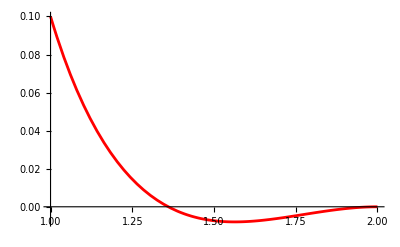

```mathematica
plotzex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All, PlotStyle->Red]
```

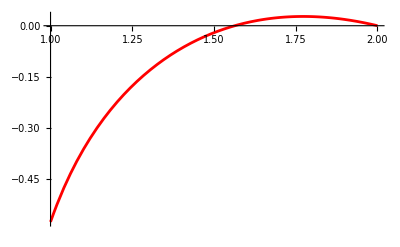

```mathematica
plotωex=Plot[Evaluate[z'[r]/. s],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Red]
```

```mathematica
(*check z*)
```

```mathematica
znum=Import["~/Documents/finite_elements/solution-res0.05/z.csv"];
znum=Table[{Sqrt[znum[[i,2]]^2+znum[[i,3]]^2],znum[[i,1]]},{i,2,Length[znum]}]
```

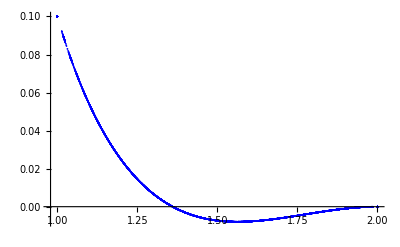

```mathematica
plotnum=ListPlot[znum,PlotRange->Full,PlotStyle->Blue]
```

```mathematica
(*res = 0.025*)
```

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*res = 0.05*)
```

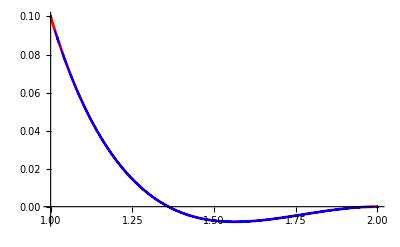

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*res = 0.1*)
```

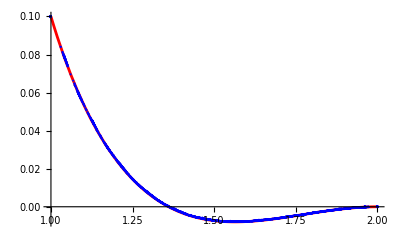

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*res = 0.3*)
```

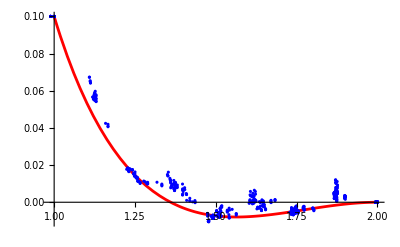

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*check ω*)
```

```mathematica
ω=Import["~/Documents/finite_elements/solution-no-flow-ring/resolution_0.04/omega.csv"];
ω=Table[{Sqrt[ω[[i,4]]^2+ω[[i,5]]^2],ω[[i,4]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,1]]+ω[[i,5]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,2]]},{i,2,Length[ω]}]
```

```mathematica
tabωresolution03={{1,-0.58676},{1.0000039804420782,-0.5870756166795122},{1.0000039804420782,-0.5867457134926728},{2,-5.7205*^-6},{2.0000426020462663,-2.6138950213616815*^-6},{2.0000426020462663,-5.886080620460548*^-6},{0.9999987412492078,-0.5871021255152655},{1.0000009799995198,-0.5867457301894662},{0.9999989644994639,-0.5866407755668377},{0.9999961362425356,-0.5866171617464375},{0.9999962064428044,-0.5865815608307009},{1.0000018276483298,-0.5867597329095541},{0.9999967656947697,-0.5867712702973885},{0.9999993976498186,-0.586771651742011},{0.9999988452493332,-0.5870370684614463},{0.9999988452493332,-0.5867740226376938},{0.9999993976498186,-0.5866285142557921},{0.9999967656947697,-0.5865603442151892},{1.0000018276483298,-0.5870776494285146},{0.9999962064428044,-0.5867756210068792},{0.9999961362425356,-0.5866041995963549},{0.9999989644994639,-0.5866205861459315},{1.0000009799995198,-0.5866405678925252},{0.9999987412492078,-0.586577082254367},{2.000037243753226,-7.4206780430490974*^-6},{1.9999563120478407,-2.295955177789983*^-6},{1.9999670954543227,-6.002419688446407*^-6},{1.9999959524959046,-5.476219732510893*^-6},{1.9999663247164938,-2.6011902479095292*^-6},{2.00004167206586,-8.967136460449424*^-6},{2.0000426020462663,-2.8121610980913958*^-6},{1.9999550375945954,3.5525621158690384*^-6},{2.000042652445192,-7.346834344775387*^-6},{1.9999924128856088,-7.866385641583853*^-6},{1.9999924128856088,-3.2052568593252275*^-7},{2.000042652445192,-5.816595503989517*^-6},{1.9999550375945954,-7.589349222698258*^-6},{2.00004167206586,-5.832287578263963*^-6},{1.9999663247164938,-7.646117890593845*^-6},{1.9999959524959046,-6.479452552805372*^-6},{1.9999670954543227,-7.535370783976079*^-6},{1.9999563120478407,-6.2404549963496675*^-6},{2.000037243753226,-2.6783505190871066*^-6},{2.,-5.709599901474399*^-6},{2.000037243753226,-7.161824033396526*^-6},{1.9999563120478407,-3.7945488880351596*^-7},{1.9999670954543227,1.0914646570743327*^-6},{1.9999959524959046,-6.657829773796641*^-6},{1.9999663247164938,-8.133880455365162*^-6},{2.00004167206586,-1.056492636884626*^-6},{1.9999550375945954,-6.848589404526624*^-6},{2.000042652445192,-2.3955149027159523*^-6},{1.9999924128856088,-5.689812674629813*^-6},{1.9999924128856088,-5.876841454134185*^-6},{2.000042652445192,-5.968306038576899*^-6},{1.9999550375945954,-7.177018338004055*^-6},{2.0000426020462663,-2.9123013150023207*^-6},{2.00004167206586,-7.0218921916230704*^-6},{1.9999663247164938,-2.6535181789884906*^-6},{1.9999959524959046,3.342195013774019*^-6},{1.9999670954543227,-7.2359606929995725*^-6},{1.9999563120478407,-7.758704480955094*^-6},{2.000037243753226,-4.0906434245428967*^-7},{1.2559636898015802,-0.13349924515452266},{1.2560134738130797,-0.13176745906838097},{1.2559370165736816,-0.1320372118121031},{1.2574374241289308,-0.1260146223258525},{1.257386619607907,-0.12204776877525074},{1.2658836504197375,-0.1282507240425835},{1.2574293946381245,-0.1256301477232942},{1.2574296142925854,-0.12536293087838843},{1.2658427489226298,-0.12677254205277944},{1.2658497679029688,-0.13202061881075458},{1.7355842269679682,-0.0010174059942252456},{1.7355325090588192,-0.0015786843609664376},{1.7465731387205061,-0.00789899920257947},{1.746544606501649,-0.009621259432737044},{1.7355133868973756,-0.0027628011713997404},{1.746493841958797,-0.010441412011821003},{1.7355,-0.002707499999918737},{1.7497190596207153,0.001419688262719425},{1.749653185519919,0.0011760194849064131},{1.7496794342107356,-0.0008702487668473147},{1.7496793906599004,-0.00003729595167454561},{1.2623778594382904,-0.13633199395352116},{1.4913917357957969,-0.05593408172902865},{1.2588538554176971,-0.13669704275791572},{1.491403411589232,-0.05918909904861676},{1.224363846289166,-0.1479967603006177},{1.4877982986950886,-0.06266498750117691},{1.2588369739167975,-0.13530815366824295},{1.4914,-0.06091300000094396},{1.2588100094930925,-0.13537049174610577},{1.491393206669522,-0.06075999601899746},{1.2301176417318793,-0.1444428128433655},{1.4932538423188468,-0.0625837881219698},{1.2301328010015828,-0.14692531372453618},{1.4919428982370606,-0.06034225184246644},{1.253528979002879,-0.13039008118505144},{1.4914128368764967,-0.05746265459232923},{1.253479298153743,-0.13086258235106552},{1.4913936965469579,-0.05736481831597058},{1.2483623571419478,-0.13165067937346694},{1.2535066063248332,-0.127001100095316},{1.4913534983028,-0.06051924799366029},{1.5405295130574423,-0.04508481404238455},{1.5415034419682625,-0.046612497114021614},{1.541457939614312,-0.04714381924568296},{1.5414804921243732,-0.04735163232549733},{1.476377982123819,-0.062072460209118885},{1.4780644674708878,-0.059934000004465166},{1.563251325795056,-0.04871147960886689},{1.4780571047493396,-0.06162022561736258},{1.56330130288438,-0.05089993753167431},{1.478096695213138,-0.06149916278846168},{1.5632985267056323,-0.05058878113744407},{1.750564492528053,-0.001741796305428683},{1.7549017942893557,0.0005735669649865521},{1.7540366137854704,-0.0020405133717680485},{1.754945031190436,-0.0001715178831816852},{1.7549282520946548,0.00016729390597568705},{1.7555173055256392,-0.003983959091708227},{1.750631868783383,0.0024653800687402215},{1.7326232620149251,-0.0022130728071149313},{1.7468645511315408,-0.00866322336794642},{1.7499148836443443,-0.0008525416909953042},{1.7498688231121782,-0.002034714357426865},{1.749898125720466,-0.002228266504597009},{1.7417237456324697,0.0010800228579400338},{1.7416759450598152,-0.002211414649277782},{1.7424322942656911,0.0006466028371419771},{1.7444840279005136,-0.006690000630183794},{1.7426335135363373,-0.0031447522542356566},{1.7426916778650203,-0.004124908011729646},{1.7376513862107095,0.0007077755007475737},{1.7426293982370433,-0.004057787935492024},{1.7435612237314753,-0.008022037103501285},{1.7547566019536727,-0.006147914718194527},{1.7456954490689378,0.002290382722617791},{1.7465247779519188,-0.0034366713119516014},{1.8032741513424961,-0.0028652205440606194},{1.479187093102154,-0.059153083249596256},{1.8032894571033238,-0.004239457831290345},{1.476880109182868,-0.0629520681617414},{1.8032781283262989,-0.0039492612781866785},{1.476909914111216,-0.06240042870553854},{1.510084578558433,-0.05691001318749947},{1.5105306609268148,-0.05573124089010379},{1.5107519918570353,-0.05785067381746044},{1.5059116375139676,-0.058460254643714744},{1.8003169755629145,0.0025323047895910267},{1.799885686397889,0.001804423975780226},{1.80032438066033,0.00030786533468857833},{1.8002849559167016,0.0018452645810776345},{1.5423417739269074,-0.05663899778684195},{1.5506371883841816,-0.04644968296875057},{1.5413688721393073,-0.05187772015209936},{1.5355420989344448,-0.053787388452139116},{1.5355878913627836,-0.056377191176709585},{1.5356073937045238,-0.0569534747061972},{1.5355296967496266,-0.05704014370116174},{1.3332057305607412,-0.15040940644296452},{1.3330564930264583,-0.15103944786532295},{1.333127512618354,-0.1510976768414094},{1.3180784324538506,-0.15123171977626548}};
```

```mathematica
tabωresolution01={{1,-0.57834},{1.0000039804420782,-0.5783317661839028},{1.0000039804420782,-0.578363918855921},{2,-8.8948*^-7},{2.0000426020462663,-8.949948856932464*^-7},{2.0000426020462663,9.578646965019428*^-8},{0.999999243761714,-0.578352232396101},{0.9999983256985984,-0.5783400135154952},{0.9999987412492078,-0.5783266360691113},{1.0000016276486752,-0.5783325416778047},{0.9999967154446059,-0.578325788143087},{1.0000009799995198,-0.5783253460414386},{0.9999981328482569,-0.5783455910589784},{1.0000044772399772,-0.5783535775722415},{0.9999989644994639,-0.5783201868508635},{1.0000054516851395,-0.5783182864907916},{0.9999980904981769,-0.5783348096313733},{0.9999961362425356,-0.578325835010762},{0.9999957849911169,-0.5783333260801069},{1.0000025292968013,-0.5783454246927673},{0.9999962064428044,-0.5783379140379553},{1.0000008254301593,-0.5783043225501708},{1.0000003265999466,-0.5783565263687894},{1.0000018276483298,-0.5783629937558405},{1.000003582493583,-0.5783129439975891},{1.0000049720876392,-0.5783205010397854},{0.9999994755998626,-0.5783495670865926},{1.0000018522482845,-0.5783420099670041},{0.9999967656947697,-0.5783217737691377},{0.9999953384391349,-0.578321500280873},{1.0000017488484707,-0.5783406780697895},{0.9999993976498186,-0.5783479618679997},{0.9999974882468455,-0.5783283682181031},{1.000003271994647,-0.5783270697169236},{0.9999988452493332,-0.5783317673689939},{1.0000030806532547,-0.5783195031921402},{1.0000030806532547,-0.5783308365992259},{0.9999988452493332,-0.5783265966830231},{1.000003271994647,-0.5783261717198619},{0.9999974882468455,-0.5783386288438753},{0.9999993976498186,-0.5783369595613725},{1.0000017488484707,-0.5783269334938268},{0.9999953384391349,-0.5783430047811177},{0.9999967656947697,-0.5783389334246373},{1.0000018522482845,-0.5783640527261755},{0.9999994755998626,-0.578383633504457},{1.0000049720876392,-0.5783387311491437},{1.000003582493583,-0.578344038886192},{1.0000018276483298,-0.5783234684280789},{1.0000003265999466,-0.578318104981338},{1.0000008254301593,-0.5783428894823366},{0.9999962064428044,-0.5783402724969022},{1.0000025292968013,-0.5783292253337402},{0.9999957849911169,-0.5783390365041763},{0.9999961362425356,-0.5783300887271973},{0.9999980904981769,-0.5783247834122283},{1.0000054516851395,-0.5783396340744114},{0.9999989644994639,-0.5783339439651091},{1.0000044772399772,-0.5783301622770773},{0.9999981328482569,-0.5783268381239639},{1.0000009799995198,-0.5783324728344543},{0.9999967154446059,-0.5783410041930649},{1.0000016276486752,-0.5783528717447145},{0.9999987412492078,-0.5783323392762901},{0.9999983256985984,-0.5783501326324376},{0.999999243761714,-0.5783632779524539},{1.9999861861682946,7.833914608189038*^-8},{2.0000386870258287,1.5696726370171077*^-7},{2.000037243753226,-1.1022279279475264*^-6},{1.9999554630291143,2.325252279846572*^-7},{2.0000428395661927,-5.859804484258926*^-8},{1.9999563120478407,-1.0946296160631484*^-6},{2.000013770352594,-3.406429946129271*^-7},{2.0000439987410275,5.557837281078418*^-7},{1.9999670954543227,-5.166280997064549*^-7},{1.9999630846843148,-9.036421291172276*^-7},{2.00003099225987,5.629844259201828*^-8},{1.9999959524959046,-4.6862889338868324*^-7},{2.000022562372735,-1.7067872454149823*^-7},{2.000024442350643,-2.697023539202459*^-7},{1.9999663247164938,-3.7916403422817404*^-7},{1.9999942849918348,-1.5795364635318966*^-7},{2.0000469294494065,-2.1577208696738138*^-7},{2.00004167206586,4.394363438898401*^-8},{2.0000268648195703,-9.838659343096027*^-7},{2.0000445045048374,-6.846351153266047*^-7},{2.0000426020462663,3.675324661824349*^-7},{1.9999605862116383,-1.7180511574523718*^-7},{1.9999876011865674,-3.8419147675922237*^-7},{1.9999550375945954,-4.1261660811760563*^-7},{2.0000418972861542,-3.7514615619707254*^-7},{1.9999530650492776,-2.0058728727722243*^-7},{2.000042652445192,-1.2077481032951092*^-7},{1.9999853624464354,-2.4286187745186955*^-7},{2.0000217414068278,-3.4917667420393574*^-7},{1.9999924128856088,-3.7104460557893336*^-7},{2.000021619713397,-2.298409954517757*^-7},{2.000021619713397,-3.4288218899267265*^-7},{1.9999924128856088,-2.8735459009607303*^-7},{2.0000217414068278,6.000929765672795*^-9},{1.9999853624464354,-1.0480842706948271*^-6},{2.000042652445192,-2.2768094442550348*^-7},{1.9999530650492776,-1.978686434775158*^-7},{2.0000418972861542,-4.166979707429468*^-7},{1.9999550375945954,5.663027311664943*^-7},{1.9999876011865674,-2.3733752135182137*^-7},{1.9999605862116383,-1.2237140156026093*^-6},{2.0000445045048374,7.686632955103275*^-7},{2.0000268648195703,-5.070268894070493*^-7},{2.00004167206586,-5.707030588122684*^-7},{2.0000469294494065,3.650974330892396*^-7},{1.9999942849918348,-8.862155323644758*^-8},{1.9999663247164938,-9.903748255765104*^-7},{2.000024442350643,-9.504673841714546*^-7},{2.000022562372735,2.692432126171401*^-7},{1.9999959524959046,4.0062271076103415*^-7},{2.00003099225987,-8.448270084509049*^-7},{1.9999630846843148,-7.795996045827552*^-7},{1.9999670954543227,2.3373211592454209*^-7},{2.0000439987410275,-3.5172079236397047*^-7},{2.000013770352594,-3.076091420568263*^-7},{1.9999563120478407,-2.4975321560326696*^-7},{2.0000428395661927,-2.523080006173535*^-7},{1.9999554630291143,-5.296707949663815*^-8},{2.000037243753226,-9.246674659565406*^-7},{2.0000386870258287,-2.019838429229241*^-7},{1.9999861861682946,3.890721522886163*^-7},{2.,-3.4246993432655364*^-7},{1.9999861861682946,-2.807600141857928*^-7},{2.0000386870258287,-3.577348181519252*^-7},{2.000037243753226,-2.690984933810596*^-7},{1.9999554630291143,-4.3750248501771893*^-7},{2.0000428395661927,-5.086739093151971*^-7},{1.9999563120478407,5.167416376919732*^-7},{2.000013770352594,-3.186110063070521*^-7},{2.0000439987410275,-1.1411235460003054*^-6},{1.9999670954543227,-1.9403101225115248*^-7},{1.9999630846843148,5.17303398209129*^-8},{2.00003099225987,-2.8378635240981336*^-7},{1.9999959524959046,-2.6997054635344615*^-7},{2.000022562372735,-2.652052081706177*^-7},{2.000024442350643,-5.765511688670839*^-7},{1.9999663247164938,-3.5427424514282225*^-7},{1.9999942849918348,-1.0119963917837926*^-8},{2.0000469294494065,-1.2045618352881428*^-6},{2.00004167206586,-5.964690719507617*^-7},{2.0000268648195703,6.769300071987456*^-7},{2.0000445045048374,-7.519412176142237*^-7},{1.9999605862116383,-1.2930607822120028*^-6},{1.9999876011865674,-1.7015771487687888*^-6},{1.9999550375945954,1.1293214885053004*^-6},{2.0000418972861542,-3.002677097988757*^-8},{1.9999530650492776,-1.4272020628292448*^-6},{2.000042652445192,7.103623506543762*^-8},{1.9999853624464354,-3.054239853299699*^-7},{2.0000217414068278,-2.481730521843547*^-7},{1.9999924128856088,-5.433440612068709*^-9},{2.000021619713397,-7.983427725290327*^-7},{2.000021619713397,-1.8210729149627518*^-7},{1.9999924128856088,-3.239830772183338*^-7},{2.0000217414068278,-2.95476927457956*^-7},{1.9999853624464354,-3.2681981292125883*^-7},{2.000042652445192,-3.09948654965991*^-7},{1.9999530650492776,-2.024482109484026*^-7},{2.0000418972861542,-1.7989824537586711*^-7},{1.9999550375945954,-2.3500083310136298*^-7},{1.9999876011865674,-4.524218497470535*^-7},{1.9999605862116383,-4.77928798492258*^-7},{2.0000426020462663,-2.446048896655879*^-7},{2.0000445045048374,-6.958623654949884*^-8},{2.0000268648195703,-2.0426855618104542*^-7},{2.00004167206586,-4.262158893516943*^-7},{2.0000469294494065,-2.782348712953402*^-7},{1.9999942849918348,-4.137012821531039*^-7},{1.9999663247164938,4.3023084407282133*^-7},{2.000024442350643,-2.320526640437197*^-7},{2.000022562372735,-1.1580242361127723*^-6},{1.9999959524959046,-7.612755406329348*^-8},{2.00003099225987,-2.895914624530689*^-7},{1.9999630846843148,-1.390423013952246*^-7},{1.9999670954543227,-7.577408865598081*^-7},{2.0000439987410275,-3.5441160316782624*^-7},{2.000013770352594,3.9105032754955187*^-7},{1.9999563120478407,-5.139609719511753*^-7},{2.0000428395661927,-1.7657539279338593*^-7},{1.9999554630291143,-7.132946389912833*^-7},{2.000037243753226,-8.045559876576698*^-7},{2.0000386870258287,2.648572467304286*^-7},{1.9999861861682946,1.7997401306536007*^-8},{1.101750218969799,-0.3521583851036526},{1.0878998524680479,-0.35834547786322996},{1.1037298050247624,-0.32913477632494464},{1.0855590289339405,-0.3786746215023329},{1.0848069675292467,-0.3793561681644574},{1.082325490275453,-0.37804856053594876},{1.0851077158052098,-0.37480458057401583},{1.083641775357521,-0.3612224015365737},{1.0855224034537474,-0.3810191377018624},{1.0858125912421535,-0.3569064622437905},{1.0841011678810237,-0.3384082979627069},{1.0799192609172226,-0.3751669727196906},{1.0754174131471,-0.3907269007020664},{1.077602305584022,-0.3908226155582981},{1.0836428413919412,-0.36871183330734214},{1.092569660250549,-0.3510528920527081},{1.083625774165602,-0.36581225645840054},{1.0841942118458299,-0.3707190151990535},{1.9129673218327594,0.013157547933377856},{1.9106769193141995,0.012752322830562872},{1.9146323224055317,0.013721863974902302},{1.9054924455373734,0.014454550063688397},{1.9112633060099282,0.01220502863663455},{1.909683854044957,0.017735893140772528},{1.9130368135506437,0.010955515237106634},{1.912281242286291,0.011062631500117423},{1.933197561037154,0.014354119495739781},{1.9194690620064707,0.013348260343001886},{1.924859535680461,0.012259114625035821},{1.93068884339243,0.012915477646923752},{1.8991517185311972,0.01570991121397861},{1.9253416346196848,0.011360204223870357},{1.913059413112933,0.012533600550326736},{1.93113828589151,0.011388883433092257},{1.912437906861292,0.011840838387879965},{1.898937926842265,0.015284638791887652},{1.9176659883566793,0.013347257513876973},{1.933248267967671,0.010936756193361076},{1.9152552962986422,0.011578433999298123},{1.909342590082775,0.01575566750418312},{1.914509945025097,0.015079074111376089},{1.9130018348135476,0.01395869692545414},{1.917536085423166,0.011493124470790076},{1.9130619948396863,0.011653579009010748},{1.9101316515258837,0.012215157500338308},{1.910212880806744,0.014447133519665548},{1.9111439846332876,0.016140681365731317},{1.9093000465091912,0.01789153160209466},{1.9210082378792654,0.01211693510783525},{1.9218693035687937,0.012870217794763071},{1.9177971313202031,0.01304263785074132},{1.9071018962027173,0.013924735153310977},{1.9125317959186978,0.012963707511116317},{1.0759584491047969,-0.3901483046573611},{1.082207558881382,-0.36955167233667},{1.0836578929256226,-0.3613689311326574},{1.0851204064065887,-0.36683130599135605},{1.0875207681552568,-0.3648122686925648},{1.0847987511515673,-0.35977895493121675},{1.0856686843139578,-0.37547383256945543},{1.912978077954894,0.014128174526816124},{1.91430280585387,0.012501240066001765},{1.9112753700082046,0.012320570771494281},{1.9129673218327594,0.016228545346115467},{1.9125395339443312,0.013079932940214006},{1.908547746324414,0.01235438904025829},{1.9183687446369637,0.013264962611145787},{1.906997556920302,0.013292196195539941},{1.9173648804804995,0.013590936419190885},{1.9129992864870597,0.01358415654337244},{1.9123961007333183,0.011852755766605126},{1.9216053043224042,0.01496402795273276},{1.9202744905091045,0.011614244836469778},{1.9145200165054426,0.011861836064504494},{1.909774774678941,0.014933860776747694},{1.9252812911364405,0.013065755838281453},{1.926772466483783,0.013451987378302176},{1.0834446719606867,-0.37574121885087974},{1.1685783919361166,-0.26071283210639346},{1.1709373570349526,-0.25912271179759017},{1.25688033706475,-0.17000246180873488},{1.2491684405635615,-0.1711722764654012},{1.2613411643960566,-0.16760260123693219},{1.344823757821076,-0.10368057828329277},{1.35232157954386,-0.09782381475020266},{1.4338673682039076,-0.0531350176240048},{1.4442717334352286,-0.04781243321556489},{1.4304127026840892,-0.05578043088563207},{1.5176222969171216,-0.019506531302377582},{1.5175833774788126,-0.020079378235299254},{1.3669891683550386,-0.08800955975735517},{1.4613631262968145,-0.03915256679904687},{1.3921163505971763,-0.07537288459760501},{1.4856152391854358,-0.03040978304367066},{1.4210608976746917,-0.05801435242142068},{1.5155643577228912,-0.020974292195522957},{1.4524447122352027,-0.048367293349079916},{1.5507935027269102,-0.010902571510178285},{1.4923154709712019,-0.0314693198144203},{1.5371722772675809,-0.01214661835639506},{1.5819052983348907,-0.0016935091504022889},{1.591713433033723,-0.001665513068484504},{1.5381452832876354,-0.016510995775846263},{1.4384641734850403,-0.05300684099435652},{1.4893341735151315,-0.03274939869598342},{1.3897356439265707,-0.07571941920024612},{1.4458737859509039,-0.048861095267411454},{1.5450729634874854,-0.014922692526414628},{1.5064331640003152,-0.0261663222730217},{1.4080440886563177,-0.06475385651241121},{1.4735383567793545,-0.03726105774946005},{1.3764103667148109,-0.08066500156417725},{1.4468791811689046,-0.04718324434487149},{1.5427949474897824,-0.01476566720487712},{1.5205288170909488,-0.020329936762882816},{1.4266046058530022,-0.054459203956408214},{1.504655195340115,-0.023406119672513562},{1.415908357941643,-0.057611140473868165},{1.4956787196787953,-0.025167317328740134},{1.4102196494163595,-0.059748667010044665},{1.4930282789016422,-0.02672115786671462},{1.408127731457626,-0.061621175221923494},{1.4964243950163336,-0.026236469460638175},{1.4170041703890641,-0.05778726777319014},{1.5070065380083792,-0.023018586986254416},{1.4317346758739902,-0.05175580396190791},{1.5239575806432408,-0.01786370585624131},{1.4509299175356472,-0.04682748489699588},{1.5467761823870962,-0.012331532609044602},{1.4782601381691924,-0.03661663153349856},{1.575776685479259,-0.005346563645493721},{1.5118815075593721,-0.024121248409785096},{1.5798383366661286,-0.002550826654519682},{1.5851418093107632,-0.001565844557515796},{1.4133713807771828,-0.06292794888141394},{1.4520247023036488,-0.04755986043518322},{1.5512833492305653,-0.01051450145976892},{1.496334457399147,-0.02622661351273803},{1.4013231256209255,-0.06564740257122201},{1.4474801864274343,-0.045141865686792085},{1.546032262955725,-0.008456245618707635},{1.5008506454674295,-0.022212200794714893},{1.4013279075220046,-0.072610151652462},{1.4609415676542303,-0.03982017271464796},{1.5596532467186415,-0.0027989431696977107},{1.5246311156801176,-0.014088636590246992},{1.4269369693157439,-0.055742376636399055},{1.4954774287831964,-0.025309687108281475},{1.3993832793412961,-0.07053742088190683},{1.472516944690281,-0.03592590323035429},{1.5673738057336544,-0.0019730410956768987},{1.5486938387234581,-0.008572742662257549},{1.4561233806240461,-0.045633819979954166},{1.5363593395101292,-0.014016023304721174},{1.4463464459112139,-0.05219914986027805},{1.5303467936712907,-0.017526328424981214},{1.44186465484802,-0.054621069886966134},{1.5305585687911458,-0.018083879754344046},{1.446514981775163,-0.052859562336620716},{1.5376434483000279,-0.01504462138187851},{1.4581057631049952,-0.046945029382666946},{1.5510776334213578,-0.009333889920819386},{1.4790006998308014,-0.03648751145024721},{1.5712951239025723,-0.003448085086997278},{1.5034477116281764,-0.023638685049786036},{1.5970610140191888,0.0024430485596670646},{1.5303404628003536,-0.017923314536301534},{1.422346854969279,-0.056176455793917994},{1.464949023353714,-0.03862976284215462},{1.5652268489596006,-0.00740722017981385},{1.5068542168703647,-0.024198772467009674},{1.6185276094339571,0.004776699424178384},{1.4092823231702014,-0.06333511474210145},{1.45409435419439,-0.043024404592823605},{1.553111569752798,-0.010671418916245661},{1.5044155524322396,-0.024846349712064415},{1.4046987049186028,-0.0628287162015388},{1.46071292953133,-0.04046809219314995},{1.559947913521474,-0.008955499117572102},{1.5212105812148429,-0.019667531864067785},{1.4227692890978496,-0.05703035848591444},{1.488158545619384,-0.030881757064985527},{1.3909538894226507,-0.07417200234640642},{1.4611734752930605,-0.04163050478164459},{1.5571870351695072,-0.009512888295006579},{1.534749752272337,-0.015913086315759363},{1.440687297820037,-0.050750781436495494},{1.5184530534725134,-0.020867499161424403},{1.427232327128278,-0.05665031509108538},{1.5086341945282826,-0.02391424496465213},{1.4206001161481019,-0.06001370028827441},{1.5054572389809018,-0.025598916888591144},{1.4206537540512818,-0.06156390768024036},{1.5087131602793156,-0.025904928934778},{1.42697582320094,-0.06043056413287044},{1.518451487535904,-0.023312736620545463},{1.4407099822309832,-0.054686009031461306},{1.534746621563312,-0.017134251081272176},{1.4612269455495268,-0.043784328433622836},{1.5572200390439368,-0.009306795466681693},{1.4881571556794666,-0.031824591790761685},{1.585646087908648,-0.001563434062054598},{1.5212401153006716,-0.01958575100690868},{1.4252785089588629,-0.05737327652525501},{1.4611417591732843,-0.04529091418032067},{1.5600373617320835,-0.008829479054723794},{1.504383395414879,-0.0267871487034637},{1.4085014271913252,-0.06551987723862235},{1.4538820146421787,-0.04743228639290396},{1.5531879501206545,-0.012150769499939755},{1.5072009495750724,-0.027962764468720744},{1.404632999897126,-0.0737284260782601},{1.4660052476372654,-0.045649590052871815},{1.5653081741625194,-0.011193184634951564},{1.5294726857319159,-0.023899315889062585},{1.4315352807737571,-0.06284057927749893},{1.4995191983099116,-0.0358340126492296},{1.4030306518390823,-0.0784077523579415},{1.4756095172924306,-0.045774414406012646},{1.5707125443250272,-0.014047526918097991},{1.551110181500979,-0.02032067423843424},{1.458140546681286,-0.05382927612529805},{1.537836363649917,-0.024883678127870925},{1.4461341337856595,-0.05948930620135059},{1.5306516339128247,-0.026322668570250705},{1.4418555379787534,-0.059286557778064755},{1.5300470711713414,-0.025093189891607262},{1.4448658125929894,-0.055310581538766036},{1.5360290603045246,-0.021620268230092013},{1.454623528752371,-0.050475297662051735},{1.548421940040892,-0.016793406875462692},{1.472277122045982,-0.04137241901535003},{1.5674610713188382,-0.010303946104008031},{1.4955010185218864,-0.0305718582961506},{1.5921484516526718,-0.0031324825356724957},{1.5246180604007027,-0.019858098350247017},{1.4269827500358931,-0.05699966816554307},{1.4608769511495485,-0.04140729505821849},{1.5596682218023166,-0.009569562631565717},{1.5006422492053195,-0.027213547680418886},{1.5986460435318381,0.0007546248785846221},{1.5923579559885397,-0.0013750940953729622},{1.3576895600983312,-0.10170306887385906},{1.6000840227938031,-0.00044188544221912746},{1.5459052752351936,-0.01407204369406809},{1.4461840188579045,-0.04822659431341205},{1.4963430990585014,-0.02979652213322826},{1.3967197830631597,-0.07112830638234581},{1.4520135157773155,-0.046339822852116734},{1.5512965931761726,-0.013079562328218004},{1.5118811593508268,-0.024055149688892188},{1.4133289547730918,-0.06219406604749872},{1.4781417388396825,-0.034937689758046356},{1.3807734222529053,-0.07833442101131985},{1.4504763937755072,-0.04421712894827465},{1.5466780764270243,-0.012299920752059355},{1.5235208034024348,-0.017601362764533647},{1.4292451023180033,-0.0516313961687315},{1.5066246020824166,-0.02138690705930565},{1.4161408122075996,-0.05646671680575612},{1.4964192569263468,-0.02456651852069116},{1.4083509548759499,-0.0603530732064486},{1.4926138684870913,-0.026645142713508124},{1.4075981269169124,-0.06243035206538549},{1.4954473986402865,-0.02611066171668961},{1.4152181457287778,-0.05950911034752956},{1.5050407893475846,-0.02228893696265976},{1.428934190367072,-0.0522928437738653},{1.5209884123161492,-0.01631616074326913},{1.4473722823102562,-0.04511467705031186},{1.5430008663639823,-0.010400617569202558},{1.4736766341704681,-0.03286862454208997},{1.571149740224973,-0.0032140113141647052},{1.5065316028930857,-0.022215516651371003},{1.5865224311052146,-0.0002428878447886531},{1.5792760572173568,-0.0018340675072561765},{1.5971104026960692,0.0030574316914829137},{1.408115668805656,-0.06267604243595752},{1.4459086487728054,-0.04604439758556353},{1.545034992961648,-0.010507426468186783},{1.4894283165362472,-0.029474340007911107},{1.5889661576005953,0.0004742724081285478},{1.5381895707616793,-0.013553488048730293},{1.4384850894256778,-0.051855843020786524},{1.4922506419499373,-0.029766816018223705},{1.3928276857170812,-0.07575114827336325},{1.4517175236250335,-0.046715617615921814},{1.5505679120889868,-0.010568860442830777},{1.514883910271675,-0.02165023228355378},{1.4170507303904119,-0.06238405263419506},{1.4850497097403843,-0.032390410519260705},{1.5818203712495298,-0.0018108719623690654},{1.6294614815944561,0.006803168853769189},{1.3752103551457138,-0.08993731784901729},{1.6196560923850472,-0.003744521600921551},{1.5564694812620001,-0.008424791254093792},{1.6263128240286369,0.0009884511074676825},{1.604982900968107,-0.0005566105224305765},{1.3623183539833852,-0.08873058345470566},{1.3388546678411364,-0.10854393761373037},{1.3302730600895443,-0.10793571322141558},{1.6276319923127585,0.0017095893599671339},{1.603163046480301,0.003686485357166458},{1.6062255568879484,0.0036346945402309233},{1.6225854492136924,0.01225033901889884},{1.6106299016223435,0.0010005008974295362},{1.3479138536642465,-0.0999050689210762},{1.6198049705134256,0.0041270258739118946},{1.340379815574675,-0.10126185848434859},{1.6184534989921706,0.004596840526238679},{1.3418215252409689,-0.10124252683724365},{1.6377970487517677,0.0098562026591163},{1.6151442636495357,0.002452842235311083},{1.6443344058919402,0.006451226861148047},{1.616012369507115,0.00672914596768631},{1.629234866432707,0.009710794819068199},{1.3310475010306733,-0.10940026699816804},{1.6455566821291814,0.007281391478108549},{1.3765752299093574,-0.08799298328793546},{1.64496664141374,0.0017978373974552608},{1.3383111798763732,-0.1028711706873342},{1.629395008246926,0.006402637733145076},{1.6421798645702608,0.014377899528185207},{1.3557678267314062,-0.1037342409423191},{1.6391904250574427,0.010716698574776267},{1.6494711826824984,0.009853175736340463},{1.65924063116234,0.010205633541614507},{1.3618417651709762,-0.09986632398597736},{1.362822577007,-0.09535929550375544},{1.668788860945566,0.014808160794288802},{1.6520662365655925,0.01201505900953742},{1.3387826162600112,-0.10875884316959303},{1.6628299371853996,0.008777673996359267},{1.3296163718907796,-0.11329528900564273},{1.3411329343506555,-0.09444734067419563},{1.6584914892757212,0.017928376715990957},{1.3340669316417373,-0.117661194829881},{1.6789359956829804,0.015578647460804538},{1.303748070794354,-0.13759969870612895},{1.3440319312055053,-0.10201788702818756},{1.6890629929342482,0.013043413833090609},{1.6643421096937974,0.00922841218854083},{1.4614010903581536,-0.04186111339564369},{1.29345014979318,-0.1417163096925767},{1.688612940877808,0.01691508270341207},{1.6911637045537606,0.0140246235146457},{1.6664464025284462,0.01503581147037358},{1.7258789524181584,0.014927683870240434},{1.3245220061969525,-0.11217769031759396},{1.720698616841427,0.02500737187723647},{1.6936035316743998,0.017802346024982454},{1.69948032118645,0.014929768535528895},{1.7036677557845603,0.014147466639057483},{1.3149665749364126,-0.11533329819226298},{1.3098499525136458,-0.1183465932281164},{1.718531502446202,0.016598811854421025},{1.6902400302915561,0.016900026012916458},{1.6960980279453188,0.017338910498956202},{1.690243118607498,0.017454596486868448},{1.285358339763663,-0.14601903305385616},{1.331122769732379,-0.11261880643070898},{1.2641772757014738,-0.1550985254273001},{1.3387774060313389,-0.10465663396975508},{1.3465410884559,-0.09649927383872448},{1.2901481654833293,-0.1351999063182436},{1.2970737496765556,-0.12658781788695062},{1.279678378499848,-0.1433208599921826},{1.2941314990757316,-0.1376758576058534},{1.2846971627586012,-0.14243177186371886},{1.307468892325932,-0.14003856920395238},{1.34675505078095,-0.09950090052075525},{1.314486507195871,-0.12266060904950345},{1.1778388579937409,-0.24991959163361568},{1.650701002604651,0.007567085668628288},{1.666450953853728,0.005902786995472182},{1.739382786853141,0.013770109836393511},{1.7217000173182435,0.01196897130095861},{1.662800416887126,0.018194338037656185},{1.7363602431811207,0.025213330495170373},{1.7195158976002518,0.023731263855686975},{1.643329379643655,0.00782316423551543},{1.7139353864425577,0.016310943155228994},{1.693066920000506,0.015150041441948633},{1.6536350602233856,0.009977326544933808},{1.7246909237599646,0.018152779050837814},{1.7044710763166384,0.016943310661749887},{1.639160482198128,0.006047033143885856},{1.7104369624455618,0.015046008762698893},{1.6903768906666938,0.01381412834553731},{1.7400563927643264,0.017215124362959168},{1.433849322662601,-0.05406456954350518},{1.7094271116371123,0.014886576342894784},{1.2325962495886478,-0.1997816944373964},{1.2638494771925968,-0.17065490708521486},{1.7354972205105947,0.021275959419362604},{1.7103437468824798,0.019665773112164407},{1.23694781927129,-0.19857082329042833},{1.2691868213939193,-0.16251048745800362},{1.743916035822826,0.017700443751832134},{1.7354343411376876,0.0165050071783312},{1.7360339508200868,0.020778113676267758},{1.690931231274649,0.017004829413035806},{1.7888276699838919,0.022022041523628008},{1.7482243052880828,0.021299060877582356},{1.2390843241684564,-0.1885423970130372},{1.7419039325117789,0.01708726046566792},{1.1932627462549896,-0.23800532659829735},{1.2544190108970765,-0.17097561294660368},{1.8047689692589466,0.01835029168835862},{1.2118544582993453,-0.22205179428694216},{1.7483080749398832,0.01865782423794024},{1.820035479764062,0.019165819584199505},{1.2331350584992709,-0.17669352152323778},{1.7460432136977595,0.019053968940747467},{1.7107790272562966,0.0175313727355548},{1.6883006771307059,0.012551486733994508},{1.7484114847483703,0.01742949978642229},{1.5371420165033547,-0.014975580730897133},{1.7452939305744464,0.021551095253978254},{1.7246795664412564,0.020191258642238984},{1.7734005194540798,0.022408920608771154},{1.7558064608891264,0.01873644546867707},{1.7031531538883988,0.01571475437243842},{1.2498379435686855,-0.17175067897512847},{1.2024756059479962,-0.23073254935701293},{1.2822885790647909,-0.15667119810621752},{1.2499372278638634,-0.16376444813138594},{1.1693073088371593,-0.2529082130634178},{1.7632659553932866,0.02211727556667512},{1.7031168727671042,0.01885970741141988},{1.7606949257608486,0.02253855643427357},{1.7393428070394865,0.02249208574736807},{1.754950489330112,0.026582668162796662},{1.7549545652523315,0.01776327483641593},{1.7354295309519197,0.016104772016683127},{1.7875629037603125,0.018976467690531365},{1.7206872731847587,0.016550298897888224},{1.781071840213078,0.019702494597748414},{1.754683726487483,0.02609212891695819},{1.6989850646783213,0.02220004936131753},{1.8216299130174602,0.02580232179111646},{1.8277374346442652,0.025596754880224712},{1.7584343021278903,0.015380652327625581},{1.2390083759200339,-0.17241706388092048},{1.1948136792404078,-0.22835029937341617},{1.216773697842372,-0.22116890048716553},{1.7597548539782466,0.018235508122312973},{1.7054445568238212,0.01576047668536237},{1.8195643087288782,0.017854333407262224},{1.7801453995671253,0.022296359347754143},{1.207309136302712,-0.20427032678245627},{1.7741226705050583,0.022069233797037128},{1.7809290187988966,0.022412473646434096},{1.8186731517510233,0.019395714720392532},{1.7544491413546306,0.019697000629677892},{1.1400387637707763,-0.26773266490556863},{1.2310955862564044,-0.18706915561310009},{1.19787943466778,-0.2312856799122173},{1.2687016867648595,-0.16085459405385294},{1.8133141371532955,0.02440520762137465},{1.7457458520643834,0.024025546760086558},{1.7800118977411359,0.018944348302274108},{1.1360706779509804,-0.3398844874655422},{1.8538410719638294,0.019192147562741124},{1.8389849788402297,0.01604995171772108},{1.7841547814301315,0.019311058249319963},{1.7651611798643205,0.019802177466131877},{1.2232213884657184,-0.18533652970568024},{1.187245507761558,-0.23260939282952744},{1.0968243750482571,-0.3555677753631627},{1.1705493506896667,-0.2603500199461435},{1.8161796221739743,0.017572033030410755},{1.8029889428668164,0.020063976132588066},{1.769711010306485,0.021274477573307117},{1.8177789506978015,0.022040158227500842},{1.2176989817274217,-0.19323404485910248},{1.185826462851964,-0.24014186351949346},{1.8155478949617385,0.018597733715370577},{1.7524273251692921,0.019054925245915205},{1.202374428537134,-0.23159988818025642},{1.2751088864877382,-0.14904403086977272},{1.794098704085146,0.02208463961641632},{1.7264043500420172,0.019477776940715886},{1.8241608699903635,0.021096387271810783},{1.7597294534797103,0.020305770753874578},{1.815976950845192,0.02150360915766873},{1.814078300404919,0.01854279861706723},{1.8027460164981643,0.020606055450983055},{1.703589209316612,0.016755252084773613},{1.7560408268602412,0.020868038683087235},{1.1399084226814011,-0.28403804070363836},{1.0841467515516523,-0.3471077831035415},{1.1702934033822459,-0.23832831740648544},{1.175143053802387,-0.23975509650366253},{1.084085267679623,-0.3630509635486654},{1.1693767239859019,-0.2650631709544245},{1.1789130532825565,-0.24698112077839035},{1.0841096928355543,-0.35934664884422635},{1.1730163103725368,-0.2569664805293888},{1.1801609051735276,-0.24925401909220804},{1.2648982164980707,-0.16750691611108234},{1.1766209772479836,-0.2530840357754724},{1.08333109550174,-0.3646565923920399},{1.1700994585145315,-0.268634225142406},{1.1757483251529641,-0.2550527470927812},{1.2561584437327165,-0.1803597134327803},{1.2563686326297707,-0.16636625744220856},{1.2729086330526633,-0.1606631120409244},{1.0840474080500355,-0.3657140522231675},{1.170081773638065,-0.2607042279203624},{1.175335044061905,-0.2585929375930288},{1.1699810789068343,-0.25333309131540405},{1.2550199960159998,-0.1729608747980719},{1.0829234802207588,-0.37449233082629946},{1.1679392767365946,-0.26738255406614775},{1.1671487634830446,-0.260769784454663},{1.2490411242228976,-0.16985529778452646},{1.0846887886393959,-0.37215248864732176},{1.170716571164857,-0.27066420669583147},{1.169004945284664,-0.2626346715712459},{1.247621399343567,-0.17346845017556642},{1.0815863638655954,-0.368652619264668},{1.165091983493149,-0.2732376348908867},{1.1782750452797515,-0.26053322892798386},{1.2550008492427405,-0.16627529019276246},{1.0887136398520962,-0.3733708916655283},{1.1702238161992773,-0.266090346726437},{1.172469685791492,-0.2541802952703364},{1.0942516160486127,-0.35532540938986995},{1.088812856693013,-0.3747335163172475},{1.1701519329129872,-0.26393020155184016},{1.1725071136671197,-0.2480292037550606},{1.1717489001061618,-0.2515941201509046},{1.2616878298533278,-0.16329426513050435},{1.088730031780147,-0.3690320747771315},{1.1720715048579586,-0.26531713561083975},{1.1678804419973818,-0.2570227353808815},{1.183323677275157,-0.2553910094116433},{1.2579261679844331,-0.17302937186588008},{1.0852211515170536,-0.3586145976384283},{1.1714224314481945,-0.2565242621557989},{1.1738298290638212,-0.2526886395761145},{1.179654535912951,-0.24690146439744842},{1.1781138181432216,-0.2416629788357076},{1.2617332810463548,-0.1713791255634286},{1.279359922969295,-0.15486243909389294},{1.0883085591871453,-0.3524101277733754},{1.178325819499853,-0.2324008672458986},{1.091466608788377,-0.3503360328397725},{1.865371804761721,0.01995684796187605},{1.0847463589706121,-0.36149069435191666},{1.1013638964937973,-0.3497057155460962},{1.1006398697575879,-0.3433104219123215},{1.0717220367707292,-0.393442033132519},{1.2586185800312977,-0.15883439301764385},{1.2655689931445855,-0.16347431309291247},{1.8204162436102354,0.017580093515608124},{1.088528617033103,-0.35860064728838376},{1.820696295816521,0.02140191009425045},{1.78440526517941,0.02236219514180149},{1.0951342835013431,-0.3696012616881093},{1.0950089662189986,-0.37170022507249334},{1.8228681514580256,0.01841829300991718},{1.8259865122448193,0.01830107903914218},{1.0930771973653095,-0.3521258703664688},{1.089608545350118,-0.3534530331498545},{1.1864160457444934,-0.23274669100308873},{1.2620280518276923,-0.16786442863389248},{1.092412723195771,-0.3706446019920976},{1.8569246545027076,0.0217121872323879},{1.2562165262804021,-0.16826996211862982},{1.0930578698769795,-0.35613923080194504},{1.2586680670057535,-0.17249368049551667},{1.8124864232319093,0.018443279365587185},{1.9002345229997268,0.013651237329932318},{1.7931734564453043,0.01756768944396923},{1.0972184258842903,-0.3537510478710576},{1.344746024682728,-0.10634986994197797},{1.1804181898378219,-0.247006169347542},{1.2405621027985663,-0.18239683203247173},{1.2902343601454735,-0.1403062243277951},{1.2817642785239414,-0.14421908723566226},{1.8457330928387234,0.021278160646508858},{1.8994590530990658,0.015697330489621738},{1.0896495819120018,-0.3093492299368332},{1.094188708404542,-0.36187200375824713},{1.264461461492599,-0.15284621414389482},{1.1908983568718197,-0.21889497297212074},{1.2780227769488306,-0.14726102920428255},{1.8633260999889418,0.016627772640110533},{1.7696512952839043,0.01630167186997814},{1.1826474925352861,-0.2521184304553909},{1.0854593483406,-0.37080411552520354},{1.3504755733074183,-0.1052004712992017},{1.3608168643869756,-0.09772926369479586},{1.1773128471226328,-0.2549521443969553},{1.190599705862554,-0.24300077231280579},{1.2060174826261847,-0.21916646500383097},{1.2507236137932314,-0.16416627200095738},{1.2883520078379198,-0.1439416093907544},{1.255604521893737,-0.16371467266617315},{1.2722925806983234,-0.15581545933498286},{1.2609995270562158,-0.15995969950193942},{1.401334278072152,-0.06759410559792424},{1.2905161990846918,-0.1445115225955882},{1.3487887962538834,-0.10548452505326064},{1.3804606855684083,-0.07366692373866998},{1.3531144118661955,-0.09386691912092339},{1.356638048854594,-0.09172227019952688},{1.3785160302296087,-0.07671912384100794},{1.3185004596510386,-0.1142746184403132},{1.2812855569310067,-0.14621125074469846},{1.3427083990576658,-0.09838645083527661},{1.390979863297812,-0.08162409792246673},{1.3808761601132087,-0.09025276981143812},{1.1683671822248347,-0.28008321654230406},{1.347167272316248,-0.0968555658390205},{1.400781984071754,-0.07326857280222038},{1.3636042241061004,-0.09797890211698583},{1.2699743676153468,-0.1675051584855541},{1.2666686586870302,-0.16924284020906524},{1.3558705413497263,-0.10326574975264194},{1.3627071337965468,-0.08705619979363215},{1.3901496018774384,-0.07440742370483339},{1.3640547145917572,-0.09283521086461645},{1.3587950664099424,-0.09091083085573391},{1.3898079287800886,-0.0755856753322798},{1.3020766680960074,-0.12419058800620242},{1.351787890166205,-0.1000715886597916},{1.3529884117759472,-0.09918505356882738},{1.3194997641530672,-0.11362336205966006},{1.3856869632063367,-0.07903308330663178},{1.3646683949223708,-0.08649172853945539},{1.3647040150893526,-0.09072851311908332},{1.3660504588411073,-0.08874797829419082},{1.3529718947930887,-0.09420933335832005},{1.3777905466361715,-0.08635258075363872},{1.2734753052179693,-0.15682782200932932},{1.6105339995169303,0.002922338397209679},{1.6737179094459138,0.01304816793962001},{1.709389809873687,0.017786764969218286},{1.7715825906798701,0.02030528376449841},{1.740044457363087,0.018712336489001436},{1.8248409891275459,0.020174394360574527},{1.7500282980854909,0.02143816150347029},{1.8554218497150454,0.018194403250767245},{1.6198142515733094,0.005727100414747863},{1.6834823025205818,0.015518674729092137},{1.606524690628812,0.0017866941247423377},{1.630687855354298,0.008262771830769854},{1.5960546388203634,0.0025432444662421482},{1.603967607808836,0.0012142888724920736},{1.6129479517021,0.004846415166559415},{1.6274167301585662,0.010908452151816263},{1.7083336837105332,0.022227130394997244},{1.802057942353686,0.02534681225640368},{1.7848246332903408,0.025283818196081043},{1.6225941729218676,0.0038991582834339757},{1.627926789177265,0.007525382890830979},{1.815929205668547,0.025503616250805123},{1.9088087410738668,0.01798748798723744},{1.5960496514833113,-0.0022734272437124996},{1.5889508524809695,-0.003810875855943142},{1.6062265375718332,0.004905621875673695},{1.6961277605180571,0.0187175305062534},{1.7737255058210106,0.022750471855746145},{1.7870710814066686,0.022875479338976143},{1.7078182397433281,0.019783837128404223},{1.8008644646391354,0.02204565222955604},{1.7251311051627352,0.020629133399483232},{1.8200991456511373,0.02159633583363824},{1.6308130395603293,0.009756453317475084},{1.6049081695201879,0.00423753948707559},{1.59631346808827,-0.006562356168394326},{1.592089731296575,0.005164841744380448},{1.6000850758631553,0.0066203295435935654},{1.5916172643258175,0.0003456443255112763},{1.57578995110389,-0.005874883992955264},{1.5856717062494368,-0.002623857488030069},{1.6065088266486431,0.00015251511098829905},{1.5710848347877335,-0.00783981078193281},{1.6039605494213378,0.0010489804180077902},{1.6293122575184906,-0.0015768912706230237},{1.5994591173581147,0.0018823574209092457},{1.6110559686429269,0.003196179158963328},{1.5971043491330927,-0.00003986861679674367},{1.8154013964134765,0.01966114676429971},{1.7818780728209211,0.020589164643526697},{1.784343862775614,0.018875876347403044},{1.7657741083207672,0.01907998353617255},{1.6151936404344838,-0.004104378699272686},{1.6971507855520676,0.0100408592765414},{1.5924817487180192,-0.0007894703163864112},{1.6779481070641014,0.013641522430660937},{1.6809299836697542,0.013723768368767595},{1.7632932030720248,0.020289541828704398},{1.7620810679421082,0.02027300976663898},{1.7683022055067397,0.02051923233879703},{1.6893790723221358,0.01477596491454591},{1.7784085048154712,0.020974972228818983},{1.8466838522064355,0.01989413296493868},{1.57949739157746,-0.002468094940066143},{1.6650417110691251,0.012383006546281064},{1.6685350289700243,0.012640919896671179},{1.7520557354148298,0.019457596913678328},{1.7518676462564173,0.019317873021011636},{1.7553145162334869,0.01968712372991241},{1.677360911551238,0.013534376080699866},{1.7662635003022624,0.019934976131236598},{1.835444343503774,0.01948735500130759},{1.8148603485932464,0.01625072059426542},{1.801938425758494,0.015769949968289614},{1.8724928614283152,0.015272228822910674},{1.5798764621324035,-0.0015818645874544055},{1.6650824542946816,0.013285345017565751},{1.6676175225752456,0.013945919200996304},{1.7496916756960352,0.020541185683873482},{1.7503415676947172,0.020245345488007375},{1.7565216869996225,0.021089421675331677},{1.6195729710019244,0.007074738668250092},{1.7025719509318835,0.02048687858736814},{1.6176182250766094,-0.002294802804180941},{1.7697006865569103,0.02229521664297053},{1.8550639881146957,0.020555623872982196},{1.810810746599434,0.018728284258135074},{1.5850840261639128,-0.0002564212516756316},{1.5986148254035428,-0.0005629735192483382},{1.6415555622944962,0.004766075625076167},{1.6449904494859537,0.01246319558378388},{1.5864467749029592,-0.001450313244162093},{1.6153180801315883,0.006872111528087217},{1.6432350459992022,0.00864657803556053},{1.6536449250368108,0.011447913361194266},{1.724724975177202,0.019046250893783784},{1.6130218450163656,0.004478607807029858},{1.5241738909980054,-0.016767672409914967},{1.342640018620032,-0.1061508608588062},{1.677056502596141,0.014113988719138621},{1.650679814985329,0.011426054117083652},{1.6898061136118545,0.015378732496389337},{1.6757356613845753,0.012874871278059318},{1.6186629358825757,0.008204201650394354},{1.6777777940180278,0.015075903340825963},{1.69041274489398,0.017537303671867014},{1.663779080316855,0.012229672310896568},{1.658484550455626,0.009966996763074323},{1.6442200876406419,0.011336746052195142},{1.6494341696775898,0.011387795312056343},{1.6109521190898257,0.002374194424947236},{1.6455319535031823,0.013890385872689646},{1.6378242258862825,0.006092063143833833},{1.6527145073786942,0.009667897130244543},{1.6530458578333513,0.009726697216418629},{1.692768506795894,0.010484353359097505},{1.5993627740134506,0.001184827089882025},{1.6737381665003639,0.011338248992481152},{1.683089838838082,0.013343516506227664},{1.6686847769725712,0.01003274804686205},{1.6884691557739513,0.022179531483851194},{1.6951932072775657,0.013893862356742882},{1.708736825874599,0.011007553707325764},{1.6155640067790566,0.0071336321814800905},{1.709553637766303,0.021250508842452692},{1.7951378533416311,0.02433157703665646},{1.8101998615898742,0.02461660524593273},{1.9084478459994654,0.016944783642261006},{1.8322119148450051,0.02366474836163693},{1.8649023526447706,0.022298128123451916},{1.6957211327337995,0.019263944860636508},{1.7488942335372946,0.020798114810196923},{1.7757790787144665,0.021911613627168147},{1.8175701692094308,0.02145336871200982},{1.7019326804841606,0.02080314928139692},{1.7329339447595802,0.017343034240217166},{1.668037909311416,0.013476708063715318},{1.6923513193483204,0.015230092886342975},{1.7863021997691209,0.020099238485873496},{1.7853264827756294,0.01680084926000037},{1.8943018779751024,0.013132554897528835},{1.771822857962951,0.017997343502307826},{1.7758460096528639,0.019287918002921622},{1.6804514642202553,0.014238836163651212},{1.6676182819818208,0.012459253383159116},{1.7654150102454664,0.017655445761541468},{1.7880221614957685,0.026806084416707843},{1.710634654273086,0.018892407177225783},{1.7436556777357164,0.021458081020667555},{1.757402927731714,0.018487765126199904},{1.7260872595555534,0.022338237985678754},{1.6759805783182573,0.01549964263671027},{1.705264629346425,0.016620830131135106},{1.55652341842325,-0.007080879005447137},{1.6588003545032175,0.011789699979209926},{1.7044773773799404,0.016799060216342997},{1.8099588173215435,0.022121709438257846},{1.8653946124345917,0.02042339285588339},{1.7136006705472544,0.01717858893145679},{1.8117889998562193,0.017985106600484885},{1.7185123341134332,0.0190293238522904},{1.79678958701346,0.02133006116965709},{1.9041183156516297,0.01582100678953375},{1.7693383549790582,0.020386254499313625},{1.8523861261626853,0.018687291101509716},{1.7562065968729306,0.019184890227204748},{1.8429841933692757,0.018786614322748325},{1.7569009797083044,0.019966433214024457},{1.8408629632865126,0.01916881834647889},{1.7674260183668224,0.021720540797217355},{1.8517620885254131,0.0197759595154912},{1.651886451908847,0.012442200271241245},{1.7467876030015785,0.021188174988419902},{1.8119318750990612,0.02229804627604508},{1.8244191836307795,0.020754633616954465},{1.8164116671063308,0.019457347474707166},{1.809476757076476,0.020260171153141028},{1.8990280528733638,0.014992456666936129},{1.8461664740754014,0.01985732143595558},{1.1714176822978215,-0.24655822431624325},{1.3508048152490426,-0.10110524601203802},{1.4435769579762625,-0.05026475004264591},{1.524016818936064,-0.01895620902672727},{1.6153909168062077,0.005121769233021235},{1.706660848001149,0.01857638546764076},{1.8007691946776523,0.021891944601516142},{1.0868384684027337,-0.36596462065291346},{1.8842742137226205,0.019189971455143475},{1.8330508210357945,0.019186995006568456},{1.8221060678237149,0.018903853693402257},{1.8350394273693413,0.01741807986426811},{1.9131962115290215,0.011406150437842313},{1.0837966484539432,-0.3771349826400295},{1.8935963270982545,0.014241114087564845},{1.8352862151719007,0.019993618302507156},{1.178769561407148,-0.24924882972823803},{1.3277702745957225,-0.10809846093572306},{1.2893152936981707,-0.15558993704899118},{1.2561258709221779,-0.17366013837439276},{1.3556966659249405,-0.09035585568577481},{1.275717512970642,-0.15683881136356595},{1.9145394250315138,0.013509879118615824},{1.8348618855107324,0.019391074480298743},{1.8291844145410818,0.017842530647293024},{1.9062776278391351,0.013085785267425402},{1.8323627459921794,0.021003709066984195},{1.3554726579315421,-0.09677748377468576},{1.856493873542275,0.01891418651331219},{1.176281588831518,-0.22960232899699318},{1.7803349741270602,0.024860284304475642},{1.268354791452297,-0.1604623430065345},{1.9177848810541813,0.01223919473548966},{1.9178225204642896,0.011635916760742576},{1.918613111703347,0.01275246475839943},{1.9123488515435672,0.012763323355097557},{1.9178,0.013816999999729785},{1.8971415038420303,0.014376844522542852},{1.9115338670554596,0.012646363519699354},{1.916930423880846,0.013301057613964228},{1.9104396614392196,0.014853166819528354},{1.9177984951761746,0.01334500304092112},{1.9190483292507252,0.011228974055287909},{1.9177697098452668,0.014162142649646579},{1.9184521127461065,0.010424032531296545},{1.912673523134568,0.01203833218450425},{1.9147630968085843,0.013966501105318413},{1.918270184306684,0.013053134816381429},{1.9012011768616175,0.013869509093996996},{1.9103228889378883,0.015638899885982237},{1.9172130874005633,0.01367560024876987},{1.9177835259747122,0.011712542693567899},{1.917801928875868,0.011639256137928726},{1.924433449096123,0.012482159074548582},{1.9075263118499832,0.013234307772938004},{1.9120536968401278,0.01258719572979249},{1.8976484658650559,0.018940059682558644},{1.9125399342235967,0.016227782983574305},{1.9093403160254068,0.012064782564248472},{1.8398488351220597,0.01655888862194422},{1.3391345925260836,-0.10670436907350428},{1.2528436094341544,-0.1729013677116775},{1.9181473479375875,0.012887902666382837},{1.7175303229055376,0.01422321717014807},{1.9098848768708547,0.012285936610192172},{1.1701903618215288,-0.2633529149994836},{1.9147113413608956,0.013559221616454892},{1.16526082234837,-0.2690176002298328},{1.098991149418411,-0.3478571582694818},{1.3112299998474715,-0.11400044329933598},{1.3361104763080036,-0.10932529453973643},{1.257428752971714,-0.1654039689393667},{1.2461050133917284,-0.16956537273281672},{1.2589809879819471,-0.16775019725955415},{1.3497636497179792,-0.09544934272523836},{1.8360809117247527,0.01930694274943488},{1.264956138528131,-0.15763185850223507},{1.8349646344275958,0.020399128066943127},{1.8423955529690144,0.020246773858027957},{1.7965691565035842,0.015869997633983713},{1.1563883645644313,-0.26718826733990775},{1.9176053552282335,0.013053780226338955},{1.8328278335948525,0.020328194393972696},{1.3607584876090246,-0.09910413713233975},{1.2513981789981956,-0.17231166643747448},{1.3267969325032374,-0.10946985124239847},{1.919374066225758,0.012824012310638816},{1.9218500297629886,0.01263553536016271},{1.9213206733910921,0.016734139644296334},{1.9170969432973388,0.011240315199155694},{1.8367847397014165,0.01758105324048446},{1.6934816525725929,0.009580605805414545},{1.1658597133313253,-0.26621926885177033},{1.159071355051103,-0.2678247127730228},{1.3129251362191219,-0.11097473957805543},{1.9296444553595877,0.014365495314438299},{1.7022434573526786,0.011641336003616285},{1.2535599778630457,-0.16933393209622},{1.8445245512055406,0.01940053434182368},{1.8281539498630852,0.0214503768005626},{1.8337230788753247,0.018184613884257697},{1.8366936189794965,0.020512785317419117},{1.9217967010066388,0.013244407791244342},{1.8372561477377072,0.020687835709137202},{1.3408768064218277,-0.10397100809881722},{1.8368343959377502,0.01732858533866365},{1.926382155752072,0.010040479750731928},{1.8192816683790336,0.023248844576489135},{1.9209806089599135,0.013166088336359561},{1.834849358939311,0.022334931257621288},{1.916866021948326,0.012960134745749956},{1.8655311576063263,0.019667879976380823},{1.8392234475451863,0.020260752900761663},{1.8394137245329014,0.017042679785354224},{1.2489321816656018,-0.16992988230711176},{1.1703745445151308,-0.2575296700642085},{1.303521974536678,-0.1368021883968496},{1.3409156479435984,-0.09768750524381213},{1.8420569643743376,0.019849591466037608},{1.3301852143216748,-0.10610605305214915},{1.92166947470162,0.0125543850529998},{1.2868381010834269,-0.14107595913359616},{1.8685243450648428,0.017037803237664115},{1.9266988792297046,0.012164752236696401},{1.9236564725542864,0.012587508665644391},{1.8370503098445616,0.01837592238987528},{1.191466974867537,-0.2406910749933985},{1.252375696411025,-0.16974015053166006},{1.2461262159588813,-0.17217088384976198},{1.0794704617542807,-0.37560051420127905},{1.3399419739675298,-0.1081023103344549},{1.924493099493994,0.01210043241314967},{1.8411009507628853,0.019915277577694436},{1.2343633996518206,-0.19123887307950435},{1.9279901892903917,0.013144573681325374},{1.3330102662770456,-0.10499536930866481},{1.9299524760988287,0.011442727908326553},{1.8384829670138367,0.02143438618526152},{1.2022299601157842,-0.23262682945704127},{1.9277759439571809,0.012379880414427507},{1.9309849850529652,0.012000930682723236},{1.8419282115218278,0.01781022359112243},{1.8412225252804182,0.019345509785448214},{1.8415682747050135,0.017492545610430905},{1.838334996702179,0.01798664232053283},{1.832568556316516,0.018806251739510654},{1.9344872608781893,0.010719718206149394},{1.0783452595991694,-0.3370072614452655},{1.8473857833165221,0.016505911750201833},{1.8483539674250709,0.02007568075691338},{1.8398793574579828,0.02368951606708559},{1.1631202108552667,-0.26436051831125973},{1.237153794036942,-0.17535985573150326},{1.423265590675191,-0.05740785424401269},{1.850623101865858,0.018093296419401377},{1.3398034604000693,-0.10301263366552868},{1.850706443496645,0.019912150319406834},{1.1591000371408844,-0.2741745138701717},{1.9242986438960041,0.0120212109873784},{1.923236298534322,0.01139221674772742},{1.3249563389032863,-0.11859274814297828},{1.8467436665655577,0.024820759550915623},{1.8465074066734743,0.018164865393865866},{1.1515668124776781,-0.2799129242240543},{1.2536708654587136,-0.1676229638973935},{1.2004366882514046,-0.23786387536682813},{1.253697529071506,-0.1664881742206059},{1.0603083581675663,-0.4118598699294477},{1.9380299589015644,0.01183773135241056},{1.8346888365333234,0.016681657510834322},{1.9368899856212793,0.010432031436993977},{1.2057369617789777,-0.24475267712170856},{1.8501984569229322,0.016541795062838947},{1.1595977982041876,-0.26841232786231417},{1.319315604546539,-0.11600983842877075},{1.840763260172258,0.01764672516169201},{1.843162683243126,0.018666751097337415},{1.8407294903586457,0.019321163771907922},{1.8341259198866362,0.022071430898540544},{1.9383438549442151,0.011299302156391819},{1.938768353878307,0.009312701888228412},{1.202851127987167,-0.2202326200111659},{1.2518130162288617,-0.16667096674592768},{1.9256776599420786,0.012666954458376843},{1.243899735710238,-0.16711194313528072},{1.178885464708086,-0.2503275944564081},{1.1418274596452829,-0.29362931371798967},{1.8544894930950675,0.017194884586151347},{1.8562244184365206,0.01791796642348578},{1.855408066949155,0.01941007335018066},{1.8441011929934865,0.020346689781753496},{1.9429149080698311,0.010447587419134895},{1.1557315548603835,-0.26683250189292806},{1.9436503029094507,0.010849620679416232},{1.3280153278693736,-0.10735060932400836},{1.232086574109141,-0.1927359575212485},{1.1624768212742995,-0.26187578283607565},{1.8583233870615739,0.019065760894837216},{1.1476944970243605,-0.2807498440877867},{1.174752810126454,-0.25140749008143126},{1.846963445767133,0.020285090474239806},{1.8491153912073741,0.0205265872430042},{1.9429101304229182,0.012239483165298902},{1.9457410305844915,0.008181169466174117},{1.8417899893581788,0.023481384424871833},{1.8596970576951504,0.01638184841447117},{1.8571181986077245,0.0193808330783595},{1.9446722011691326,0.009305322743401609},{1.1730852774201883,-0.2502011865202775},{1.8563128079340507,0.0168971894790236},{1.76657237315656,0.015725862581197497},{1.8437259792062377,0.019367320481850043},{1.9438362716288633,0.010746604104930736},{1.0723819713609513,-0.36871585112363997},{1.8319765617769241,0.01661654295591733},{1.2495257610793784,-0.1839130670339187},{1.1292904853048218,-0.3070222828508229},{1.3029019103908015,-0.13494523445534223}};
```

```mathematica
tabωresolution005={{1,-0.57759},{1.0000039804420782,-0.5775945672182805},{1.0000039804420782,-0.5775882275435152},{2,-1.4385*^-8},{2.0000426020462663,-6.898725050098083*^-8},{2.0000426020462663,-1.1951115429013917*^-7},{1.0000030806532547,-0.5775934197889514},{0.999999243761714,-0.5775984917260933},{0.9999988452493332,-0.5775960598994353},{0.9999983256985984,-0.5775888211577728},{1.000003271994647,-0.577591781722782},{0.9999987412492078,-0.5775891324407779},{0.9999974882468455,-0.5775987937855923},{1.0000016276486752,-0.577589945086491},{0.9999993976498186,-0.5775921214127191},{0.9999967154446059,-0.5775892065237438},{1.0000017488484707,-0.5775888429846352},{1.0000009799995198,-0.5775933775587674},{0.9999953384391349,-0.5775886704647423},{0.9999981328482569,-0.5775878172440998},{0.9999967656947697,-0.5775993701326638},{1.0000044772399772,-0.5776026922341353},{1.0000018522482845,-0.5775868647657205},{0.9999989644994639,-0.577595161100099},{0.9999994755998626,-0.5775908564887245},{1.0000054516851395,-0.577592875145506},{1.0000039804420782,-0.5775959069129479},{0.9999980904981769,-0.5775921571132769},{1.0000049720876392,-0.577596743938369},{0.9999961362425356,-0.5775971513953051},{1.000003582493583,-0.5775885808926154},{0.9999957849911169,-0.5776001977899646},{1.0000018276483298,-0.577605623440047},{1.0000025292968013,-0.5775918090988847},{1.0000003265999466,-0.577592452218336},{0.9999962064428044,-0.5775927762212324},{1.0000008254301593,-0.5775898566429125},{1.0000008254301593,-0.5775893081613652},{0.9999962064428044,-0.5775921783789644},{1.0000003265999466,-0.577594690337605},{1.0000025292968013,-0.5775900488033371},{1.0000018276483298,-0.5775908955669644},{0.9999957849911169,-0.5775989903848754},{1.000003582493583,-0.5775853206042955},{0.9999961362425356,-0.5776041078221831},{1.0000049720876392,-0.5775958546427907},{0.9999980904981769,-0.5775839348975768},{1.0000054516851395,-0.577592875145506},{0.9999994755998626,-0.577595420491118},{0.9999989644994639,-0.5775968432018408},{1.0000018522482845,-0.5775974558461032},{1.0000044772399772,-0.5775890800950803},{0.9999967656947697,-0.5775967988243474},{0.9999981328482569,-0.5775908130496934},{0.9999953384391349,-0.5775925370827668},{1.0000009799995198,-0.5776016399506703},{1.0000017488484707,-0.5775969025705402},{0.9999967154446059,-0.577589989326315},{0.9999993976498186,-0.5775947997143325},{1.0000016276486752,-0.5775903993857516},{0.9999974882468455,-0.5776013156919267},{0.9999987412492078,-0.5775965494501141},{1.000003271994647,-0.5775984661009109},{0.9999983256985984,-0.5775865222539237},{0.9999988452493332,-0.5775905911331202},{0.999999243761714,-0.5775887405547192},{1.0000030806532547,-0.5775920057053078},{1.,-0.5775999999996874},{1.0000030806532547,-0.5775976068400525},{0.999999243761714,-0.5775915284608275},{0.9999988452493332,-0.5775918867746164},{0.9999983256985984,-0.5775926783642309},{1.000003271994647,-0.5775896733296807},{0.9999987412492078,-0.5775884195398806},{0.9999974882468455,-0.5775893622619025},{1.0000016276486752,-0.5775937460803043},{0.9999993976498186,-0.5776001348175461},{0.9999967154446059,-0.5775946861417419},{1.0000017488484707,-0.5775869470879509},{1.0000009799995198,-0.5775960067561907},{0.9999953384391349,-0.57758697525684},{0.9999981328482569,-0.5775902822487022},{0.9999967656947697,-0.5775941548157959},{1.0000044772399772,-0.5775951809677651},{1.0000018522482845,-0.5775952434502012},{0.9999989644994639,-0.5775875401922076},{0.9999994755998626,-0.57759340329006},{1.0000054516851395,-0.5775972524216423},{0.9999980904981769,-0.5775923826137076},{1.0000049720876392,-0.5775899631720837},{0.9999961362425356,-0.5775898445670733},{1.000003582493583,-0.577594799870336},{0.9999957849911169,-0.5775947809671327},{1.0000018276483298,-0.5775900470685151},{1.0000025292968013,-0.577591785298945},{1.0000003265999466,-0.5775923278783767},{0.9999962064428044,-0.5775953170508712},{1.0000008254301593,-0.5775877125786822},{1.0000008254301593,-0.5775874383379087},{0.9999962064428044,-0.5775991612054542},{1.0000003265999466,-0.5775928252382142},{1.0000025292968013,-0.5775958291887168},{1.0000018276483298,-0.577589198570066},{0.9999957849911169,-0.5775920725557168},{1.000003582493583,-0.5775885054928857},{0.9999961362425356,-0.5775971513953051},{1.0000049720876392,-0.5775981889311844},{0.9999980904981769,-0.5775930591149995},{1.0000039804420782,-0.5775905481342782},{1.0000054516851395,-0.577596374026431},{0.9999994755998626,-0.5775941470904502},{0.9999989644994639,-0.5775906082953846},{1.0000018522482845,-0.5775881962632543},{1.0000044772399772,-0.5775883748982376},{0.9999967656947697,-0.5775888667986928},{0.9999981328482569,-0.5775917801514991},{0.9999953384391349,-0.5775920608805469},{1.0000009799995198,-0.5775907483613439},{1.0000017488484707,-0.5775987984672246},{0.9999967154446059,-0.5776004228605846},{0.9999993976498186,-0.5775924535129193},{1.0000016276486752,-0.577589945086491},{0.9999974882468455,-0.5775919533684108},{0.9999987412492078,-0.5775979752519088},{1.000003271994647,-0.577589314130856},{0.9999983256985984,-0.5775870512548095},{0.9999988452493332,-0.5775969541404679},{0.999999243761714,-0.5775956973199802},{1.0000030806532547,-0.5775942173224944},{2.000021619713397,-4.8156462935536514*^-8},{1.9999861861682946,8.068220126517515*^-8},{1.9999924128856088,-1.5889635278240198*^-7},{2.0000386870258287,1.3089621800731448*^-8},{2.0000217414068278,-3.4646228371127523*^-8},{2.000037243753226,-1.531597828774212*^-7},{1.9999853624464354,-1.6385009918229564*^-8},{1.9999554630291143,-4.4544251933025706*^-8},{2.000042652445192,1.1488055003179965*^-9},{2.0000428395661927,4.828086583432615*^-8},{1.9999530650492776,-2.257080567982589*^-7},{1.9999563120478407,2.4725440101956416*^-9},{2.0000418972861542,-1.6527748766087977*^-8},{2.000013770352594,2.1532051748014832*^-9},{1.9999550375945954,1.0827473414622618*^-8},{2.0000439987410275,-2.734697338380004*^-7},{1.9999876011865674,2.0147997405630237*^-7},{1.9999670954543227,-7.003285719967556*^-8},{1.9999605862116383,-2.166055986236127*^-7},{1.9999630846843148,1.3641791795525386*^-7},{2.0000426020462663,5.1039412808286534*^-8},{2.00003099225987,-2.901149543409704*^-7},{2.0000445045048374,5.287982330482696*^-8},{1.9999959524959046,-3.236416549704595*^-8},{2.0000268648195703,-2.1582160099585252*^-8},{2.000022562372735,3.1281647105913044*^-8},{2.00004167206586,-1.7421602002926758*^-7},{2.000024442350643,7.749253795010715*^-9},{2.0000469294494065,-2.7557653367249742*^-8},{1.9999663247164938,-2.2632866084090895*^-8},{1.9999942849918348,-5.7687009840866215*^-8},{1.9999942849918348,8.011687393429427*^-8},{1.9999663247164938,-1.7442308687344647*^-7},{2.0000469294494065,-2.1100834874719187*^-7},{2.000024442350643,1.9480181929281437*^-7},{2.00004167206586,-1.4339151228975292*^-8},{2.000022562372735,-1.1589724254160809*^-7},{2.0000268648195703,5.476490437536249*^-8},{1.9999959524959046,-4.553834215831066*^-8},{2.0000445045048374,-1.2957301670852564*^-7},{2.00003099225987,-2.510540096344416*^-8},{2.0000426020462663,-6.721663821683447*^-8},{1.9999630846843148,-9.48731011352274*^-10},{1.9999605862116383,-2.9044277372499313*^-8},{1.9999670954543227,-9.637005300640583*^-8},{1.9999876011865674,-7.213017716430428*^-8},{2.0000439987410275,-7.342669465893961*^-8},{1.9999550375945954,9.420081274756911*^-8},{2.000013770352594,-9.422321125657931*^-8},{2.0000418972861542,-9.401719046743276*^-8},{1.9999563120478407,2.341497097606625*^-7},{1.9999530650492776,-1.8637861383552924*^-7},{2.0000428395661927,-2.5538262475957234*^-7},{2.000042652445192,-4.194541546273036*^-8},{1.9999554630291143,2.0105524719584465*^-7},{1.9999853624464354,-4.199050731914863*^-8},{2.000037243753226,-2.384526695638102*^-7},{2.0000217414068278,5.9477063442483593*^-8},{2.0000386870258287,-4.108591025416626*^-9},{1.9999924128856088,-5.881718212634443*^-8},{1.9999861861682946,-1.3716574139223318*^-8},{2.000021619713397,-1.2792883260765191*^-7},{2.,4.519792575864715*^-8},{2.000021619713397,6.83249869166824*^-8},{1.9999861861682946,-1.5928336915682751*^-7},{1.9999924128856088,-2.4227599908786068*^-8},{2.0000386870258287,-5.061975583609931*^-8},{2.0000217414068278,-8.207300780867384*^-9},{2.000037243753226,6.128254880393756*^-8},{1.9999853624464354,-2.0426602497744076*^-7},{1.9999554630291143,-6.473558156335716*^-8},{2.000042652445192,2.1508769299198283*^-7},{2.0000428395661927,-1.676076848797456*^-7},{1.9999530650492776,1.8157826118336644*^-8},{1.9999563120478407,-1.1081192057296009*^-8},{2.0000418972861542,-2.2273749395174057*^-7},{2.000013770352594,1.1741343158782228*^-7},{1.9999550375945954,-4.420979388932423*^-9},{2.0000439987410275,-1.1765202422952749*^-7},{1.9999876011865674,-2.1897997254591413*^-8},{1.9999670954543227,3.651040067907396*^-10},{1.9999605862116383,-8.216011912077387*^-9},{1.9999630846843148,-8.515300072495202*^-8},{2.00003099225987,8.934961542675491*^-9},{2.0000445045048374,4.002870927106272*^-9},{1.9999959524959046,-1.0874322006931608*^-7},{2.0000268648195703,-5.039517307138427*^-8},{2.000022562372735,-8.519478890170362*^-9},{2.00004167206586,-8.621915353487763*^-8},{2.000024442350643,-8.222964505709055*^-8},{2.0000469294494065,9.139675540029916*^-8},{1.9999663247164938,-8.306789866751904*^-8},{1.9999942849918348,7.496471421196389*^-9},{1.9999942849918348,1.7797250855715926*^-8},{1.9999663247164938,-1.4252184973184818*^-7},{2.0000469294494065,1.5167904089305982*^-8},{2.000024442350643,-7.235644571919134*^-8},{2.00004167206586,-3.942563352620198*^-8},{2.000022562372735,-5.32412993749787*^-8},{2.0000268648195703,-8.96600456495167*^-9},{1.9999959524959046,1.2748025798840095*^-10},{2.0000445045048374,3.892324387015302*^-8},{2.00003099225987,-1.8668160715756097*^-7},{2.0000426020462663,4.3488873642501876*^-8},{1.9999630846843148,-4.649110811700218*^-9},{1.9999605862116383,-2.1676174170070484*^-7},{1.9999670954543227,7.2406661254147*^-8},{1.9999876011865674,-2.309176360523439*^-8},{2.0000439987410275,-6.9234151892242075*^-9},{1.9999550375945954,1.1868201811449939*^-8},{2.000013770352594,-1.023068255994693*^-7},{2.0000418972861542,2.0487695810574105*^-8},{1.9999563120478407,-1.3240931234585086*^-7},{1.9999530650492776,1.0860254862904016*^-10},{2.0000428395661927,3.62690081257126*^-8},{2.000042652445192,-1.5377500556000056*^-7},{1.9999554630291143,4.049406624152482*^-8},{1.9999853624464354,-5.515318365384*^-8},{2.000037243753226,-6.1585575661009*^-8},{2.0000217414068278,-4.87270053031771*^-8},{2.0000386870258287,2.011254345275605*^-8},{1.9999924128856088,-1.8279609344743826*^-8},{1.9999861861682946,-7.016739464029155*^-10},{2.000021619713397,-4.278472350327013*^-8},{2.,-2.812000101939457*^-7},{2.000021619713397,2.785772436199196*^-8},{1.9999861861682946,1.6335361426966805*^-7},{1.9999924128856088,-1.0288932031652151*^-7},{2.0000386870258287,-6.359714180786622*^-8},{2.0000217414068278,8.743719209621737*^-8},{2.000037243753226,-1.2948105881969823*^-7},{1.9999853624464354,-1.6390723960049885*^-7},{1.9999554630291143,-1.827174188401841*^-8},{2.000042652445192,7.658461673941691*^-8},{2.0000428395661927,-7.432608295142365*^-8},{1.9999530650492776,-3.2354359275130732*^-9},{1.9999563120478407,4.9118827950499596*^-8},{2.0000418972861542,-1.8421440595815978*^-7},{2.000013770352594,-1.2794811905467241*^-9},{1.9999550375945954,4.647238735516019*^-9},{2.0000439987410275,-4.569072383283769*^-8},{1.9999876011865674,1.2876458326402091*^-8},{1.9999670954543227,-1.457850834959697*^-7},{1.9999605862116383,3.599948943813235*^-8},{1.9999630846843148,-5.6148691373335594*^-8},{2.0000426020462663,-1.1766069370684241*^-7},{2.00003099225987,2.011644327298108*^-7},{2.0000445045048374,-1.7638077513047097*^-7},{1.9999959524959046,-1.8537817515945743*^-7},{2.0000268648195703,7.398750616949875*^-8},{2.000022562372735,8.210556375183363*^-8},{2.00004167206586,-1.7704941099264007*^-7},{2.000024442350643,1.657664741388197*^-8},{2.0000469294494065,-5.228987303253148*^-8},{1.9999663247164938,-1.1790923531346985*^-7},{1.9999942849918348,2.728318296180684*^-7},{1.9999942849918348,-2.3657922602610663*^-7},{1.9999663247164938,-2.393750305110091*^-7},{2.0000469294494065,2.1699830819443303*^-7},{2.000024442350643,-4.101139879250198*^-8},{2.00004167206586,-1.5602334909236022*^-7},{2.000022562372735,2.4967283339423448*^-8},{2.0000268648195703,4.36876581694731*^-8},{1.9999959524959046,-7.935606059698871*^-8},{2.0000445045048374,-6.809492473454532*^-8},{2.00003099225987,-1.1351264099336632*^-7},{1.9999630846843148,6.79484791697793*^-8},{1.9999605862116383,-1.8295077139149283*^-8},{1.9999670954543227,-2.04156793843274*^-8},{1.9999876011865674,-5.673095769828039*^-8},{2.0000439987410275,-9.149586714851816*^-8},{1.9999550375945954,3.1877086635249044*^-8},{2.000013770352594,7.15050476751406*^-8},{2.0000418972861542,-7.20320060272183*^-8},{1.9999563120478407,-1.2977640933278134*^-7},{1.9999530650492776,-5.30636912708675*^-8},{2.0000428395661927,-2.8615547061188595*^-8},{2.000042652445192,8.922705212402448*^-8},{1.9999554630291143,-1.4676249317844127*^-7},{1.9999853624464354,-1.8628526338025917*^-7},{2.000037243753226,2.1060619311745728*^-7},{2.0000217414068278,-4.169821171110738*^-8},{2.0000386870258287,-1.6645990008077288*^-7},{1.9999924128856088,4.2498803221640745*^-8},{1.9999861861682946,-7.013726108216043*^-8},{2.000021619713397,-1.358636163337766*^-8},{2.,-3.2398986824729696*^-8},{2.000021619713397,-3.314316022718744*^-8},{1.9999861861682946,-1.2270794253343331*^-8},{1.9999924128856088,1.488463446571228*^-8},{2.0000386870258287,-1.1216398035459738*^-7},{2.0000217414068278,-8.527757297279639*^-8},{2.000037243753226,1.2814627367590299*^-8},{1.9999853624464354,-2.8477578421039752*^-8},{1.9999554630291143,-1.6020511752533195*^-8},{2.000042652445192,-6.08077851996375*^-8},{2.0000428395661927,7.82162261254019*^-8},{1.9999530650492776,-1.6725656508932043*^-7},{1.9999563120478407,-1.957514509900127*^-7},{2.0000418972861542,2.2546641178461342*^-7},{2.000013770352594,-7.720138845482814*^-8},{1.9999550375945954,-2.13078940270854*^-7},{2.0000439987410275,1.9403076644527947*^-7},{1.9999876011865674,-5.021823632327059*^-8},{1.9999670954543227,-1.238098319531367*^-7},{1.9999605862116383,8.154979209312468*^-8},{1.9999630846843148,-1.359022534372929*^-7},{2.0000426020462663,-1.0744916122293224*^-7},{2.00003099225987,3.890589710915318*^-9},{2.0000445045048374,-6.054462774566162*^-8},{1.9999959524959046,8.549917302913087*^-9},{2.0000268648195703,3.581967385546203*^-8},{2.000022562372735,4.536013828382936*^-8},{2.00004167206586,-1.5554265910803258*^-7},{2.000024442350643,-8.59959990278192*^-8},{2.0000469294494065,-8.880121630390787*^-8},{1.9999663247164938,-8.398781415672779*^-8},{1.9999942849918348,-3.673808997924251*^-8},{1.9999942849918348,-4.191506977248378*^-8},{1.9999663247164938,1.0761352195793059*^-7},{2.0000469294494065,-1.3499353241392152*^-7},{2.000024442350643,-1.134086140134447*^-7},{2.00004167206586,2.0750512641635003*^-7},{2.000022562372735,-2.3975119532208757*^-7},{2.0000268648195703,2.148461140989862*^-8},{1.9999959524959046,9.209268637283032*^-9},{2.0000445045048374,-2.3826444807935736*^-7},{2.00003099225987,7.75859577179177*^-8},{2.0000426020462663,-4.4811135476966824*^-8},{1.9999630846843148,-2.2328297128068237*^-8},{1.9999605862116383,9.556973838272136*^-8},{1.9999670954543227,-2.499919879363915*^-7},{1.9999876011865674,-3.710863005148711*^-8},{2.0000439987410275,1.9783899766660047*^-8},{1.9999550375945954,-1.9692312706871926*^-8},{2.000013770352594,3.289813349055155*^-8},{2.0000418972861542,-1.9814491413291465*^-7},{1.9999563120478407,4.668512478874834*^-8},{1.9999530650492776,-1.8256992445520854*^-8},{2.0000428395661927,2.1482846842080404*^-8},{2.000042652445192,-1.8524169449439046*^-7},{1.9999554630291143,-3.545192446066523*^-8},{1.9999853624464354,1.7159661587732907*^-7},{2.000037243753226,-1.1317594245155348*^-8},{2.0000217414068278,-2.1735047224747903*^-7},{2.0000386870258287,-1.9031482364274955*^-7},{1.9999924128856088,2.154891974705954*^-7},{1.9999861861682946,-9.133193482198818*^-8},{2.000021619713397,-6.403387480298935*^-8},{1.0413270153991012,-0.4696505589193438},{1.0440681847944606,-0.45417804048243415},{1.042720086312717,-0.46029072049165376},{1.041045786937347,-0.4630045559456345},{1.0409878865769766,-0.465475299230746},{1.0433589947855915,-0.4534421724108698},{1.0490969241571533,-0.4496184752930807},{1.0428363851055447,-0.45564873127428196},{1.0430632867185001,-0.45066521579803454},{1.0426523907803598,-0.4622389201441214},{1.0437474012422736,-0.46014605636226985},{1.0401337077510757,-0.46717979446186003},{1.0410127830382296,-0.46743111057948483},{1.0423004024272464,-0.45082471618137854},{1.0523643910737381,-0.45269802452544106},{1.0446435591626457,-0.45672215763474217},{1.0392688639615835,-0.4693437481237103},{1.0455306683211163,-0.4628371557737754},{1.0426543535611406,-0.450576746354564},{1.041123285110846,-0.4548392371702481},{1.0409768349242936,-0.4660973077304708},{1.042536836951098,-0.4692457137828187},{1.0415850212536661,-0.46494452523627383},{1.0426860373573628,-0.4568924977718135},{1.0428704230631916,-0.4456636143106322},{1.0425372456176327,-0.46244938195409613},{1.9571899039183704,0.007257503041254411},{1.957201014203702,0.007931486933300935},{1.9554133482463496,0.008563535200891129},{1.95927556295688,0.006898734902609242},{1.9570892458189024,0.007512173216121407},{1.9602004106723372,0.007397004459879038},{1.9538763018420588,0.009011538069938313},{1.9615676747183617,0.007614955460124344},{1.954133634120246,0.007713749421638812},{1.9566502533922612,0.008848501308797304},{1.956668282628407,0.00862914893719189},{1.9538014942414188,0.009745157671912056},{1.9549815855910255,0.009052289019208263},{1.9566709525109223,0.007560256242888863},{1.9562384676976372,0.008392591967237404},{1.9587209806401726,0.006443325458164622},{1.9608583681898089,0.0069982444028673825},{1.9567001768538788,0.008343399485070496},{1.9575998569677102,0.008828064079841755},{1.9582649411149655,0.0073738701974506},{1.9566379583356752,0.00832261536204252},{1.956401395419662,0.007484866671166367},{1.951308768006745,0.009477886295715181},{1.9660750901478814,0.006587977971393636},{1.9550845261522583,0.009905008114463425},{1.9575446514703054,0.007190778241853825},{1.9535298420039557,0.00827618264250056},{1.9594051490439643,0.008253216551916466},{1.9566902284214536,0.007756412348542189},{1.9620009225278159,0.006772116188855476},{1.9552249200795289,0.008668599910904674},{1.9566858196705978,0.00932113257511643},{1.9567031983415368,0.00734988904346327},{1.956663936397868,0.00829898155627789},{1.956760245916704,0.009106404674350957},{1.9593111365987792,0.006935924446175818},{1.9566400073595551,0.008309445477372527},{1.9619970285400536,0.007251009661613038},{1.9580472048446635,0.008017888485811796},{1.0461632180974438,-0.4530767643140848},{1.0427099184816455,-0.45717302581541636},{1.042719851254401,-0.4573758823391223},{1.0436937497177992,-0.45932400814857954},{1.0378129937517646,-0.4616608482304284},{1.0466225644424068,-0.4460843649484412},{1.0416103455120633,-0.466481549475014},{1.959494598844304,0.007478180964031493},{1.9620227037422378,0.007744030933495315},{1.9578142021141842,0.0075741342176325445},{1.9599891103013813,0.006346645066353067},{1.9616572432767148,0.007074593897871054},{1.9514691516905922,0.008614948494284746},{1.9552169640221515,0.008145935756017486},{1.9548298061491185,0.008098839555903677},{1.9614296444175612,0.006556466481783364},{1.9551731364766651,0.008146682946300852},{1.9566400073595551,0.0068114783086671805},{1.9566699324106762,0.008063454344883618},{1.957046563063843,0.007811074732973187},{1.9532113294776885,0.009039204901970991},{1.9637206638419833,0.007145880341527622},{1.9566699324106762,0.008342405621723416},{1.9610913696204977,0.006484477142164403},{1.958272552557483,0.006792810854968835},{1.9600326692175312,0.007057005212837543},{1.9552446920014896,0.009629719953222947},{1.0398417201189805,-0.46018038849724896},{1.0428650528711758,-0.4641202883991836},{1.0428773717460744,-0.47024421594162946},{1.048946450349111,-0.45523069413226375},{1.0490499827372384,-0.4565958371012869},{1.04434721860117,-0.43998647501112353},{1.0428652304588546,-0.44283464786413806},{1.0435003858648064,-0.4535205868733747},{1.0435025405814784,-0.4589562611252742},{1.0417206691335255,-0.462101759390451},{1.0406915831100008,-0.4708485929958811},{1.042537309164521,-0.4703941954777662},{1.0427183416436099,-0.4504212775807541},{1.0415894185791252,-0.45793158499887926},{1.0428773717460744,-0.45973968751211874},{1.0440098124059947,-0.4568534333032877},{1.0447176047621674,-0.45761900481119655},{1.0414603722177815,-0.46242100893810417},{1.0378987334513903,-0.4698731965673416},{1.0439815117136892,-0.45897236093143445},{1.039052819879721,-0.45820516617731955},{1.0428712617097087,-0.4570875584571324},{1.9599246216372712,0.007233177760253518},{1.9600048490756343,0.007078288718389103},{1.952376185984658,0.008473054282649396},{1.954121250076361,0.008515378848344113},{1.959557917516091,0.006950241604118425},{1.95469326493954,0.009187027019584806},{1.9588579657545362,0.007260993874316618},{1.9591828526199384,0.007848489195093476},{1.960050414026129,0.006880963449310649},{1.960639959299004,0.008976011070534414},{1.9657962381691547,0.006659388025990075},{1.9565954699170702,0.009065610509029652},{1.9578036902611047,0.009138215448768498},{1.956196373296914,0.00754774516196231},{1.9567201363761757,0.007944372256928376},{1.958232141218196,0.00863572317809062},{1.954564447645562,0.008885318005717301},{1.9547069632300387,0.0087900608706114},{1.9514527152867422,0.008529725742062967},{1.9470781664072967,0.009514263847034927},{1.9566902284214536,0.008126619103540086},{1.9558756299928683,0.0084629825773024},{1.9546647794442913,0.008461913763393412},{1.9602458059131256,0.006408865451518157},{1.9589289375829844,0.007871795558355606},{1.956356271873812,0.007661604077688567},{1.9552876940235675,0.008315485592067571},{1.9569884644524607,0.0079164860097091},{1.9563475560339476,0.008692603616136245},{1.951786810766227,0.009191301993196366},{1.9587222825096977,0.00727994620132137},{1.948381313013446,0.008751610445096855},{1.9574916244009832,0.00846372005452126},{1.9597175536285836,0.007032720151167288},{1.956676109349731,0.008023404343203928},{1.9529282310417861,0.008748606275657057},{1.9566699324106762,0.007681138220120378},{1.9567064189601873,0.00783250524529088},{1.9574653628864036,0.009158112829422428},{1.9525466661772772,0.007804346809817282},{1.9586286682268286,0.007257145491936541},{1.9557547136591542,0.009000820045098914},{1.9565014726546976,0.007309946345501239},{1.9559668184557732,0.0077771770397974975},{1.9507584499368444,0.009566193733829095},{1.9599420801646155,0.007112031292694757},{1.956676109349731,0.007765303958277252},{1.9601550503977994,0.007055267591812913},{1.9566520435846533,0.008604987944224412},{1.0421119153430691,-0.4512745227993882},{1.0854732275371881,-0.3718919535361549},{1.0860566700223335,-0.3701807339314371},{1.129227545050155,-0.3071255268437471},{1.131163949655398,-0.3040236460017729},{1.1735383410012645,-0.24971748997136878},{1.1774092315758358,-0.24553793349579273},{1.2185121630907094,-0.20120203410866494},{1.2232018780642875,-0.19625546093821744},{1.2636125422375326,-0.16032669131414587},{1.2600289128428759,-0.16330633072199938},{1.2691471504912266,-0.15676743293556752},{1.3046466786452184,-0.12868402227822995},{1.3021152861402097,-0.13042923228666603},{1.346292700307032,-0.10081250788855003},{1.3447643958701465,-0.10169408465897944},{1.3884816343401882,-0.07634789819195213},{1.3878957012686506,-0.07662039291770664},{1.431159659157566,-0.05502794827682428},{1.4314656160732608,-0.05489218561570994},{1.4325832625365968,-0.05450293835050678},{1.474284214254497,-0.03665626851151449},{1.4754352841110991,-0.0362599488816153},{1.4335008817925436,-0.054059356631225956},{1.4782510709957222,-0.0352949342122621},{1.4372688252724333,-0.05252155999118076},{1.4827438062254719,-0.03375901470627239},{1.4427457636049394,-0.050295345244118626},{1.4888884580115462,-0.03167081452359161},{1.4499175000323294,-0.04740775739203598},{1.4966697171052803,-0.029061106737780305},{1.4587590382239284,-0.04390005684418562},{1.5060622165103272,-0.025967118736048466},{1.4693368074066613,-0.03982487513076011},{1.517036029268916,-0.022441558106175413},{1.4814237147082532,-0.035249354949258314},{1.529560444081894,-0.01855983249490993},{1.4950764353704462,-0.03026613828528975},{1.5436861696601418,-0.014402781314608074},{1.510255301463961,-0.024984021656089775},{1.5591890797462635,-0.010063096182377941},{1.526909000202697,-0.01951389238588848},{1.4777488745047314,-0.03679447754086306},{1.4955960445253926,-0.03005412158485877},{1.5449928383005533,-0.013971281163829502},{1.5148765574791894,-0.023267444504292037},{1.4654122080834457,-0.04159474268180049},{1.4859209746483828,-0.0334385800851607},{1.5356309260040317,-0.016562898790521766},{1.5078000870141903,-0.02542008396610424},{1.4579952182363287,-0.044385129618107234},{1.4811276354183658,-0.034944487982212565},{1.5309918962554963,-0.017668212545578255},{1.5055549617665906,-0.02584405297873957},{1.4556746823724043,-0.04503247264777922},{1.4814613458933041,-0.034489532870633464},{1.5312167265834709,-0.017208328112809184},{1.5083592128829924,-0.024497278626338968},{1.458572837580969,-0.0434991298261976},{1.4867211463385626,-0.0320677435881396},{1.4370515246716102,-0.05275485409538405},{1.466460811537765,-0.03980485752277927},{1.5159868378613979,-0.021409740460667136},{1.4969531737128585,-0.02775585199184718},{1.4477357912561255,-0.047589346904811834},{1.4794565106484208,-0.034101589428193343},{1.4304031588681563,-0.055295181924504076},{1.4633483258951028,-0.04032545629209954},{1.5121561961649332,-0.021786131646685223},{1.49723013341303,-0.026699009480176224},{1.448780102845149,-0.046295996989661165},{1.4838326418097159,-0.031357231786768296},{1.4358959032255785,-0.051876960601856155},{1.4720997693430973,-0.035652605287357864},{1.4245398288921234,-0.0569391430867058},{1.4618774484887576,-0.03949496925319319},{1.41485399232571,-0.061381749319054366},{1.45329609608641,-0.04281170218343491},{1.4999431258884453,-0.024144320745861012},{1.4924108311386646,-0.02654999996868721},{1.446476819067627,-0.04554985265679506},{1.4866120282037274,-0.028472487331576583},{1.4412583958471847,-0.047665243427510946},{1.4823736610247766,-0.029875048244843168},{1.4377487402185405,-0.04912413610549531},{1.4798014400925552,-0.030716494009599717},{1.4360588889387509,-0.04985099733821106},{1.4790021864757332,-0.03095890687566016},{1.4360077785304646,-0.04979555345666464},{1.479788160514876,-0.030594569147145756},{1.4376835324924606,-0.04896901449371592},{1.482257400892301,-0.02963356821396738},{1.4410892040744738,-0.04741741386778764},{1.4864831314212752,-0.02809391705647599},{1.4462876840034282,-0.04517208311499743},{1.492272614370444,-0.025993206888919675},{1.45309976477873,-0.04224880777497641},{1.4997047009661604,-0.023360020287614268},{1.4615832897580623,-0.038675800685540905},{1.5087441091517142,-0.02023822602175249},{1.4717822212881906,-0.034527198382327505},{1.5194520717679778,-0.016704657911628985},{1.483514880410709,-0.029917580555519997},{1.5316311125398308,-0.012852444961343835},{1.4968119339449428,-0.02496419088637121},{1.5453382801186284,-0.008778929619836099},{1.5116380684542183,-0.0197784409005875},{1.5197542375331612,-0.020515327958952105},{1.560545090665438,-0.004578966562864891},{1.5280618442981946,-0.01446046439969086},{1.4789937998517777,-0.032155912691970864},{1.496464075746558,-0.025578397316958136},{1.5457800134559898,-0.009106722604419797},{1.5153724624659115,-0.018966407475315025},{1.4658893178204144,-0.03784757485817007},{1.486119414313668,-0.029818359179746866},{1.5357746099281626,-0.012427297711278573},{1.5076526134690313,-0.02189121313169},{1.4578932943120357,-0.041532867018620266},{1.4807558300070947,-0.03207804403496586},{1.5305853847466335,-0.014213004362119336},{1.504845170241776,-0.02295696996817922},{1.4549837284313525,-0.04285212664695562},{1.4804150069828392,-0.032186955296483535},{1.5302613347072453,-0.014321760491447537},{1.5069856812856584,-0.022127359107720103},{1.4572030615188811,-0.04177135432075902},{1.4850253548003818,-0.030226525058916428},{1.53471412715854,-0.012821807466145276},{1.5140641248309137,-0.01958147669162359},{1.4645217786021483,-0.0385144237689913},{1.494703733487008,-0.026491957953180687},{1.4453544202374722,-0.04689007690505759},{1.476859842909949,-0.033445797512290966},{1.427767361617431,-0.055237725003502526},{1.4604139398129559,-0.040323260573329106},{1.5092668083874368,-0.021281435717331952},{1.4940088587756097,-0.026853509391423003},{1.44550138028298,-0.046978436995131774},{1.4803676962498202,-0.03218217821875535},{1.4322643959828087,-0.05322289705295095},{1.4681959727502323,-0.03712777695329732},{1.4205569196973418,-0.058870030859317836},{1.4577283572737412,-0.04158163962273624},{1.5050181601894377,-0.022997843484920698},{1.4955451356946736,-0.026496771446883408},{1.4488052828451448,-0.045488782461213725},{1.4876835443399916,-0.029563430768814552},{1.4415522940219685,-0.04883963142507202},{1.4815552706531065,-0.03216351313643115},{1.4360913244289166,-0.05161791257911688},{1.47698947132334,-0.0342522391013882},{1.4322497561877956,-0.053763381873394064},{1.4741959746248121,-0.035755485016444315},{1.4301370287143815,-0.05515435737364794},{1.4729865782144793,-0.03658727211440537},{1.4298597852936488,-0.055656910809374516},{1.4734637558925567,-0.03667930653317064},{1.4312220229304047,-0.055210749885548964},{1.4757268141834383,-0.0360165633775583},{1.434416975451089,-0.05385867122633915},{1.4795680663166533,-0.0346420751359407},{1.4392336820739016,-0.05170905197913415},{1.485074309799008,-0.032622275758582626},{1.4457548885509606,-0.04886216337535832},{1.4923269995547224,-0.030023061608728245},{1.4540571841918735,-0.04538190101283694},{1.5011023075060541,-0.026898737301312925},{1.463912481161357,-0.04130468928513439},{1.5115710953838724,-0.023298976485823956},{1.4754879306859816,-0.036666100813747576},{1.5235040210317792,-0.01928374095337368},{1.4885452275292141,-0.03153675203132427},{1.536960980018686,-0.01493822588177929},{1.5031435859557796,-0.026032948366085887},{1.5520009410113127,-0.010372556852646046},{1.5193352231815072,-0.02030052590725418},{1.4702392615149413,-0.03845512623689749},{1.487626216493915,-0.03140433375132785},{1.536881868882576,-0.014488072244738835},{1.5063663241057932,-0.02431905124920146},{1.5185198558135484,-0.019366415033963774},{1.517550059801653,-0.020626873860682578},{1.5273202718814414,-0.013843435722197537},{1.5239462084010709,-0.014495004502276025},{1.555826440352522,-0.008737922195177304},{1.5265053978286485,-0.017350686776263252},{1.4769036482113516,-0.035130140211133934},{1.4982735879671643,-0.02684007991795509},{1.548085531390304,-0.010629148022733766},{1.52106688662925,-0.018861938080565858},{1.4711864776771162,-0.03713237272698033},{1.4952228579379063,-0.02778957481783332},{1.5450429436103061,-0.011309264167874906},{1.5204255366508417,-0.01894896067285417},{1.470615373372657,-0.037309868789258335},{1.4970641895389791,-0.027083109958355146},{1.4472193089162402,-0.047300568565010685},{1.4750235450324174,-0.03559214634695624},{1.5246899168355512,-0.017569694679688313},{1.5038775686870258,-0.024712213742536567},{1.4543537823033295,-0.04433932854898065},{1.484448517429958,-0.03200987343250322},{1.4351190368746418,-0.053159812907327506},{1.4664577458624575,-0.03930248160413465},{1.5156685034993633,-0.020749692579471887},{1.4988059377050786,-0.02668338064582014},{1.4499587925523951,-0.046408414505040796},{1.483506380977177,-0.0324173111600117},{1.435009355405044,-0.05314931810216121},{1.4697395640384727,-0.03781810672448158},{1.421645919489097,-0.059368912978227203},{1.4575489185615693,-0.042781392724395184},{1.5053950833253043,-0.024247519036245037},{1.4943395765354006,-0.028166554015510874},{1.4469673562316463,-0.0472419647240864},{1.484856090670069,-0.03167365241353219},{1.438036971012915,-0.05116170312935524},{1.4769269311648425,-0.034721518253821054},{1.4307886811126234,-0.054504702077568024},{1.4707366817007046,-0.03725957504278228},{1.4252416883111438,-0.05721776015170631},{1.4661955234210748,-0.03921273576517973},{1.421501493632701,-0.05920214360446173},{1.4633334112224732,-0.04048352665610906},{1.419427112922675,-0.060316444395453764},{1.4622485008027877,-0.04096607742604143},{1.4191081293897234,-0.060422835733366306},{1.4627833913467845,-0.040577243596778334},{1.420534198673161,-0.05942532503536194},{1.4650210954112572,-0.03929642029068466},{1.4237059712243958,-0.05732660823204214},{1.4689431834145255,-0.0372007018358445},{1.4286118197747069,-0.054288548440142984},{1.4745416570582195,-0.03444908854005634},{1.4352383842414473,-0.050570558408219016},{1.4817975154858372,-0.03121708854049035},{1.4435528923111893,-0.04639959441511128},{1.4906865571272856,-0.0276424826956305},{1.4535310256062648,-0.04191363606744427},{1.5011834809909146,-0.023809171743887796},{1.4652324928488312,-0.03716330281764912},{1.5132471947768482,-0.019755034780955513},{1.4784326024543695,-0.032145818700901406},{1.5269395101312955,-0.015508128555769607},{1.4931816427012488,-0.02687560908959629},{1.5420307094542571,-0.011109191665231338},{1.509436787712556,-0.021405458488237713},{1.505729800993525,-0.024342471734181755},{1.509845139608695,-0.022324107793422795},{1.5233671258104529,-0.018179471862546853},{1.5585739555439773,-0.006624926544724785},{1.5271445800578283,-0.015824286470037377},{1.4778049132412574,-0.0329226732920309},{1.4967178381044306,-0.026093938308013265},{1.5462578946928613,-0.010246438964922524},{1.5170359959144015,-0.019307159797052477},{1.467456302620286,-0.037357264394935155},{1.4890088436271964,-0.029235694462335357},{1.5387990064982495,-0.012672790490277837},{1.511898947978998,-0.021301831894949753},{1.4620442999102319,-0.03993077554940333},{1.4861874110959221,-0.030584211220361555},{1.536066820681965,-0.013688631461139715},{1.5115887814352817,-0.021629893683687573},{1.4617250720162804,-0.04042023102689309},{1.4884795634233612,-0.030012548267754655},{1.5381874016260177,-0.013188239467961244},{1.5163054493904058,-0.020199436340930816},{1.4666000101152536,-0.03869307287302246},{1.4956642592507183,-0.027402991447112977},{1.4461102589788926,-0.04747972622065616},{1.4764200395131462,-0.03462447092932785},{1.525804375450536,-0.0169901607248605},{1.5077691457580633,-0.022841201226255974},{1.4587274991923613,-0.04168881943314944},{1.491284710710869,-0.028545610926103984},{1.442441635006422,-0.04845398775229393},{1.4761989928190575,-0.034004324461798914},{1.4277119161791711,-0.05483251997329103},{1.4626606629358705,-0.03914871407498199},{1.5108488835419642,-0.021154322117955402},{1.4984534929052686,-0.025235728120385926},{1.4507118557453096,-0.04392915754263218},{1.4877229561984986,-0.02900055953848132},{1.4404866329126418,-0.048288788976369776},{1.4785008701045799,-0.03238768931100656},{1.43182998994294,-0.05214408504111255},{1.4709103297278185,-0.03532632979035179},{1.4248647523537104,-0.055384513736929},{1.4649823799622985,-0.037741530994675115},{1.4197156405421474,-0.05791598194170841},{1.4608241509504145,-0.03956564516160021},{1.4162061444577905,-0.059697054903238185},{1.4582695507004184,-0.0407536728867824},{1.4144514407005988,-0.06070789195666422},{1.4574185706241016,-0.041265369889067774},{1.414450198098187,-0.06090227518496215},{1.4583586457384206,-0.041063488912686415},{1.4162990554257953,-0.06022388262792208},{1.4609159640787008,-0.04011847214426267},{1.4198043528599285,-0.058630749942638394},{1.4651627195980657,-0.03843847340413476},{1.4250526617988541,-0.056150271667149365},{1.4710942377699667,-0.036079160870385665},{1.4320972683794913,-0.05287706770482689},{1.47876178216777,-0.03312409727562378},{1.4407567392172766,-0.04892841582562883},{1.4879850728081918,-0.029664190627058683},{1.4510738816476576,-0.044418384008685835},{1.49880617829658,-0.02579418263003047},{1.4630255474529485,-0.03946694375947456},{1.511278943676514,-0.0216094022461219},{1.4766407992467228,-0.03418821681329218},{1.525198128113197,-0.01720679190215492},{1.4916906515762576,-0.02868842541500119},{1.5008104735775267,-0.024476025384095546},{1.5405788068125563,-0.012677689212413235},{1.5083089471325162,-0.023061250857211824},{1.5106280125828462,-0.0207601877118508},{1.5058567780834935,-0.02306819581089932},{1.5256283908278583,-0.01671430192195291},{1.5574745262764333,-0.008108355556987506},{1.5263744560231607,-0.017392918425252507},{1.476946163541515,-0.03466776451568389},{1.4962736851592358,-0.027761545131751327},{1.545842973914233,-0.011768095470872396},{1.5168941063897639,-0.02090452970080442},{1.4672089094944865,-0.039135046119494525},{1.4891385201182594,-0.030895420646526776},{1.5389246097193976,-0.01420700919974665},{1.5123235148604943,-0.022859330718790684},{1.4624828836263348,-0.04162245912859029},{1.4869187461324174,-0.032114143590027434},{1.5367744313659046,-0.015165130389556181},{1.5126852210886441,-0.02303631133840367},{1.4628565535964215,-0.04182347161079134},{1.4897854375714645,-0.031262167507772984},{1.440028865023198,-0.051820729203784305},{1.4683147068663447,-0.03968960109673868},{1.517964374713715,-0.021402980663579377},{1.4976418171578945,-0.028417143713818382},{1.448154840339941,-0.04815455760492455},{1.4787172108283584,-0.035432548303572634},{1.4294459704724765,-0.056487759361279574},{1.4613452132880855,-0.04231333520494458},{1.5104002403667711,-0.023861769783119335},{1.4941389326632244,-0.029480663020731532},{1.4453931264538378,-0.04894460427770645},{1.4794731795135725,-0.03488271365417243},{1.4310011294195404,-0.055241851746172736},{1.4662596255779534,-0.03998023377128269},{1.4183082199931014,-0.061123425414838006},{1.454639419787598,-0.04467988786491851},{1.5022572985011589,-0.02639103400300066},{1.4918460188973928,-0.030063323931479227},{1.4447437172038506,-0.04888943943407636},{1.4829397998570273,-0.033289361499879815},{1.4364122242935695,-0.05251702661963882},{1.4756680170011138,-0.03599547316607588},{1.4297744290971217,-0.055478026831190366},{1.4701504948813913,-0.038115188211748884},{1.4249499334713482,-0.05769738593461476},{1.4662100578020871,-0.03959832808065283},{1.4217598118177346,-0.059115758879513716},{1.4640561932180063,-0.040407041067849925},{1.4203127752717004,-0.05971963616096754},{1.4635008698664993,-0.040524556586980405},{1.42071622866778,-0.05951153046043716},{1.4646433525090674,-0.039943930719023156},{1.4227681894844992,-0.058470504708002774},{1.4675800063287863,-0.0386583491642974},{1.426660937502671,-0.0565764308998955},{1.472101002704638,-0.03667318588698215},{1.4321805581563383,-0.05383425116380029},{1.4782908034892863,-0.034018638649377535},{1.4394069968219552,-0.05029301306359734},{1.4862278016508774,-0.030761100981435818},{1.448415101964903,-0.046049924440525615},{1.4956879982469606,-0.026992422141729276},{1.458973041697481,-0.04123286084437037},{1.5068372964922256,-0.02282622085083056},{1.4711457609632026,-0.03598922864402987},{1.5194437412750756,-0.018384336905793282},{1.4849913260352736,-0.030462039263740113},{1.5335703640850653,-0.01377977195888732},{1.5002725688687373,-0.02477805654343896},{1.5070042064294313,-0.024078717567626914},{1.5492685175914471,-0.009114783297832345},{1.5171333733393382,-0.019041409287183696},{1.5109977382180293,-0.02307188021744719},{1.4679130629570676,-0.03714895315540556},{1.4858808012757954,-0.0302057887560453},{1.5353337744282185,-0.013343320834343957},{1.5053806779682009,-0.023307874510091975},{1.5178163549309909,-0.01990740088854412},{1.5549236670653643,-0.007774229562544721},{1.5261712095633306,-0.016551758570539175},{1.476507290737164,-0.03429039611089381},{1.498526199837694,-0.026196250751072493},{1.5483779558299064,-0.010042314754904798},{1.5218604562836895,-0.018394012494652674},{1.4720510325732599,-0.036569485234419635},{1.4966301857506417,-0.02735394615234691},{1.4468099300184525,-0.04751368152354557},{1.4726560486413656,-0.036782591936504176},{1.522539292235179,-0.018659588862427634},{1.4998071225660985,-0.02669463346160068},{1.4500003525861642,-0.04653763230446533},{1.478407309776301,-0.034988748511955714},{1.5280127853195469,-0.017359370488809665},{1.5078391938134517,-0.024321681921034587},{1.529677116943311,-0.017276746610951233},{1.5285703654395502,-0.0152049726630129},{1.5319855019222601,-0.014527480596307474},{1.5390087013724125,-0.014387559653986578},{1.4287258196029076,-0.05646966080757446},{1.5350291184208853,-0.013088225370387637},{1.5340478806086857,-0.013544617910984358},{1.535247334601171,-0.016173083291787835},{1.542602333720522,-0.010474531722656789},{1.5429556929477917,-0.013520517909457484},{1.5384988795901022,-0.010159995007058149},{1.5477905173504585,-0.010662584126856495},{1.5432217041306802,-0.011325091560220848},{1.5573041527267562,-0.008871969022113185},{1.5383242116017029,-0.014625225963631382},{1.556958194686036,-0.0076033367821974},{1.5595810719549015,-0.007112655596733717},{1.4274967715900448,-0.05763412975173257},{1.5614668078764915,-0.005602754163501878},{1.430020205311799,-0.05227513508013733},{1.4355175694152962,-0.05069286088197465},{1.43330558433992,-0.0554419301775037},{1.4281659602791268,-0.05476165117723052},{1.5649584117157873,-0.008305845946250376},{1.5672581300156014,-0.0023287205241447166},{1.5716325042451877,-0.005242967593087201},{1.5636264158679336,-0.004392617048611001},{1.423057744752475,-0.05727637782834831},{1.582322175443421,-0.0004706313009809853},{1.587710175189414,-0.0013129479431290472},{1.5698886393945273,-0.005967157010966683},{1.5207367293519283,-0.020431347912035356},{1.5534633371920947,-0.010648445846105276},{1.6068814893762389,0.0032084633546941377},{1.3960459483842214,-0.07151478532318516},{1.4067179599692328,-0.06480875678305408},{1.393670754697823,-0.07229111693733195},{1.3995131836067138,-0.07111440528299326},{1.403380706330253,-0.06918207399607247},{1.6022975656537708,0.0015907642179809496},{1.5869923384818214,-0.002080978538282861},{1.3853828180326189,-0.07558010207510359},{1.396696423744258,-0.06879107055520946},{1.3962135724881062,-0.07041834948273112},{1.3956752607967229,-0.07159634560188276},{1.381423084862288,-0.07980866969452058},{1.3937116425215081,-0.07185066389976334},{1.3915476404349223,-0.07418379356939286},{1.390115450745009,-0.07522376230258979},{1.3865223254242969,-0.07794799113452927},{1.3934724064724067,-0.07177325925899522},{1.5384007443120924,-0.015242948477957048},{1.5731253255859814,-0.005661928401465545},{1.3879910324278035,-0.07644432631125014},{1.3827273144405587,-0.07938964953795959},{1.3787891224186533,-0.08099567737675473},{1.384281910739283,-0.07839267516112064},{1.3871849903974596,-0.07766188342618423},{1.377087075532989,-0.08249625587113321},{1.3776785223338572,-0.08181926891989685},{1.6213866966273036,0.005206168298752435},{1.6085781299023059,0.0025071457239350466},{1.3719545823750872,-0.08310239224000009},{1.3747626065615839,-0.08220949329038738},{1.5249018166426322,-0.019630724282241042},{1.656567840446023,0.011152675241495484},{1.6448533855635887,0.00920788993896288},{1.301484728915403,-0.13099002312694932},{1.6924744606640303,0.015710287757942237},{1.6816846850703016,0.01439967094603569},{1.6344380104488514,0.007407524875584068},{1.6723827701815155,0.013199053807283707},{1.7046543168630992,0.017057429950670267},{1.6255602018996405,0.005818527230764441},{1.6644529581817564,0.012164438670659646},{1.229962268039146,-0.19121342411173445},{1.2766145845947396,-0.15232167292035909},{1.2386765539478013,-0.18499766453935532},{1.2859656347274604,-0.14580589320315537},{1.249307733506841,-0.17564977708416496},{1.3235009778613689,-0.11816410219258729},{1.2971743334263133,-0.13715163873931696},{1.2618203631658509,-0.16446017995726714},{1.71079923135358,0.01735979205257307},{1.7037773240655598,0.016781801058234878},{1.6579847074083645,0.011318720134236942},{1.6982664219727128,0.01631753124330763},{1.6529951754315557,0.0106646518344481},{1.694130437717238,0.01595577747627464},{1.310201719163885,-0.12712075894411706},{1.2761355030324952,-0.15189120959286112},{1.7402830947865924,0.019632233055846392},{1.752915314554585,0.020357882667633435},{1.128790985435302,-0.30704944624122843},{1.743711243296894,0.019693821744861582},{1.3878588148655469,-0.07662044767161842},{1.3929006836095672,-0.07340766254276658},{1.4002936179244694,-0.07046657589302988},{1.4222424527484756,-0.05875546473705101},{1.4087931644215912,-0.06646973412583719},{1.3984584876212809,-0.07148416127534878},{1.4169068622658443,-0.06121911110965404},{1.420716455912298,-0.05972268756154803},{1.404766006991912,-0.06812826125038135},{1.413024392429232,-0.06466459390903699},{1.398694080526546,-0.07192457281447019},{1.4032143145293239,-0.0662976907281656},{1.5702364173588637,-0.004291676782872545},{1.5717620373644352,-0.0038860762567735803},{1.5581515843896576,-0.009151882571929473},{1.5625156383217416,-0.007942514695935838},{1.5463064623599037,-0.011644542226461373},{1.541799325463596,-0.012447004550497916},{1.5386799520693053,-0.010891935906788972},{1.565922011093557,-0.005379213590510504},{1.547152495263476,-0.012370463586875241},{1.5535060112210701,-0.008876746583787513},{1.5981410276943646,0.0026082818410673976},{1.6215769562065194,0.007239020929639432},{1.6479114550242073,0.012011752961392713},{1.6714797927585006,0.015218708924993454},{1.697773625339963,0.01838452720029147},{1.7212918398981623,0.020255765499395388},{1.747546351316611,0.021915917097789863},{1.725107859932242,0.020804377255234152},{1.637039059552337,0.008798346875693176},{1.6563886831296573,0.012146222678837968},{1.6864809137372412,0.01591049862434472},{1.7059996207795594,0.018143318974394734},{1.7358708506107245,0.020206789282543235},{1.4383134390319796,-0.052118659664649965},{1.4365552548022649,-0.05085753469333578},{1.58472329449024,0.000030874081405951915},{1.5867123993969416,-0.0017633308626461804},{1.6123476430658494,0.003754993164183721},{1.6365681269351424,0.008364499841895369},{1.6621810925407616,0.012304544432482436},{1.6864238761355343,0.015449509484948769},{1.7120158605865776,0.01791858576735928},{1.68896073444589,0.015617604300702628},{1.7362796451320852,0.019691420293877288},{1.7117068352962783,0.018006925814878186},{1.7387440673083547,0.019749794904065116},{1.71668270303513,0.01821115897872494},{1.7615456877413087,0.020849216432809046},{1.7381334643806845,0.01990448611052268},{1.5862685414519195,-0.0010731083814105858},{1.605403703247255,0.0034175027494346105},{1.6355915566240857,0.00908990152082145},{1.6549064010088306,0.012386132524174476},{1.6849439018554893,0.01621606916759143},{1.7045255049133174,0.01837455204261831},{1.7344183845024246,0.020497634580366325},{1.7160005066724193,0.01908369060071114},{1.754063710815545,0.021565307511214927},{1.7252299158373066,0.020163426697894365},{1.5844184731629458,0.000938859744250796},{1.6132068134309376,0.007331245459376007},{1.634213458028051,0.011319065128934026},{1.6628085645978612,0.015827297297067246},{1.6839309085885916,0.018545443096103745},{1.7124205288421417,0.02130217989424882},{1.6924759751322913,0.019399614015456614},{1.7336563222276786,0.022820369996495934},{1.7061643948049086,0.020832189517156218},{1.7419577830992345,0.023128110446121466},{1.7229846255843375,0.021978051758388382},{1.755971992060238,0.0238426138909417},{1.7296389507640026,0.022601000447366647},{1.5810735581888655,-0.003445795080932729},{1.6078494559581753,0.0028073380267495743},{1.6309318897378886,0.007047574701998899},{1.6576522597806815,0.01161459530151836},{1.6807914821776673,0.014489866725494047},{1.707459596572932,0.017479042739167512},{1.6854241714483182,0.015471809699923726},{1.7306522765708887,0.019081786518915036},{1.7050762278854281,0.016904082071301237},{1.7351507129802874,0.019754222687392232},{1.7141964905345595,0.018540985142052612},{1.5879997162165993,0.00010144518824210357},{1.6156486658924334,0.006058511054315873},{1.6378162029348715,0.010117957327778964},{1.6653845175466233,0.014354575239030793},{1.6876364631566838,0.017084723218570977},{1.7151287503347963,0.01970877494648817},{1.6939718844068812,0.01781073153438664},{1.7374601341961775,0.021198958052778688},{1.711053264775822,0.01934961641029787},{1.7435140845502224,0.02156168435782838},{1.7235279319767347,0.020409333220411555},{1.5112815412423986,-0.02232313731713137},{1.5251101551769957,-0.01853809933475844},{1.5223254975201592,-0.015095020228875657},{1.5939214347012216,0.003993891813866779},{1.609441704442879,0.007239174558380848},{1.6426539410356644,0.01356909618221046},{1.658395109737122,0.015885653331536895},{1.691381994110142,0.020132077330002968},{1.7074004216937515,0.021547608945477303},{1.7401736263947916,0.023851733453741898},{1.7251803441959337,0.023115866949311142},{1.7564532957070051,0.024393117428581523},{1.7247827573349634,0.022770641944893158},{1.5922789951512892,-0.0017790799550997307},{1.60818103222243,0.0016473418873364635},{1.6410387477448545,0.007819734695256063},{1.6571295071900687,0.0103569025206136},{1.6898639235157369,0.014575704882056808},{1.7062227814678832,0.016246934269715588},{1.7387490110996469,0.018649697066681244},{1.7234229261849803,0.017676868731482876},{1.7553579181750938,0.01945660811243925},{1.7238661294021644,0.017746526467579883},{1.5909437874733352,0.0014122064988469343},{1.607754432617121,0.004931395047372965},{1.6398188638078293,0.010891845618561621},{1.6568821231457596,0.013461977752317018},{1.688843291279567,0.017502923549883566},{1.7061448090944684,0.01913915417257642},{1.7379164404826832,0.021391023812212116},{1.7216535761006044,0.02042419908867034},{1.755442389940496,0.02210844231995306},{1.7247145598330178,0.02053346091913825},{1.5895966815516445,0.00003194227981807119},{1.606682308360928,0.003580207717522089},{1.6385994293908441,0.009656652239823132},{1.655997575481317,0.012215839865659411},{1.6876518272439964,0.01638585213702489},{1.6713269847639032,0.014593428468723886},{1.720167331976747,0.019465047601806576},{1.7049532838174775,0.018336945825283335},{1.7368200021879066,0.020390107757504147},{1.6494361763948309,0.010200978298400278},{1.6914541554532303,0.015707262224249282},{1.7357241399485115,0.019325014976743375},{1.733830109901198,0.01920800510373983},{1.6902271240575923,0.01558103973611457},{1.733373936604563,0.01915777088759567},{1.6904824381223247,0.015586616798732677},{1.734339738920838,0.019182997917525414},{1.6922073668732212,0.01572280066606832},{1.7367369438403732,0.01927926621458309},{1.695397424676586,0.015984241601151146},{1.7405596371282426,0.01943278678678672},{1.700049162700891,0.016362515446204293},{1.745798454833776,0.019642810241383278},{1.706140822118737,0.016844103299932637},{1.7524406967426887,0.01987922485066275},{1.7137524093053815,0.017403442248748614},{1.7604704775996671,0.020108119619402072},{1.6122881411211831,0.0034282977397304738},{1.7555420218268774,0.021382297645565422},{1.760821741716066,0.022189679690643217},{1.735488510016704,0.02106747593370589},{1.754856914651448,0.020193602653375595},{1.730357823370646,0.018766280761366168},{1.7535668792492631,0.02139583795974901},{1.7393599311240904,0.020842597642554084},{1.7638166118290188,0.021245972858278454},{1.7440196353599349,0.020744096060583327},{1.7741967678079003,0.022540030672251757},{1.7723511170476351,0.02005737340421388},{1.7711997962115962,0.02253414662838628},{1.7740565098102146,0.024686368364153808},{1.7434149534749324,0.023711754747544903},{1.7848858408943131,0.02140266554465428},{1.766392222610822,0.020839608971778358},{1.7453918671748185,0.020006473604418658},{1.7652165293810274,0.021677749695340736},{1.7478355745321126,0.02094476567785834},{1.786779836143502,0.02266230847136553},{1.7720848676347303,0.02001533478887028},{1.7749831459481524,0.022202108343371916},{1.7472048943670002,0.021494157279479124},{1.7748132752771486,0.02282926150564932},{1.7534338408106533,0.02239194562815549},{1.7705205434843165,0.022569670933250015},{1.7552707129101197,0.022187223179627104},{1.7729450178998782,0.02255808205112572},{1.754003466815274,0.022066399115775657},{1.7723192196667057,0.023983451371696766},{1.7543822938287996,0.02351686055207423},{1.773743995056784,0.02493541363537305},{1.759602378379843,0.024787407164202347},{1.2274738964637903,-0.19382762263655062},{1.2432177500743786,-0.17856923108338685},{1.7861240522427326,0.021282936004511033},{1.7928700789516232,0.02461485543102244},{1.7632673365091296,0.024292784317551625},{1.7802263794529054,0.02072029155153625},{1.7794838060797293,0.024301696740511074},{1.7914603456398357,0.02412189988194572},{1.778509201803578,0.020713655382070168},{1.7765720081100005,0.02074151693924383},{1.713681837448247,0.0217399253384601},{1.705263304712794,0.020539935763116177},{1.7377873553746441,0.022757726333826358},{1.489961634539628,-0.03171662919669837},{1.4768599455940297,-0.03692537500437472},{1.3249560044016557,-0.11632013895404739},{1.7226856596895441,0.018007236849925626},{1.7698767922089944,0.020303405752413926},{1.785364057804458,0.02187056714809065},{1.7666392592716826,0.02133045175025451},{1.787734155292671,0.022150823590164667},{1.7744375249638968,0.022038729484598604},{1.726411610827499,0.020137463906035866},{1.7624386088598945,0.021824696194599633},{1.714801694074274,0.019393546154590845},{1.7517938263391615,0.021577733481909},{1.7045895605687604,0.01866709754422225},{1.7425723514391016,0.021316686661143867},{1.6958259258839041,0.017977432173122178},{1.7346954640224317,0.021057155712679982},{1.6883949248916854,0.017343457566883262},{1.7281494195815361,0.02079546991295588},{1.6824988060619837,0.01677709330924785},{1.7231120954830537,0.020529432375717367},{1.6780597965805628,0.01630670823337748},{1.71950222276681,0.020300537776468976},{1.6750949389213736,0.0159776088686853},{1.7172493652641132,0.020169388989509394},{1.6735265751101773,0.015834364654923633},{1.7165269266749066,0.02017177593425408},{1.673528093011886,0.015898374263987353},{1.7172535987733437,0.020300183304260564},{1.6750156069720665,0.016167055496845648},{1.719431261813045,0.020551419691962187},{1.6778953036468038,0.016621619703794516},{1.722952864590323,0.02090800342153616},{1.682337767067006,0.017231209117143598},{1.7280001267650418,0.02133664281554374},{1.688245882595305,0.017951704817671374},{1.7344706117141333,0.02179217079247328},{1.6955980713600733,0.018731193701184267},{1.7422459483092507,0.022208327943335854},{1.7042819409064922,0.01951361848809538},{1.7515049844062676,0.02253612301387793},{1.7144709548137582,0.020267969501282537},{1.762125202390568,0.022765684505605555},{1.7260393814742467,0.020991733821885922},{1.7740847421698887,0.022926877516713903},{1.7598904277255445,0.02249403749025539},{1.768269389092058,0.022985560553570154},{1.7613821966001586,0.02237968578090966},{1.7684223654150044,0.022470943354459587},{1.781108404786188,0.022387123946443134},{1.7808926359834274,0.023330746286710263},{1.7389620935776604,0.021665265360953923},{1.7872594919596876,0.022985463604367644},{1.6906538439609686,0.017876515397257004},{1.7853679879789488,0.02259555745180957},{1.785972958473896,0.020747591645319752},{1.7879318219663745,0.02132326296316516},{1.7655738585513776,0.0210731834410638},{1.7867091071576258,0.023979797855376444},{1.771028451041936,0.02378546890944471},{1.7223839371348075,0.021750595206617894},{1.7567132452679919,0.023318875123953843},{1.7083874450486927,0.02059082274922559},{1.743616520367939,0.02275564925745674},{1.695651497212797,0.019340475182492295},{1.731856575730219,0.02205359528972314},{1.7777532951453079,0.023633395065970543},{1.7666371925214301,0.023378452698062394},{1.7211586823997373,0.02123137071188014},{1.7589465643958602,0.023076910724653923},{1.7124465899992327,0.020420235973616946},{1.751241150841311,0.022589663172884595},{1.7049514576374307,0.01960811610749642},{1.7446247046284769,0.022140656943308485},{1.698885010264085,0.0188506748470409},{1.7393147749616802,0.02168012599837242},{1.6941664611542753,0.018159580831885225},{1.735518960685823,0.02123247501164624},{1.6910031810732942,0.017570392834590526},{1.7330526225420855,0.02084123144340522},{1.6892087738346613,0.017117539909504514},{1.7321181244072243,0.020533124259161907},{1.6889846356909228,0.01682540433884701},{1.7325184536968143,0.020325396907987205},{1.6901319523164455,0.01670325614597003},{1.7343534270730405,0.020209759010395675},{1.6927482081423095,0.01675593499549903},{1.737717578152218,0.020196332993944514},{1.6969262106573757,0.016989464532032622},{1.7424030932663086,0.020294120797658327},{1.7024553869044559,0.017403949854260026},{1.7485983554561637,0.020511741090962703},{1.7094213768407134,0.017973739687744045},{1.7560890915896037,0.02079383713439393},{1.7179072479327864,0.018656387656299105},{1.7649565451874445,0.021093390860819277},{1.7276912961811204,0.01940085303786013},{1.7752795751655568,0.02136118183890191},{1.7803194439481922,0.022670286159709268},{1.775293919327163,0.02189656682017636},{1.7389491631729779,0.020133344053093156},{1.7868379596650614,0.021513525916589386},{1.7789709619844838,0.021548520821338932},{1.7905841790041594,0.023122333578322},{1.7969504305906716,0.022323629315035735},{1.7702242418405643,0.022295011418985315},{1.8022480461912005,0.02197822673949386},{1.5949539391781822,0.0016212809751938026},{1.6201376201113287,0.006945969673382879},{1.6462762139142995,0.011381400464050798},{1.7460119272215755,0.021614244279564314},{1.7426762503689548,0.01912946196686969},{1.798913464177752,0.020249011566906977},{1.7446103010128078,0.021609443435083343},{1.7941410517570797,0.02258917979737937},{1.7345169961692506,0.023064488493542746},{1.7842186665316557,0.024489423476853178},{1.7882779342149253,0.021087869775989577},{1.8011896762973076,0.021189424468864335},{1.7950800572954957,0.021118027775938755},{1.775123867480802,0.020940094914476168},{1.7256707757854626,0.01880044721579813},{1.7563566159809345,0.020404042649382437},{1.7070845623167001,0.01729323107224212},{1.7389035061210267,0.019582437705217906},{1.7879907731585194,0.021035086755263433},{1.7714656169680516,0.02080874263204218},{1.7226299731515182,0.018522594013400166},{1.756197098847393,0.020348731605042563},{1.707653830874396,0.017299808554801246},{1.7423198358510414,0.01972639645763547},{1.6941112065327943,0.015982059709299185},{1.7296745721666835,0.018991022753402954},{1.6818435387692876,0.01463572319813552},{1.7184759767014495,0.018211774077326617},{1.7660197608180945,0.02065651332185605},{1.7556699918834404,0.020360914689697137},{1.708566709525853,0.017454616371564476},{1.7466825498641703,0.020088543429215927},{1.7000600219992235,0.016764234087738004},{1.7391738590779244,0.019827914296781594},{1.6930799065608215,0.016148926411594502},{1.732972395885174,0.01956461164788601},{1.687446703276877,0.01562549907905071},{1.728284582353265,0.019336859156896046},{1.6832704841765627,0.015237598336162362},{1.7249289879876215,0.019194723816791465},{1.6806647025805,0.015028327212572145},{1.7230101318332403,0.019175818886709693},{1.679436493857389,0.01502764902710463},{1.722631706459625,0.019292725247872906},{1.6797870705538842,0.015244297813029615},{1.723597502917662,0.019546928611215018},{1.681517811088839,0.015663047399982914},{1.7260036039869673,0.019920102841117598},{1.6847230526875596,0.016252442240345433},{1.7299441479079607,0.02036317312737556},{1.6894944328529171,0.016971670261375905},{1.7352095388883155,0.020835122979892144},{1.6956197294546913,0.017792953804590762},{1.7418870465388965,0.021330848909823556},{1.7031834949881355,0.01869479911148493},{1.750059412734322,0.021842504982888297},{1.7122653113346658,0.019650290529902418},{1.7595094344731432,0.02234812896685278},{1.7226455706557864,0.020615218436071454},{1.7704116522436246,0.022791072493713756},{1.734396354383853,0.02151119709730597},{1.7677263637862621,0.021743060548848222},{1.7825441092999634,0.02306143913832452},{1.7475892025587707,0.022245508366084455},{1.76691600029543,0.02132977506214135},{1.785469998179751,0.02123625026724351},{1.775316721627158,0.022191872441295613},{1.77346567702902,0.021286257515420903},{1.7884447601198086,0.022505656108329358},{1.7959811448063703,0.02309645119324021},{1.7619995901248104,0.02275657988839813},{1.8107874168162315,0.02282665386402717},{1.7777869291903348,0.023040813147757442},{1.7988691635580394,0.023207894260317077},{1.7934105811274785,0.021890387222048762},{1.7746460745737442,0.02197800421718919},{1.7253357741610762,0.01992968721727195},{1.7569946458654904,0.02176768980486009},{1.7079037140307411,0.018891088425503164},{1.7405946915063253,0.021394645207019853},{1.6918630952000815,0.01770486769596306},{1.7255801892696845,0.020877839607817594},{1.7740846710346156,0.022675078223036566},{1.7600639200040435,0.022729441939760963},{1.7117868716928517,0.020238969507774308},{1.747252522132963,0.022640030280631482},{1.6993442073046885,0.01952308328906525},{1.735782093351582,0.02245896273807442},{1.688383184114317,0.018775807867708307},{1.725774605821977,0.022208530777833007},{1.7728733661770657,0.023850901526136878},{1.7637802108256007,0.023989374202239382},{1.7170568676954179,0.02192617566564972},{1.7559616201956123,0.024073547134413405},{1.7097529115050514,0.021667787525736025},{1.7495307131056603,0.02413251098579037},{1.7039728474655926,0.02146220302594256},{1.7445966971194231,0.024192496272455597},{1.6995380798617017,0.021325128922647756},{1.7409792676536961,0.024274344739874467},{1.6965621263013035,0.021257521207681984},{1.7387892186518756,0.024339539026940096},{1.6950493611986643,0.021248221260961105},{1.738119040342174,0.02439214576675579},{1.6950936258507965,0.021309712974626856},{1.738783740549698,0.0244509742922713},{1.6965092294473378,0.02145608949611077},{1.7408821513531583,0.024539370994638755},{1.699392681548323,0.021697632689817788},{1.7444048722701964,0.024667164718475416},{1.7038179132759463,0.022030019538784425},{1.7494231819659876,0.024804879783994812},{1.709595440447827,0.02244033441616492},{1.7557636145278783,0.024929842393259714},{1.7168084117046958,0.02291886047490315},{1.7635154805104492,0.02504460226638669},{1.7856849407440272,0.025014702731036294},{1.782801721700986,0.02536745704780356},{1.7814108458185607,0.025326700176942368},{1.7897599774550776,0.025373515774206563},{1.8023660948874953,0.02413669964354023},{1.7948430261167687,0.021390454528530042},{1.7906186922122758,0.021003727241635104},{1.8200226614248516,0.02192783534670721},{1.794330298467927,0.022509783652701308},{1.7952682675578042,0.023180124381416492},{1.7958325765226557,0.022652408449327845},{1.8024292166129576,0.023572350000983976},{1.798936330168469,0.020706839511385897},{1.7968703122095375,0.02189205067427971},{1.8144655990401142,0.021760408658553523},{1.8051906812301022,0.02202519782170976},{1.1908877235071325,-0.2279460214776277},{1.8244127675501505,0.020540986861390102},{1.8029213238796638,0.02095746954542202},{1.8047697088825487,0.022502515911099516},{1.728788043370268,0.021289602984671467},{1.4212971046195795,-0.0604824233586325},{1.389137009981377,-0.07699347766382945},{1.3723211070664183,-0.08676355129779209},{1.3399147884847007,-0.10647865905066027},{1.323512345994551,-0.11777427484657688},{1.2908421344610657,-0.14114609215639562},{1.308608803271627,-0.1274916549414117},{1.2746844656227674,-0.15410159344338642},{1.2592986787891107,-0.16589577224116633},{1.2784782008700812,-0.14976023020939772},{1.2289719262863574,-0.19198899040190323},{1.2496108515854045,-0.1735038728776452},{1.2099376895113236,-0.2109517174831434},{1.2992859908811454,-0.13374046526289043},{1.2718702960600976,-0.15514038224749646},{1.222096277262966,-0.19903591678126056},{1.2458472113786667,-0.17770181752464528},{1.1960278431541633,-0.2263481107647637},{1.2213057595868448,-0.20077858756921993},{1.308706618918083,-0.12824570852919748},{1.2603921582190203,-0.16585889085139288},{1.2957507914718787,-0.13746471618795508},{1.2479293982032797,-0.17597829755127478},{1.212199706484043,-0.20941250193525074},{1.2001716627216292,-0.22095154962970198},{1.2372509755098196,-0.18413230944200767},{1.190211635844651,-0.23141265777874626},{1.2286068066753497,-0.19049465337435992},{1.1818756815519982,-0.23619358175593222},{1.2218371467081854,-0.19701050703321804},{1.1758967758251573,-0.24249585842898733},{1.2170743650722415,-0.20198873650223342},{1.4188376567105907,-0.05911916018247439},{1.387265152160898,-0.07566998807436694},{1.36971684551954,-0.08534612667018728},{1.3379156249928468,-0.10512830726582777},{1.3207550611676642,-0.11635744376715361},{1.2887086485703432,-0.13987348391738588},{1.2717629630163003,-0.1529477502306433},{1.3072426945674627,-0.12655414345592456},{1.2578224399333953,-0.16530275247038043},{1.277779310209709,-0.14961772872079435},{1.2280897483897504,-0.1927183820891956},{1.2496110310412596,-0.1739457826399606},{1.208339722967014,-0.2114859848623681},{1.199792665421822,-0.22062148538550785},{1.2228273600144872,-0.1977568809035603},{1.3051766157880704,-0.1272667114248786},{1.2566667665296156,-0.16546623730985696},{1.2914354494127842,-0.1376924541453893},{1.2433861292454569,-0.177228108000309},{1.2081655571981846,-0.2101050699778891},{1.1953849892398682,-0.2234656411152221},{1.2318843077172466,-0.1880078163907904},{1.18456856910016,-0.23694217715333277},{1.2224097363813822,-0.19696939241727324},{1.1756687043215024,-0.24367650503832533},{1.214808973312677,-0.2038829705501776},{1.1689303199288656,-0.25056384372194546},{1.209318544118302,-0.20874142987076816},{1.385741500749689,-0.07861256074893119},{1.3552868524781017,-0.09653703986043352},{1.3364866223049148,-0.10887289073575407},{1.3057438197824258,-0.13012388338036446},{1.2871927377436527,-0.1445631314360774},{1.2563200229240956,-0.16955348964685715},{1.238024952131418,-0.18645827348033617},{1.2068449050727272,-0.21561640937144183},{1.1888685811308162,-0.23488810120155146},{1.2214820429707511,-0.20238998757505244},{1.3259164632811524,-0.1154922944248329},{1.3965794599753356,-0.07174002002275576},{1.36722734605379,-0.0882298175159262},{1.3470744520122115,-0.10065969548205106},{1.3175630054099878,-0.12030865922436469},{1.2976981316546619,-0.13475283080821707},{1.2680156043535111,-0.15804688025773592},{1.2893045755479966,-0.14051178125230807},{1.2482540083208225,-0.1740987965545112},{1.2395282232466514,-0.18221385596159734},{1.2623832995172266,-0.16115602125582762},{1.2125269872724485,-0.20771382637061975},{1.2368867472812537,-0.18262896914088686},{1.2867660451301939,-0.14056530002056378},{1.2627466255745845,-0.15845257840935084},{1.2145830990096973,-0.2059647451738522},{1.2421821341494168,-0.17296182040737398},{1.2902883753642052,-0.13613164619143386},{1.2693571584073569,-0.15262917478882285},{1.2154255105106193,-0.20161322870132317},{1.2503433538432553,-0.16365084908161268},{1.2991285165448414,-0.12840022686411592},{1.2810893021175378,-0.14183893667650702},{1.233470058655661,-0.17977585187732867},{1.2649666210615993,-0.15313919329936748},{1.2173685734402708,-0.19658687137264264},{1.250497890282107,-0.16448570258171125},{1.2049123231173298,-0.209953548209637},{1.2381230055612407,-0.17725069887585176},{1.193324850994062,-0.23359661149081953},{1.2275195354860955,-0.1897077420505442},{1.1898605860788902,-0.2312571081447319},{1.279366674921619,-0.1479970203629074},{1.2301980158088373,-0.1883765586531482},{1.2627409957707083,-0.15988507543209624},{1.2139246449430046,-0.20236723676660673},{1.2478872591704748,-0.1714138375626914},{1.2007276450552808,-0.2137877743859072},{1.2351356251440568,-0.18556629372039035},{1.1805321615271647,-0.24021158043941584},{1.222773407504432,-0.1950848361405303},{1.1765895121494157,-0.24778290539698217},{1.2145580399470417,-0.2038506853001406},{1.380216735009397,-0.08162776874259023},{1.349262420880386,-0.10014130977711286},{1.331034165188858,-0.11126252119079692},{1.2998631813002477,-0.13330515477534358},{1.2819036322594612,-0.14592398257760641},{1.2504957177455667,-0.17208588572214875},{1.2697901213980207,-0.15678521995494105},{1.2328313575262433,-0.18641155604699805},{1.2202309899768977,-0.19978323623350647},{1.2410824559633418,-0.18150767406114535},{1.3786385430561559,-0.08140630285238483},{1.346777799081942,-0.10087163767668729},{1.329661451686105,-0.11253770022455689},{1.297554565480774,-0.135756133611793},{1.2807521930490693,-0.14933877657055245},{1.3160322965641837,-0.1216812518188759},{1.2665051963967617,-0.16048994645129253},{1.2863948456442136,-0.14362211063390626},{1.2367786472930393,-0.18864108861407333},{1.2581255899154107,-0.16651537944958694},{1.2171007885955871,-0.20579142061769273},{1.2100470941248527,-0.20916509632466024},{1.2314827567205315,-0.189807549821053},{1.2810073838975324,-0.14795284302214481},{1.2555958292380553,-0.16830584141732913},{1.2057403278069454,-0.21473126122514072},{1.23159850442423,-0.18942050405384558},{1.2813784735588467,-0.1474196007252691},{1.2589262901774672,-0.16565071603247117},{1.2101378402892786,-0.21019893579990354},{1.238199457276573,-0.18388288886896428},{1.2876443287259103,-0.1426761579121637},{1.2682136336201406,-0.1578308295177605},{1.2188752408675796,-0.20237267845757995},{1.2504565872112474,-0.17267970860272805},{1.201410015773133,-0.2205794827084596},{1.2344664274090245,-0.1875023074429119},{1.2832112581332817,-0.14552729425212374},{1.2686216357921696,-0.15764260639865274},{1.2203131326835748,-0.20102066111551714},{1.2558501989090896,-0.1690994092961663},{1.2080601187440962,-0.2138367365926775},{1.2449398806769747,-0.1792684817668784},{1.1977528520107978,-0.2250727070675927},{1.2359606112251311,-0.187988586682944},{1.189454101678581,-0.23648098367397913},{1.22895198441599,-0.19637258661060183},{1.1811422509164593,-0.24869391072250796},{1.223553236479721,-0.20323034632757586},{1.1707531449455943,-0.2555254057540046},{1.21944729923027,-0.20636937233683544},{1.1769444591823353,-0.2490152017909247},{1.2196618136188409,-0.20498752395812309},{1.1765581819867643,-0.25466801607212886},{1.220768497668579,-0.20550591399525853},{1.1786305612871235,-0.25418893658486796},{1.2238783537999192,-0.20194470203891296},{1.1832419071770575,-0.24743094258593604},{1.2291131107021842,-0.1957352948359307},{1.1896934421942487,-0.2379091752224574},{1.2361333999208985,-0.18862077100652744},{1.1979877371659529,-0.22802671475272235},{1.2452099949807662,-0.18004896491652642},{1.2083773445823949,-0.21565083118142772},{1.3814090495215383,-0.08068551404712813},{1.3492256631119939,-0.0998616533791917},{1.3324807174965048,-0.1107402501307769},{1.300042219929799,-0.13323985043297557},{1.3181430001517287,-0.1201767667730783},{1.2687342988285608,-0.15694700779497633},{1.2882404134201815,-0.1414470966286683},{1.2386424883217917,-0.18154337473282348},{1.2596018650196579,-0.16332064940367447},{1.219364437436159,-0.19966845931960933},{1.2098573504343395,-0.20688554113122629},{1.2322156383831526,-0.18542312923929524},{1.1824745373499592,-0.2355795540555955},{1.2063735142521157,-0.20786559267463642},{1.2562534357763961,-0.16514603891354238},{1.231925419982882,-0.1852709181235756},{1.281782594046276,-0.14553556672284257},{1.2589345393625515,-0.16328668915866495},{1.2091632910405443,-0.20610449798350985},{1.237675414193883,-0.18135873783692824},{1.2872131536385105,-0.14177718843545234},{1.26740993719475,-0.15729687136685788},{1.2180872068944817,-0.1997477917532033},{1.249285642437309,-0.17248184965898464},{1.2001525509700839,-0.21722461194560133},{1.2329124219100072,-0.1865955398629216},{1.281761156729287,-0.146646148233761},{1.2667864211855129,-0.15832203452442062},{1.2183576166709018,-0.19966124153653003},{1.2536199470333902,-0.16917510527961566},{1.2056933275091142,-0.21259940098495925},{1.2423124420209275,-0.1789928961495937},{1.1949766834963769,-0.22410861653503716},{1.2328320333686986,-0.18713580171955452},{1.1862560904374737,-0.2333405953666544},{1.2254020187677186,-0.19411228677360995},{1.3736000737114131,-0.08495026688133064},{1.2656590495074098,-0.15743213185063507},{1.2169545007517741,-0.19851235433269157},{1.2512851200266069,-0.16806589102212635},{1.203029880135984,-0.21051194046100813},{1.2386582129062076,-0.1781067898160419},{1.1932826858712062,-0.21816404267186207},{1.2283337463409527,-0.1900592397428107},{1.1766061575990499,-0.23915762519397787},{1.2185755850171953,-0.1977021257951762},{1.3730752965515038,-0.08467167553883605},{1.3364401531306969,-0.10815425335837285},{1.3257680182068055,-0.11495840844474646},{1.2887511077007847,-0.14316897084121719},{1.27865443588172,-0.15024358936159887},{1.2411367058064153,-0.18406798758043721},{1.2317567758693273,-0.1917315105113366},{1.5873536215979098,-0.0022737932814029705},{1.270435515876347,-0.1559605422895663},{1.2242376993051636,-0.1984372395800925},{1.2642272398979546,-0.16094927153794292},{1.2190149664380663,-0.20357831437060403},{1.3920956477555702,-0.07459835965109926},{1.6848241124817747,0.01885439955700042},{1.2598668782454756,-0.16494468398867623},{1.2156156224728276,-0.2059467208974571},{1.257567952676912,-0.16729112097058169},{1.3704927524069581,-0.08608270988139305},{1.6932576775257804,0.015085271833714213},{1.69499600483305,0.017990983224177925},{1.7047648741395396,0.01894218356070892},{1.6797947624933232,0.018080056344455187},{1.2726355721886764,-0.15418274916089597},{1.2473452156079328,-0.17458969755526837},{1.1975212048644481,-0.22094608309666602},{1.223564519917115,-0.1948743607702454},{1.6856081663304792,0.01685983610050224},{1.6805904734943609,0.014134742962458967},{1.6883381770249701,0.015820317542701023},{1.6987498050331014,0.01742030407616345},{1.3175706672888556,-0.12023300782490023},{1.7066954327002812,0.019249865635381672},{1.7412210722650932,0.02157049816835769},{1.7895521814409325,0.022776443682788104},{1.7765676232555854,0.022595476138667046},{1.7285925823050379,0.020763130252555058},{1.7648927729468438,0.02224146727875024},{1.7173192961415185,0.01987892935210271},{1.7545611143815993,0.02180741666982955},{1.7074239517179088,0.018998946302329626},{1.7455929263147236,0.02138151993019175},{1.6989386376205586,0.018168951591584232},{1.7380093155389014,0.0210082083528296},{1.6918806678072777,0.017404032688760614},{1.7318284711829863,0.020626558434854156},{1.6862679650636787,0.016699903445616705},{1.726979030706511,0.02022596808005835},{1.6821149966931512,0.016088151914822164},{1.7236418022605509,0.019855504754593224},{1.6794325917999806,0.015628923778279333},{1.7217475673280331,0.01958901677575256},{1.6781452216360775,0.015381642654760497},{1.7212960422019217,0.019485418834226},{1.678417057497927,0.015382640982860653},{1.7223003512744226,0.019558978476125602},{1.6801501956670422,0.01562079835938731},{1.7247282568567142,0.01978327754784078},{1.6834395534143778,0.016053817462697843},{1.7285909695471626,0.020096622631958154},{1.6881342511779092,0.01662701345015356},{1.7338789000388695,0.02043776206008712},{1.6942832968544548,0.01729710813676133},{1.7405064119387783,0.020776949772749242},{1.701870926363101,0.018044098365100205},{1.748604532191313,0.02112745427561207},{1.710877999741653,0.018862410940390283},{1.7580793980932716,0.02150682229767761},{1.7212149720473617,0.019723266152873013},{1.7689088868565277,0.021871353854042756},{1.732993306392151,0.0205503421557597},{1.7647952090823456,0.021541226259202843},{1.781068288977152,0.022091210226754386},{1.7461159010787342,0.021299585999430742},{1.7695286632321048,0.021733977074863263},{1.765687698886754,0.021733669903344133},{1.7721877796667034,0.022155952710262175},{1.7798367818426497,0.02190368841554065},{1.6977833813534633,0.0178705219012174},{1.7119032361672781,0.019212655893820707},{1.7605526973084333,0.021910941296431945},{1.7273468354676198,0.020435548018035377},{1.7762716515218049,0.022332729662162848},{1.7440847141409157,0.021464362858337246},{1.7932390470876993,0.022483487221337656},{1.7620630664082373,0.022190028975354055},{1.7843398507291148,0.022290400757315226},{1.7127450109108477,0.01950925543915614},{1.7317678817035498,0.020891293828830364},{1.7812505523928968,0.022505206539387382},{1.7520033618689206,0.0218872822019556},{1.805561289460981,0.021761140886959126},{1.8018459957776636,0.022379711417898466},{1.8016190998376989,0.022421285733282358},{1.7766715537768933,0.020853471493500676},{1.7113663108756112,0.0222361751883089},{1.3301248747392105,-0.10775263859951552},{1.5581872853094394,-0.005933499117959972},{1.5532694582718094,-0.009116592355942678},{1.3168669401651785,-0.12107461059809206},{1.546791955661782,-0.008859386384730075},{1.3496559816857034,-0.09911509626543598},{1.2622235567569835,-0.16191940398451468},{1.285675657737985,-0.13741180864451272},{1.7181946921114613,0.018369843385566968},{1.2923041321608473,-0.1392512575960732},{1.6672942061915765,0.014473189872781983},{1.2897511358397789,-0.14056162552782658},{1.6698764861210544,0.015110924156201789},{1.6460007320776016,0.009648423266467459},{1.6743426245544846,0.016650706071236848},{1.2690847689969333,-0.15879835081409518},{1.6423908907747875,0.011167934194001297},{1.6459708814253062,0.011386257710568424},{1.6472051141554898,0.010120017831262294},{1.65338333619279,0.013164095806190037},{1.2632490253706907,-0.1641901207476778},{1.6309135724801604,0.009404112431706784},{1.6367220080392395,0.008709485453230519},{1.6354545938056488,0.009184956412055},{1.6457072737580034,0.011161933440540379},{1.2751855583012222,-0.15354172807668343},{1.6398741781600197,0.009819647992572185},{1.6332110860510347,0.010038469456903803},{1.6583655937398123,0.0168266905110298},{1.6565847261459343,0.013060305288070157},{1.6490374950255071,0.012817038019910564},{1.680337164857101,0.014972971118055121},{1.6864483306938283,0.017435451983816658},{1.7023135512883636,0.018657125339784107},{1.7236148712516959,0.020391439953448602},{1.3791521772813906,-0.08215308357293985},{1.408889629318067,-0.06643119732899277},{1.6469736606576317,0.00985703886030436},{1.6545337107475326,0.01081274006313061},{1.8056209264405418,0.024577149527991643},{1.675557410803939,0.013333412365906787},{1.6854307970367695,0.014401508218952086},{1.8057772342124596,0.024128998978660048},{1.8119362937200634,0.023151067821968817},{1.804737272873811,0.020900652544808076},{1.7991408421799555,0.02214232808573825},{1.8203565859468303,0.020632378199936383},{1.8031406668366172,0.022891745955913333},{1.8061297024577168,0.022112776869597495},{1.1803865836665544,-0.2465417620946192},{1.2182747114259576,-0.20131884147289564},{1.172573939502324,-0.2522094174509102},{1.2114810479739253,-0.2076028866820649},{1.1666872061096751,-0.25512565899520034},{1.2067196909390348,-0.20941223665899958},{1.2572142134099502,-0.1645058192104298},{1.1671075327063913,-0.2572113228194883},{1.8033705038344172,0.022610326903652115},{1.1913708262333773,-0.22857336439985662},{1.2136573323636288,-0.20707355074480122},{1.2634739217332507,-0.1627037008710031},{1.237635136055857,-0.18530138190069095},{1.1877714461124245,-0.2341838509507931},{1.2132526939595065,-0.20843132758660093},{1.2631266066392552,-0.16245096239873863},{1.2402220856362782,-0.1812035087124772},{1.2899699124010606,-0.1402229702577451},{1.2685805177441438,-0.155772019383838},{1.2195481311535021,-0.1986359683654904},{1.248887968914746,-0.170647501300854},{1.2982424457704347,-0.1322878011880754},{1.2798918706281401,-0.14482948392275263},{1.2307299640863547,-0.18710732526200397},{1.2632229771896963,-0.15681693499646687},{1.2154979149714737,-0.19705167236393092},{1.2485339964133937,-0.16923574088249257},{1.201268351118933,-0.21214952775757295},{1.235552866736183,-0.18130018895244088},{1.1877022440409886,-0.23317481000771983},{1.2242383191601216,-0.19365548177143077},{1.1769520542486003,-0.24495338137122152},{1.2149693030278583,-0.20431062314198095},{1.3290917139535554,-0.1103508332496648},{1.2833444346705993,-0.14175428887623137},{1.803515557349035,0.020111842192986562},{1.1724113746360532,-0.24632919820319102},{1.8021173019534549,0.025054427395518206},{1.81036349112547,0.024730042899930048},{1.1942218655258328,-0.22660900634308984},{1.1788864258273568,-0.24371174924536382},{1.1727091494484043,-0.2534122585636695},{1.2067767649818255,-0.21672386052605086},{1.1938082583061653,-0.23149673188901976},{1.2046137747842667,-0.22085946376268756},{1.806990136359355,0.022682567980464564},{1.1549106431235274,-0.27688896790762074},{1.1729099219036387,-0.24559505457373546},{1.2123541042533736,-0.20394692856034183},{1.8161050024709473,0.020889198668790566},{1.1668607918685074,-0.25512945190598846},{1.2077605723403955,-0.2092120076087276},{1.2528634329407178,-0.16793099530901173},{1.2492422600920927,-0.17096503464768745},{1.2050373780509882,-0.21217309633459494},{1.2475990872071043,-0.17250256282391296},{1.808001377211865,0.024754640325008646},{1.824618130897531,0.02228882364552362},{1.8093463239523826,0.022109352460846405},{1.179397248131434,-0.24150047128841406},{1.1706970767880136,-0.2506419061069653},{1.1686522461365485,-0.25824532469579237},{1.207560285244592,-0.21076876915378823},{1.1642899834770546,-0.257208485233354},{1.8160053138688774,0.02141661745314045},{1.8228931764917,0.020951263203202786},{1.8153051120954846,0.021042824010948268},{1.7938405726262299,0.02145233003826045},{1.8349267619172163,0.020467599526838437},{1.160727563599659,-0.27001160275547376},{1.1725099713435276,-0.2532942289605369},{1.826740986128028,0.02228518032777466},{1.1683906844031238,-0.25387478739744646},{1.2077168190018717,-0.20909824234186528},{1.2538088632642537,-0.16739226520826245},{1.2478366544143507,-0.17161982116201663},{1.2025495159867639,-0.21239396632280652},{1.2438423543600692,-0.17415326595904998},{1.1994406111183662,-0.21476766453639679},{1.2417454529814071,-0.17566243780178842},{1.1983102311171343,-0.21579742272493602},{1.2417423877761442,-0.17568551015698133},{1.1574910097275055,-0.268233328458501},{1.8226697877575082,0.02215877488768323},{1.191229770489304,-0.22892199491286017},{1.8243188591910133,0.020532986550723328},{1.8136296424573568,0.02068367781482267},{1.8377330001934449,0.020170826717536255},{1.163660819354162,-0.25350920791827114},{1.2041333404569445,-0.21264757597595615},{1.1610041431881284,-0.25455810104900756},{1.2033430395361082,-0.21348939559166433},{1.1623306476214073,-0.2582183290221214},{1.2048782477910371,-0.21264300129056235},{1.2464055481262912,-0.17438861616650655},{1.164122591568431,-0.2602820251016395},{1.2082412392399127,-0.21035238282372},{1.1690065127705662,-0.2569208158542965},{1.2137661458864306,-0.20546505976064233},{1.1749851264165008,-0.24985995839400366},{1.2211546754199485,-0.19914539213991805},{1.2534254074335656,-0.1683351961342648},{1.1778135212757577,-0.24187508077800468},{1.1778818283681942,-0.2498599434271967},{1.1564551251561819,-0.2608690873839631},{1.1640457946747627,-0.2594329493835569},{1.1632243334800043,-0.26306612077528396},{1.8247749324505749,0.02156322033159329},{1.174552049463965,-0.24439361595852951},{1.8216779997848138,0.02337922766538921},{1.8409819885322074,0.02249896559445637},{1.822561420089869,0.021602583521195456},{1.1687035980093496,-0.24895457154027892},{1.1715020924010335,-0.2524143707621936},{1.8221320211499494,0.022558985538851516},{1.8356202988635748,0.021962026848884927},{1.1590214269464565,-0.25558988675339234},{1.8293181735280497,0.023360914584684596},{1.1695455748281038,-0.2572452790856136},{1.1524413159028966,-0.2804060471806517},{1.8246414187176614,0.022102372152848927},{1.151180142288773,-0.2678175231437075},{1.2562003311972179,-0.16986356087538707},{1.6703076978808427,0.01826927959364342},{1.6784315625309243,0.01919834007495096},{1.3170461131638482,-0.12025153923391671},{1.3153237346372184,-0.12248392994629183},{1.6517481684869517,0.015884366192477035},{1.6547597729277808,0.01605321807104345},{1.6566310197750733,0.011932911051674036},{1.648163427964897,0.011023377744422901},{1.6637562803487775,0.016799209301341187},{1.254809519871841,-0.16749214283110125},{1.3586432101548958,-0.09524839975113586},{1.2972552183745494,-0.13492006004747922},{1.2612793570022465,-0.16139322257982336},{1.2692926703089402,-0.1557009146534327},{1.275202915186442,-0.15138261097197694},{1.6515526721542972,0.013720257582485993},{1.3217400867417164,-0.1178128218792755},{1.2658824014891747,-0.15714794379476263},{1.666944714140214,0.015278753172768814},{1.2829847553653941,-0.14281392310683896},{1.642562744615864,0.010402767977058969},{1.6359411266913,0.009195325451854478},{1.6551742657496824,0.012450070857443159},{1.3273950073734646,-0.1130014726639679},{1.2716071877745894,-0.15408591181597867},{1.2653828274478836,-0.15912087854558216},{1.660152149322465,0.015132264121244934},{1.658859892335697,0.013287024100730736},{1.6783952722764683,0.01588855728473913},{1.3360289052262304,-0.10777093878490521},{1.255223789011346,-0.17089631377123382},{1.3490652836686594,-0.09980924034590372},{1.6616240674713398,0.012114770331073823},{1.6738544969321558,0.013646847662605325},{1.6641121656907627,0.016326794046795552},{1.6762415601875524,0.013996051654616537},{1.3372435298403953,-0.10711376003224773},{1.347731299221028,-0.09926544296873198},{1.3483502790076471,-0.09631953043061106},{1.3368673681783096,-0.10777759780787934},{1.703829809840173,0.019236267652268907},{1.664691906750315,0.01312445890762475},{1.7445098638012912,0.021520898322232924},{1.3061336287302308,-0.12781631442970903},{1.3129620870763938,-0.1241473331822992},{1.697370991739873,0.01794029713491578},{1.6273498678833633,0.00749570770289593},{1.6430952470566031,0.011235162433626133},{1.798368516183488,0.021501420232856627},{1.7442124469226792,0.020384613733682496},{1.7267376175898872,0.020036511191717853},{1.706964630096359,0.01680323966781951},{1.6571429031921179,0.01083983679222713},{1.7112321363275058,0.019367759130054663},{1.6613728636582457,0.01381833476529112},{1.7042739131078666,0.020677656073334244},{1.6544181338464587,0.014657288306929604},{1.589337377651454,0.00011746419018715209},{1.8040731165892363,0.02414231208230835},{1.7469119325255067,0.024468920272473944},{1.1794962952040164,-0.2421232792008074},{1.7316164214109313,0.019968152955506337},{1.6828956592730282,0.015576855318127053},{1.7044766841761139,0.0191388626919049},{1.6560134812253189,0.013430035499194082},{1.785038344125974,0.022727513901033},{1.8345521154766902,0.021700118266553447},{1.7332221122522065,0.021517134673258335},{1.2015468309225403,-0.21504185975141327},{1.2511362689971066,-0.1709413989983969},{1.7577568119623375,0.01961404249175438},{1.8060882889825736,0.020249344313395784},{1.8300955883505103,0.020130448884478742},{1.8066178200161758,0.020529033149727222},{1.8306898288896456,0.022203170817119464},{1.8379628936406742,0.021638612989199613},{1.1580370633533281,-0.2704986980752836},{1.1704288633231839,-0.2568024235719874},{1.1607199448618086,-0.26313977113261683},{1.8308420455080225,0.021457489605062635},{1.843545055050188,0.019911494324178956},{1.8231700222414804,0.021006626827329056},{1.1634128403967354,-0.2607120056338439},{1.1576429909086825,-0.2589759661263729},{1.158457927505354,-0.27075809319674266},{1.1624973481690184,-0.26683754546930766},{1.1626727901800231,-0.26088476939675753},{1.1615205109111462,-0.25835422373754},{1.8442415738996885,0.020978303392863634},{1.8195776334358476,0.022091155986072523},{1.15851895629722,-0.2639299228363724},{1.159880535917385,-0.2630277040028975},{1.8564487604025057,0.01847472083881476},{1.1209677449418427,-0.3143541281986504},{1.1461177238399203,-0.2820670416097267},{1.1401028006719394,-0.28696278968105193},{1.1548137479264784,-0.265824420389169},{1.8555530625934684,0.02188937156193777},{1.1295563655258642,-0.31522078810492704},{1.13479289194108,-0.30962710649252395},{1.1233908906520473,-0.31838379977640613},{1.140678243151854,-0.3059925784466232},{1.8460436099940867,0.020538669939721223},{1.829335317102909,0.02107163236155438},{1.8638408280751875,0.019470230194214892},{1.1346950250922052,-0.2928328522274074},{1.1233876887771201,-0.3119875807472337},{1.848658175542466,0.02290019353500948},{1.8574487879885142,0.021893049360481996},{1.8513323660542425,0.02017326587316075},{1.8474123795189854,0.020097839232660848},{1.1416372359466906,-0.28229380870951976},{1.1476115372372309,-0.28635990867706534},{1.1307756400365192,-0.3006902687159223},{1.8546176405124588,0.01905818175558465},{1.853923204989894,0.02186578839452035},{1.852764621450874,0.02071647440296167},{1.8322966126967544,0.021983658685432745},{1.8743393042883136,0.01947993149184032},{1.8595376333916986,0.020553629146127194},{1.1432396012210213,-0.2993723175215939},{1.2419120590444397,-0.18206969934246275},{1.2836256845747518,-0.14607492788064466},{1.2926319584475698,-0.13976314496894576},{1.2503902778608764,-0.17086131821457656},{1.2846768409214824,-0.14080992361491168},{1.6315989631033725,0.012270070651382005},{1.2934601076183214,-0.13541387907394556},{1.2586999502824334,-0.16547453576292304},{1.5851709056123886,0.0016421759513649097},{1.3033659967948372,-0.13065944891380074},{1.2938558389944377,-0.13562315935164582},{1.2712002486233236,-0.15626176040723866},{1.6013831053186491,0.0028249744205336947},{1.5913662746520676,0.0024524344437004495},{1.3001733106013214,-0.13049119316372743},{1.2856426565729684,-0.1399020768332694},{1.1741087524160614,-0.24741264555113474},{1.1267113674761606,-0.30484088219449623},{1.3175099051240564,-0.12120786757573816},{1.1414992438017644,-0.29333731213417247},{1.183840899614471,-0.2347220893707019},{1.1994207268381682,-0.21911498423310116},{1.642439591735416,0.011457561160661236},{1.607533522387636,0.0049287268787228744},{1.3902794231376656,-0.07659649714131986},{1.1457857017784783,-0.2929517689381109},{1.3968995533323074,-0.07185961014200462},{1.3888796434551123,-0.07562336153427433},{1.3008109252650824,-0.13285505890303193},{1.512906014926241,-0.023681522412181518},{1.465345031895219,-0.04163042247538194},{1.428953766082024,-0.05781536382840378},{1.6669873117693488,0.012862227301083794},{1.6578521069142447,0.011481406043768771},{1.5789967257724127,-0.004209834727015201},{1.5404422514330098,-0.014790791202204853},{1.5325708401245275,-0.017014268389630365},{1.4937223369823458,-0.03030166121197594},{1.4865130339152766,-0.0327330186078767},{1.4471890377210572,-0.048981078250582295},{1.6341305168498628,0.007700132041017429},{1.6477955942409848,0.013183300909362077},{1.6119212529152906,0.006807564070610752},{1.6351408165659618,0.011671439038553368},{1.5263589355063245,-0.01875767470808072},{1.4062661554627558,-0.06584889577288307},{1.607161513352034,0.006002376263901337},{1.371520809758277,-0.08613511688591939},{1.3793242185940187,-0.07960286444612721},{1.3193035249327578,-0.12075809832170353},{1.683668266761597,0.017266772994371852},{1.3669681255976673,-0.08807642695206196},{1.3783453646310855,-0.08078607790711667},{1.3610758609644065,-0.09013467159947539},{1.3455772896790434,-0.10204291637736496},{1.3793393069147273,-0.0784851363963143},{1.3623494966050378,-0.08769392859741025},{1.6253609500969317,0.005066614311429646},{1.6263406900154715,0.010432793266605529},{1.625922934090051,0.008354187995756324},{1.625846522307687,0.007652088718891729},{1.625184328007134,0.007008219027048113},{1.6065698920681915,0.005955670370918339},{1.6113192318209326,0.00519611667764818},{1.6053155678868876,0.001849448161091524},{1.6682242951413937,0.013421908066086657},{1.6120076462597812,0.0038880489708235273},{1.6564132093170472,0.012673586169151272},{1.5780438509749974,0.00026654694021342783},{1.60457521671625,0.004340640578541141},{1.6175833112702418,0.005575814398590307},{1.3663547352353267,-0.09009902353710311},{1.8371194480490374,0.020053174401437526},{1.5982243916609458,0.0032100782473155937},{1.6310468417553188,0.009688962999365967},{1.4074272576584552,-0.06693920904782046},{1.5861000948367918,-0.0017807969383714342},{1.5966781046911114,0.002088484287598538},{1.567627145592982,-0.006726477591080066},{1.5752200189183097,-0.002918222000667953},{1.6061891033125582,0.004293312731096327},{1.5595060756534425,-0.0089010319207533},{1.564846653477586,-0.005850750645536744},{1.8210128438866102,0.022263983817636654},{1.8457435584609256,0.021267360332944657},{1.8214972007938963,0.022174239923287258},{1.3397330242999907,-0.10552909557026956},{1.6000652614502948,0.004186601717387573},{1.3316415176765855,-0.11087018144162206},{1.6263173920240785,0.005275160329757442},{1.6281452760733608,0.011194348383920732},{1.6241075082641543,0.008214715508740845},{1.3320320624144149,-0.10984141720642765},{1.3655675260125366,-0.08839349476365027},{1.3518964614570157,-0.09693914803117254},{1.8413049156508543,0.023580330248916242},{1.3306864472519437,-0.11220608609815531},{1.3638625891562537,-0.09171032974618083},{1.3498037006913264,-0.10007023872494852},{1.3092567498703223,-0.12587975017875125},{1.822377134404402,0.02422650184009758},{1.8207171551067451,0.020078009063882726},{1.8545914510748722,0.01873257391533045},{1.8409037928148229,0.01934470408013451},{1.8136908287798115,0.020795183623095258},{1.8503093633227932,0.019352809270604683},{1.8614735093736896,0.01867499167242855},{1.8405281503959672,0.01994801842943899},{1.322532631317655,-0.1169671293523228},{1.304801997086148,-0.12905941882067934},{1.298312952873844,-0.13261344758125507},{1.3077189355515197,-0.12711034590769776},{1.8302773696901788,0.020470895996677445},{1.3809338009115426,-0.07945757157046271},{1.3796774768039086,-0.08275960934327005},{1.3505080888687782,-0.09887567773240835},{1.3295115104428394,-0.11246078924897607},{1.609966916927177,0.004775324791563871},{1.6268187047424798,0.007700291096654793},{1.6447741809743974,0.011260930560709178},{1.3560138467213378,-0.09564235115192883},{1.7492274523343154,0.020562720503843068},{1.8307567178628623,0.020656802201521586},{1.3631998175249291,-0.09201321448805591},{1.387207463791916,-0.07804779791484781},{1.5979972778762799,0.0005831605013360661},{1.6108079025445585,0.003273010124094645},{1.134592305632292,-0.2966620382749934},{1.7655946641570934,0.022300378820411273},{1.8152360211553757,0.022255827464952},{1.8437836342694875,0.02109057595329342},{1.6406677050518181,0.013738167422078996},{1.3111287120645327,-0.12445515488945266},{1.306049199877248,-0.12794333629675306},{1.2611049504700234,-0.16283736617119982},{1.3180759624922989,-0.11987199878923757},{1.6162379943560292,0.006857081377557741},{1.6240062330237528,0.010980333270518417},{1.7639826150220417,0.020029413764125176},{1.8339863298563597,0.01958854117948289},{1.8199621232322392,0.02438600190270917},{1.7565981697588098,0.02394562616775096},{1.829616826004833,0.023332820890819263},{1.5788517599825516,-0.002406916276954334},{1.6473287954746618,0.01241571871516198},{1.417852228689577,-0.06314515551648626},{1.6699497709811513,0.015003863845125677},{1.6708685321113688,0.015382544653900314},{1.7997024451003005,0.021530930803308677},{1.8481283368857262,0.01982368361265234},{1.7947250291897086,0.023041300744922565},{1.843900023347253,0.021371168572071112},{1.373774513120694,-0.08593206810325249},{1.6379947353089996,0.007676569204374118},{1.6285973165887264,0.00616851593065528},{1.4406022503106122,-0.051522062709534584},{1.7094042303972459,0.01660857240092492},{1.4008779814459216,-0.07102449783478226},{1.8695056792906515,0.017780357986188343},{1.1436217085207854,-0.286934410089537},{1.1211917242380984,-0.31091434004018015},{1.856405343668241,0.02236298604806167},{1.84296008095672,0.023303357595084326},{1.1335272030260235,-0.3129745568107511},{1.1332590244070417,-0.2939619596449339},{1.865251982977099,0.019085594185071067},{1.8836553911212104,0.01690676076691712},{1.8619870048150176,0.018016807556255093},{1.8689448306731797,0.01815919611429921},{1.853469696434231,0.018997861702158926},{1.1379078094467936,-0.2885881900745974},{1.1298913606626082,-0.2995766375286718},{1.8645400120136868,0.01964764392073077},{1.8374353311341327,0.021554489262789103},{1.1398618893971322,-0.29028780195029164},{1.1336860826966166,-0.3008057844274158},{1.175072877059121,-0.24846351090215027},{1.9094846853536165,0.014288618591851817},{1.866652471672218,0.02110241557964572},{1.8699140348155046,0.01891234715262685},{1.8623486784165848,0.01856319034166751},{1.8514065247805518,0.019178047351976677},{1.8042549099281953,0.020748655688286228},{1.8427552631860802,0.01962636022402066},{1.1267488993116435,-0.30972473993380517},{1.12212345849287,-0.3173500269643126},{1.1313251944158407,-0.29632116020476207},{1.129220586606532,-0.3040308457426542},{1.124657375603788,-0.3130665186016978},{1.1379077539062645,-0.29117553325618123},{1.186274925976268,-0.23616677741834421},{1.1529550641720605,-0.270446024038164},{1.1133751375434966,-0.3353831384037098},{1.1305437345366167,-0.30627706016337675},{1.8703449591987034,0.02002155195159464},{1.857780500731989,0.02091554965168923},{1.8841509579914237,0.01870918670316036},{1.120462267130848,-0.3164568119845415},{1.8785543297972513,0.017709490735671497},{1.8638323020057357,0.01865953930649978},{1.1203380858026741,-0.32808896881931093},{1.1431493485105084,-0.2899015589973488},{1.8720885796350557,0.017984507819904197},{1.8794494752453446,0.01984235814327054},{1.85622908607747,0.02180913035122565},{1.8703654944689287,0.019415683976415056},{1.848076653063936,0.020851604632368476},{1.8702518386570295,0.021105407776710938},{1.1241682794404046,-0.3119954695524688},{1.8696484299461222,0.01823631308319422},{1.8593917415111856,0.01901891777967072},{1.8726952902167506,0.01910920936628087},{1.8601904004966803,0.020212195537059538},{1.868586263060927,0.01943679572250809},{1.1034719959292125,-0.36131630641361256},{1.8702161800177004,0.01949909507234338},{1.8707869858431236,0.02029912567137371},{1.8527384063866112,0.021720220491614678},{1.890248031344035,0.018586021668817575},{1.8706129503454207,0.018643448230998384},{1.853010515350628,0.019738835531151324},{1.8778714853791245,0.018140799724174084},{1.1252637483274754,-0.31614909724832696},{1.407254041173803,-0.06812597016245449},{1.4227492920750302,-0.06010135880319987},{1.381108721317768,-0.08263471985833716},{1.18327022982918,-0.2410375645478498},{1.134167103384682,-0.29916921341432606},{1.199339219111924,-0.21611639077552033},{1.157419496163772,-0.2649058032253984},{1.161871247239125,-0.2611728288190843},{1.118460376698254,-0.3195632989119533},{1.5943278646815402,0.0022481516135427677},{1.1709248781715247,-0.24992375159965802},{1.1286115077744867,-0.3054658581266979},{1.17703806331826,-0.24590063271534124},{1.127454577932078,-0.304491659459723},{1.2481568483568082,-0.17599385672497148},{1.3393801140826302,-0.10364852631479005},{1.4141811800473092,-0.06134930935589003},{1.4125835134603546,-0.06548271834449389},{1.4101009172750723,-0.0637710516590341},{1.4113189235959391,-0.0616264719872068},{1.6647175676372254,0.014919544049295713},{1.381502001446252,-0.08118146456001596},{1.5935114315247318,0.00442895265536127},{1.3483000503732372,-0.10034962771821732},{1.2954001587507016,-0.13519914328933236},{1.2920803825521072,-0.13732762145179017},{1.3005249254051228,-0.13161966880310108},{1.2175609160941396,-0.20707070414906983},{1.1834517582478805,-0.24668885885321457},{1.1279617887588214,-0.30779254258428873},{1.1490956096426441,-0.28280579498607805},{1.30058768393369,-0.13410631245750945},{1.562520155262005,-0.008003354035393598},{1.3388393854379994,-0.10500866678194282},{1.5918368794885989,-0.000828157858375238},{1.1774972331602314,-0.24442057991726607},{1.1289661041855952,-0.29891891098310786},{1.2900029389889,-0.14163738283666977},{1.278041104072948,-0.15007985642146604},{1.165597073477795,-0.2607040661086465},{1.1503854161106182,-0.2806452859177723},{1.3396127137721558,-0.10388945163719206},{1.3271665073004215,-0.11243691769583027},{1.40574893263342,-0.06847979221984109},{1.1382346949553066,-0.30329868939160687},{1.2865417964838919,-0.14049425240904956},{1.4025696112492956,-0.06724032162367824},{1.3438160856679757,-0.104302170285697},{1.3320371972659022,-0.11150781254072581},{1.3778582111378515,-0.08193548434622282},{1.362926193746382,-0.09101611591968813},{1.3634095150027374,-0.09085052829468578},{1.3636006073627276,-0.08998201308908704},{1.3116374256630527,-0.12320622455424964},{1.6401126762817242,0.012166384093340447},{1.3405379058049793,-0.10607526024011354},{1.5966846698393518,0.00027053149839752666},{1.5638887746895558,-0.004541715767101115},{1.3873970276975514,-0.07758206403327007},{1.6144938680589653,0.00787551739374932},{1.3974673292782196,-0.07175866218768348},{1.3987607661426595,-0.07103011726157243},{1.6246640148563025,0.007860699188330064},{1.5751930411540038,-0.0013878562532236738},{1.624420765811617,0.009470944643036019},{1.8333279410951004,0.02128404932654429},{1.5663285545823393,-0.005555273185529213},{1.614805465063826,0.005651981924422863},{1.81168466858888,0.023889739936758025},{1.6207416388801763,0.006922139279244765},{1.796215243226713,0.020808438265370214},{1.835492852069983,0.02000942812639168},{1.3978102430587638,-0.06885590217838587},{1.36814410063414,-0.08515561439471135},{1.3868457766096416,-0.07677722453775812},{1.3583896837432181,-0.09367720288433419},{1.6747030930884437,0.014585564689531507},{1.6449965167136373,0.010242092240814729},{1.6262080801668648,0.007723390132652175},{1.3972187529517344,-0.07114175504015277},{1.3865378294514723,-0.07868226288723719},{1.7984038425503879,0.022470516656977035},{1.8039344694306387,0.02157629468230334},{1.8350650260958057,0.02083070668145593},{1.5943962443821798,0.0018144824068630596},{1.628604824504705,0.009144181567022602},{1.596751270580362,0.001938444048881202},{1.614053347972117,0.005673331884292953},{1.6847225457326793,0.014368971796167274},{1.634983300373432,0.00710791125043643},{1.6074239017757574,0.0019451970675226382},{1.6881010872871327,0.017176745686834565},{1.6382968137672733,0.010312907550096773},{1.6116130498664996,0.005328514720212373},{1.5938247904020064,0.0032673191691832805},{1.6318593357271942,0.011234847175004876},{1.5564580911800998,-0.006512065247009069},{1.5865526149485243,-0.0019564699580421484},{1.657044202790016,0.01513016049770224},{1.6071892465108146,0.006177732814947122},{1.6739140636544039,0.015543780570907415},{1.6527230746861377,0.0125759127771282},{1.7197309494220308,0.020295511422720035},{1.589064756389745,0.0006449671694490889},{1.5907121958732824,-0.0017071915586270713},{1.716795555679243,0.018811773215024568},{1.6682857861889253,0.013629905418030677},{1.6341436524675546,0.008412306119625516},{1.6990456733119332,0.02125292707971277},{1.7354991961968753,0.023998095470898373},{1.801283462562181,0.02281244398177641},{1.7141331985875543,0.020252473736349964},{1.8231238278295854,0.021941822628484237},{1.8721415865259763,0.01905127335277273},{1.162022597241551,-0.26030636849751615},{1.2304505038805909,-0.1889533528303246},{1.3414020808467535,-0.10517894739729296},{1.6488505386783847,0.009319237803273818},{1.7446286931321517,0.0191465558662973},{1.0993854312296485,-0.35844702540694584},{1.1200048464627286,-0.32030741744824975},{1.8874593671123094,0.017045898984953133},{1.8813124344722756,0.018310776417455106},{1.9131512171284317,0.014118365366090534},{1.1168735077885947,-0.3156825443716559},{1.0821862744001145,-0.3746850859615348},{1.1232352774018453,-0.30834124120559875},{1.8835066498422561,0.017404623606051762},{1.8660873988106774,0.019118743753769707},{1.1210067022101162,-0.30564623946001956},{1.1387345643739808,-0.28541551174278756},{1.1171977058694669,-0.31775880538863016},{1.8790133769880404,0.018332364930906637},{1.8605498165864842,0.01959530444978296},{1.8842965011112236,0.018266878334010285},{1.8599606521644485,0.020191086559975036},{1.0989420556153087,-0.35260640287629924},{1.8783707434902195,0.017880044020274037},{1.8565979772759098,0.01931103818046544},{1.9047615810373748,0.014723290591196418},{1.8843791296668515,0.017418940545708066},{1.8817375453553558,0.018851232771306112},{1.8837239239336534,0.016987817563614},{1.8798018246613126,0.01731696435918985},{1.8749834399268703,0.017527194000861022},{1.8295546179330096,0.020221649377047818},{1.869767199412804,0.01784014443641736},{1.8250335339384862,0.02033389332847777},{1.8660105251578836,0.017988980955592322},{1.821865752463666,0.020365580367173598},{1.863940227045921,0.01808602148869738},{1.8932944646831882,0.018339589824877135},{1.0807221672102456,-0.3871574372547268},{1.1146770065359741,-0.3147390169913562},{1.1350964394711138,-0.29516777821636914},{1.8898802591963333,0.017608159436064533},{1.8718959763031704,0.01899568430037646},{1.8859590335158398,0.016908134403934377},{1.8766327079106342,0.017781252625161552},{1.1107057681042267,-0.32469312058723215},{1.0807557239728134,-0.38246562570174086},{1.1060568864665143,-0.32760961474378036},{1.136358731255232,-0.2901810985037757},{1.1066959962428706,-0.3315950514647613},{1.1212677329683576,-0.3094300932940439},{1.1135115446639967,-0.3223787250524828},{1.9091612425617697,0.014471844741058367},{1.8838880018727227,0.018274714722837305},{1.852170541175947,0.020729279216169516},{1.8990307844792826,0.016081054669355287},{1.8673615463803468,0.019545339063957567},{1.9007226475475059,0.014901085827827027},{1.0950331396355089,-0.35018510543675363},{1.1097256277566991,-0.3403448580199918},{1.1141139719526005,-0.3268584570946328},{1.0867991760214948,-0.36950984276165616},{1.094095410921735,-0.35775228539734694},{1.0776910308692378,-0.3915756485229609},{1.1102675499175862,-0.32574976475431194},{1.0906277341054553,-0.36189796952461867},{1.1128946232236006,-0.31790716054966134},{1.8969050798867084,0.016061836411350467},{1.8740696159961614,0.01870967367845732},{1.1153579786256966,-0.3195973989061555},{1.1376066787778631,-0.2978867470117689},{1.0948405272769364,-0.36346475352701607},{1.124827273595373,-0.3084661475696167},{1.0781595023464756,-0.38777085365394},{1.0849298486077337,-0.3800277342254891},{1.1132284414710218,-0.32635143458958876},{1.0760114955240951,-0.3882949366600368},{1.1058623207705378,-0.33451765925277344},{1.0901479307415118,-0.36477747795155946},{1.9226013029226834,0.012863278102643906},{1.8990583350703052,0.01583071496268018},{1.8882272373843143,0.019282709347227457},{1.0830751647508128,-0.38068281954822714},{1.0937746005919136,-0.3619391236418941},{1.9070699121951458,0.014379585454439221},{1.8968827592922024,0.015659271298919704},{1.8498319130126393,0.019692419663510857},{1.885602902946429,0.017105922738874985},{1.1004331945647587,-0.35245264657197295},{1.0671922940595102,-0.39345902349308487},{1.0736270150289624,-0.4033442246126028},{1.0957096697214095,-0.3627685034458662},{1.908620279154552,0.013872193201116054},{1.0933739170567405,-0.3594865808195446},{1.0767565976115494,-0.38368451311690266},{1.918529118595806,0.015006273351780931},{1.9204838316424329,0.013004359222665891},{1.8820262272348918,0.016840433391072142},{1.90053809748713,0.015127412303922356},{1.9305858723509295,0.012095203238790944},{1.9224411488781652,0.013417596868467118},{1.9128287304670013,0.0140035255364762},{1.9260299129556633,0.011956642229226955},{1.9022560721679929,0.01715905219521749},{1.88473270136643,0.019160822505927808},{1.931740898490271,0.013855897336396744},{1.9171044468155614,0.015456089922079606},{1.8685071168181298,0.02055750213111915},{1.902168366075937,0.01691495381945361},{1.0667449620691913,-0.40328391375341344},{1.1019806209276097,-0.3571945147081289},{1.0911292794165135,-0.3693054945931657},{1.0481294733953435,-0.45222594405683264},{1.9297356943374395,0.013597820539361155},{1.9049290533770544,0.016009462453173876},{1.9248978013390736,0.014103997332800582},{1.8754847251044195,0.0195127959029165},{1.8962570738167333,0.016762226893647415},{1.9130889307347947,0.014792533786775152},{1.8616022561223975,0.020727742821054565},{1.8468198098623483,0.0216214742297876},{1.0889818777188167,-0.37250810761861275},{1.1095825573611005,-0.33933070562632106},{1.0650838183448288,-0.40137350388473825},{1.0831358949942524,-0.3793891724520685},{1.9314996398912427,0.013267218900151029},{1.901234631390876,0.01661175845765817},{1.917230711208226,0.014779303499756303},{1.0864194422505518,-0.3658489965686162},{1.0440898034173114,-0.47246865603459354},{1.0429547296503332,-0.45953905569869324},{1.0848824222467612,-0.3895211625097944},{1.0941149658513953,-0.3774267960759139},{1.089943653084874,-0.38105040074732993},{1.0865423040544717,-0.3951097340600902},{1.0431651031835758,-0.4618144749376476},{1.0848427854763105,-0.3869630943949961},{1.042434308817587,-0.4691224546846472},{1.084314322878749,-0.39388118204149036},{1.0825996085811227,-0.3983120109060042},{1.0833580955990498,-0.3899317615441009},{1.0429354860680502,-0.4510456818124859},{1.0847672617202273,-0.38515684059034255},{1.0866403335050656,-0.3776573978956644},{1.09384306758328,-0.3707635657425994},{1.0853503991799145,-0.3821253249765011},{1.040143764101867,-0.46018034191004664},{1.0428562448391436,-0.4620145789838157},{1.0857320226464724,-0.37857572994679645},{1.0889606092049426,-0.3755512762748918},{1.0886989606406354,-0.37802810591260394},{1.0901659781886428,-0.38702674036942863},{1.0440040702027937,-0.455157295706421},{1.0954713354990169,-0.37795644694928815},{1.0865244497939288,-0.3915161105492658},{1.1285872148841667,-0.3180069573239281},{1.1250650145213832,-0.3198167710095133},{1.1274079987298298,-0.3161832263932902},{1.131525603952469,-0.32082437510203177},{1.1693377972596284,-0.2566428552068502},{1.168489283177214,-0.2558218653637962},{1.0420059995988507,-0.4486656577601107},{1.0891842172929243,-0.36295453874877603},{1.0426976249133781,-0.4624984530295276},{1.085916636211086,-0.3834798404534736},{1.0872385573092964,-0.3769348250619624},{1.087556180295988,-0.3903184272140041},{1.1305331131815644,-0.3082819140247748},{1.0421528534720808,-0.46503091171834837},{1.0850720253052328,-0.39052408993845295},{1.0813842353206378,-0.39729784730273177},{1.0428927791964042,-0.4696126010263285},{1.0478561754840214,-0.4527116041291429},{1.0425332763993675,-0.46380168029741886},{1.0823928631028568,-0.3881228678686131},{1.088649699811652,-0.3855062907679204},{1.130289864636501,-0.3060440434642372},{1.0426701156645855,-0.4623228358211331},{1.0838912256310593,-0.386771281090429},{1.0865726524259665,-0.3797993674685438},{1.0848181068271305,-0.38762045568161574},{1.131705897528152,-0.31062777632229777},{1.1335956353568057,-0.3104378545787485},{1.0910204729976427,-0.3758914592805135},{1.039605525043033,-0.46660560723734185},{1.0853546160126655,-0.37757146139526615},{1.041516306353386,-0.4682367120179602},{1.0863383194935177,-0.3816880892071618},{1.0495786671326737,-0.45472632242407207},{1.0413745783818615,-0.4549473453021753},{1.0917771467199704,-0.3729409184129355},{1.0863319531800582,-0.38132186969864434},{1.0408362446609938,-0.4624721933629251},{1.0383148910614737,-0.46574786990256967},{1.043414922358311,-0.4565146891165754},{1.0425474909566472,-0.46080184687718656},{1.0424784470021429,-0.462589487169521},{1.0829346476316102,-0.37851047786813397},{1.0840199719562367,-0.37792352797771067},{1.040412994920767,-0.46050865717655465},{1.083529878360537,-0.3789827748186587},{1.086171877743113,-0.3720878469434876},{1.0412259307662288,-0.45711445165387465},{1.0851484167615044,-0.3758597865693065},{1.0865614212275345,-0.3716390614566457},{1.1305703534499743,-0.3076249519091862},{1.042625112396589,-0.4419450251306909},{1.0930060751889716,-0.3593499512178769},{1.0396621809030087,-0.4673447381321342},{1.0430749787167746,-0.4613078698493583},{1.087863783855773,-0.36716573031256944},{1.082087036979928,-0.37724442797069757},{1.0425369106175568,-0.4618476565158568},{1.084764498128511,-0.3900665417332566},{1.09333291983732,-0.37747427843058773},{1.129610584272297,-0.31597292913994296},{1.0424873616979728,-0.4519698928844253},{1.0423312049919642,-0.45010430864306417},{1.0440639647550338,-0.4552405111611323},{1.0438512639739437,-0.45702694048939563},{1.0887501820436127,-0.3669000019363473},{1.1305126664040523,-0.3087416911570031},{1.0434532615311527,-0.4554993757004132},{1.0438659606003062,-0.4633873829182299},{1.086337359433063,-0.3819983476556206},{1.0430403310035523,-0.45692581018554773},{1.0436419788893125,-0.4609273691845419},{1.0885222398279237,-0.3810464706403877},{1.131090170764471,-0.30930311821518774},{1.0408576871983988,-0.47347082839583615},{1.082286943190206,-0.3843589260846258},{1.0490908597924204,-0.45001788681431704},{1.0854051093485788,-0.3715364511615637},{1.904321916063563,0.016893435951469776},{1.9280112914607113,0.014163254500087274},{1.928304550635091,0.014155538030032624},{1.043414411727191,-0.44947852591346205},{1.0943721433315088,-0.3650397816083538},{1.0860637655773255,-0.37478654292791563},{1.0428707467850462,-0.44578133400823294},{1.089803405619564,-0.36520436396850176},{1.0468050701539422,-0.4503400739458337},{1.0438919745356796,-0.4540404737863995},{1.1353121595402738,-0.3034205799218167},{1.907382019942518,0.014085581062995272},{1.8630524013027654,0.01814779899714988},{1.9065921483106973,0.014210601461883712},{1.8632708471931825,0.018117698160121525},{1.9076110714713312,0.013956802011777444},{1.8648620401788438,0.017905882258613427},{1.9102786111193308,0.013782738430271464},{1.8677344672088696,0.017799073896023095},{1.0438914431108246,-0.45083690914979196},{1.0867003320143047,-0.379252488895508},{1.129144357865725,-0.3080680968618592},{1.0429917212518995,-0.45673623078063563},{1.0845239386938401,-0.3681232662146931},{1.044063054657141,-0.45501803007099706},{1.087548554134481,-0.37817708500134},{1.086814988855049,-0.3683423417096354},{1.1460499106496191,-0.28392515201677104},{1.0869082824231306,-0.3842310610688861},{1.8688470929693528,0.01980037678267498},{1.8838373154017307,0.01866640713118114},{1.8529337213427253,0.020512481277888007},{1.8713025077311793,0.01940058635230375},{1.8419322162435838,0.02131093149633526},{1.888608527204643,0.017978864569015977},{1.8622238809820908,0.019835435260243683},{1.91406892194508,0.014480594971676404},{1.8835205223580656,0.018409012805376997},{1.850755512108501,0.02103918559055856},{1.132540424929724,-0.3103001691280085},{1.0409556684604777,-0.46446166906900954},{1.1322193217305558,-0.314411105399521},{1.1338278862512599,-0.2915056478510852},{1.4558858169856592,-0.04522886255347635},{1.3933203044885263,-0.0757228697881714},{1.581811670206033,-0.003620182116404618},{1.6206799321581051,0.004844926517689486},{1.9517731706322845,0.00817802703314605},{1.1421606842511258,-0.2836334247193999},{1.1590382608007381,-0.26598693539850365},{1.2019492142349444,-0.21800450230069462},{1.2028824576408121,-0.21433179432647886},{1.2478081362533264,-0.1715285369292922},{1.2690573421244604,-0.15842250820868162},{1.304175613021498,-0.1309821347021186},{1.2480495495035444,-0.17258785551333453},{1.1276314734876816,-0.3226577242249834},{1.3402303169604843,-0.10553160517273252},{1.3299325847575885,-0.11218472613571977},{1.230542488823527,-0.19125801094849632},{1.2679575328062056,-0.157294244751715},{1.3150621690627406,-0.12167304243421374},{1.3061894414670485,-0.1273962265941329},{1.3028539298401796,-0.13018309552230917},{1.2587833864887161,-0.16478941659583102},{1.2584396308126984,-0.1648515351396121},{1.215167786933146,-0.20493545029572177},{1.2907802330761033,-0.13804669800400807},{1.3343308433653178,-0.10786795804449072},{1.2914048110875225,-0.13745902737539767},{1.3280980291002618,-0.11002288501172747},{1.3280989702955124,-0.11028794857615812},{1.2571456077260899,-0.16728463762076873},{1.3450782356428195,-0.10155922278730187},{1.3337981742377667,-0.10718008745340817},{1.3512525870835548,-0.09801664924531998},{1.1613927783484792,-0.26145390587996986},{1.1201821317982177,-0.3192646384440115},{1.144446518540731,-0.28897936455929685},{1.1937079901299146,-0.23038246637694865},{1.1722634195862294,-0.2515485873508562},{1.3002649418099375,-0.13333987989298793},{1.3016294682051417,-0.1319737006545143},{1.243736894242508,-0.17409728810198022},{1.2885357957387138,-0.1379314343518941},{1.2933475474133005,-0.13480068749400642},{1.3336954925694244,-0.10637102847718835},{1.091923574294465,-0.36207580585981686},{1.3941392085799753,-0.07165143937939082},{1.345433890609271,-0.09926209392534513},{1.559143552755807,-0.006534864050196774},{1.343850104141083,-0.10307894885980325},{1.6495276899767402,0.011764322549974069},{1.673640286919504,0.015052303172247702},{1.395702418891649,-0.06913173106529558},{1.347091201218388,-0.09618193331142916},{1.2978914501606056,-0.1354221166787488},{1.3406571858014262,-0.10413339153278382},{1.57650263418746,-0.004461417238053065},{1.1991070844590987,-0.22588509125703443},{1.3709080011437675,-0.08662060857543043},{1.3954921185373999,-0.07272124607651824},{1.8229419765861994,0.020225204846642905},{1.5769009889336743,-0.0010921596194600639},{1.8196976699441036,0.02035294264081662},{1.4085266674436803,-0.0675708419228815},{1.3618220735470548,-0.09320561449660936},{1.3460968081456846,-0.101151839634452},{1.5776191753715472,-0.0028820770760023076},{1.625311578005891,0.00949133460977787},{1.1149402719428516,-0.3178614531363571},{1.6268383970142826,0.006365801802444842},{1.3449825798500143,-0.1004009709962628},{1.3797141357542149,-0.07924838836287612},{1.4149647294544128,-0.06095463597404019},{1.3670326897700729,-0.08642194189948066},{1.1903489338845146,-0.23087811243981257},{1.192786121188539,-0.22853146069337346},{1.1229770619206787,-0.3077127194468093},{1.7842103015059632,0.020885998903014097},{1.1477363467277666,-0.28321585504087976},{1.3522905937704366,-0.09791883061968454},{1.455469192391237,-0.04567862572946088},{1.4081345772332985,-0.06533442502403489},{1.381096460642775,-0.08021609945219838},{1.405894087084799,-0.0681794661650202},{1.1162269511170209,-0.30995371259740256},{1.6445085740123095,0.01349057266747576},{1.4428889101036158,-0.04824742963406712},{1.4164181091753947,-0.06076113588388386},{1.3729947559987257,-0.08529169837565548},{1.3232125539383308,-0.11649621164128121},{1.368973082277369,-0.08850316377181475},{1.381712253112058,-0.07617563680349292},{1.417246297896029,-0.05807203136263744},{1.3693954925075518,-0.08281801256138908},{1.4061252100719908,-0.06356690530811532},{1.3588016494323225,-0.08920161231820536},{1.3499635245442745,-0.09531835764484008},{1.3116634103686815,-0.1195418102087083},{1.3217023356641238,-0.11196659697634591},{1.417792323473364,-0.059216546217657165},{1.3894479659202787,-0.07386106627751779},{1.4034894428174371,-0.0667011828333198},{1.35606842688708,-0.09301243807404341},{1.3192434651723692,-0.11631962752224062},{1.5498104819622303,-0.012113991006325858},{1.6302793932329513,0.009522782036282328},{1.582582628774877,-0.00031105444117068305},{1.4298384594072158,-0.053708900257052675},{1.4158700936526627,-0.063752062498287},{1.4453120147566751,-0.048132627965257635},{1.4444030817261504,-0.04612212179053667},{1.1403976612129647,-0.28991751416636563},{1.3132935093116085,-0.12445145348024399},{1.625144605750516,0.006038967451433442},{1.6368684522587635,0.01125258526094939},{1.5895930435491972,0.0016945014335781694},{1.623708448860201,0.0058750309895205365},{1.6299457729936908,0.010560157863648527},{1.6045566252395085,0.005528711630651132},{1.3590208390606084,-0.09378345487704176},{1.1485266806217433,-0.27104356210643754},{1.1541087716935523,-0.277858026006884},{1.1345816189239097,-0.29763690576997376},{1.4416109858071977,-0.051768207383778235},{1.1526957208647908,-0.2667611578529218},{1.169234410886029,-0.2470028918676352},{1.1818519981791291,-0.23903573218580096},{1.4252813133202864,-0.057625318680890755},{1.1570537902794322,-0.26114707798245673},{1.1842437621115003,-0.24215945421462912},{1.1785133441756188,-0.24572880637391023},{1.1535738944688372,-0.2732725158843441},{1.1264516767709125,-0.32313738840838596},{1.1585997469359295,-0.2684744366314809},{1.2394544485377428,-0.18105416811787456},{1.1733717767187004,-0.24842114636091228},{1.18977688433126,-0.22881866295050793},{1.3934346127465043,-0.07128466007042582},{1.3557856305847176,-0.09279997982110065},{1.3465862154351647,-0.09848088388246615},{1.366744614622644,-0.08643429774377892},{1.3189469619359226,-0.1166957723713818},{1.4170595679875282,-0.06212792187736377},{1.1812834275058632,-0.24171485128075482},{1.167734775923026,-0.2609632154348783},{1.2483687891004003,-0.17726266469659618},{1.6636455902625416,0.01747240741065095},{1.617921519759225,0.009910345856198368},{1.6132641784903055,0.009082156563912107},{1.5723626758480373,-0.0003683441266167364},{1.5684508066560454,-0.0013180124593179774},{1.6102251426741543,0.008506328567353486},{1.160037588356515,-0.2573789754718193},{1.13640287944021,-0.2927373530449619},{1.6536287923533506,0.01103615626517246},{1.6074027334803185,0.002806607944626367},{1.6015683146216397,0.001649593580292665},{1.5614000680479043,-0.008036249018925386},{1.568275994492041,-0.00632273518999549},{1.6421725512564143,0.009400419966945118},{1.5971697662114692,0.0007971315206648053},{1.638640777717923,0.008918204557530925},{1.5943208378805065,0.00028724885388114357},{1.5931275155805955,0.0001476888281063004},{1.5503372310565207,-0.010756241582765712},{1.636220838548391,0.008794748285791628},{1.5933940961356672,0.00038909623168781495},{1.6372395667403106,0.009171797160935469},{1.5952205500434729,0.0010039549786744883},{1.5987006812661368,0.001970656044166366},{1.5536650949290844,-0.009318442149310708},{1.550987792205019,-0.010268055098698579},{1.6439180064130325,0.010706638420345771},{1.6036247757078337,0.0032571971403812005},{1.6495597391913395,0.011798513287794594},{1.610078709085056,0.004825263817794875},{1.6181439418049308,0.006629144543985904},{1.5712922707122314,-0.003960008558547517},{1.563882680317165,-0.006122169569048659},{1.6650732153572108,0.0144553055703538},{1.6275978826479223,0.008613124405392513},{1.6751024759399051,0.01593636381023276},{1.6386138573806825,0.010708412288206038},{1.5908009515963963,0.0011778538993955706},{1.5524653504667987,-0.01028963269395791},{1.6585637216881357,0.01635635418239358},{1.6134151728553938,0.008704032611238284},{1.6102814233853657,0.00829136157264406},{1.5685569354027287,-0.0016049671371053125},{1.61808117920579,0.009343523937050376},{1.6524567835801334,0.015894287065769026},{1.6086888853970491,0.008115777903679391},{1.6087320263176215,0.008185226616107781},{1.5653772975228688,-0.0021613704921835766},{1.250914903620546,-0.1722570309749572},{1.448771223105981,-0.04616473064436855},{1.3989245283788543,-0.07033563722985423},{1.6349778090543003,0.009024811244707205},{1.5918246642139955,0.0004299796263918086},{1.5930947325567302,0.0008526763696091923},{1.5490755346657568,-0.010457575427718168},{1.5511873098049764,-0.009643856923301403},{1.595922193717476,0.0016791226743691694},{1.5921157158008334,0.00043914313391996097},{1.5939670321559352,0.0008705032409128635},{1.5496737089142345,-0.010433989188168435},{1.6384971193139155,0.009670509299787348},{1.5973153727426528,0.0016835619464317646},{1.6022625565118847,0.002824236852823463},{1.556652912501692,-0.008357861740091569},{1.6461306857746745,0.010962338280971755},{1.6025752463145062,0.0029186194649870917},{1.6029151349962356,0.0032785952888343913},{1.5593961671429104,-0.0074984435888564},{1.5604409815497668,-0.006878290562671748},{1.6047048309268592,0.003972837964423487},{1.6037870655298978,0.0029126226582682955},{1.6066458360849165,0.0032676963635080306},{1.5618870225224357,-0.007354171379726028},{1.2012814884530603,-0.21277689497167981},{1.129716540286102,-0.30064131939856875},{1.1481834488007567,-0.27844474167775457},{1.5849509768128478,0.002534725236157496},{1.6898612553993893,0.01555208054864165},{1.173744216812164,-0.25255253508732606},{1.4150014721193755,-0.06153093691810287},{1.435348186643227,-0.051584774272198285},{1.4074256433645083,-0.06559192306551659},{1.4304917645341408,-0.05407574540297454},{1.380653147644259,-0.08036233203054138},{1.3576539989629168,-0.09400518152452038},{1.3308213268880238,-0.11149478682985126},{1.651600068388405,0.011347854307091758},{1.610943980185531,0.0039773152605977555},{1.616769126498895,0.005020259400905593},{1.5708182038036738,-0.005367818035608813},{1.6630428850946688,0.01275769893656846},{1.6242042359260118,0.006362645127635758},{1.6709190603976003,0.013787679219194502},{1.6330304431026386,0.007957690408214415},{1.6434207990955936,0.009746096403802624},{1.5957987022491276,0.0004911599339536489},{1.5859829558983287,-0.0017800791204599696},{1.691074830869409,0.01624796054818809},{1.6958059730110635,0.016265755321065875},{1.384948436765788,-0.07776024351599191},{1.3801200185491114,-0.08057962538425611},{1.3352616410277052,-0.10762737727520635},{1.3330526824173154,-0.10933364660105262},{1.290765060923172,-0.13867242654676562},{1.2894498487727237,-0.13994701245787394},{1.3327066497920688,-0.10962460945384671},{1.3393178002251744,-0.10479019525941037},{1.4267571210265606,-0.055975927088793724},{1.3790859516723386,-0.07899052032101488},{1.409638138707945,-0.06446084833465626},{1.1705417122426693,-0.24797698583835137},{1.3967257032431242,-0.07218639593721984},{1.348145151828986,-0.09952628262466234},{1.6822205234748506,0.016521603499753942},{1.632779866026036,0.009254414792470897},{1.6030611354842335,0.003468495331789351},{1.4011865979947138,-0.0701879119174754},{1.3524116357455669,-0.09845955190750177},{1.4173777323282597,-0.06185156897166254},{1.3970888557640133,-0.07122372050243299},{1.2184859391047562,-0.20179588741356877},{1.3998505372003114,-0.06991191655770022},{1.4099197320769719,-0.06496915377236469},{1.3623962707303627,-0.0911244571033992},{1.6573138183518534,0.014017619836237828},{1.6104182426003502,0.005932858673764455},{1.6026737687065324,0.004355037623553983},{1.5637074134568782,-0.0048760628947483505},{1.5565305120363044,-0.006787176351062494},{1.596453554100463,0.0029834594108713247},{1.6195623765696707,0.0076688155959183015},{1.2011779593798748,-0.21758125318493823},{1.3978324409241616,-0.07121998049650444},{1.351035065274029,-0.09740309780435545},{1.3598850405824752,-0.0921306360472472},{1.6079308971470136,0.0026513821256649505},{1.6051107781084768,0.0021527007961854717},{1.5632052945470725,-0.007809903854334962},{1.5610939592478088,-0.008270228632631948},{1.518872985769383,-0.020819785878265266},{1.5218519773289385,-0.020022056930582795},{1.603830093276716,0.0019283196773552517},{1.560579175050084,-0.00837379870558673},{1.5669139414785995,-0.006983965928386286},{1.4809475682818753,-0.034559117956739605},{1.4022801084305516,-0.0680353470582835},{1.3559917100041579,-0.09441961737332998},{1.6575460548956098,0.01325646604092931},{1.6198916795884841,0.006914013242444226},{1.6306099778917091,0.008761788406613577},{1.6106594456929746,0.005215098550138306},{1.5829196418011877,-0.0010272414867186469},{1.5946420570146769,0.0015562651499647225},{1.6428118577609547,0.010704880961821588},{1.4185923882849505,-0.06192007119550104},{1.6659260288500206,0.015376800488364421},{1.627396025680289,0.009413588782482149},{1.6194989240194018,0.007728184669389789},{1.6588684811039118,0.014202039237204747},{1.6130099387480537,0.006234351192408072},{1.5732816837426158,-0.002653487547168931},{1.5673955300433902,-0.004412076220358087},{1.6081398866081271,0.004970612930794029},{1.6492878439193082,0.012287947154354663},{1.6604512843200188,0.013764693809345772},{1.6226714818779555,0.0077781104788956145},{1.633077837214136,0.009715307593093987},{1.613648815572955,0.005957244945262},{1.5854656992820753,0.00020212484101365952},{1.596896694091387,0.0028095549791045176},{1.6449302304049251,0.011720210499903204},{1.400711109579702,-0.06816964329543411},{1.3552358363399337,-0.09479046389958178},{1.3515084356377507,-0.09710110162802922},{1.3100812443890646,-0.1259673422291897},{1.3607856195962684,-0.091505544596322},{1.3071739451580267,-0.12818696063418175},{1.3497027051910357,-0.09843959936436114},{1.6632254477370167,0.016965253350585803},{1.3800700737281422,-0.08058704635161028},{1.6498081179640254,0.011145119977765162},{1.6181700930371936,0.00448526973229209},{1.3770905680092358,-0.0821178403381829},{1.637088147565671,0.010358816129245555},{1.5966183044171829,0.0024453099273624877},{1.5919436954867467,0.0014641506069643557},{1.6028371603191636,0.0037106824368956385},{1.556700073103358,-0.007438109425225941},{1.5639566912481944,-0.005586306602280147},{1.6332868163307999,0.00975690658166215},{1.5888167685733934,0.0008104474426942194},{1.5871664672932073,0.0005184828896514085},{1.5446758171215085,-0.010614354823365674},{1.5470887539181455,-0.009999171773966937},{1.6492739352818258,0.01214462433893817},{1.1723798403247985,-0.25114266116895123},{1.6409587385428068,0.010418825268685452},{1.6003036313150076,0.002850567504025147},{1.6062164325208481,0.004297450645033422},{1.5601786368554083,-0.006610820164662894},{1.5671261077526595,-0.004563862533217926},{1.6524728317282555,0.01251248405117513},{1.4228685690885157,-0.05886608292546339},{1.5972233719802624,-0.000013840729723727804},{1.3926313180809917,-0.07233179726907572},{1.3496499468010215,-0.09843609231037645},{1.3514346787395977,-0.09707634661436633},{1.3071587910043676,-0.12847360630223453},{1.3099571628110593,-0.12599468863991053},{1.3550587531173695,-0.09469749346645888},{1.63582744737946,0.009799076211906621},{1.6307234038916594,0.006641303218040723},{1.2763014840154345,-0.15246959535592508},{1.4146165629243848,-0.06278225116804835},{1.3764171404047538,-0.08283967628190847},{1.3342302988614823,-0.10834140644486084},{1.337606349005566,-0.10540875012653912},{1.2926715162406883,-0.13708965420338395},{1.2971165623798042,-0.13296284543894382},{1.6705161109369762,0.017369658227794668},{1.6636026419791476,0.015068918468521056},{1.6155232055281659,0.007076396509861639},{1.164284195976223,-0.25701656729016625},{1.1434393012311586,-0.29884265775374114},{1.3894851181675174,-0.07642397742736935},{1.647989786497477,0.009982089826516764},{1.6041043812981748,0.0019770235096755223},{1.6060064285051912,0.002297806854879642},{1.6505120993497744,0.010302323835553118},{1.6093635417766865,0.0028881567497600026},{1.564392548850831,-0.007514888130626726},{1.56864131429081,-0.006555451955343315},{1.6142643592670936,0.0037427680078020793},{1.660132294758463,0.0115035417510377},{1.3829605656344652,-0.07782308089936314},{1.4145897695445135,-0.060788468283415005},{1.400573043757447,-0.06795571031030272},{1.3605874734466725,-0.0913834033213839},{1.367822688837994,-0.08705860845981626},{1.3212695183042709,-0.11781228776077249},{1.3296610592553275,-0.11187881709742864},{1.3768333499737722,-0.08171731058239058},{1.6309198700120124,0.009546851000034304},{1.588733685329294,0.0010632295598679176},{1.591866359623194,0.0018697584172232499},{1.547007723607093,-0.009604510782503163},{1.5445902952239472,-0.010406099437307149},{1.6301560566093052,0.009331062012331987},{1.5871666882845041,0.0006044352644755329},{1.6369216297978348,0.010776628598388462},{1.6148560748562084,0.004228514104953919},{1.6524491588245611,0.01603120415749656},{1.4113497520104648,-0.06332877213651665},{1.4012183033346373,-0.06876498750458347},{1.3543170279148085,-0.09546435848854494},{1.3637842998069745,-0.08946717207205673},{1.6948994293467678,0.01780650052589361},{1.6633795755930154,0.014058583719030602},{1.4165083749840661,-0.06283593164848122},{1.40710355695663,-0.06732444920748633},{1.360460331248214,-0.09297117617237106},{1.3691765218918999,-0.08814151239333631},{1.3477204838170265,-0.10093395895767082},{1.4071765889539236,-0.0664872950803927},{1.3228279639091396,-0.1152420275645692},{1.4216839706488922,-0.06069963027058149},{1.3853121341055235,-0.07944360838292985},{1.3741892542150078,-0.08537675569804981},{1.4241886711036569,-0.05608030333376166},{1.3876577582747123,-0.07552557778389346},{1.6591884228139975,0.011654202860941557},{1.1903277291989798,-0.2329485816369216},{1.411724423674819,-0.06529996809153052},{1.2016993538318974,-0.2190641188751319},{1.4628718228197575,-0.038603203314934546},{1.4484040657219934,-0.044820321715708544},{1.1444865934120856,-0.2829013324522365},{1.226041570094587,-0.19628557005733005},{1.3487780404870178,-0.10006699226899156},{1.31430748567449,-0.12370117828748786},{1.2657850466805176,-0.16210657496555986},{1.4286360815827102,-0.057763041087817026},{1.3856838707295398,-0.07727496369256637},{1.4386768336551472,-0.0506914744656833},{1.4119624296474746,-0.06323174472276205},{1.3621012072661856,-0.09050112175967694},{1.3864268832145459,-0.0761763317479301},{1.4363071378016612,-0.05129174196179004},{1.4364017725204883,-0.05079412743411894},{1.4401271341447603,-0.05174719153823614},{1.1640558298037083,-0.26325409885338114},{1.720423197239563,0.020018276928176273},{1.1633406189074633,-0.2591643855117399},{1.7133742002551573,0.020170531583149402},{1.3675859515642885,-0.08876123603606181},{1.4557654992820788,-0.04254799635006195},{1.4569308322978136,-0.043606440416804504},{1.446553227503226,-0.04961963599769433},{1.319371629261445,-0.11993884737280688},{1.4370630892553047,-0.05293897395237074},{1.412643343664635,-0.0644371670515654},{1.4392785553880805,-0.05140531228164557},{1.3895028024800815,-0.07612294263905686},{1.1642331067273426,-0.25664418944407835},{1.1904748307293187,-0.23426227056740723},{1.7157088709918125,0.018499851540460716},{1.1982504297933716,-0.22347212013616857},{1.2266019330247282,-0.1956217077355304},{1.6760592210300924,0.015236851705218765},{1.645108536791418,0.010509557694740783},{1.69455160817958,0.0170130785934876},{1.6151043587335154,0.004805036161307561},{1.3723392619902706,-0.08537858097135072},{1.1833512834319317,-0.2314739433970927},{1.3580490303740878,-0.09472994453268208},{1.7068190443043456,0.02098884642724442},{1.4583931546740063,-0.04340577691078783},{1.4890510575866764,-0.031369587914402995},{1.77366080466362,0.021414602499040647},{1.339088644414551,-0.10532352920792748},{1.3771162841604916,-0.08203080001255343},{1.5607154929710922,-0.009041596250919881},{1.6939155616499897,0.020054027230797185},{1.4514362714222075,-0.044044222649445006},{1.1699649781942192,-0.25124339858658884},{1.3750931596077407,-0.08260561344978462},{1.6910064517913583,0.01707859616348957},{1.2136204022675294,-0.20829340684095993},{1.454455412482624,-0.04529725754710069},{1.7696698031271259,0.022381279427388615},{1.4467381454845243,-0.04744216001646458},{1.6633073137577434,0.013848785007720443},{1.4472990161331554,-0.04554277971258963},{1.6754093387885838,0.016039635680573844},{1.7663962664136268,0.02051455921245399},{1.4485580865122392,-0.04685441490538843},{1.219961079543114,-0.19992718119445574},{1.4270701434649244,-0.056143991257125804},{1.6390966913516725,0.008662733713586368},{1.4123462885921427,-0.06453356660203644},{1.6781011160237038,0.016574792315201058},{1.241732346200259,-0.18173325779145508},{1.1862465486145788,-0.23861872334262002},{1.4312645086076856,-0.056004078775051355},{1.6422319895800348,0.011719451959355488},{1.3758490472795335,-0.08330554925093706},{1.719856599719872,0.020086679329908572},{1.2058662348540157,-0.212254563757883},{1.184391192300922,-0.23262243001381488},{1.4116312239745905,-0.0634131087706879},{1.1523946242932583,-0.2723545095435379},{1.6467934643117819,0.01161070710646201},{1.7716977079626197,0.022390005519404864},{1.7218994866425859,0.020036883188386402},{1.2145424852383715,-0.2049973666603639},{1.7819521486280152,0.021369458506121264},{1.2922451826569137,-0.13899023432280472},{1.1827046191251644,-0.24322981304730684},{1.1576667320520184,-0.2673051876091186},{1.183792446039423,-0.2431524241965084},{1.6770516582383501,0.01641486120523994},{1.6225480732477544,0.006975814403664644},{1.1506297721248135,-0.28624938705677105},{1.6671172899349342,0.012353580128008745},{1.4613855411902774,-0.04335930540847585},{1.3144499467457862,-0.12166003547408386},{1.3797408814701404,-0.08246928566671052},{1.684289740513787,0.01800506313168495},{1.6709711366747182,0.01332737934918331},{1.6481268306777848,0.011342242145473962},{1.6087399789897683,0.004240235643477711},{1.4105189168883911,-0.06381004166080373},{1.336646256905693,-0.10573701320735583},{1.7734099424836889,0.02246181792812768},{1.5721768093951773,-0.005784723884522079},{1.6546583846824698,0.01634476934958992},{1.693073926354074,0.017924284624328612},{1.6581976539604681,0.013731391998786912},{1.3168982033931098,-0.1204766603076908},{1.3470751738860012,-0.10083071940088668},{1.400529116298551,-0.06988832659094449},{1.393484152618895,-0.07185681647818853},{1.7541412029822456,0.023781672039330248},{1.7827042940431819,0.02305799728948446},{1.4069665987861972,-0.06514195374578863},{1.6474665087946403,0.009930467510365224},{1.7610936856396937,0.022154066599715385},{1.7567896944142176,0.019975331018606185},{1.6374500837888157,0.00966468362039},{1.3960913345479944,-0.07028070187955668},{1.8128673641499533,0.024164015231495185},{1.8424210620810868,0.02293679662577594},{1.8624807596321635,0.02141716197265738},{1.8891352201470384,0.019283084774188185},{1.8716866938673256,0.02065654210540677},{1.914304181680644,0.01571744265510854},{1.8191430968728106,0.02225260998026385},{1.4146011566515841,-0.06083146364993017},{1.5644591379770838,-0.008471190648760894},{1.7804976586617574,0.021745857053865055},{1.5648851715062035,-0.003812842851758307},{1.5665901621355856,-0.006279211131767997},{1.5574181225348573,-0.0060816759757384995},{1.5667252923215353,-0.004793303554110739},{1.3606063289945405,-0.09151386223670846},{1.3121141133681933,-0.12101332981809312},{1.5400948839600759,-0.012267068805151457},{1.3135558773421099,-0.11818186814718108},{1.5495284347181242,-0.010602062815961467},{1.5723310491432776,-0.004172218122242407},{1.36826998052285,-0.088823085246348},{1.6808215540026847,0.016516510734818704},{1.6784142635237582,0.015763767607915993},{1.792720275698359,0.020363291856438183},{1.8284659656663016,0.019832088616856397},{1.8758214718090844,0.01711232844618329},{1.8642947579178568,0.017985521650797552},{1.8239873852633959,0.021566103077362883},{1.8553036885911696,0.019906120083254056},{1.8384254567700047,0.02111791519206374},{1.8429224467462,0.02065891548777865},{1.8849011886303217,0.017983169496344344},{1.871596153688076,0.018916788114376835},{1.9097836220106192,0.01493112458566337},{1.794886213663696,0.02510303464197327},{1.6356149180048463,0.007987594253503434},{1.9006846582218735,0.015324361868237865},{1.9304320992979784,0.012356337805755725},{1.8037114489019577,0.022648592854399803},{1.808428004124024,0.022647726801730696},{1.8433848210289678,0.02124806062910751},{1.8311550615936378,0.022217653896875945},{1.8782653263317193,0.018444843245155818},{1.8668214295963073,0.019944306096835077},{1.891591012983515,0.016638135698456225},{1.926045384745645,0.013460325879820169},{1.9117275910547507,0.0151437224400926},{1.915517749852504,0.013532784001607939},{1.2526221916044757,-0.17432424330619675},{1.7530884294866589,0.022225675036489374},{1.810674558168861,0.023662602182542132},{1.848951595796926,0.021914359005453507},{1.841493471098934,0.02272777166677853},{1.8854814663634327,0.01891683892750872},{1.8794816647416381,0.019385913333721496},{1.8351330353955269,0.02315604205710414},{1.8742410458903094,0.020241981434665667},{1.926227457726631,0.013609640326142862},{1.895707408568105,0.017246806864934718},{1.2229425433764254,-0.1963978408641156},{1.6745478412096801,0.012810000922102051},{1.6438740706027333,0.008386308955493953},{1.675543117917292,0.01807484156996486},{1.3382238174535677,-0.10724855065956095},{1.675353628372231,0.015854304365465307},{1.6453997272699423,0.011591894789387464},{1.2207198819139466,-0.20217404997373328},{1.676997709270946,0.015202027655770084},{1.6490770763066231,0.011445862633827814},{1.886016054650649,0.016538487486935913},{1.1880598066174952,-0.22811977103376319},{1.2886383714991574,-0.1385717978755041},{1.365500929659149,-0.08905738189453691},{1.6755799068979074,0.015366948881399336},{1.6563653733400732,0.014932172742856516},{1.199954843692045,-0.21996668819459328},{1.861334699644317,0.021050024564355427},{1.9164041609483111,0.015658643580773034},{1.9412011004530159,0.01104277183183002},{1.170755175267656,-0.25030629648509045},{1.6611857237828644,0.01374867200037732},{1.356695433360045,-0.09365812731845385},{1.3397744756487937,-0.10264141481976428},{1.8056521460403163,0.02096611672022166},{1.6551958917602472,0.01085216526177908},{1.9048892277505274,0.01627944274041602},{1.9423141867370481,0.011216437592209885},{1.6960967562023104,0.01791737296169625},{1.5761143958799437,-0.00563896854012175},{1.5364044321246146,-0.01517313729729543},{1.5771789562380039,-0.00034307847239520604},{1.5395484494162568,-0.01453206899690815},{1.661856874222326,0.012415612396016535},{1.3311932025442437,-0.11123847745540032},{1.5468250434034225,-0.01072361192026153},{1.187492562671447,-0.2337187195477105},{1.3078887874739198,-0.12756816628288972},{1.576518287366182,-0.002140108878303376},{1.5762149665892657,-0.0031780470806209095},{1.8049007174911311,0.020933376774606802},{1.7894834317478328,0.022453032597097508},{1.5452392845928424,-0.01112277839585778},{1.873257413811567,0.01878943737912816},{1.8887995308650412,0.01738331646520619},{1.2957576294971216,-0.13673187314263355},{1.5757653632441602,-0.003581743888811117},{1.5280308584580353,-0.018122744085119217},{1.5338938488696015,-0.014765155361103057},{1.7954018477488543,0.0245000282611679},{1.7174168218868708,0.018728529923598674},{1.6358070051938554,0.00836027692097413},{1.2993474410256864,-0.13341414734550053},{1.8818485839461154,0.0170645260824659},{1.8965333364061912,0.015490354476799957},{1.9288591386879448,0.012365489878241811},{1.9139846872166977,0.014199989759856887},{1.5465407592430274,-0.011014419153322292},{1.8874857138532202,0.016693691172727093},{1.931331004773651,0.012081284296854435},{1.9123521250020876,0.013988096381554623},{1.811408908115448,0.022216902787493137},{1.8125902462774097,0.022344113320800427},{1.7776168941872712,0.02089605849914181},{1.794608620284657,0.02222471236857961},{1.8293142348978757,0.021249927627753976},{1.2794893466145,-0.14733005028825436},{1.8101947326185657,0.021927716330596564},{1.8466196278605942,0.020557784411715282},{1.8365236943747827,0.021038161782689888},{1.8814389307123418,0.017782982563953026},{1.873300832754846,0.018376563869549663},{1.891310257467029,0.017209851197863252},{1.2845993782109657,-0.1451792575672352},{1.656188366128684,0.014759820848240792},{1.5260061171568087,-0.015604722792571246},{1.788227666601767,0.023799934430540223},{1.6667242393389496,0.013776270697969094},{1.7834085622761826,0.023578504667674704},{1.2734287975776266,-0.15294211613596528},{1.7934767676499184,0.021100606336589542},{1.9078315131059136,0.015251962598431307},{1.2995588016323079,-0.13297237925128752},{1.2984757303854393,-0.13413962710592775},{1.7805142301032026,0.02100808079350869},{1.838997066582761,0.019904828022928582},{1.5567782907016656,-0.0063148367334754495},{1.5614535546883872,-0.006517413579221643},{1.5621651329164916,-0.007787915140114931},{1.5554352574440378,-0.010306044525724499},{1.5180217849556705,-0.01996994293522952},{1.7924209800155764,0.022281119010140654},{1.830766880326384,0.021378570637034022},{1.8235344384189733,0.021694893782373645},{1.8696098827295495,0.018881404882425134},{1.8631017316561111,0.01934614009668739},{1.876008520769562,0.018751640182086943},{1.9141664846350226,0.014592761549330976},{1.9056753197751186,0.01670121517959092},{1.8911944443657824,0.018644521443602638},{1.36596773479464,-0.08956404846443382},{1.7772134828432966,0.022387239561308326},{1.82166974679825,0.02182339824651151},{1.8253807048394042,0.021944917625019086},{1.8663976339729966,0.01919857078404249},{1.863532411845847,0.019145307134562094},{1.8700862328780457,0.018981068934651006},{1.9070276699880366,0.014900188569984546},{1.9058174773309222,0.014749306417510164},{1.861920481143059,0.019000360927487876},{1.9053891870428992,0.014543494138332221},{1.8617262944912178,0.018823725371283524},{1.9058206507696362,0.014287174431132369},{1.8628587074161045,0.018531317707709025},{1.9092616255599963,0.013642462382388412},{1.8651112478586902,0.018381205473249843},{1.8189087168959304,0.021243727582955344},{1.8194196894614503,0.021642339937332146},{1.7894702512196172,0.022276340985736637},{1.5708573591831945,-0.0042700938693044895},{1.5683888279377662,-0.0057095066915098715},{1.798613061472645,0.023218815527118956},{1.8368938117376301,0.021890522839729296},{1.5317999934717326,-0.015485258585384456},{1.3015994500613466,-0.13200921508679317},{1.7787303150281102,0.021280936256715108},{1.8188894861700642,0.021106117437533312},{1.8143280123505783,0.02134894743857128},{1.859420901275448,0.019323716735330666},{1.8557288428269902,0.019907193546511118},{1.8645398033831295,0.018778568159537098},{1.9004946030967833,0.015945248300427175},{1.8959361439932516,0.017592175227352336},{1.8529708578388382,0.020380567616722103},{1.89569145762173,0.01767306192698221},{1.852154113890094,0.020409838672983755},{1.8953541534235758,0.017451413444423438},{1.8524786475422599,0.0202966805257831},{1.893620062631361,0.01695802075806977},{1.8536432833627943,0.020015572962793438},{1.8089430286496033,0.021774896463933827},{1.8994227324239858,0.015763610251746978},{1.8569485397202046,0.019768351713888146},{1.9040009587115467,0.015307038790572302},{1.8615852949099592,0.019482353456232157},{1.933200457428303,0.011921084182230856},{1.9067885178071007,0.014895106847272955},{1.8669431987741352,0.019144863084034378},{1.9135248121610549,0.014497175423741075},{1.8738255662947925,0.01876259696761386},{1.918419540376922,0.014057913799033378},{1.880774472949907,0.018470904941894788},{1.8349669251515135,0.021475191145881947},{1.821022327814791,0.021767565440653704},{1.8121502777156757,0.021851457664629127},{1.809299525811025,0.021738690330098537},{1.7740314935479584,0.022466512987483526},{1.8139712752962764,0.022133919862343043},{1.809169102682223,0.02233823423144021},{1.854387486584182,0.020016600472414242},{1.8503632499863372,0.020297913131530974},{1.8597359800788928,0.019509589032342553},{1.9003740150033623,0.015271834608803915},{1.9046573891385294,0.014714810884007005},{1.9508860884223866,0.008455508298457098},{1.7885314537072028,0.021236361251166423},{1.8383225642960486,0.020296051892442192},{1.8658254302318855,0.01831552589823631},{1.8854213958688386,0.017229154061355417},{1.8610764223964582,0.019116973850104968},{1.9058022379040278,0.014683424016112001},{1.8827571803076466,0.017630284556703218},{1.9176577448543835,0.013172841193264225},{1.895562431601766,0.015399438697112022},{1.9238317234103404,0.012735436697429974},{1.6189939949240084,0.005249185662605805},{1.3285889281372925,-0.11243025876515823},{1.7052785842788267,0.017983935342136215},{1.8911414941510853,0.017609828673316296},{1.7847137123079433,0.022930125284395655},{1.2968759945731125,-0.13158425121915507},{1.303820160758377,-0.13019567620526942},{1.6728493571149796,0.015680380130126133},{1.7775325714034047,0.022270401835025513},{1.3538792939180362,-0.09478654000137848},{1.6765510609581802,0.01858557250394251},{1.5090843794831355,-0.021298606712110087},{1.7642008077313647,0.022419538425935626},{1.5322470480963568,-0.012564837230340216},{1.7682379393339576,0.02195570540389119},{1.8099357860432508,0.021901341608730834},{1.8081042447823632,0.021802596013895788},{1.852043654993046,0.02022032299240841},{1.8508644709972688,0.020164737010641486},{1.8544697852486032,0.0200446722592554},{1.8950581653342464,0.01732300813268697},{1.9043703409788757,0.015337266256198214},{1.270323065208217,-0.15834838877544052},{1.7828515619927532,0.025204965233770065},{1.825125291589594,0.024128517029998228},{1.8243993566376853,0.024229419509589685},{1.867425680154367,0.020953340984239597},{1.8686983925984417,0.020689582798987336},{1.867282237799096,0.021044613711056967},{1.9110486911902584,0.0160166210804059},{1.7694907303797893,0.02128615599354722},{1.2986837244302403,-0.12765998676293222},{1.8790749452855784,0.019911982698653654},{1.6748264620849527,0.012823250188120461},{1.797414021559863,0.022791795942733284},{1.7645431267328096,0.02159223214937565},{1.9060189820670728,0.016808732599952976},{1.3572279484670215,-0.09596953454806115},{1.7598877401982207,0.02241316798738381},{1.8028977976857146,0.02280321724990354},{1.8035908849847295,0.022873984797472127},{1.8462535619193805,0.021399926797663373},{1.8476082685731845,0.02136643883255944},{1.8462498141909183,0.021290715170755984},{1.888168780194186,0.01823970242822154},{1.805665842397203,0.022901377046098827},{1.8502097961042145,0.021212111875441277},{1.8889851914718654,0.018050244755721173},{1.8938767628597168,0.017575200349224364},{1.8540261020007243,0.021104635436240863},{1.8970335533142266,0.017636131971176715},{1.8590629055790446,0.0207622879850737},{1.9402685901956978,0.010622999612090357},{1.9096859872764422,0.01583951514098914},{1.8668494276721945,0.020270452007040373},{1.9126644456359825,0.015200863964579273},{1.8731764341887285,0.019574701096365433},{1.8274006632646271,0.02260982944330738},{1.813701767132623,0.0229440349064605},{1.2963836077334518,-0.13324535826398407},{1.7956439652670573,0.0218123690205897},{1.8427631915143083,0.020214228757949856},{1.8530977524135095,0.019441383355561274},{1.8337260427882895,0.020711759507025168},{1.8886883755664934,0.01687039636194247},{1.909641654866169,0.014699603812301246},{1.9374142871363367,0.009992798798142452},{1.8782899802746116,0.017534142941647873},{1.8707276926372796,0.01827710972290048},{1.7814517569667725,0.02536177984237308},{1.5759385552742848,-0.0024262956338640396},{1.812154038182185,0.021196685119291323},{1.76131011023045,0.022610619770296658},{1.316490854506783,-0.12007349132647206},{1.8802248462351518,0.017663307414801842},{1.318700625009331,-0.11553614830426122},{1.2996612138938362,-0.13135143253874526},{1.3086595366633753,-0.12701686420580224},{1.8347953552371992,0.021100144618032925},{1.882148138935934,0.018056533514526303},{1.9150059321056947,0.01388092723596475},{1.8035417343660223,0.023840990702172278},{1.7618518353141959,0.020784102105538133},{1.7664602599549188,0.021600544526811927},{1.8108982522494188,0.021525368391946062},{1.8145790090266116,0.021500654535251396},{1.8556277670912342,0.019346210935544252},{1.852700528957662,0.01945004086562955},{1.8598870100089413,0.0190659165364188},{1.9011334329814937,0.01489896135042917},{1.9039003151425757,0.014600727611055776},{1.949798125447863,0.008471236942135252},{1.3345664929481784,-0.10766076462971648},{1.9097064571289484,0.01571612518351213},{1.922609604912032,0.013882993774610454},{1.7882114879177462,0.021380473605602194},{1.8341341728728573,0.020375006319448004},{1.8283260414184883,0.020636377694772393},{1.8728313010052455,0.017858937605056784},{1.7855446005070834,0.025379595820306265},{1.830475384183027,0.02409773696557367},{1.8927592266318503,0.016937035888630415},{1.9127480073444072,0.013716125304150463},{1.8913833773193631,0.015373652041507936},{1.9344205624424076,0.01162051894838109},{1.8906473410977522,0.015790945426483106},{1.8483383314750577,0.018862012064737872},{1.928298817611005,0.011962497398913696},{1.8345284518592235,0.02060330287120587},{1.6741340242895728,0.01557048936868582},{1.5663013351204167,-0.004482742712761719},{1.883608942960295,0.01983368774055958},{1.8788044151534242,0.020585165548933276},{1.762046274335609,0.023936560182508962},{1.7739174501650294,0.02185966770685553},{1.7645777006876178,0.022327761541612492},{1.261807683484294,-0.160585809027943},{1.5677466640053808,-0.004180142787392024},{1.3981255550200062,-0.07276204738174914},{1.8362996051842957,0.020225313067184676},{1.881742960661737,0.017419634448093156},{1.5024823626252657,-0.02726946619753353},{1.7952595224367982,0.02526636744888614},{1.8992426624578547,0.0151429481911389},{1.9096172973661503,0.014245936432143579},{1.930412115818796,0.012258564115446787},{1.78382204280584,0.022118946365265103},{1.7917728053801911,0.020763688958939097},{1.837946378869634,0.01983828215947438},{1.8456087287396536,0.019432387654826244},{1.8821612499730196,0.01696056032152272},{1.8768977729221163,0.017429908368993254},{1.8887065461844517,0.016537802535338687},{1.9050808381798394,0.014998207911901075},{1.8945787104261462,0.01650521391796193},{1.2582325778646808,-0.16370463205583316},{1.7290743332777803,0.01883940451434992},{1.7870626877644782,0.021868508904344892},{1.8167927812494193,0.021582929162143563},{1.2610867724312231,-0.1624896734337728},{1.8916352280764916,0.017245906943788865},{1.2677997501376153,-0.1569426664508352},{1.279740418248951,-0.14791362745970313},{1.9012714614173327,0.017131622948633955},{1.2535797096315815,-0.16729257106565137},{1.2857396338683815,-0.14034012861306208},{1.7890236359534213,0.02488673224055671},{1.9101613708009069,0.014407374717488415},{1.80989942762022,0.0229124199716039},{1.903718004353586,0.01550144271552464},{1.8898547341264091,0.017665402750350723},{1.6342313735820884,0.010164057986227156},{1.8758350450132868,0.019158659572726684},{1.9084427060826323,0.015991972960323467},{1.8910680630003773,0.018404321131509194},{1.8932076211815754,0.01699380673310439},{1.787524055334641,0.02023343087555209},{1.8181942257360735,0.02255920882071593},{1.854499459045486,0.02053777204313858},{1.3099631324583147,-0.12509141164338414},{1.3399369537407348,-0.10486386393608453},{1.8877531369593854,0.018139900459207527},{1.9242781637798627,0.013072317677080758},{1.7859591988620571,0.021819505689060173},{1.8074514267332331,0.02057053155071455},{1.8933312256443668,0.01713476071201378},{1.9047530816617675,0.014860911461187726},{1.9107197361465653,0.014198690704746539},{1.825326891271807,0.02172534727320516},{1.8580600474688647,0.019990780411321678},{1.87285982657539,0.01867069985901714},{1.902692494860901,0.015353215692447252},{1.888079812931646,0.017439500901645442},{1.8441600560959994,0.021620046293272764},{1.375632903393925,-0.08408777935931334},{1.8931232632874175,0.01656763358109882},{1.9199659132651288,0.013881347702509787},{1.898498683934229,0.015812420268730615},{1.9256241179420246,0.013272950290690899},{1.9477923143908336,0.009235839019945081},{1.875535822771722,0.018385870337064254},{1.3008144575226708,-0.13220795307543137},{1.5798293388844251,0.0007773809545259025},{1.8232159060297823,0.02394758736779405},{1.847258316776514,0.020469580465596934},{1.81138517439003,0.021122982312629553},{1.823478285146275,0.021994040931934},{1.835672931788231,0.022685178976536772},{1.8658393955536472,0.0185324544451156},{1.8875367758006731,0.016833631411775678},{1.3257593410947555,-0.11498490354525405},{1.3182242876309023,-0.11913871320960961},{1.5738363097857413,-0.0035594355938850086},{1.577890539422808,-0.005124353603740939},{1.8446936340758593,0.019634104844810547},{1.3087141091926837,-0.1262845138744256},{1.5754369426924073,-0.002122561978447197},{1.8361873461060558,0.0211146143568733},{1.8707757348223222,0.018776195535450492},{1.8824845922344227,0.01790648207111717},{1.9190736541362867,0.01314684280388139},{1.5776318735370427,-0.0032834900174691295},{1.6697553383654744,0.013162310246909668},{1.8105000458713056,0.022425277576538657},{1.831657037247967,0.02048364701416575},{1.3221339975963102,-0.1175215477723781},{1.2829231514397113,-0.14727085538052104},{1.282059872714609,-0.14527629862295874},{1.2597826038249615,-0.16335880149095477},{1.3281025684788055,-0.11362391365061818},{1.3908432886562023,-0.07531229680175147},{1.6384851082631176,0.00890776677578214},{1.2141214767888757,-0.20628357483832854},{1.2043702203043716,-0.2133477866939146},{1.3090669417948038,-0.12615368948480118},{1.554700885990614,-0.006926078418704271},{1.7572710808933265,0.020593790766307393},{1.331143503496148,-0.10873049331635701},{1.7828500206200744,0.021441923719306696},{1.845931753884742,0.021696584023604536},{1.7192384854929232,0.01805583097513075},{1.6554589050773805,0.013076699124094607},{1.8424754869468414,0.02093469990415827},{1.8517970677425752,0.021623009054557104},{1.6462364005208974,0.009747018286634171},{1.8275097920394296,0.021430720300706873},{1.5617552491027522,-0.0063029467848149095},{1.7002249058286378,0.01702718449821239},{1.7898034291228744,0.02475292078846414},{1.279966860078807,-0.14790741571882873},{1.85756126143931,0.019853276855819536},{1.802830346455262,0.0213441444396914},{1.7756037154725715,0.022123137599734766},{1.8176360746860194,0.021889430372838997},{1.5576097982485855,-0.010064214140426318},{1.0870918680589972,-0.38200681524872065},{1.6889202502190561,0.018871960503680372},{1.3855718133680406,-0.0762569632844677},{1.8111285934742458,0.021567419991459294},{1.8057324889362765,0.022484543446364715},{1.5963654802080882,0.001811519287940907},{1.8086646925287175,0.021570671590572084},{1.8271091003002529,0.0238659530450777},{1.5655353690044822,-0.006628682538292936},{1.5944197526373034,-0.001234108770883753},{1.8250189296552515,0.024184128319336088},{1.8686542885188795,0.02099756852890105},{1.7640421029272515,0.022781620942217005},{1.5951291765872755,0.003839179077083939},{1.5958191633452707,0.002243418944666109},{1.8315022140308759,0.02004923419621974},{1.5801031161288175,-0.0001628934307974724},{1.5893225270221272,-0.0013119090798434088},{1.5954112197173491,0.0008205363055124593},{1.8390785006627641,0.021103046624716484},{1.884771061853402,0.018039487969730168},{1.7574754194582638,0.020179454578620477},{1.8196185314510291,0.02138280311366851},{1.3919129780270028,-0.0758791279823465},{1.6256213725526616,0.008361539900681681},{1.8539259019712735,0.019111681654766056},{1.607953313998886,0.004249469515384657},{1.3880041835671821,-0.07511963152159569},{1.6511907811031408,0.010755020625863537},{1.818998294694088,0.0233607479621889},{1.3863272388595702,-0.07711689341222669},{1.8657663144134637,0.019107099868081286},{1.3210110578265422,-0.11855854984869091},{1.3122414397602296,-0.1228063214713333},{1.5808571838088346,-0.0038893636740708337},{1.5859471271136374,-0.00031126092220262844},{1.5887212151916394,-0.00102660006073077},{1.303801499615643,-0.13178347229286963},{1.803682187748163,0.022111754504706874},{1.5948333254685267,0.0016752136068294897},{1.8358688741029408,0.019601517792268104},{1.6155121448011462,0.006781248018007613},{1.7833941688813497,0.024322573010995347},{1.583284189935591,-0.0010991779281714403},{1.5978107673939363,0.002076754235429364},{1.8377881950866917,0.023375221918853148},{1.8842960117773428,0.019574383573210244},{1.8471074326091592,0.02126587315092656},{1.3487027963565583,-0.09909758927693801},{1.6008262708988754,0.0019460499904532073},{1.5993437725829927,0.0020286622286089127},{1.3936663898598545,-0.07418028571552267},{1.519810546614281,-0.018070510165350325},{1.3792765051286853,-0.07976272511778609},{1.5321674786066959,-0.015408620189790802},{1.6738070326354828,0.017046322565077716},{1.2753336473644847,-0.14903379815374654},{1.7869350520933882,0.02268337549510537},{1.8421838806156134,0.0208920133896398},{1.5440814264798344,-0.009940232490841668},{1.8228575531017226,0.021935884429346096},{1.347716573913076,-0.10134329331829466},{1.9046654141869641,0.015254362516160008},{1.848909462466997,0.020952792349447726},{1.3584021385436642,-0.09442616929145609},{1.5855615981727107,-0.0016953912853956417},{1.8201011489749683,0.023066418079920346},{1.9255030054767508,0.014226478969954928},{1.9193910986560296,0.015054506901815274},{1.7895286362615155,0.020887432613588875},{1.3378593306506479,-0.10697269117882403},{1.8460226083122602,0.021643988984798742},{1.8799569265278395,0.018423704687729234},{1.5457711646941796,-0.01075369057572548},{1.3374531118510287,-0.10764420900015514},{1.8303505732236107,0.02196913476645081},{1.8348415720165052,0.023946182466158317},{1.5285634014001512,-0.01673071706059066},{1.811605355064949,0.021081250584308854},{1.6097876403116034,0.005499330093804417},{1.5802455450024215,-0.0011047277111591698},{1.2826977518106126,-0.14709570764715746},{1.8090025224139408,0.022931865805606414},{1.615188301715933,0.008830967686459003},{1.6199615743899605,0.005666213294569419},{1.3366179443296429,-0.10660823349238037},{1.8184295213452732,0.021444055658066907},{1.82470299021512,0.02082021195160159},{1.2710878647835484,-0.15285918273878463},{1.59569258819987,0.001029624347038835},{1.6443447185502194,0.011248621236152985},{1.378406847858788,-0.08146293044091402},{1.5774637340046838,-0.004270560312596067},{1.8656952579668524,0.01995938463421962},{1.909110731754447,0.015569789920820165},{1.8767961769995163,0.019160674686311056},{1.8937026567283473,0.017729673420855484},{1.806985043469093,0.02114960372684107},{1.8526522941178143,0.01863896370173607},{1.7499297271604937,0.019912903106425198},{1.345004342221987,-0.10264749454780092},{1.2749772045413204,-0.1537780638364706},{1.6843155553517872,0.0151482966887823},{1.3127806314841792,-0.1220559839451981},{1.8541155789216592,0.021853270670194828},{1.765844458042667,0.02141780066060958},{1.8201172989947654,0.021836761104326117},{1.593488911947617,0.0030647541651425943},{1.8131094541974015,0.02197845487361372},{1.5808270779563462,-0.0018396895775341148},{1.8035844261913552,0.022664558557051448},{1.8077249265305826,0.021693181536896044},{1.827012788679926,0.024163832773112688},{1.3979250955970424,-0.07022292925364068},{1.7389685218542628,0.01949198664266604},{1.8256617374530255,0.020455953059574327},{1.8768943763568584,0.018215079085249383},{1.925558705934462,0.012834203446426176},{1.3970028060100668,-0.07338338803541478},{1.8331284465634152,0.023194061136145888},{1.4272229294682734,-0.05683403669125478},{1.8361907710257124,0.021481960631991242},{1.883007111643501,0.018126732044155},{1.6541481824794295,0.013276275013694609},{1.1831492839874433,-0.23704329148964473},{1.3146434333689117,-0.12244906802408004},{1.6173018124332885,0.004616826938297885},{1.8579444585078424,0.019927221190850105},{1.3084349888320779,-0.12418305577798415},{1.8740533456921658,0.018773255556397084},{1.857508413332225,0.020977417163940873},{1.5279466599328655,-0.018033950062897288},{1.3125889935924344,-0.1212770676251978},{1.2908052291496188,-0.1408538284275308},{1.8354176227768983,0.020466661937769873},{1.3776533244978577,-0.08284405853090762},{1.3268656257888363,-0.11425635451959988},{1.5143340557816165,-0.022352868672380635},{1.3139506804751084,-0.12265104940805499},{1.7802725016131657,0.020844916756493005},{1.3075322073601094,-0.12653858514127772},{1.528583328575842,-0.014903594156836106},{1.5500159355309866,-0.011370900028819513},{1.330063971544226,-0.10936037743441981},{1.8408783894923642,0.020215426940430367},{1.8257228979229023,0.02110692484814708},{1.6787314015053152,0.01804369418052141},{1.6222137058969759,0.006952841581228948},{1.7660821499579231,0.021538367551535622},{1.64292350205358,0.012773293477005485},{1.3647940175718825,-0.09048102612561165},{1.5159807978994984,-0.019110119004238604},{1.5766055227608458,-0.004278464719435854},{1.8134510942622633,0.02143018455963596},{1.5466726435804055,-0.010544818367153166},{1.6162834188347042,0.005013136882788656},{1.7763835605364062,0.021716188324593197},{1.8534650239214119,0.02011463458863779},{1.8828791996301835,0.019991759454028323},{1.2999550194141334,-0.1303883204946508},{1.372043122828142,-0.08354531377535859},{1.7738866242237694,0.02318872493556334},{1.8303280169412257,0.023588881490298697},{1.64763470226261,0.011528216531805347},{1.2165455252065167,-0.20364610297501498},{1.5524685573627568,-0.007811852079375927},{1.8201608088298133,0.020376036402983407},{1.5489762360991857,-0.008972736621835451},{1.8708745900246762,0.018188586104828743},{1.80986033114271,0.021792180735127696},{1.3710477048228482,-0.08381170650429512},{1.8730083508890183,0.017856777405250223},{1.5353736688181154,-0.013772351918915822},{1.8785664590053768,0.017378764457598863},{1.9260546938236203,0.012484858938383851},{1.6241736366842063,0.010194562529535368},{1.6736856909527547,0.017195580975910018},{1.820657095666287,0.021047487994973777},{1.3968600400899154,-0.07229656011456913},{1.3319068185184728,-0.11056797497636468},{1.6705357119499122,0.014950603917857963},{1.287490642334926,-0.14338129122648635},{1.384154976872171,-0.07838161449606192},{1.819974437842466,0.022837347232894302},{1.8649310174909954,0.018958378979382656},{1.8590673481345426,0.019887772891659786},{1.2516254187655347,-0.16951057349830345},{1.5379973602057968,-0.012187413805113338},{1.8473153364815658,0.020934682171619548},{1.572679026883744,-0.0034294325058095224},{1.8606885849061365,0.018755764442850324},{1.8510752604905076,0.019912029395408266},{1.7768677648041231,0.020714096810719854},{1.672008993666003,0.014953249670135648},{1.2648958629468277,-0.1628725175525855},{1.8745346766864572,0.02081563975598121},{1.917161887400227,0.015577912001734522},{1.8706189580189763,0.020953055614013717},{1.9126730792532216,0.01616051836264059},{1.8625960654121978,0.019304371914955584},{1.521908382557899,-0.01967569968020779},{1.3054225960967583,-0.12930122420486204},{1.8926549949739915,0.016476705909324235},{1.2481308783937686,-0.17268504261137432},{1.3472494349599855,-0.10032572283395651},{1.4213964732262423,-0.05941771644353672},{1.3529009738336357,-0.0964846935989061},{1.7708736438549193,0.021984314559706387},{1.337346192427376,-0.10795993553317756},{1.588495852559899,0.00043203541318287555},{1.5852529337932166,-0.0031288684653820666},{1.5807216902731487,-0.0006042366716907349},{1.3491794841310032,-0.09920128953502848},{1.8206107223676344,0.020307902005497536},{1.2629540767581378,-0.1649358609575887},{1.575533872216018,-0.0022722765290120956},{1.5854680097687244,0.0013181497180159794},{1.515643065665528,-0.021624349454340948},{1.8636495486008093,0.018678886181221856},{1.7330636976176035,0.019565793136520876},{1.2901394023902997,-0.13939826157297142},{1.6945986833465911,0.01783054757739363},{1.871418023211276,0.020419316891277947},{1.9134592215147936,0.015469014822572302},{1.8860077056046192,0.017974728624521784},{1.8237630595984777,0.02080089905535866},{1.8916619809046222,0.01668137947399548},{1.9374834631552345,0.00985706412631706},{1.5560919750773088,-0.009372253042803232},{1.3061571659260611,-0.12930416198440903},{1.7891594211807957,0.023342131725991026},{1.816006987714761,0.021845471278147514},{1.572564431144238,-0.0008245189235626766},{1.3623406888513607,-0.08939184012236981},{1.6140600793031217,0.0030486616632786965},{1.6164279909726877,0.006425140071195095},{1.6648525456928611,0.014965813261636795},{1.2319991508113954,-0.19238170624054596},{1.5272933601963967,-0.015901480048912807},{1.3628050147031305,-0.09175224209696531},{1.6659920317936696,0.013205781228325077},{1.4316077632120467,-0.05557673353502564},{1.640776734232906,0.008802074650791547},{1.7776642343254814,0.020788965759904902},{1.76679023089896,0.020976713450098022},{1.7815399355894326,0.020723693071626133},{1.5173715301138346,-0.019293685019781348},{1.698820303740216,0.017867453020882704},{1.5240109364436987,-0.014695376772204264},{1.8153175865396114,0.021084201785848133},{1.5080852709313224,-0.023980053075955608},{1.6945973681084248,0.016702223036964534},{1.7812450865616445,0.02235937910008751},{1.381756232747296,-0.0808070160511592},{1.522047204557073,-0.017859419746387186},{1.5108047344379087,-0.021435060045697077},{1.566128587983758,-0.002054745567311854},{1.8932394360988787,0.01755091955113098},{1.932560806908802,0.01292400804089092},{1.9048164064812125,0.015833185082500215},{1.5207204215108048,-0.017963689339333243},{1.2157786907574915,-0.2039846175009725},{1.849002631150102,0.01946342503450905},{1.39092840376491,-0.07450082415422038},{1.41219147997005,-0.06249973923852866},{1.827384095394288,0.021621326367883796},{1.5511027593296325,-0.00892659495750243},{1.5067203622437708,-0.02432010033064879},{1.7241712472953492,0.019333468269054063},{1.6086580662465222,0.0028103828935808033},{1.4051280660850811,-0.06695017132645033},{1.7486515244896568,0.021489299070589222},{1.5631770832506469,-0.005834985439418369},{1.439224939194704,-0.04953059923759159},{1.350082668765139,-0.09815886746491793},{1.3891002348642807,-0.07604545881479952},{1.5144720515413943,-0.020375949068583095},{1.265274271650222,-0.16250540839799893},{1.2467802547361746,-0.1740347484456391},{1.3552724354903705,-0.0956382207781728},{1.5804166134598814,-0.00005602614623631181},{1.9096701207276612,0.01620167858531015},{1.6636777392271616,0.011518942634228117},{1.5610307011715048,-0.006840730968318593},{1.5223670907176101,-0.015029206801373308},{1.666141318616161,0.014558999223515633},{1.776400278906756,0.0221740482242221},{1.9192423635382792,0.013321898831403141},{1.2491924188850971,-0.17181427052811946},{1.3771464452265054,-0.08228920916348954},{1.5498109176283408,-0.010749953516068417},{1.5548903004392305,-0.008334032822983999},{1.2692605872711877,-0.15874926597476485},{1.7134126355317916,0.017149485126144205},{1.4309221274758455,-0.0539596806334965},{1.796997341010832,0.02263222027313776},{1.7158643513984433,0.019794663858083122},{1.3678693898176097,-0.08779928191536893},{1.5025539466188893,-0.024137061256010194},{1.8257644910831188,0.0217494965226554},{1.294044361102045,-0.13599833985608015},{1.7545917616357372,0.021050635713441793},{1.7346737015646487,0.01879271626738562},{1.5661185799293744,-0.00191665878591094},{1.8360084424914827,0.022244446011685192},{1.314874948464682,-0.12243881177292373},{1.7379110572466014,0.02120777801045438},{1.3045633840101445,-0.12799879019807098},{1.8684098061323593,0.01807262480346847},{1.9153936940276794,0.013414237912155673},{1.3355432468100763,-0.10702778704576621},{1.8540914071587733,0.020179134850386634},{1.4175293023073634,-0.06129961631026569},{1.408195705717071,-0.06726671983122189},{1.7877236055945562,0.022588634660093213},{1.9044682269862105,0.015066873409281489},{1.5165253202304274,-0.020362318751333455},{1.7690640265405886,0.0217435083880032},{1.4364781358934775,-0.051152572206952754},{1.5424801517037423,-0.010832239322849409},{1.428502814137935,-0.05369987972077799},{1.5008075992611445,-0.024606902189315237},{1.5161677850422755,-0.020793687328688984},{1.810745280292068,0.022356048068489516},{1.559845312848681,-0.007661865518045368},{1.5067648083227854,-0.023685585927458584},{1.9090697044372162,0.014958682860885114},{1.4362228518234905,-0.05403464294240156},{1.5437851876475561,-0.010749654714130247},{1.6302493626436416,0.010658161364850125},{1.8350683987524825,0.02162689513261736},{1.8821479385266187,0.018419170895322114},{1.8816004751540643,0.019011344223364434},{1.9229948706379847,0.013913310265941335},{1.817941033147115,0.021571897264517297},{1.4603500239668572,-0.03964464987834584},{1.333523533388144,-0.1042298868673537},{1.7844284810829487,0.02046619496615306},{1.5271580866432917,-0.01349685572454716},{1.5675563275365896,-0.003905104673093231},{1.6800656296704601,0.01816093934734249},{1.3465316684356146,-0.1004010877182458},{1.3534256729883618,-0.0970557091694311},{1.8135497244079084,0.020131440381056912},{1.8504900567147071,0.020106148782044572},{1.5054219782174032,-0.02436797375141173},{1.4276404263329054,-0.05568782305654689},{1.5320679880475279,-0.012045596686292423},{1.9167503068735898,0.01466942002835133},{1.5204674072432462,-0.019865027556468958},{1.5779215571123932,0.0009231661263730631},{1.7299545918896253,0.022655432335475185},{1.5485722230493484,-0.0107230134008873},{1.5580344864283333,-0.007925230423689967},{1.3314531581696742,-0.10807899068550017},{1.565615039261341,-0.006581029803233838},{1.4591898368615375,-0.04152120009985317},{1.9156396242508664,0.013956110445593334},{1.9400532595782,0.010111027670583039},{1.5024657806752204,-0.02376828613291357},{1.3440733294355631,-0.10177419599378934},{1.779785169620199,0.02432705606218724},{1.5391218080450941,-0.014487270444384937},{1.5126113050858803,-0.021855835921372423},{1.8063812249910038,0.024177980979744468},{1.507687265615784,-0.023637502320777645},{1.4471709430471578,-0.045845101533273425},{1.505772456780904,-0.022514414862173836},{1.843967955686866,0.02123878096754225},{1.5465125961336363,-0.007873821118847046},{1.8339284091806856,0.02334911536657544},{1.8265861173511637,0.02016080993290515},{1.5312637076614204,-0.01669502058941411},{1.3452024102342368,-0.1010526632763985},{1.446232457663705,-0.049751833143224414},{1.8822170995929242,0.020062290799593138},{1.550928150624651,-0.00838151639375717},{1.556158388982304,-0.005239812162907489},{1.8895752227683342,0.01814158410416603},{1.603985975032201,0.005096819814048486},{1.5523765762211177,-0.009625833137971516},{1.509036684961966,-0.023253988804960324},{1.5775806834834154,-0.0037519170387472767},{1.400090930082757,-0.06867023104300594},{1.6410258090901557,0.012425530986807147},{1.8708232215792064,0.017758976947033458},{1.5803399686143484,-0.0015018986453156076},{1.2991784287772024,-0.1322288237279995},{1.2349531025913494,-0.18750749338910325},{1.5171983947065064,-0.018565375976718472},{1.5165268543616366,-0.02047876119745528},{1.562521247855529,-0.00669455980477468},{1.5253749246988428,-0.015988235458121863},{1.3434521405874496,-0.10361567649527956},{1.699183768754869,0.018872362442291082},{1.5331451659904878,-0.014565414036036919},{1.7726665027579216,0.02516195670793423},{1.5724339840196788,-0.0027010582685593025},{1.5547333124687335,-0.00783012289848573},{1.5592733467868938,-0.0085960630813193},{1.9036034250862233,0.014742180871380227},{1.5484216145481826,-0.011668178666746324},{1.6799353917338606,0.016888703899926378},{1.69638647589516,0.01868679295222059},{1.3865753820474385,-0.07772841791757173},{1.6636861993777552,0.013697911925051404},{1.3299646831401202,-0.10869694032677511},{1.5247348813482295,-0.017454804280772347},{1.5463301677196883,-0.009919599184060268},{1.3571705132738479,-0.09471152685886822},{1.3680329308901886,-0.08732121859249956},{1.6371506039457702,0.009700950090799394},{1.342914869081432,-0.10089926317718324},{1.5698797979463268,-0.0046940272303905035},{1.3214357780838235,-0.117800276306826},{1.6850863063950168,0.016462433641957958},{1.3340053337224707,-0.1079876385696444},{1.5247759679375852,-0.016810111784926297},{1.7514565093373002,0.020800299976494626},{1.3889052955475403,-0.0736265837043169},{1.2716375712049406,-0.15144140265336933},{1.6220680935151888,0.00767444501058083},{1.745490341565945,0.02218451687063491},{1.9005421825363413,0.015272254136061505},{1.6296367834888854,0.008524619747633935},{1.264860028817418,-0.15608473424097602},{1.645839490624769,0.011358775303115003},{1.5045960055775771,-0.026170812134307338},{1.339179596021385,-0.10304204897533135},{1.6380895835087896,0.010416723607661254},{1.8997923097012472,0.015703350017608725},{1.616729247586002,0.005887214389305891},{1.5744482500546024,-0.0032197845345658025},{1.6241334576936712,0.0077396909499360175},{1.6464462435500287,0.011613575334698737},{1.3088403921410738,-0.12394023586377464},{1.765283858448833,0.021360467053799296},{1.3451844734459286,-0.10400119075238753},{1.374667673148678,-0.08148093639493448},{1.7830826453083997,0.025201015622149145},{1.5734345151927995,-0.0029912378421565844},{1.6027452709647907,0.003992800557351065},{1.6036453356337865,0.006550791949797426},{1.6072016092886416,0.0029976909093765974},{1.6509646375377034,0.012837301524282948},{1.3334618323746654,-0.11181145972096193},{1.763537170121458,0.0227964461408155},{1.6512968297674409,0.015327229328941719},{1.6551502084403094,0.011660350572161386},{1.6880465988828626,0.020215113861538576},{1.7254337425702557,0.023457522941279778},{1.6871645747821995,0.017242953259942365},{1.7361841156974107,0.021291049076987666},{1.3034638855373017,-0.12687657920942627},{1.7032048216230484,0.017548599262135586},{1.7681130286551254,0.022597169299402968},{1.8307084666871458,0.02390568328948412},{1.3706036006446212,-0.08853995272807197},{1.8773545882437872,0.01994458523417621},{1.9265064988211174,0.013972276042915854},{1.813942085514309,0.021408140752735005},{1.862983536266491,0.018949026524811036},{1.346868983828791,-0.0988326020557624},{1.2744074709840647,-0.14667893304616175},{1.6963060701418244,0.01807153214362843},{1.7460802622159153,0.021652056974758353},{1.7959503707229776,0.022540959026447593},{1.8454322528881952,0.020981794015684122},{1.8128764381501572,0.022677882239977985},{1.3153488109623241,-0.12283025825050731},{1.8635591303739198,0.01968954394306645},{1.4770445220100847,-0.035806480855449054},{1.5175324008402586,-0.02116706233238525},{1.1815433932361519,-0.23634648248943854},{1.5617458707805185,-0.008121013718231507},{1.2114635370492997,-0.20739442675423714},{1.8911378792674003,0.01739820301455012},{1.523223306839808,-0.019513086864239953},{1.5284795777503866,-0.018058456356102936},{1.260741162332697,-0.16329603115288138},{1.5744623354021525,-0.005248238941129962},{1.3100547782821907,-0.12585719872431492},{1.5436054361137759,-0.013891564946794782},{1.3594948381292222,-0.09376621527700373},{1.5535189816671053,-0.01124976818322841},{1.171950768249247,-0.25180932680376666},{1.3905413920124778,-0.07628951449368152},{1.6011155187555959,0.0004503041585408905},{1.47482303687595,-0.03650035051936056},{1.4398162300793806,-0.05181935781893954},{1.6129925613281668,0.0027969875369326775},{1.517828222329523,-0.021066248525097052},{1.4717119453208227,-0.03838056365553698},{1.1293876253970558,-0.3002624340609178},{1.3548329912206891,-0.09665177341305972},{1.1725881971092835,-0.25149513011217506},{1.3949764025244298,-0.07356148877808914},{1.4357367872977276,-0.05334206531278257},{1.6611421617670175,0.011050420034173182},{1.696726739372018,0.015507102752290084},{1.732926490910679,0.018605756606592198},{1.7806327612396669,0.020392981608807138},{1.8171945923318173,0.02029067262008845},{1.8538464850413046,0.018631763506151602},{1.9081477541322633,0.014141152229729082},{1.9133693448992015,0.013838486411725644},{1.9559314609668714,0.00795883937175632},{1.1365140775195,-0.29949525512512615},{1.948704546204991,0.008745945795216079},{1.8529882149922055,0.020078727967061845},{1.0431156650151505,-0.453415930718604},{1.9051181196975688,0.01699830252264926},{1.1294089833625371,-0.3124267130844431},{1.956835233227366,0.007943982194332152},{1.7928694014414435,0.022680931725594024},{1.9497258525238876,0.008527632948230753},{1.9113243262199118,0.0148177906028186},{1.9036966519117482,0.015499096902003597},{1.046709632414955,-0.4568961031985695},{1.9520357282491014,0.009052955890252483},{1.906808814852711,0.015684225671208737},{1.9113240548112191,0.013773616757311305},{1.9180896173015485,0.014056654155675582},{1.938410616974639,0.011939166045283165},{1.129717094586074,-0.30565431182265884},{1.9523845836566114,0.00825803452094647},{1.092380333995445,-0.3579247325608027},{1.9094133237463282,0.015488726717416084},{1.1349242816152978,-0.2999201792700563},{1.908942136603412,0.014600543055533377},{1.8251956463897234,0.02288036952455177},{1.9547784456556707,0.007798753830072331},{1.9576284070272376,0.007783816042565215},{1.9525015527778715,0.008677678294234655},{1.919669063276272,0.012487130763095575},{1.8737200739704958,0.017596188249258817},{1.9534097368447818,0.008558274039835197},{1.953214301196876,0.008867711045012546},{1.9533931144549477,0.008518170310763509},{1.8136375650377337,0.022380942636946035},{1.957265770720982,0.007974894727925603},{1.9578806839284155,0.007762216674259632},{1.9576739186085101,0.008015381710327592},{1.95102915662478,0.009104470545550223},{1.9568824466737904,0.00783433334437571},{1.9568281471810447,0.007468688653653055},{1.9578624296921374,0.007199417613941563},{1.952239642052174,0.00853707872281521},{1.9578677598091245,0.00768446612117806},{1.9532855634801582,0.008440797491803854},{1.9563734491400153,0.007192072869157507},{1.9591004504363732,0.006802601553193215},{1.9593630386388328,0.006761000139475353},{1.9600833304989866,0.006992800569611846},{1.949093092286769,0.008751296158865255},{1.9562884168751804,0.008235949853312457},{1.9641788595301093,0.007727136768278279},{1.9502039304647092,0.008808161862286251},{1.9608919771624342,0.006701528828230522},{1.9498235868919014,0.008684488993690065},{1.9595756785590088,0.006497311136951122},{1.9561598734254826,0.008134522426398276},{1.959189549277966,0.006304481914244617},{1.9579171918137905,0.008273982397076114},{1.9585613342451138,0.007493684457758827},{1.9598595746634502,0.006507729430252764},{1.9500553120360458,0.008775185213661104},{1.9484676492053954,0.00931466683955542},{1.9571852978192943,0.006898803971726265},{1.9578503951017299,0.007667564885630589},{1.957846326962359,0.008025154959111392},{1.9568508163884133,0.008033275575402765},{1.9606445696249997,0.00635274190690375},{1.9611747808137858,0.0071292755484028275},{1.9575943310349058,0.00728702232983001},{1.959718594594642,0.007046813066983466},{1.959025301010684,0.008668118957544485},{1.9583679484713796,0.0069716589538023335},{1.9578521497968124,0.0069982914433972775},{1.9532013608688685,0.007938790324773393},{1.9568650036474156,0.00754974227014278},{1.9584695070385958,0.00726339660580667},{1.957375990963412,0.008381613499777858},{1.9584736531288849,0.008301992158037981},{1.9548321478070694,0.008418729652293518},{1.9578868813085193,0.00790249053084182},{1.959908517992613,0.007162877177746371},{1.95409846732451,0.008919497538864573},{1.9600926984201539,0.006680168703017791},{1.0922371239341757,-0.3655603890223225},{1.956963291724196,0.007953145472517893},{1.9580831136598873,0.00776754987257494},{1.174099571118225,-0.25252353235051594},{1.902620038889531,0.014180241126161333},{1.156765949922455,-0.26748626731340275},{1.9199667414046526,0.015345212896472001},{1.1237085415711674,-0.304816964656228},{1.0421525620080776,-0.46290140329402263},{1.859739175368417,0.01995042483882178},{1.8356304403021868,0.021600258490414165},{1.9115576975074542,0.01442046992562332},{1.0995226435139933,-0.36987661254547344},{1.9579921677320367,0.007911880849321198},{1.0425387225901972,-0.45791983365749467},{1.0842964613517836,-0.3890941334199587},{1.903873851414531,0.015005253155703883},{1.9551565692803223,0.009304600271832098},{1.957357496319975,0.00799740231992911},{1.9111047276379178,0.013744082372955378},{1.8171434427694475,0.022358897154579175},{1.0391339022955608,-0.4715258150153545},{1.9124271515537528,0.013292158919280808},{1.9523898176337635,0.007830545018171074},{1.1290433864117002,-0.3093533867728969},{1.911453864496865,0.016111941995579623},{1.912866586278301,0.014906746211443018},{1.08610876642259,-0.3691069858688712},{1.9099510314403352,0.015863583069012574},{1.9579697780098648,0.008181848440726691},{1.9580987995757517,0.008610233297550092},{1.0425844337990091,-0.45849343017541444},{1.0881930182646828,-0.3758071726577925},{1.9092554952779368,0.014551917480627959},{1.9165435090547775,0.013126113515892525},{1.0424688504698834,-0.4579884028043609},{1.906075024756371,0.014858033399613873},{1.9615661566462652,0.0075676938397938286},{1.1128386299908894,-0.32634486583465666},{1.9584758595652896,0.007301412440270772},{1.9579097942448727,0.0093320118943717},{1.039466584407599,-0.46839195795550836},{1.9020661194869122,0.014687133251990097},{1.9571919584956403,0.008161835065109473},{1.9148592592929643,0.014123714376264904},{1.8663917896304623,0.020303454133551935},{1.958726173333067,0.008073668652259811},{1.9605617689835737,0.006945344923796729},{1.042679863093174,-0.4607414890845273},{1.085590573881332,-0.3721017606534197},{1.9592960937285615,0.008384787753920746},{1.9638234422931202,0.006513607203437553},{1.0817893157172518,-0.38411634472881795},{1.0855243881645404,-0.3666576578468082},{1.0913936256456696,-0.378135275671827},{1.964807551008495,0.006382756191599031},{1.085895966471927,-0.37620721921206374},{1.0874536682084437,-0.3693879891561535},{1.0417210052835646,-0.47114170188629434},{1.913463051224141,0.014137800747546881},{1.9650653556724265,0.007115915598346637},{1.9140886839433537,0.013734108759183274},{1.95841383011865,0.007636747913026074},{1.1214641322842207,-0.3236593609647511},{1.172653913693209,-0.2489779316733549},{1.9106187741148155,0.015502392523973015},{1.9161916866535038,0.013381638209057049},{1.9108642637298967,0.014609592663325927},{1.9597341942467605,0.00862181717735159},{1.9612627322467533,0.007560313207610813},{1.9596130638470441,0.0072971419428729326},{1.1247624695463485,-0.32136338977045265},{1.1534407595056626,-0.26775432939560845},{1.913772118095569,0.014253591711402391},{1.9655797439941223,0.006432789490548296},{1.9157319104979174,0.01596368302653131},{1.9190976264901167,0.014857027545881774},{1.919858858379959,0.014172046429475183},{1.9185899386622456,0.01397379701500442},{1.9191125339854358,0.013586974960686638},{1.1237602219779805,-0.31619729302623645},{1.1304179761928772,-0.30108380003497737},{1.9139054715685413,0.01345975035218841},{1.0399754571142532,-0.4709506325842},{1.9183104691629038,0.012814688923491685},{1.0793520892183421,-0.3878939331124104},{1.9113098178997565,0.014027315199720357},{1.9660258034929246,0.007511139662441945},{1.0399876003496389,-0.46949315739903724},{1.9194317064172925,0.013722253523238302},{1.962168627029797,0.008267807650944385},{1.1283513414712636,-0.31174159224319786},{1.038236292998853,-0.46312378032091317},{1.9665093389048525,0.006771803477636228},{1.9169010401165731,0.014004376149938063},{1.0827941184269518,-0.37607867698024616},{1.9142682426713347,0.014437028371966233},{1.079884098973589,-0.38767150000070405},{1.9189350687555846,0.013509325177068765},{1.081254823850511,-0.3946014418974639},{1.9171737306775303,0.013870268334316512},{1.9608856292247134,0.007677358627515748},{1.9663198366491654,0.0064919419323732335},{1.9154680315787054,0.01335761044203503},{1.1651294162023376,-0.2590090391706261},{1.9136173337425642,0.013388969846908171},{1.0799610849007477,-0.38551398405088194},{1.17351289826742,-0.2573354007321557},{1.9626242714539124,0.007707332513927493},{1.1286658052763006,-0.31426833553548433},{1.9149440957897437,0.015188983565603567},{1.1383316495643965,-0.3040305514938786},{1.1758503172172894,-0.24748087978465463},{1.8148510379642733,0.019958157139237914},{1.1307114073007312,-0.31851836726381555},{1.9091920066879078,0.014193725057057476},{1.9096255392091928,0.014144041151222354},{1.9579558090263427,0.008894099851855086},{1.9178539682676572,0.014634962735641844},{1.1288920905471878,-0.30722183611180404},{1.1276712740865575,-0.31123395058927456},{1.9642527516844668,0.006720034325358753},{1.9637333930297158,0.006792375577736157},{1.915905534962515,0.014037361196164711},{1.961566280399416,0.00720985272193824},{1.889783076334424,0.01845003926251156},{1.1307459540055846,-0.30962456222794577},{1.1196820504500373,-0.3290508312175897},{1.9100433536702772,0.015638709376204263},{1.9185679839140442,0.01326080648812695},{1.0848033794656062,-0.3712445836944117},{1.9672719492739177,0.006368747210889798},{1.9677116912800003,0.006257298772255938},{1.961250940318449,0.007900878849028861},{1.1216084452249813,-0.32547009052412706},{1.9095144225692562,0.01418108764193839},{1.965497954717837,0.006247141606292189},{1.9652469876328522,0.005983960776433968},{1.96106195720584,0.009811989350615046},{1.0817414013062456,-0.3834544454886485},{1.0838675657108667,-0.3854792657495712},{1.9628721285147437,0.007428157258533555},{1.9222477727910103,0.013019895600483042},{1.9644205354251416,0.006289164889699248},{1.038240657314093,-0.4786748140220939},{1.9228995657600008,0.013133287338394447},{1.1210209597059282,-0.32863742779318145},{1.0782548687578462,-0.3916068885331684},{1.9200878713225602,0.013962442590470523},{1.0351800195618153,-0.47267216695036074},{1.9124913631438967,0.01498499230809008},{1.92268658238934,0.013567270598301663},{1.921277733697031,0.013123060730779219},{1.9615388474358595,0.007856013629372634},{1.919286935296544,0.015385151071972272},{1.962656416696514,0.0074512667350178155},{1.1240001703291687,-0.31995177738690367},{1.0809051374195608,-0.38125726794472564},{1.1156000635790988,-0.32145956256812},{1.1316120997939179,-0.3117330427840446},{1.9225722067064217,0.013205734958321341},{1.2101285634179537,-0.20800944470646437},{1.9610791240793932,0.007233582528680114},{1.0782482567572276,-0.3943437210636138},{1.0840665070760187,-0.38433489770640367},{1.960109765013174,0.0073949904238666845},{1.9199247589423913,0.013460487761112017},{1.9223146386583025,0.012782586932361062},{1.0347620598475769,-0.46848704239446914},{1.9221077836843594,0.012428933071176342},{1.9661196225052024,0.006804177297693697},{1.1289274472701956,-0.3165781410171189},{1.082811183032388,-0.3869173175942979},{1.9493124450431234,0.008559431637769536},{1.0974295499229096,-0.35907809617253467},{1.9665615989335294,0.006588184898467509},{1.9630192911940525,0.008328436867299154},{1.1594563672687301,-0.271493505513728},{1.968004903449176,0.00621573780561259},{1.1312986530974036,-0.3070782591748471},{1.9135463519078912,0.013947331446343074},{1.9669459687800275,0.006162726883402067},{1.0858375836192078,-0.3644462615495342},{1.1238847031613162,-0.3149751907862647},{1.9294785461362352,0.013144445109683673},{1.0776589427550816,-0.38781550662173014},{1.9679569945758468,0.005906353219372661},{1.0853164333575716,-0.374846735258053},{1.9257077082465033,0.013326523198771433},{1.9618653210911292,0.007124801163836221},{1.921648393333182,0.012725782133110547},{1.9223740183429445,0.01311980242103992},{1.9196207433761492,0.01315534006763524},{1.9695812042157592,0.006678405760496419},{1.9679802628329381,0.006322976548091696},{1.9674983946372104,0.0065089360626194425},{1.1260776229905292,-0.32066260071934394},{1.033652446860162,-0.47233483612703175},{1.8053669700091446,0.02356938808943894},{1.9225449643636425,0.014636237212435694},{1.1245801830461002,-0.326160011646732},{1.0721491398588165,-0.40763723848862254},{1.0814124612746054,-0.3795451676377297},{1.9234472813414982,0.013085082303085731},{1.9155655561739462,0.013647540464350499},{1.0318262181685443,-0.48722533935252366},{1.9653133589583114,0.006410194918065091},{1.924338715403294,0.012285751180267257},{1.9241840020122816,0.012589860299568885},{1.9686630107766032,0.006405443080390641},{1.0962255206844984,-0.3680851527229966},{1.0735355888371843,-0.39822786747392847},{1.922563333157064,0.014393646837401363},{1.9623332285827502,0.008065157603956156},{1.8934818130629087,0.015827107266228775},{1.9624427889750058,0.007635788999396327},{1.968938363687396,0.0064534146798804325},{1.2006636013471883,-0.2206725048237596},{1.1185001806437047,-0.3314037222476565},{1.9245437121562088,0.01300183703905864},{1.9632970279608737,0.007286771036809773},{1.1423575414028657,-0.3039771688411676},{1.0789482793906295,-0.3829057878041489},{1.1169759125871963,-0.33405973046967674},{1.1676587646226102,-0.2582616087307539},{1.9250840215429559,0.01354358612830979},{1.9259414451119743,0.01213742660729798},{1.9240325852375786,0.012516257034132509},{1.121635110006815,-0.32736803147840915},{1.079711535966899,-0.38121792153623774},{1.1611419765472266,-0.26487091597061996},{1.9257591566963923,0.012713188063246386},{1.9210157093579427,0.013767232036243655},{1.9202867321314283,0.013089362204831236},{1.9635244665906253,0.008337407193313636},{1.925055183624615,0.014585572007932219},{1.9265581991987681,0.011923996106400462},{1.964366414394219,0.006322834064453425},{1.9685370036908119,0.006357608494803634},{1.9698419577214819,0.005905921512331248},{1.1170771865900762,-0.3320879440143206},{1.9669546578658084,0.006615086668605703},{1.926665513263784,0.012238862344120645},{1.884851567126706,0.01803786988374267},{1.920356188315074,0.013536257158005459},{1.0718321810806017,-0.39934180700608424},{1.9208517511770655,0.012991207147927217},{1.9212720499710605,0.012871254469335815},{1.9213225787462136,0.014011832034768383},{1.9275609302950711,0.011977805773675696},{1.9705180055000766,0.005782735919283412},{1.0289249757878367,-0.48597415998880944},{1.9272595350912134,0.011654831962700302},{1.0767186942279772,-0.38631818935608475},{1.9216894284977477,0.01279301245301554},{1.1389785004116626,-0.29889174336210683},{1.9222751952048907,0.0126068063732243},{1.1148233761901478,-0.3268848256980248},{1.9710033393173132,0.00610737210996782},{1.9271796097925071,0.012241427262993931},{1.927853739913897,0.012678444237731254},{1.971069242822281,0.006537584728149429},{1.9230772345384362,0.01268971527597388},{1.971248571337466,0.006024716584546284},{1.028215276486398,-0.48953635791138594},{1.9282176225727221,0.012313029970300758},{1.9699638075903831,0.005496080657786018},{1.9284684285722697,0.01213404663167037},{1.9285001344423107,0.012330159153102366},{1.9256792956253126,0.013222158218475322},{1.9228936996100434,0.012479647806254981},{1.92875510368735,0.013233977092893597},{1.0276735841696039,-0.49823187331776153},{1.0733885470788294,-0.3922120394760298},{1.1174408991978055,-0.32792728981287644},{1.928779531206198,0.011528581883121834},{1.9710957181222835,0.00571582816421148},{1.0768870889745126,-0.3837387422236803},{1.9210022823776134,0.012881512427758672},{1.970208324010433,0.006631591736149223},{1.1569758035931434,-0.2697799261666856},{1.0741134156130812,-0.3934967144216838},{1.9103928391825595,0.014290850928692719},{1.9206123758062166,0.013351301963383402},{1.1286780444396,-0.31642355316420084},{1.9171411911750267,0.013221033761454436},{1.9278265353501078,0.01227324387445629},{1.929533974202061,0.01195179578091482},{1.923483476950088,0.011898289672489798},{1.93070559381797,0.011694023901050895},{1.971272467215022,0.005494112457879038},{1.9262805980697622,0.01316570251261054},{1.9651424833838387,0.00837973749447639},{1.9725034966001962,0.0054696858761446344},{1.823975161453686,0.023013400587399306},{1.933404347259,0.01223827844058855},{1.9219042145747016,0.012519909138824954},{1.9268611366935604,0.01208739323268839},{1.1416467980947522,-0.30968541986017695},{1.9257561378585815,0.013785569498181983},{1.073953813206136,-0.3995867940715908},{1.0759335585899346,-0.383818379585826},{1.1139815496227934,-0.33184092470397963},{1.0780315336927764,-0.3940851821975295},{1.0699212552800321,-0.4053363849533887},{1.9293781142119342,0.012157471821214728},{1.0980708579140055,-0.3738776963627892},{1.9306110474147815,0.012153806201109356},{1.842622769424062,0.01895876816442417},{1.07526093289443,-0.3897150087623449},{1.1158002809194845,-0.3358751624360303},{1.973962562968204,0.005295371551668263},{1.9299858160100554,0.011754579599398364},{1.1220931428807503,-0.309131253497789},{1.120900287148237,-0.3140272312504543},{1.1465355122716434,-0.2964726728058513},{1.0665287396502732,-0.40746293498148084},{1.9326799280791425,0.012449795203241068},{1.0670672899587916,-0.407311083462023},{1.9246187888514443,0.012264790069978894},{1.1696229061111962,-0.2624068147061591},{1.9225073055777966,0.012400755295353682},{1.0741320665542016,-0.40086931077415344},{1.9251617308683444,0.012743866370610812},{1.9290663898373221,0.012868100730371104},{1.9722479442504182,0.005583306720892613},{1.1169666307925228,-0.32951700437357756},{1.923773131114997,0.01400243773775306},{1.0781513382637893,-0.3765053540198657},{1.0964928153435387,-0.36751878415522765}};
```

```mathematica
tabωresolution004={{1,-0.5775},{1.0000039804420782,-0.5774979646028018},{1.0000039804420782,-0.5775033233814714},{2,-9.9665*^-9},{2.0000426020462663,-3.62268323314064*^-8},{2.0000426020462663,-7.931331054533466*^-9},{1.000000705724251,-0.5775083093953809},{1.0000015763507575,-0.5775039063712797},{0.9999985366489292,-0.5775008199564433},{0.9999967044945699,-0.5775013497188339},{0.9999961907927449,-0.5775031906293436},{0.9999980962481878,-0.5775053306268196},{0.9999945651852313,-0.5775071906446085},{0.9999975017968794,-0.577497403705816},{0.9999997481999683,-0.5775027130152015},{0.9999969932454797,-0.5775084743262157},{0.9999997384499658,-0.577509130947533},{1.0000029362456893,-0.5775059524006367},{0.9999976313971949,-0.5775016112719366},{0.9999994412498439,-0.5775049184809633},{1.0000053852854993,-0.5775020623865176},{1.0000030582453237,-0.5775021541567376},{1.0000021280977356,-0.5775033797163653},{0.9999976762473001,-0.5775047222781575},{1.0000012472492221,-0.5775034373092869},{1.0000025900966458,-0.5775004758179547},{0.9999955546401194,-0.5774995989935484},{0.9999993812498086,-0.5775013544290737},{0.9999973683965374,-0.5774999515508722},{1.0000028402459666,-0.5775009643552154},{0.9999988996493946,-0.5774977072499518},{1.0000005502498486,-0.5774997802308333},{0.9999946084854658,-0.5774969911834213},{0.9999966633944335,-0.577500536291504},{0.9999995169998833,-0.5775009837330425},{1.0000012724991905,-0.5775043453261881},{0.9999951112380501,-0.5774978943497321},{1.0000006304998013,-0.5775012458855793},{1.000005008837456,-0.5775050642710032},{1.0000035314437645,-0.577504437275556},{1.000003956792172,-0.5774996517538987},{1.000000322049948,-0.5775021232154712},{0.9999991907996726,-0.5775047171370062},{1.0000001919504817,-0.5774975248850719},{0.9999991541441423,-0.5774956570840843},{0.9999987995576844,-0.5775082674548518},{0.9999997388879659,-0.5774996081120976},{1.0000001660579863,-0.577505166352655},{0.9999961919927496,-0.5774999004038078},{1.0000002152499767,-0.5775059911718489},{1.000003716993092,-0.5775071212100198},{1.0000054929849136,-0.5775026383867198},{0.9999992428497133,-0.5775053674583546},{1.000003500893872,-0.5775036165211279},{0.9999978736977394,-0.5775069672543699},{0.9999956649906038,-0.5775027698799338},{1.00000402244191,-0.5775026982289435},{0.9999995849999138,-0.5775000086625534},{1.0000015761987577,-0.5774973929493266},{1.0000011992992808,-0.5775060934973574},{1.000000911249585,-0.5775045915491807},{0.999998359248654,-0.5775055621430285},{1.0000012668991975,-0.5775026460623611},{0.999998323698595,-0.5775010694658541},{1.0000012512992171,-0.5775019719722345},{1.0000027282462782,-0.5775006183360873},{1.00000001025,-0.5775038331805857},{0.9999963812434522,-0.5775034358443398},{1.0000003052499533,-0.5774996021182734},{0.9999985504489495,-0.577503357120598},{0.9999963212432335,-0.5775017244883768},{0.9999997929999785,-0.5775043829434197},{1.0000030508453464,-0.5775064298171962},{1.0000026284465455,-0.5774997400728031},{1.0000009760495236,-0.5775019440295026},{1.0000026632464536,-0.5775036143655471},{1.0000000018,-0.5775019233604967},{0.9999964088435518,-0.5775008478958937},{0.9999971352458965,-0.5775074051167086},{0.9999993824998094,-0.5775107644130072},{0.9999996696999456,-0.5774956140768327},{0.9999960429041707,-0.5774986098653405},{0.9999962968336433,-0.5775106080968545},{0.9999951895129296,-0.5775016605562712},{0.9999951895129296,-0.5775039721363909},{0.9999962968336433,-0.5775073797418994},{0.9999960429041707,-0.5775027205296069},{0.9999996696999456,-0.5775057228701717},{0.9999993824998094,-0.5775042332089743},{0.9999971352458965,-0.5775019532010901},{0.9999964088435518,-0.5775038780067753},{1.0000000018,-0.5774992909605013},{1.0000026632464536,-0.577509312350372},{1.0000009760495236,-0.5775045117269965},{1.0000026284465455,-0.5774967979805363},{1.0000030508453464,-0.5775070475153117},{0.9999997929999785,-0.5774962561417374},{0.9999963212432335,-0.5774950789639295},{0.9999985504489495,-0.577503357120598},{1.0000003052499533,-0.5775004855180037},{0.9999963812434522,-0.5775034358443398},{1.00000001025,-0.5775001064806239},{1.0000027282462782,-0.5774967778465652},{1.0000012512992171,-0.5775021815719723},{0.999998323698595,-0.5775072653762403},{1.0000012668991975,-0.5775035536612113},{0.999998359248654,-0.577507026445431},{1.000000911249585,-0.5774985348546998},{1.0000011992992808,-0.5775009527035228},{1.0000015761987577,-0.5775036747394253},{0.9999995849999138,-0.5775064906652434},{1.00000402244191,-0.5775065723133603},{0.9999956649906038,-0.5775014602742566},{0.9999978736977394,-0.577507773356084},{1.000003500893872,-0.5775032121225436},{0.9999992428497133,-0.5775009086549785},{1.0000054929849136,-0.5775029687849048},{1.000003716993092,-0.5774988820406447},{1.0000002152499767,-0.5774996390932161},{0.9999961919927496,-0.5775067441098689},{1.0000001660579863,-0.5775039232088615},{0.9999997388879659,-0.5774974355675302},{0.9999987995576844,-0.5775081903977793},{0.9999991541441423,-0.5774958348822348},{1.0000001919504817,-0.5775025949550987},{0.9999991907996726,-0.5775030902356897},{1.000000322049948,-0.5775044834647112},{1.000003956792172,-0.5775047553337048},{1.0000035314437645,-0.5775029728807275},{1.000005008837456,-0.5775050642710032},{1.0000006304998013,-0.5775047507833695},{0.9999951112380501,-0.5775039132791573},{1.0000012724991905,-0.5775043453261881},{0.9999995169998833,-0.5775068419358721},{0.9999966633944335,-0.5775004602912505},{0.9999946084854658,-0.5775002498009902},{1.0000005502498486,-0.5774933430343754},{0.9999988996493946,-0.5775007364532849},{1.0000028402459666,-0.5774999088582132},{0.9999973683965374,-0.5774990313484506},{0.9999993812498086,-0.5774984596272825},{0.9999955546401194,-0.5775065125242815},{1.0000025900966458,-0.577501243615966},{1.0000012472492221,-0.5775010150123082},{0.9999976762473001,-0.5774977004618406},{1.0000021280977356,-0.5775062083103459},{1.0000030582453237,-0.577501031160172},{1.0000053852854993,-0.5775051125700914},{0.9999994412498439,-0.5775049184809633},{0.9999976313971949,-0.5774953334570668},{1.0000029362456893,-0.5775025661105797},{0.9999997384499658,-0.5775084835473636},{0.9999969932454797,-0.5774985042962382},{0.9999997481999683,-0.5775061950160782},{0.9999975017968794,-0.577501399715799},{0.9999945651852313,-0.5774963891859047},{0.9999980962481878,-0.5774969855109326},{0.9999961907927449,-0.5775071262443352},{0.9999967044945699,-0.5774980440979403},{0.9999985366489292,-0.5775011747669625},{1.0000015763507575,-0.5775078748130242},{1.000000705724251,-0.5774973295281296},{1.9999978629691084,-5.5792263614895364*^-8},{1.9999912537871258,9.543549234956538*^-9},{1.9999798779237754,7.79530092881975*^-9},{1.9999623296452362,-2.9575705863666128*^-8},{2.0000386870258287,6.534513099561529*^-9},{2.0000062885151135,-6.552671896711849*^-8},{1.9999647428142326,-1.2180764729742349*^-8},{2.0000089110051484,2.3645054649398384*^-8},{2.000039490135132,1.0838625990597407*^-8},{1.9999554630291143,-8.821450940351831*^-8},{2.0000473009656545,-1.2037316811645413*^-7},{2.0000191763080672,1.631779554246288*^-7},{1.9999649902935803,-3.5617283475320415*^-8},{1.9999762155835754,-1.4264560137119424*^-7},{1.9999563120478407,4.395316511188772*^-8},{1.9999924500107495,-1.3519882537483989*^-8},{1.9999860193511354,4.341143946004633*^-9},{2.000028452922608,-1.081947107721338*^-7},{2.000019102808771,4.368491274773571*^-8},{2.0000439987410275,-1.8230133948531242*^-8},{2.00000696271288,-3.6124224238728777*^-9},{1.9999963281216293,1.6291904910942874*^-8},{2.000007682485245,-1.241898229567603*^-7},{2.000022969468101,2.8307234898935412*^-8},{1.9999630846843148,-2.2023989011253626*^-8},{1.9999859555756887,4.01274567835147*^-8},{2.0000028124980225,-1.0728629912874665*^-7},{1.9999828124261467,-1.1774381186522843*^-7},{2.000006852488261,1.805887312589222*^-7},{1.9999959524959046,-4.943750004924224*^-8},{2.0000326122341106,-1.5656764698962424*^-7},{1.999947249304341,3.525122976344722*^-8},{1.9999369915074825,2.227138164309201*^-8},{2.0000044499950493,6.446485656585313*^-8},{2.000024442350643,-1.5380427033104223*^-7},{1.9999825049234805,-1.35890688708997*^-7},{2.0000311622572284,1.406679582344547*^-7},{2.0000265648235773,1.1419033327697393*^-7},{2.0000369996577563,-1.5938385142602336*^-7},{1.9999942849918348,-1.0972196353095935*^-7},{1.9999715622978242,6.781566976090973*^-8},{2.0000336447170084,-1.881773344134227*^-8},{2.000042962038566,-2.403458371264512*^-8},{2.0000026649982243,-4.13044744618245*^-8},{2.00004167206586,2.3056619591517955*^-9},{1.9999548719908657,-2.9288180858647233*^-8},{2.0000244498505513,-4.008092001374912*^-8},{1.9999486493407774,4.6036902012633595*^-9},{2.0000285422963344,-1.0881759704794917*^-8},{2.0000445045048374,1.9735960830418395*^-8},{2.0000509793502768,-6.484614709277594*^-8},{1.9999949599936495,-6.980137589968977*^-8},{1.9999688978581642,2.324881754400987*^-8},{2.0000091368791293,-6.240660489919774*^-9},{1.9999605862116383,-3.838605496992318*^-8},{2.000009696876493,-2.8686602914777937*^-8},{1.9999823484471058,-1.3020574416679235*^-8},{1.9999765329873247,5.969372866674362*^-8},{1.9999968672225463,-1.0410130306310369*^-7},{1.9999550375945954,-1.4217605628873538*^-7},{2.000044889496233,1.772841209025627*^-7},{1.999992895612382,8.088328731309597*^-9},{1.999986372678574,-1.4040665268329296*^-7},{2.000036002400957,-5.883769085092199*^-9},{1.9999530650492776,1.1229187520681626*^-8},{2.000028634520016,-5.4895769043001216*^-8},{1.9999811176358642,3.852091368295894*^-8},{2.000001866224129,-7.780440239977499*^-8},{2.0000028175230153,-6.083421429911289*^-9},{1.9999853624464354,3.7364623463339674*^-8},{2.000048370315078,-1.1924979592489937*^-7},{2.00000093772478,2.006885609046812*^-8},{2.0000394157116004,-7.426508139448483*^-9},{1.9999703558053057,-2.8923125701384656*^-8},{1.9999924128856088,-1.4150474680634996*^-8},{2.0000080306088774,-1.6529323629733403*^-8},{2.0000183350162066,-5.663406335676525*^-9},{2.000023796498682,-1.084630601294663*^-7},{2.0000248665236366,4.1901185731587315*^-8},{2.000021619713397,5.022843303783662*^-8},{2.0000138681769184,-9.292696563620007*^-8},{2.0000008583998157,1.6407362957961109*^-9},{1.999981968818719,-3.8011472695877456*^-8},{1.9999567704328012,-1.090893379424329*^-8},{2.0000217414068278,-1.285793122524309*^-8},{1.9999768944665337,-2.9830869629078266*^-8},{2.0000192423074337,-1.8589879143915074*^-8},{2.00004487359659,9.134902842027515*^-8},{1.9999559029138616,-1.211924821176633*^-7},{2.000042652445192,-1.561580197393138*^-7},{2.0000073763863973,1.3920910656992027*^-7},{2.0000425901715193,-9.640994694191918*^-9},{2.0000461900916187,-8.514917097599572*^-8},{2.0000160451606384,-1.4138117575816271*^-8},{2.0000418972861542,1.9083200232828602*^-10},{2.000025488737581,-5.459243425388262*^-9},{1.9999612837252625,-2.8253453934242226*^-8},{2.0000287458184194,-3.973890633630714*^-8},{2.000040852707764,-4.597221095535052*^-9},{1.9999876011865674,-1.8445049348362572*^-8},{1.999961087846461,-3.1229789109174683*^-8},{2.0000420687825544,-4.5890059730525575*^-9},{2.0000415437935284,-3.355370202596533*^-8},{2.0000401127227425,-2.6899233124259852*^-8},{2.0000089324800525,-3.9533783432635255*^-8},{2.000017382424463,-3.008718850585871*^-8},{1.999964512185154,4.164903901669106*^-8},{1.999987062458155,1.2820017929759297*^-7},{2.0000268648195703,-1.2814817866114368*^-7},{2.000000062499999,-1.6446994486031283*^-7},{1.9999689222585437,4.6998180298646347*^-8},{1.9999543644793498,1.9090255596876873*^-8},{2.000031682249059,-1.3491666276835783*^-8},{2.0000469294494065,-4.00268807802619*^-8},{2.000010852470556,-3.5007365041800246*^-8},{1.9999899424747116,1.0875049688043793*^-8},{1.9999869449573915,-1.7757000909201716*^-8},{2.000003044997682,6.832168098032007*^-8},{1.9999663247164938,-1.1547264428701825*^-7},{1.9999447617371835,-1.3213519945943434*^-7},{2.000012319962055,9.113283862344226*^-8},{1.9999537694656844,-3.3914743948368174*^-8},{2.000050661858344,-3.841120200856361*^-8},{2.000022562372735,-1.2933829091063364*^-8},{1.9999898399741936,8.389262617561988*^-9},{2.000053761777418,-3.3014602538143504*^-8},{1.9999717423003758,-4.577415673618546*^-8},{1.9999640121762192,1.0297616294400344*^-8},{2.00003099225987,3.4200830019494326*^-8},{1.9999507393933482,-1.3075942064419339*^-7},{1.9999868200565722,2.8454947517298233*^-8},{2.000002783398063,5.15660982355117*^-8},{2.0000277552074124,-1.2610383998088236*^-7},{1.9999670954543227,3.5466183499327785*^-9},{2.0000097331013165,-2.023416152942775*^-8},{1.9999877384874136,-2.1557051861031357*^-8},{1.9999916906077386,-2.662306561074761*^-8},{2.0000301727974006,-1.881733111423998*^-8},{2.000013770352594,-5.9282051832623025*^-9},{2.0000430261371878,9.427871677549971*^-8},{2.0000269927178485,-1.5280888763640485*^-7},{1.9999711463918675,-1.745796786268181*^-7},{1.9999742235588938,1.8290366730280268*^-7},{2.0000428395661927,-6.9471511935278985*^-9},{1.9999881043646235,-1.256038470687831*^-7},{2.000003990596019,5.072339879166723*^-10},{1.9999998995999975,1.4296972717708106*^-8},{1.9999774225975653,-1.5445629361095144*^-8},{2.000037243753226,-3.945419828878758*^-8},{1.9999864640541947,-1.4637568066664083*^-8},{2.000022965093151,-2.5248112587371263*^-8},{1.9999517315175384,-1.0867052768073003*^-8},{1.9999717623256585,-3.132136622126949*^-8},{1.9999861861682946,-2.1827118758072523*^-8},{1.9999951396343443,-2.839608060766743*^-8},{1.999999463228928,-6.655151186146321*^-8},{1.999999463228928,5.646009615307314*^-8},{1.9999951396343443,1.3040441890657956*^-7},{1.9999861861682946,-1.698168989110311*^-7},{1.9999717623256585,-1.2895528069860942*^-7},{1.9999517315175384,4.58083650501325*^-8},{2.000022965093151,-5.446949455149188*^-8},{1.9999864640541947,1.8129812702081917*^-8},{2.000037243753226,7.823590810056967*^-9},{1.9999774225975653,-2.8750481055590442*^-8},{1.9999998995999975,-2.5090225259529324*^-8},{2.000003990596019,2.4310266493773618*^-8},{1.9999881043646235,-1.1920720902274607*^-7},{2.0000428395661927,-2.570432441894804*^-8},{1.9999742235588938,1.6906063389073776*^-7},{1.9999711463918675,-1.442198106309505*^-7},{2.0000269927178485,-1.1263646981777604*^-7},{2.0000430261371878,8.543362306060749*^-8},{2.000013770352594,-2.4215403272679164*^-8},{2.0000301727974006,-3.110333226272868*^-8},{1.9999916906077386,-3.181902719838946*^-8},{1.9999877384874136,-3.00040689476347*^-8},{2.0000097331013165,9.230771577982478*^-8},{1.9999670954543227,-1.1618093644046574*^-7},{2.0000277552074124,-1.1695480694753983*^-7},{2.000002783398063,9.845079498612423*^-8},{1.9999868200565722,-3.1235415840508303*^-8},{1.9999507393933482,-3.327607959993386*^-8},{2.00003099225987,-2.996989058268113*^-8},{1.9999640121762192,-2.2369752519354395*^-8},{1.9999717423003758,8.507307698472789*^-8},{2.000053761777418,-1.1666661389773549*^-7},{1.9999898399741936,-1.4522093772423428*^-7},{2.000022562372735,1.7993417012909273*^-7},{2.000050661858344,-7.030216918074044*^-8},{1.9999537694656844,-9.404867396022718*^-8},{2.000012319962055,5.878163790622484*^-8},{1.9999447617371835,-5.0587177173893914*^-8},{1.9999663247164938,-2.196391982061319*^-8},{2.000003044997682,-2.4365307903846592*^-8},{1.9999869449573915,3.5200704773350514*^-8},{1.9999899424747116,-5.364226975424104*^-9},{2.000010852470556,-1.7533206360697003*^-7},{2.0000469294494065,3.22288437590491*^-8},{2.000031682249059,4.1563841582010916*^-8},{1.9999543644793498,-2.3697540724804667*^-8},{1.9999689222585437,-3.422838187039831*^-8},{2.000000062499999,-1.8252749429599772*^-8},{2.0000268648195703,-2.4262474096505807*^-8},{1.999987062458155,-4.4474287693976384*^-8},{1.999964512185154,6.85773668304488*^-8},{2.000017382424463,-6.811959795811631*^-8},{2.0000089324800525,-2.4729549551895635*^-8},{2.0000401127227425,-1.0100470421315212*^-7},{2.0000415437935284,1.8772955050116373*^-8},{2.0000420687825544,1.0675008457695158*^-7},{1.999961087846461,-1.513648699665352*^-7},{1.9999876011865674,-4.362320543799237*^-8},{2.000040852707764,-1.9321705328010367*^-8},{2.0000287458184194,1.4522961262795566*^-8},{1.9999612837252625,5.20026266739931*^-8},{2.000025488737581,-1.5753460432090514*^-7},{2.0000418972861542,-3.495881766020849*^-9},{2.0000160451606384,3.992111722963061*^-8},{2.0000461900916187,-5.249760256546428*^-8},{2.0000425901715193,-6.550836499374996*^-8},{2.0000073763863973,2.3453163500201226*^-8},{2.000042652445192,-1.4095125404218309*^-8},{1.9999559029138616,5.231766202822454*^-8},{2.00004487359659,-7.244091465781035*^-8},{2.0000192423074337,-1.1381025501404223*^-7},{1.9999768944665337,2.1300566080470936*^-8},{2.0000217414068278,-1.780231147635172*^-8},{1.9999567704328012,3.6896277505053097*^-9},{1.999981968818719,-4.982214917610082*^-10},{2.0000008583998157,2.4830615342702065*^-8},{2.0000138681769184,-1.2589378204137886*^-7},{2.000021619713397,1.9759526902345827*^-8},{2.0000248665236366,2.2029381602931205*^-9},{2.000023796498682,-1.637829612694896*^-8},{2.0000183350162066,2.1952168753315195*^-8},{2.0000080306088774,-1.293810554956735*^-7},{1.9999924128856088,8.411365608996523*^-8},{1.9999703558053057,-3.682578083530846*^-8},{2.0000394157116004,-3.2586832783398325*^-8},{2.00000093772478,-7.868412310797456*^-8},{2.000048370315078,-1.2110685101172798*^-7},{1.9999853624464354,1.5311095058486988*^-7},{2.0000028175230153,-3.435559160116426*^-8},{2.000001866224129,-1.0372095821672223*^-7},{1.9999811176358642,9.802064543075986*^-9},{2.000028634520016,3.219053911968149*^-8},{1.9999530650492776,-2.716861757886349*^-8},{2.000036002400957,-6.42723530204884*^-8},{1.999986372678574,-2.179778852273407*^-9},{1.999992895612382,-2.4306578841679128*^-8},{2.000044889496233,-5.472147179034775*^-9},{1.9999550375945954,-1.9901361906551067*^-8},{1.9999968672225463,-1.4158337677460622*^-8},{1.9999765329873247,-2.6295268535700327*^-8},{1.9999823484471058,-1.4630507775590965*^-8},{2.000009696876493,-3.7748242979975145*^-8},{1.9999605862116383,-3.168557442426231*^-8},{2.0000091368791293,-1.3236887528079318*^-8},{1.9999688978581642,-2.5613089310967988*^-8},{1.9999949599936495,-1.3771336703812235*^-8},{2.0000509793502768,-2.6778777417662936*^-8},{2.0000445045048374,-1.650532771928145*^-8},{2.0000285422963344,7.377376216370981*^-8},{1.9999486493407774,-1.1109195232248843*^-7},{2.0000244498505513,-8.803412378941274*^-8},{1.9999548719908657,4.599406281024326*^-8},{2.00004167206586,-5.970007108735322*^-8},{2.0000026649982243,5.0186713126248927*^-8},{2.000042962038566,-9.228531761731247*^-8},{2.0000336447170084,2.423744226905133*^-8},{1.9999715622978242,2.1216801678550646*^-9},{1.9999942849918348,-9.642377553133614*^-8},{2.0000369996577563,3.5973114503537626*^-8},{2.0000265648235773,-1.495257139378929*^-8},{2.0000311622572284,-3.770831246193212*^-8},{1.9999825049234805,-3.123312321294048*^-8},{2.000024442350643,1.4439298534801208*^-8},{2.0000044499950493,9.277289358053692*^-9},{1.9999369915074825,-1.185883860377184*^-7},{1.999947249304341,3.16547349046392*^-8},{2.0000326122341106,-7.67937477922021*^-9},{1.9999959524959046,-8.925668063343212*^-9},{2.000006852488261,2.40848174795424*^-8},{1.9999828124261467,-1.1131075658092373*^-7},{2.0000028124980225,1.3185155458388054*^-8},{1.9999859555756887,3.474935651735381*^-8},{1.9999630846843148,-1.2533804844681268*^-7},{2.000022969468101,1.1806264408193963*^-8},{2.000007682485245,4.825651463502022*^-8},{1.9999963281216293,-1.2531848007711007*^-7},{2.00000696271288,1.854070645319267*^-8},{2.0000439987410275,-3.1089355053759314*^-8},{2.000019102808771,-7.304985227132411*^-9},{2.000028452922608,3.5663367636481866*^-9},{1.9999860193511354,-3.8489825056364295*^-8},{1.9999924500107495,-2.3262896317308635*^-8},{1.9999563120478407,1.8919264271956382*^-8},{1.9999762155835754,-2.087199821414639*^-9},{1.9999649902935803,-1.4562923821843826*^-7},{2.0000191763080672,4.212029614411326*^-8},{2.0000473009656545,1.5005320116933418*^-8},{1.9999554630291143,-4.782252993531292*^-8},{2.000039490135132,6.337870858311733*^-8},{2.0000089110051484,-6.215619806289997*^-8},{1.9999647428142326,-1.0761859741444052*^-7},{2.0000062885151135,3.2942091421579776*^-8},{2.0000386870258287,1.0980054607171771*^-7},{1.9999623296452362,-1.0749920476658928*^-7},{1.9999798779237754,-5.1718420340998076*^-8},{1.9999912537871258,-2.6403876966964345*^-8},{1.9999978629691084,-4.220695509878344*^-8},{1.0348845089670635,-0.4836586387785325},{1.0348811588776752,-0.48295807002809465},{1.0360002895254041,-0.4856518966710843},{1.0337848397514833,-0.4953088578113532},{1.0339246688709964,-0.48654304956212024},{1.0355192912254219,-0.4811163048545717},{1.0377456002797603,-0.4811848006730971},{1.0340248334542068,-0.48167799803819467},{1.0331747322210314,-0.4816358635003313},{1.0324401162779369,-0.48362422965515905},{1.0332984997569676,-0.49179937855278333},{1.0338243986287032,-0.4806308189853978},{1.033557761133842,-0.4863731578664067},{1.033476818559565,-0.4866848772680145},{1.0301981294877214,-0.4942655681710485},{1.0331166345093858,-0.48383497400308173},{1.036855922527812,-0.48011498475637737},{1.029509006954286,-0.48662077729859565},{1.0340248724764796,-0.4792913347558505},{1.0314532383486903,-0.4945352149135047},{1.0378164217283325,-0.47454673687454796},{1.0292626442750168,-0.4942051735087407},{1.033718497706218,-0.4897602723791858},{1.033255938719928,-0.4859399102724133},{1.0330054697338247,-0.48104617106049063},{1.0335180173078744,-0.4835623520350526},{1.0311307108703531,-0.4930748955880198},{1.0385928959895692,-0.47514320549036},{1.0345574367815447,-0.48340697850070435},{1.0340287255197507,-0.4701813148910568},{1.0323804896451696,-0.48640460250521694},{1.0313147573849606,-0.4874175171066262},{1.0302368813530216,-0.49550319973943613},{1.0337840441794408,-0.4854985050561312},{1.0340119812168522,-0.48433272447253334},{1.0338264303063645,-0.4759513906547982},{1.0338288400407487,-0.4825151760907909},{1.0338637627850198,-0.4844878242474539},{1.0317878644857188,-0.4904647395249573},{1.9624117771316498,0.006753417740893895},{1.9675922392609704,0.006698005154233595},{1.965381874445778,0.006706486080582626},{1.9631615060661718,0.007470059205564769},{1.9674197405739327,0.00619834266196931},{1.965341173944107,0.006557287243994058},{1.9673335689709561,0.006923983823000126},{1.9664227114229533,0.004631238099060585},{1.9648654728504953,0.0069002788981429785},{1.9623892841380886,0.006924076583493954},{1.9632828884294795,0.008184612179273923},{1.9656816772814463,0.006100071901053365},{1.9643058087018934,0.006943606802758243},{1.9641062114865375,0.0078004783144615675},{1.9675966913979093,0.005963571712281884},{1.964906880745243,0.006878710758483215},{1.9643400978445662,0.0067050577720488965},{1.9661523644926402,0.006385034289160755},{1.9665762284996735,0.006656014109855378},{1.9629626980918409,0.006054295149547445},{1.9676269590549933,0.006050789482838778},{1.9653526757302366,0.0062753866938499905},{1.9607871159562427,0.007384453245419593},{1.9661718738187668,0.006515725742937195},{1.963469041015162,0.00760518791749296},{1.968278298412092,0.006379476474505675},{1.965350979443621,0.00673834220274949},{1.9663700185875495,0.006883262550820555},{1.9653835397702915,0.005674930351407941},{1.9667676514779269,0.006611818592413911},{1.9649509962337481,0.006550151288591685},{1.9663263335469015,0.006663766515481831},{1.9663513245602882,0.00581325846466229},{1.9677368980633565,0.006562508439369736},{1.9667808753391924,0.006291576571216122},{1.9667371858995293,0.0061422202593250375},{1.9634098034796506,0.008051252618778034},{1.9660951941602418,0.006140853599490554},{1.966828068235757,0.005796586658551494},{1.9653118401159648,0.006211922090073825},{1.9635052367895534,0.006960784244378806},{1.9737225109168715,0.005055946845519002},{1.968050207692883,0.005665698129252215},{1.967027408654999,0.005574554506130538},{1.9682057717626986,0.005493335958626371},{1.9612833808504064,0.007744676000575643},{1.9667228579543177,0.006558829724192702},{1.9641322950351383,0.006440987353030451},{1.9653571939980783,0.007014391156019794},{1.9675783726449119,0.005969177815627263},{1.9627282491470897,0.006960119769986679},{1.9675704739602087,0.006001538799386766},{1.9682509653242901,0.005794667604352399},{1.9654105177738315,0.006509874555394198},{1.9627376633630895,0.007044027022923842},{1.9674865437913418,0.006330538132168755},{1.9653076660920041,0.0071338329595380815},{1.9680165049104643,0.005877080026077428},{1.9638756987141524,0.007055877644940962},{1.9640306251176431,0.007590085066574295},{1.9678952461957926,0.005707550202030674},{1.9616601870864383,0.006408584682891388},{1.9654545555672358,0.006568044823745299},{1.9667882423890986,0.005324410326593909},{1.96963234386522,0.006112210874022794},{1.966120365313375,0.005930179777239442},{1.9628739889254228,0.007423887271529609},{1.967563387771789,0.006078580995321508},{1.9689502913989474,0.005832054496328225},{1.96711061295495,0.006557725409565174},{1.9649905165165555,0.007065397244059945},{1.9658679712534104,0.007152804226742959},{1.966469926034975,0.006146875215311588},{1.9663118333824876,0.006599695057358534},{1.9696052165334073,0.00615286944258022},{1.9653152374110368,0.007205065535773105},{1.9653708842098991,0.0070619413244129995},{1.9653524111466625,0.0071494420035346255},{1.033624619675828,-0.47826935290593364},{1.039439222919743,-0.47770403413412366},{1.035584185520424,-0.4812455742065511},{1.0341291070751273,-0.4798847200941881},{1.0337100361803595,-0.48354715084993877},{1.0342131508059642,-0.48395836168776896},{1.034014017361467,-0.4859049617935319},{1.034791236965215,-0.4805559168227824},{1.0330075473586822,-0.48462119963212136},{1.0409157910225015,-0.4686664323929488},{1.032937778813419,-0.4863269615978867},{1.033976987219735,-0.47523128084433375},{1.032696162915308,-0.4869012521364783},{1.0410557742023239,-0.4767879126171912},{1.0370783427494763,-0.4810214137510991},{1.03782826098541,-0.4664012444028105},{1.0296377314861769,-0.4936197685630593},{1.0323108450946352,-0.49124150454266635},{1.0340611744476242,-0.4772311755768327},{1.0339024557955165,-0.48551569288397156},{1.033824866889939,-0.48228680250257605},{1.0311678924889003,-0.4941611479679435},{1.0327674640982838,-0.48766780424259193},{1.0384938649794713,-0.47196643247352155},{1.0335811860226558,-0.49001177465211554},{1.0331386294684755,-0.48722049688430447},{1.0338247445771453,-0.4829483010722643},{1.0328515860955048,-0.4856752127344032},{1.0340276360426737,-0.4820143582501219},{1.0340293537419527,-0.47904770169959504},{1.0352410643246335,-0.4897151610255504},{1.0338257863392653,-0.4822527470178505},{1.033827501907354,-0.4846612785745972},{1.0366362549129757,-0.4739534452624806},{1.0337294919368414,-0.4918242758048959},{1.0332835042233086,-0.4891798891921165},{1.0338234853203907,-0.4855535235247952},{1.0325663493451644,-0.49996286042770377},{1.0272961551568272,-0.4977252421644109},{1.966550629910148,0.005521641286446884},{1.9622692271959012,0.007768195397826621},{1.9651105057985925,0.006906398245774277},{1.9654615665537702,0.006705538009124658},{1.9649545510265625,0.007126320251979561},{1.9652966620843786,0.006553061870232323},{1.9670567240422936,0.005693987623795225},{1.9645586680219045,0.006612915442266215},{1.9620769607739652,0.007513136770223882},{1.9653322318631015,0.006082388640554626},{1.9665763704722987,0.006453274120217425},{1.9649259324463098,0.0068432947919106445},{1.964576313839704,0.006611972388393496},{1.9653136313250463,0.007099934715648544},{1.9653312017316573,0.006405667321572862},{1.9671197879132831,0.006039558568318225},{1.964914709886821,0.007004522345308193},{1.9622765444503485,0.0074093244721897995},{1.9673920300743315,0.006982534548277588},{1.9653245880515515,0.006392604812651157},{1.9608156058130504,0.007135949203238881},{1.9625971563466609,0.007598359598543077},{1.9664646093942295,0.007124505482107718},{1.964792156539719,0.007398857608227695},{1.9653576900910428,0.006336706093140271},{1.9650649146783932,0.006710379579576436},{1.9683499739629637,0.006557942754464092},{1.9650996413413748,0.006553290875983052},{1.9651297036328161,0.006923980695445421},{1.9666771595765278,0.006207294242756456},{1.9653656886187874,0.005902246231922496},{1.967821158305805,0.006749942345856123},{1.9650716479378048,0.006596892746228404},{1.9665344242092484,0.006767055756652243},{1.9679456140859177,0.0061710109482069255},{1.9614436595528306,0.006804362256952465},{1.9653398439201297,0.007025659030785488},{1.9677771011982026,0.006588099410297094},{1.9657349261790105,0.0061070566738797285},{1.9657844490177452,0.006559563057100773},{1.9680602460544747,0.006489785982215543},{1.9653366785362756,0.006769751501258833},{1.9657436572707032,0.005785509770277154},{1.9668100162445787,0.006483156397762802},{1.9679295330117894,0.005296008810360977},{1.9608089924569398,0.006718191552402973},{1.9622141217512425,0.006957450715835138},{1.964008926278086,0.006593131452584113},{1.964899892513611,0.0066177413623681215},{1.9683575986339474,0.006104665381960723},{1.9653807824439515,0.006213909909515602},{1.965357773561852,0.006592001921116003},{1.9676903659874945,0.00605743491253936},{1.965445565997695,0.0063329754266084805},{1.9638657395300727,0.008052411159626445},{1.9649029619805656,0.006392320879469584},{1.965664313559159,0.005497195525330877},{1.967850159437959,0.0060440574059749605},{1.96742680077303,0.005980545886320578},{1.966794269871661,0.006297341760512753},{1.9680049948107348,0.006590831220551559},{1.9675695667498012,0.0065945089410147095},{1.9642697218050273,0.006861528027634999},{1.9653400367366458,0.00702338010826858},{1.9656480808120258,0.006529700540646988},{1.9681389915348966,0.005308259866267051},{1.9651316438345805,0.006490306554278673},{1.9672327402724874,0.006898996337220429},{1.9633502822726259,0.007447298433713559},{1.9653400367366458,0.006203002692726188},{1.9653421797743007,0.005437041379342471},{1.96700495678074,0.006674999015502512},{1.9678623764125376,0.00594510586727505},{1.9653667062662885,0.0069037146354109565},{1.9663054839530911,0.0059439299152149565},{1.9653951307561541,0.0059053817542198865},{1.9653430074417035,0.007381195174619053},{1.9631678736165177,0.006660312465236538},{1.0337924196375208,-0.4765017469103923},{1.0680999156445992,-0.40682433528492634},{1.068125353364482,-0.40653352196184206},{1.1025696738075104,-0.3489112437416466},{1.1039645032336864,-0.3481181440837048},{1.137505801479711,-0.297405421370094},{1.139577785673273,-0.29445821655934545},{1.1727615459248313,-0.25250925689797543},{1.1754494723721647,-0.24990910852779954},{1.208360500678502,-0.21353197706737198},{1.2118696068884638,-0.2096743881319125},{1.2442612115227252,-0.1789615122113232},{1.2484646300556537,-0.17552499319923176},{1.2412420742546555,-0.18161991211534573},{1.2768730187845618,-0.1512159158502649},{1.274378247774184,-0.15306114659496575},{1.3098857828452066,-0.12615758659587525},{1.3082749076933333,-0.127386455017958},{1.343268826259286,-0.10338902915416327},{1.3422872318918928,-0.10416182608169264},{1.3769805930368082,-0.08292047613262754},{1.3765977755321268,-0.08326032673973699},{1.3785053106898066,-0.08171174053992922},{1.4110098015251347,-0.06422028968335684},{1.4111978217457677,-0.06435156674041426},{1.445326493772255,-0.04769761737368587},{1.4460585650657445,-0.047651271023637407},{1.4125056470329598,-0.06385078340709494},{1.4478784971122405,-0.0470474230095009},{1.41493092750141,-0.0628010128500859},{1.4507821959205318,-0.045920075313392664},{1.4184580679033132,-0.06116455199006546},{1.4547685743443868,-0.04426709482573342},{1.423172449880899,-0.058940378818476885},{1.459823867320986,-0.042104046533228245},{1.428890274863679,-0.05613075302626145},{1.466023986843326,-0.03945210338920676},{1.4356832892041336,-0.05278593276098556},{1.473180453610487,-0.03636881802815864},{1.4435363140565602,-0.048981395280111806},{1.4813726846745892,-0.03292165660575351},{1.452438566549374,-0.04479752620076696},{1.4905778517407269,-0.02917555933037199},{1.462358394135993,-0.04029863777327876},{1.5007773160932303,-0.025192619414332408},{1.4732813207259503,-0.035540827989456306},{1.511957803644004,-0.021020235170189392},{1.4852341397907602,-0.030587590725863693},{1.5241265367416184,-0.016723361994924052},{1.4980753585851416,-0.025509534938277324},{1.4811423702331925,-0.03303755247532071},{1.4967507887420672,-0.027426960191884227},{1.537155532143706,-0.012367049555153786},{1.5119220217987432,-0.020383595288423102},{1.4726377558653043,-0.035140962530593525},{1.4872118216649572,-0.029181547690640307},{1.5266037763611093,-0.015276175921422344},{1.5027284823280618,-0.023260153960646915},{1.5422172206274964,-0.010250777884303272},{1.5190435281452601,-0.01744704595289625},{1.4794772245965804,-0.031926148158772524},{1.4966509787188194,-0.025258197400412158},{1.5362957723368245,-0.011799950583360384},{1.5146743303099846,-0.0187823875678792},{1.4749883788016773,-0.03364136013079182},{1.4937206692015745,-0.02626775461370086},{1.5334353303938189,-0.012551957975336855},{1.513344894067443,-0.01916978501710076},{1.47362292738,-0.03419884854777673},{1.4939560730155355,-0.02616575128015394},{1.454248036065375,-0.042502320750750805},{1.4754675095033438,-0.03346792637719421},{1.5150504821952304,-0.018505442276336753},{1.49735074545011,-0.024858720852882626},{1.457740051895399,-0.04099757745030964},{1.4804220770104721,-0.031387753054746774},{1.5199598475288747,-0.016739886381450377},{1.5038935329337644,-0.022339593483363743},{1.4644592150005409,-0.03801148953129394},{1.4886238149713984,-0.028005513401517766},{1.4493234261544246,-0.0446622083324437},{1.4742661090861446,-0.03367838329457168},{1.5134390348144189,-0.018703994863242777},{1.4999401688400775,-0.023459702604812192},{1.4609433835710404,-0.03926203749237269},{1.4872827134072393,-0.028164463196130973},{1.4484939414440088,-0.044696738141312156},{1.4755893695740696,-0.03279158592337036},{1.437034041211272,-0.0499454983679457},{1.4649739603146534,-0.03720225344366816},{1.4266825055351313,-0.054930902044393375},{1.4552724624962847,-0.041290597388840104},{1.4933583455085386,-0.025583621460922523},{1.4844761721226782,-0.028914082099832365},{1.4465793706534045,-0.04497326842882756},{1.4765557078552778,-0.031799784239906335},{1.439046516829807,-0.04822161563816007},{1.4699981241144493,-0.034426401091828825},{1.4324700562664479,-0.05100766291788309},{1.4639392473733326,-0.036832866949053855},{1.4269766222331746,-0.053422458933278336},{1.4590067616018783,-0.038559511084261436},{1.4226676016905706,-0.055299624383455474},{1.4553337268132007,-0.0400328323425697},{1.4193548283991568,-0.056776745051053},{1.452635796096186,-0.04111040863889447},{1.4171460732401582,-0.05781213560482127},{1.4510201115422212,-0.04180999831182198},{1.4160457105616329,-0.05840523331919681},{1.4504884269845106,-0.04209690171175151},{1.416058033870434,-0.05851051055749383},{1.4511426566674965,-0.04197049567812086},{1.4171824969904194,-0.05812292817031374},{1.45278160382213,-0.04139647382041272},{1.4194157219618535,-0.05718036006325934},{1.4555012952367992,-0.04032615578074824},{1.4228535061628798,-0.055644018379736634},{1.4592959823918519,-0.038715438636957256},{1.4272876734032984,-0.05347883403462426},{1.4642568273359695,-0.036638358662534426},{1.4327081350016828,-0.0507458018118356},{1.4701740784342514,-0.034032315616179316},{1.4394021760439295,-0.04735003091861377},{1.4785128820879445,-0.031089881797367942},{1.4473542439914286,-0.04375731204500829},{1.4867900431802736,-0.028015794019512066},{1.4561497380420738,-0.040239606513809624},{1.4952016995709976,-0.024885643894516706},{1.4658685380688132,-0.036475265967874954},{1.5050970940441017,-0.021863160290598368},{1.4764954615913997,-0.032579135482850435},{1.5152001078735442,-0.018518964592986836},{1.4880137878729485,-0.028352871064661313},{1.5269379433690158,-0.014800145154647266},{1.500784037395121,-0.02373217802797227},{1.4866077357527774,-0.027479860233146025},{1.4889020317415413,-0.027017260089173444},{1.539803317992269,-0.010717045614317123},{1.5143906827499962,-0.018900484053443686},{1.5004727588330287,-0.02234460625334879},{1.4751372009409838,-0.03358113176754047},{1.489600169978508,-0.027911581127571885},{1.5289081551551749,-0.014058070714403733},{1.5048847857560392,-0.02221528887422725},{1.510337237043436,-0.020249780860776348},{1.544314146441714,-0.009317221827018381},{1.521053565657699,-0.01661995635970195},{1.48152933622659,-0.030988125376532134},{1.4984806750839332,-0.024491604293758636},{1.538078626078654,-0.011173681636689713},{1.5162800356134745,-0.018181267300565792},{1.4765428002262584,-0.03287035238840541},{1.4952182066842286,-0.02564784979781808},{1.5349013448427231,-0.01210814964391365},{1.5146154740065214,-0.018717761896362303},{1.4748305234500676,-0.03351630392376643},{1.4950246007674923,-0.02567876782782821},{1.455333721178754,-0.041722015587476395},{1.476324356264571,-0.03292501766548719},{1.51598602895937,-0.018247207739103367},{1.4980789648413064,-0.024582809567652616},{1.4584749843929445,-0.04039633026995167},{1.4810145971259028,-0.031087352723834102},{1.5205551387568947,-0.01674867316605195},{1.5042700746873883,-0.022327678549997013},{1.464832782265607,-0.03772615582409847},{1.4887826310109882,-0.027989703541680046},{1.4494640293915542,-0.044427768329671415},{1.4742874293705417,-0.03373079869590432},{1.5134823727087146,-0.018876190532612407},{1.499751802832722,-0.023690605354093328},{1.4607213406053874,-0.03945746098028044},{1.4869482047468905,-0.028550199303832735},{1.44812246377853,-0.04502369126978159},{1.4751016446672411,-0.03336321738770884},{1.4364272350523015,-0.05031171667903429},{1.4641600034149274,-0.03777923701712015},{1.5025764198868554,-0.02281558572746767},{1.4926349855205725,-0.026432675089844468},{1.4543518776761009,-0.04180120431868372},{1.4832701473433625,-0.02950838117951276},{1.4454861050871433,-0.04541011509484057},{1.4758820549081826,-0.03230910860486513},{1.4377248867568508,-0.04846010474031881},{1.4688909013265756,-0.03496487040229908},{1.43103783611755,-0.05116234674733357},{1.4628943170646334,-0.03705828725124838},{1.4253370718535316,-0.05336241362268861},{1.457986308611984,-0.03868044525993462},{1.420798106136125,-0.05515098764672239},{1.4540995400590702,-0.03999953260258732},{1.4172791321401723,-0.05654624974191307},{1.4513253984203542,-0.041049504187581694},{1.4149441149388196,-0.05755819058869433},{1.4495964438422164,-0.04163831951740759},{1.4136393204774689,-0.058119915985535515},{1.4490704920396384,-0.04188049946733711},{1.413530352840009,-0.058247177964433156},{1.4494317508596257,-0.041780904678046446},{1.4144465115726363,-0.057862331760430874},{1.451079533485329,-0.04117687640213975},{1.416565121729319,-0.05704257457034887},{1.4536020475013098,-0.040359717503732497},{1.4196992639288082,-0.055789485289168786},{1.4574096728099482,-0.03916270259820277},{1.4240258740626872,-0.0542321162182762},{1.4621657581820195,-0.03777888052082499},{1.4293528220841767,-0.05230491656425831},{1.468006359795488,-0.03609341397361626},{1.4358436182607075,-0.050212844827304266},{1.474867486386489,-0.03435219312084235},{1.4433024869721522,-0.04794782013102374},{1.4827831391002528,-0.03239948134907397},{1.451904954051745,-0.04520589587964228},{1.4916878671156375,-0.031342243374548856},{1.4615336258875469,-0.04239621677015564},{1.4976444012181263,-0.03129800806645093},{1.4713901411930148,-0.03917833542996262},{1.5090254032321657,-0.027637314217952607},{1.4830124699745446,-0.03542537572991667},{1.5196429386207801,-0.0216285532191072},{1.495400592516935,-0.030652633279922223},{1.48752502150384,-0.0283258905570559},{1.4888669626262785,-0.027314772387899457},{1.5323368053075017,-0.017459379228074605},{1.5089297838203075,-0.025070208982305386},{1.502694090259225,-0.024711847727832664},{1.5070361110471109,-0.021080395729818638},{1.5459685657865103,-0.011621344483715096},{1.52317321487085,-0.01952603915275768},{1.4841176301088805,-0.03401461469485843},{1.4993554355455547,-0.027747509226097686},{1.538858534401392,-0.013855283903854026},{1.515456711226025,-0.021511353247184832},{1.4759594913479164,-0.036570316099736766},{1.4924937448445137,-0.029762496850281716},{1.5323324143605397,-0.015582024743608968},{1.5104916922975777,-0.0228807399545705},{1.4701573381444586,-0.03790716163505214},{1.4888364195236494,-0.030395132301021182},{1.5289635847854586,-0.0163243002883566},{1.5085453742264432,-0.02298322972802779},{1.4680297711218258,-0.037995584611595155},{1.4886196337829218,-0.02971425791798358},{1.5285849063761554,-0.015865522532231585},{1.5097326937073994,-0.02177519274471076},{1.4697863960453574,-0.036728130483617644},{1.491700091088584,-0.027984955684114774},{1.4521014262230583,-0.044238336511937475},{1.4746181074329041,-0.034666544111703834},{1.5141501010405145,-0.019597881390298177},{1.497751860145398,-0.025430024677039975},{1.4583154767731157,-0.041387821967955596},{1.4822361814501763,-0.031149048839725656},{1.4428218968743163,-0.04794685878684453},{1.4676314965276536,-0.03682069067054925},{1.5068235915660464,-0.02167439116947784},{1.4929871935150685,-0.02635309793071102},{1.4538646403637445,-0.042378487875999966},{1.4800868218114775,-0.031108314153252162},{1.4411604251088772,-0.04774930388183618},{1.4680485367997886,-0.035839125877059064},{1.5068042479366721,-0.021199831489552942},{1.495607478451482,-0.025098152340656217},{1.4570936479512906,-0.04023800865746411},{1.4852864162847512,-0.028704293939914693},{1.4471433282505226,-0.04450842365964294},{1.476060666097434,-0.0322412569029589},{1.4377104294328535,-0.048220756169479996},{1.4684952253582577,-0.0351990251499726},{1.429442084905856,-0.05134939363761229},{1.4612973574533008,-0.03765424941703449},{1.4230934915176867,-0.054104939358471556},{1.4552788109499843,-0.03983027986380277},{1.4172175177085553,-0.05650533658339113},{1.4502212854940448,-0.0418273302748659},{1.4121527332763975,-0.058691565046015325},{1.4460933979518749,-0.04334964530561131},{1.4090073039200328,-0.06038566781257003},{1.443285658350418,-0.044461539632662146},{1.406552476660576,-0.06156197290667856},{1.4414868546400277,-0.04521626844545634},{1.404771488499108,-0.062209485888249136},{1.4407086687113393,-0.04541177943943405},{1.405087873266295,-0.062132610537059554},{1.44117251364991,-0.044951071739449594},{1.4059670736187244,-0.06143476289788531},{1.4425732622296865,-0.04403672233035286},{1.407970276106708,-0.0601166407958921},{1.4451250606435417,-0.04281458436022626},{1.411015963765116,-0.05858922806188865},{1.448745319785365,-0.04126309306652773},{1.4151958899389159,-0.05643009937899621},{1.453440584303328,-0.039457274730971395},{1.4204408838103753,-0.05412256661732569},{1.4591132097613262,-0.037317772634590005},{1.4268805148294652,-0.051610070692430274},{1.4659325606930218,-0.03472712890416551},{1.4351808325434114,-0.047982390670561724},{1.4738992585655235,-0.03178335382676865},{1.4431737089137955,-0.04464754472176213},{1.482694342236457,-0.028906049803463108},{1.4518696016171702,-0.04105997629098304},{1.492462455440672,-0.02580423243452968},{1.462992919634268,-0.036966671215004854},{1.5033632861021982,-0.022352779405120836},{1.4746504670599063,-0.03299041453327914},{1.5152072762496887,-0.01873803488475416},{1.4872515590847435,-0.02874680382000117},{1.477012847912976,-0.030781735131310613},{1.5281313588824752,-0.014967243533779886},{1.5016363607744718,-0.02365811452626084},{1.4841185360004099,-0.028815058691503463},{1.4870435847344894,-0.026653942115003243},{1.5429441888804662,-0.011057388532231436},{1.517340739583565,-0.019018165826035775},{1.5066465812857375,-0.021117259202120743},{1.4762282735403762,-0.03335725306351353},{1.4913081956456886,-0.02856657732076292},{1.5327788563259868,-0.0147368711610124},{1.508375706679208,-0.023196059207973647},{1.465940697982016,-0.03791237420211238},{1.4842689649790568,-0.032007426727183735},{1.5247854503503109,-0.017614876121640144},{1.5022157779759868,-0.025670095485188296},{1.5136245955982612,-0.0183157742683498},{1.4620961700243935,-0.04079979993313624},{1.4807932995864075,-0.034106497803647676},{1.5207960185376606,-0.018988409785401398},{1.5009118270238262,-0.026143109570804325},{1.4611113244718896,-0.0425340928573411},{1.4815424909532633,-0.03373394654907445},{1.5213223685005093,-0.01897116771407699},{1.5026086769681588,-0.025561112436470974},{1.4632535166880687,-0.04148639033337167},{1.484732179519256,-0.03235494046175684},{1.5243006637799512,-0.018140834480402657},{1.5071091189426198,-0.02403290415057134},{1.4675269349827962,-0.039352482392888424},{1.4907777964539182,-0.030056381538940538},{1.4512983497544534,-0.04622887100460863},{1.4753352634570895,-0.035985145597073394},{1.5147142756638956,-0.02153477979581539},{1.4999086313505898,-0.02659461650279429},{1.4608344340136565,-0.04158842931507188},{1.4869390104842901,-0.031136168755785797},{1.4473142389958027,-0.04692418487302463},{1.474322011264839,-0.03569691910442899},{1.4347961222766112,-0.05245173626521084},{1.4618067157117591,-0.04046146639927097},{1.5019875297751308,-0.025781868565711425},{1.490155160008514,-0.030113587084276257},{1.4509595109443958,-0.04489861288934103},{1.4793563231689653,-0.034189957921464925},{1.4417573174775289,-0.049227874857729795},{1.4703115818084276,-0.03764626839973569},{1.4330456950495332,-0.05325116170657928},{1.4622187210195334,-0.04100787927827316},{1.4223506494532212,-0.0570651548766839},{1.4546630114566053,-0.04429317237226121},{1.4110763450642916,-0.0609489973103344},{1.4456249473497613,-0.04730769829987833},{1.4861243152576438,-0.03198091299633996},{1.4802397550734814,-0.03411689158929058},{1.4413204634639725,-0.04852359090213401},{1.475745520372669,-0.03496731026835085},{1.4394027233891145,-0.0492824847676931},{1.4728210346135064,-0.03559861803152386},{1.4358422683567997,-0.05018046478772111},{1.4705578833898378,-0.03616790550086792},{1.433971524438334,-0.05040913014595118},{1.4693638710680212,-0.036065937866214724},{1.4337884924998527,-0.05008811536141366},{1.4694402026925084,-0.03563763562712206},{1.4333123678001944,-0.0494264166839839},{1.4702898715726094,-0.034886037568250323},{1.4356476109630802,-0.048255388891655794},{1.472511038023909,-0.033603589144434357},{1.4389699767990296,-0.046887561904304424},{1.4757967331746604,-0.03222740761160849},{1.4423850162841405,-0.04529458925218756},{1.4799422421733222,-0.030650797073124927},{1.447665643855652,-0.04332402733614484},{1.4853345340696822,-0.028797889301611902},{1.4537522588460525,-0.04111583955126268},{1.4916726828966198,-0.02665541117424595},{1.4609035156710384,-0.038413885801501964},{1.4990375357541919,-0.024145209978207707},{1.469402553557057,-0.03544596329570593},{1.5069652062672183,-0.021458056459776033},{1.4783257028138286,-0.032180326669183974},{1.5166811109788372,-0.018561068938105083},{1.488369055846029,-0.028617865261777068},{1.5272183123574703,-0.015497773472519759},{1.4991362462765019,-0.02490415247161862},{1.539023064284613,-0.012506388154063765},{1.5111863261689473,-0.02127797165391049},{1.551000397936764,-0.009409310390515456},{1.5242936490059913,-0.017451577612586013},{1.4841619266104356,-0.030997395569274347},{1.49829510697993,-0.026267911308427705},{1.5382342506913569,-0.013334247882454367},{1.5133792257395366,-0.021356912617989575},{1.5042671784440422,-0.02344784034921499},{1.4728657033144605,-0.03583858011033487},{1.4888996790919125,-0.030114981035758596},{1.5290250389055111,-0.0162270675761859},{1.5058116430682824,-0.02405327196580694},{1.465623647325602,-0.03939841083034313},{1.483266029443134,-0.0324714171860878},{1.523042383816025,-0.017982006261953266},{1.5011918286481578,-0.025516787321241064},{1.4617069312622144,-0.041459443800864575},{1.4803047667625744,-0.03364794717842646},{1.520051909014952,-0.018956647630983342},{1.4996727606047926,-0.025985493484781422},{1.4600987611802154,-0.04221380740723224},{1.4804482753882353,-0.03354232281906484},{1.5203276527117435,-0.018701932158693},{1.5015576772471977,-0.02524479274049194},{1.4618859237642314,-0.04116886100457886},{1.4837246560261779,-0.03192374937467124},{1.523382784102538,-0.017580933439377302},{1.50638420610414,-0.023291351009806352},{1.466804968085396,-0.0387169865630655},{1.4902450001258183,-0.029081480183688602},{1.4508535392657662,-0.04547740874891552},{1.475075249775414,-0.03492491803916013},{1.514281583986281,-0.020129175539307192},{1.4998066442045122,-0.02511098063575754},{1.4605862426094531,-0.040737104872149446},{1.4862460061847096,-0.030045485918332088},{1.4472648777608057,-0.04637582931180123},{1.4736369637397129,-0.034807336353609476},{1.4348086049714088,-0.05179240275150205},{1.461978790680631,-0.03936225382121229},{1.50056022474941,-0.02417766835453651},{1.4896555442114796,-0.0279923179704423},{1.4513262817505923,-0.04373072539101637},{1.4797023078984504,-0.03165506585343149},{1.44172317526632,-0.047850114157495294},{1.4708362281369058,-0.035116848097647146},{1.4331084013430386,-0.05175117376361493},{1.462924827186961,-0.03829931412657578},{1.4255193007812978,-0.05515237995508694},{1.4560526535809066,-0.04110925024091101},{1.4190216287639874,-0.05807115184127016},{1.450234481040911,-0.043489887686804216},{1.4136088316433228,-0.06057088499543575},{1.445483036911883,-0.045476392749953284},{1.4818521676942,-0.030468125110113653},{1.477734963009267,-0.032052186985916886},{1.441808867360719,-0.04705490071245789},{1.4747484993720117,-0.033294776933767846},{1.4392202228984972,-0.04821823699797628},{1.4726608740643585,-0.034164835697129546},{1.4377993059185972,-0.048958747504072996},{1.4718102853628927,-0.03463482782186922},{1.4373931377323323,-0.04925469832956994},{1.4719541698368193,-0.03474538738231896},{1.4380883479119078,-0.04913474914291453},{1.4731677026394518,-0.034501511056029076},{1.439877633828653,-0.04859981056440761},{1.475448244466745,-0.03387584548454593},{1.4427521467320714,-0.04761394887929919},{1.4787861807577187,-0.032845080547826505},{1.4467106405912689,-0.04617332817342046},{1.483183923995942,-0.03145793681089525},{1.451744248309598,-0.04429673337771394},{1.4887137518341127,-0.029702407051404228},{1.4579292304155234,-0.042001964678729437},{1.4951924762049869,-0.02756038802080655},{1.4650788021127055,-0.039254492124974324},{1.5026844354354643,-0.025049641350076125},{1.473267250840797,-0.036059572959136386},{1.5111898035984759,-0.02218097785942063},{1.4824700719070183,-0.03252748778797908},{1.5207718950914368,-0.019035366412567395},{1.492669169005644,-0.028664989559276023},{1.531234355152731,-0.015671107520054652},{1.5039436894046267,-0.024600893499973207},{1.5426449267410827,-0.012155808763857783},{1.516078192442593,-0.020392181566961397},{1.5086635841034939,-0.020829422497576692},{1.5061257217111723,-0.022016168638516142},{1.5549909742503332,-0.008524969537132452},{1.529150459699764,-0.016086224800161034},{1.4899853450286014,-0.029436142736798586},{1.5039182931595718,-0.024368710209651957},{1.5431360154244342,-0.01169853650971573},{1.518656660209937,-0.01927032921710852},{1.4792190211391958,-0.03338721973164286},{1.494834255160083,-0.027491400968463284},{1.5342791487861651,-0.014159983946199021},{1.5112260385528038,-0.02160335454070411},{1.471595148843594,-0.0363308693698897},{1.488776655512841,-0.029595704484513236},{1.5284737215928836,-0.015803200202112302},{1.5069039094779735,-0.022959665970065442},{1.4671592716538993,-0.03808633624964865},{1.485984023097153,-0.0305519770040164},{1.5257508746843305,-0.01652783087253175},{1.505616752053457,-0.02325028744055653},{1.4659409062527042,-0.038532230452857516},{1.4863726929141963,-0.030298672857835357},{1.5260306544548834,-0.016292766408838262},{1.507572667967949,-0.02246780385861978},{1.4678522754500876,-0.037609548904444366},{1.4898442694755045,-0.02886419865430576},{1.4502843137264498,-0.04510688126579227},{1.473074701120415,-0.035412764000306976},{1.512559669032597,-0.020654985577383336},{1.496473204454059,-0.026330864788370933},{1.5130058851174375,-0.022558705834346944},{1.512391759771588,-0.019511736693114963},{1.5183031844793056,-0.021424902504670586},{1.5139266969044438,-0.018970943810374452},{1.5150754048891428,-0.019981666656528632},{1.433500055366584,-0.05272435035202847},{1.5250082446006645,-0.02111629951707736},{1.5359671475926822,-0.013039063213695143},{1.520647853679477,-0.01791302352421005},{1.5287766064732937,-0.01585802640970979},{1.5390455031934567,-0.0101732709094774},{1.537412034849474,-0.012124472611420042},{1.5441878188873268,-0.009778902666698097},{1.5404412803154814,-0.012862383846881952},{1.556088898488772,-0.007099550251100074},{1.4441937324680507,-0.04814384976673354},{1.5600360227892176,-0.0060575871642400084},{1.5454661409749488,-0.010199488835294718},{1.4402891990499687,-0.047745881791906856},{1.4331105065904721,-0.054135939380263134},{1.539198410082339,-0.013804475860174097},{1.5390432041044202,-0.01190079739941941},{1.539599146823614,-0.010625541143453359},{1.5340500545940476,-0.012358372918292363},{1.5308590594826161,-0.013409092315093754},{1.4342094484767558,-0.04933167968956292},{1.4346954598450503,-0.0524972727718358},{1.4377750121628907,-0.049144297349907516},{1.5224302368581624,-0.015183935414804596},{1.506320939275558,-0.02284353816295538},{1.5318877970987301,-0.014388162738644399},{1.5708977312670613,-0.003222475681288893},{1.5580502410384591,-0.006733325926260065},{1.56298975044624,-0.005162073006362631},{1.5596266149626967,-0.008799379300364302},{1.5675491429617125,-0.0048555919215515836},{1.5697643175011975,-0.004735675578250827},{1.4106308444667586,-0.06404474203394532},{1.394036435940252,-0.072814726377389},{1.420722093479228,-0.05852101653208759},{1.4082880928631045,-0.06514092362557346},{1.4082275188690214,-0.06588607693486613},{1.4154103468605843,-0.057396204217519356},{1.4097776518302452,-0.06383454430786807},{1.4093516860244644,-0.06386584667443863},{1.4082900582266424,-0.06263674562261509},{1.403364197526786,-0.06276336661946146},{1.4094035590986707,-0.06245251402677761},{1.5970137424580917,0.002988685100638857},{1.5847794024406048,0.00010230957455675078},{1.5460194047941314,-0.010224812153703187},{1.5734533545358123,-0.0027634781038569606},{1.4054620273774743,-0.0658582125428994},{1.4058022659321618,-0.06742634080700372},{1.4069139567151931,-0.06429449790319446},{1.4015416196463806,-0.06342410838682622},{1.3992719580195982,-0.06520022991036185},{1.4040101032400014,-0.06512505714096695},{1.4017267304649648,-0.06701114226368658},{1.4003193486130225,-0.06705402578561986},{1.395340583549407,-0.0707019733555301},{1.393476800524501,-0.07195260209733007},{1.3873597730942036,-0.07344419737120438},{1.6120441011647293,0.00608652964947475},{1.6014059955239335,0.0037890976441703438},{1.3905779891286214,-0.07278640413783949},{1.3866113451144124,-0.07806656556027833},{1.3792536934516435,-0.07712934203117994},{1.3710843235341144,-0.08592967827289769},{1.3545849689480538,-0.09593974159252884},{1.3845544048537781,-0.07293758406746398},{1.3865211825284172,-0.07433977194061907},{1.382224100535076,-0.07315842988908577},{1.38148335585341,-0.07574818766843247},{1.3820224477901941,-0.07708943377204378},{1.5349209528832422,-0.0136527224614635},{1.3693770657127278,-0.08093091462892166},{1.371761587740377,-0.07983344842043105},{1.6398209691609629,0.011193791579816184},{1.6298534573697108,0.00940388127883284},{1.3315452005561057,-0.11105640650128953},{1.315146948142678,-0.12239449225527682},{1.3389567298165388,-0.10588626373275407},{1.2733413798349602,-0.15397065973416438},{1.5754748979136417,-0.002014755122994026},{1.2997512273123655,-0.1336143454537116},{1.32443284827884,-0.11568706218598851},{1.6680892998877488,0.015397074603696779},{1.658764379771883,0.014057904980577681},{1.620799008020427,0.007682897666138664},{1.6503478106447744,0.012770506950147621},{1.6782182314585907,0.01675891735936845},{1.6126750094485869,0.006070520389193211},{1.6428513792793311,0.01155809516764052},{1.6054926821695576,0.0045923059767776254},{1.6362877321852658,0.01044406604587626},{1.6734255446837185,0.015922921172472078},{1.6674595586100431,0.015102726855332035},{1.2852944517113578,-0.14461240484817814},{1.3109457816401104,-0.1252607547465148},{1.2920142281708822,-0.13973828803928717},{1.3093029113513839,-0.12685782717883698},{1.6968078870632348,0.01867921585799349},{1.6306615712648656,0.009442556844003159},{1.6624245120906995,0.014375959533912422},{1.2720111532922973,-0.15530764333998257},{1.6989968282783816,0.018597693179344035},{1.6945228487394322,0.01809264211740019},{1.6583252437625136,0.013773963571328913},{1.6909695325463436,0.017669309011740658},{1.2169042353858417,-0.20489744648718564},{1.2985302553656577,-0.1345586308736392},{1.2698000520115889,-0.15783961232066074},{1.287998490123727,-0.14321594494235806},{1.6551757873108222,0.013302445227145717},{1.6883500278082149,0.017338237582168722},{1.7239175555692912,0.020364740301288094},{1.721804220606977,0.020188297666471147},{1.6866651195776832,0.01716060280137127},{1.720612323244257,0.02012802429933753},{1.6859131985069693,0.01713291337215935},{1.7203398828429224,0.02019825190158234},{1.6865651400405501,0.01732230564619495},{1.7210015001736634,0.020280069276219743},{1.6872333780778521,0.01748263355221446},{1.7225536456377781,0.02040334133744043},{1.6897655174905184,0.017578643266500833},{1.725051677023039,0.020554833639065778},{1.6928860976450837,0.01770181067804047},{1.7284526508122806,0.02072215988859619},{1.6969075996058243,0.017974805981825548},{1.732761039497368,0.020933438698807438},{1.7017715901083788,0.01835427341222143},{1.7379700947081913,0.021206931823638978},{1.7075385165787624,0.018835761259688368},{1.744083512908714,0.021507637003826977},{1.714240029867463,0.01938236665875133},{1.7510748527690072,0.021824399190912988},{1.7218126843533241,0.019966846284973253},{1.7589392769507421,0.022119394631659905},{1.7303451938847347,0.020571621330703796},{1.2483479657531389,-0.17658028834212944},{1.2674737643186151,-0.15996937654753013},{1.7675883711995846,0.022380261968544736},{1.7395931133457618,0.021147716622793925},{1.2462902578853772,-0.17750172895947144},{1.2332196951070804,-0.18972827247920643},{1.7770986354167289,0.02260902675814512},{1.7498484077199374,0.021719403710817216},{1.7548399572610605,0.021861647107624407},{1.2279034647218812,-0.195701639100618},{1.247972067636131,-0.176841755872013},{1.2533881552017314,-0.1708006483957431},{1.7580184293971437,0.02209839937987576},{1.7693455605110042,0.022417516784310098},{1.337184863098592,-0.10708648762160129},{1.3256096802603698,-0.11501963266445998},{1.2302016673070963,-0.19315306674175023},{1.5751053885057977,-0.0024629117455823627},{1.1363407455952639,-0.2987503309336714},{1.7875081650163167,0.02275840837886671},{1.7607961494733002,0.022222604025857642},{1.657162796136819,0.013271085900714526},{1.6770277882014955,0.015488368167027157},{1.7988072853977437,0.022773883579719788},{1.772714869909992,0.022589463979637757},{1.2875355577614158,-0.14346378306720772},{1.268961685040175,-0.158305922107995},{1.229337224035781,-0.19357224682319862},{1.2512652682784735,-0.17296246221055867},{1.2118102877926065,-0.2100441798061066},{1.234685826435211,-0.18732239412496118},{1.2740495351829928,-0.1531249019308965},{1.2583966511398543,-0.16555482528604287},{1.2190684892982837,-0.20126737658622657},{1.2437077470209792,-0.17748660368863686},{1.282798283012571,-0.14498656835057314},{1.2691089357892018,-0.15524725848492948},{1.2301237305653443,-0.18874681833289492},{1.2564189627667994,-0.164880261392911},{1.2177729090844482,-0.19911217333804665},{1.244864804547064,-0.17377858762639736},{1.2064996796104008,-0.20846508302531652},{1.2345669908514483,-0.1819947817696315},{1.1965248620902118,-0.21739234016884862},{1.225371532270927,-0.18931536565083948},{1.2951316197591656,-0.13462229424405658},{1.263256601170166,-0.15786247259287994},{1.2548961126722802,-0.1639019892268277},{1.2174861681349813,-0.19506839175331758},{1.247735391859989,-0.16840169500744442},{1.2107527240935698,-0.19872055899781382},{1.2418887608799751,-0.1719446443244184},{1.2053748711500503,-0.204135308184444},{1.2371831177719812,-0.1751152279382538},{1.2027325949270686,-0.20846992686284022},{1.2339849796492661,-0.1786514311241123},{1.1994820974487281,-0.21205414715318205},{1.2318858129307277,-0.1816499585603908},{1.1983559778296264,-0.21641212260625187},{1.2310822543193447,-0.18400481365499322},{1.1968350278964934,-0.22024439513880667},{1.2312204061011984,-0.18580178160334776},{1.1976618792046443,-0.22202974413495788},{1.2328641217912055,-0.18615024830681798},{1.1999899194993264,-0.22142268345959146},{1.235767118554301,-0.18467697519496012},{1.2036532577947854,-0.21866864995838692},{1.2399568821535691,-0.18144638788507117},{1.2086040533193656,-0.2140156820503818},{1.6514472743627029,0.012888734917809565},{1.2229464266271028,-0.19913141411406693},{1.2072248965706431,-0.21454198349101403},{1.1943804848121056,-0.22756374154318},{1.7115378815556495,0.01918438122453698},{1.7885098965339834,0.022679992142402582},{1.2453994415447598,-0.1766566448970845},{1.2148407029730275,-0.20684570889421305},{1.4032537364639368,-0.0656441298222528},{1.3641689631420295,-0.09001874233904167},{1.3533096579866708,-0.09666934764555454},{1.2521290752154908,-0.17059700395762947},{1.2223297334598386,-0.19869440491523466},{1.2600263731366896,-0.16366605921638797},{1.2310485827131274,-0.19029520442134368},{1.2691043905447652,-0.1560750979791156},{1.240970962472531,-0.18124455591762373},{1.2026775548749549,-0.21955927690648125},{1.2134722551422426,-0.20867762796135556},{1.2520619179976684,-0.17132849950668289},{1.2254530111758672,-0.19655070590497997},{1.3887115670289492,-0.07231584072915445},{1.3955619835750757,-0.06580286348496668},{1.3820954075605634,-0.07681110651498063},{1.3733494115118703,-0.07829060768419799},{1.460779535590501,-0.039998705836456504},{1.4651728268364794,-0.03921729477748008},{1.4566252821161658,-0.04505376688550864},{1.4304353878019098,-0.05434086142536372},{1.428046239622513,-0.05724781812500015},{1.4339009728708605,-0.0518936575173811},{1.435139753612867,-0.05092402641346828},{1.4181473650661274,-0.05964318836121517},{1.425040577106491,-0.056371543779554396},{1.414559114671423,-0.06061542709787483},{1.4274635141046512,-0.05676617470032187},{1.425320548824018,-0.055776738520743586},{1.4148685684896671,-0.06186010540429868},{1.4162474852934426,-0.05966564362336117},{1.622291200617201,0.007950790396380603},{1.3792786556747696,-0.08191431327901375},{1.4156479568028206,-0.060480587640847724},{1.3954533921274475,-0.07117153985959093},{1.3759673673819448,-0.08220641047993814},{1.3557670338225516,-0.09454234127422838},{1.336287386605142,-0.10720169406368082},{1.3160850826979236,-0.1213686940684386},{1.296701295595867,-0.1358432283504857},{1.2764973217754905,-0.15213253270276364},{1.2967893431085868,-0.13593774007845078},{1.2570366169686547,-0.16864461513557186},{1.2781582039794603,-0.15051946685552206},{1.2572185569740846,-0.16887192073508056},{1.278431531565144,-0.15074296826367037},{1.2389081937334985,-0.18582697141280122},{1.2610562655567752,-0.16553453704766652},{1.238623934049395,-0.18530555069255333},{1.260672017972954,-0.16521027578202999},{1.221126534025037,-0.20179056038343993},{1.2441154325865427,-0.17966963195310331},{1.2216170375367235,-0.2026540259942616},{1.2447037398513752,-0.17999223190793284},{1.284109811854111,-0.14616777445146123},{1.2685965601797917,-0.15877759961090634},{1.2294075888817346,-0.1937106754616831},{1.2542248119456096,-0.17080240930466462},{1.2152114969831382,-0.2062824901692633},{1.2409485484902265,-0.18161820534316458},{1.2036802881579478,-0.21793946101871942},{1.2290963093264906,-0.19165134606016268},{1.2047441622186845,-0.2174721448888351},{1.2286996103604817,-0.19356624800281566},{1.2933363378874037,-0.13869390298196077},{1.1938840438250273,-0.22690975530761262},{1.2184802261834207,-0.20445349740332922},{1.2563446183273124,-0.16692777199875145},{1.2461464577247732,-0.17533569620614936},{1.2081707843264544,-0.21310712694773312},{1.237125245437987,-0.1841592165709468},{1.1995210806401027,-0.2223705453243556},{1.2294190482093565,-0.19259343926293174},{1.1921312553573955,-0.23038557655940428},{1.2228508244671545,-0.20006896885121359},{1.187113197308917,-0.23617202327929504},{1.2177364275999958,-0.20534719763096365},{1.1825036536607403,-0.24371626991681425},{1.2138927602650902,-0.2105947655845426},{1.1760077953260386,-0.2545917831714119},{1.210731516078193,-0.2150336473773479},{1.1992969502587754,-0.2262860662669431},{1.173327791250595,-0.25841156018032424},{1.209160477210945,-0.21628893258340837},{1.1738843418160922,-0.2563363635947895},{1.2091859759755734,-0.21508006408871358},{1.1746750981015985,-0.2532669118386882},{1.2105070608633393,-0.2123900516834948},{1.177598565768488,-0.2489376506065073},{1.2132192588316424,-0.20763200647060978},{1.1810442151333709,-0.24397265675397356},{1.2170170978256631,-0.20167141623441573},{1.1874910532715606,-0.2367437192099078},{1.2223828174921307,-0.19712258034218583},{1.1936399232599417,-0.22807623476306385},{1.2288049401349264,-0.19216474502785763},{1.198804208743029,-0.22567899322248117},{1.2359730100613038,-0.18683233145078668},{1.2068116595393004,-0.21711079160440236},{1.2446560168978416,-0.1797242021916489},{1.2163505253009923,-0.20723140948011257},{1.2546246809305164,-0.17139075236469772},{1.2273730759634578,-0.19662147587078485},{1.199068659793925,-0.2254278499335101},{1.414551459686073,-0.06162019112358362},{1.3941845681257559,-0.072478931061361},{1.374945681145259,-0.08376473345046452},{1.354551457125199,-0.09621928145617391},{1.3352508896832835,-0.1092210057052215},{1.3148461538902565,-0.12342903309244918},{1.2955730298211674,-0.13832837114920307},{1.2752241566093392,-0.15449680341991504},{1.295317870678854,-0.1378395444713714},{1.2559809910981934,-0.17146301634047856},{1.2557167502665558,-0.17091255306138287},{1.2768091199940577,-0.15240770907158435},{1.277331238207224,-0.15337203579626044},{1.2371938577280441,-0.18747415156581282},{1.2591795788131255,-0.16708234054931687},{1.2377938776710764,-0.18839149002639227},{1.2196662583264326,-0.20409844152085707},{1.2426048128830018,-0.18175295730265675},{1.2820006452806487,-0.14767868424789612},{1.266336213333568,-0.16058771869491903},{1.2270791978515485,-0.19622209570627036},{1.251739834031018,-0.17324982748342105},{1.212656330416825,-0.2102618880588844},{1.2382387197951774,-0.18538337990106682},{1.199333845307469,-0.22351002320899038},{1.2258621783871138,-0.19670597335604592},{1.259990184445895,-0.16830748823115638},{1.2205401389958463,-0.20471032367322278},{1.2908731460527016,-0.1405601245752402},{1.2161047621401702,-0.20873629221981566},{1.308490671002281,-0.127300363465648},{1.5543150612408028,-0.0063321492890527934},{1.553066871998756,-0.006622076344184771},{1.5494823637589425,-0.009179937329840364},{1.5372010601921924,-0.01172633233473459},{1.5682526149826754,-0.004211179041377181},{1.537629520430718,-0.01293986320867888},{1.5312319094115039,-0.01495849411132179},{1.5003789762923234,-0.025444205532884023},{1.5281093318215158,-0.014598099517793882},{1.7309676148328137,0.02095775542484881},{1.7571567976706006,0.021902110939114122},{1.5466993334517216,-0.011247185593710605},{1.5458927110572713,-0.010383213587327238},{1.5437313482597934,-0.009503468034472447},{1.5433423289730637,-0.009183462572059972},{1.599443182516966,0.003631287264521753},{1.6149949462115971,0.006875612507542262},{1.6388679629549174,0.011274177893309803},{1.6545269502915327,0.01374691109617908},{1.6783097957171078,0.016973814969499085},{1.6940701316442008,0.018702234376430316},{1.7177661764338008,0.02082674098419629},{1.7336243395963844,0.02183743628175752},{1.7106112715634725,0.020193192596719242},{1.7502440438204612,0.022589030557464137},{1.7278111659602418,0.021415979420696403},{1.7676041126250528,0.023061430415124196},{1.7458475986190776,0.022344357481738856},{1.7572367818822823,0.022925270658657723},{1.7420485514474044,0.022343837027767932},{1.7815251167468844,0.023415453591905108},{1.7669944524247947,0.02321259792961671},{1.7856832280135804,0.023232699027346464},{1.7645983000105152,0.022941509028858734},{1.724837080538333,0.021145721399157626},{1.7442684889935953,0.022184104360634407},{1.7840408766617428,0.023158077560031926},{1.7643844004354607,0.022808210518109273},{1.724517898312453,0.02099369242118498},{1.7453147781704024,0.02205496954386172},{1.7850637160616984,0.02297624916072318},{1.766765192689736,0.022635708355288525},{1.7269528564497643,0.020936950076524442},{1.749081021565325,0.021959870055433837},{1.7094199221958308,0.019497062793785477},{1.7322298490673806,0.020980544787152156},{1.7718278472808806,0.022456892566093806},{1.7555482016737678,0.02190641828195532},{1.716034930909042,0.019736965321596498},{1.7401261237048309,0.021110420337687633},{1.7795483150507603,0.022255360814336926},{1.7646896873104914,0.021878732052796793},{1.725387630910805,0.020110607669467966},{1.7507065437988172,0.021312517184654853},{1.7898956223478508,0.02204017110520275},{1.7764628660346378,0.02187061547237681},{1.737424715635184,0.020584162095291285},{1.7639185879456003,0.0215324296175348},{1.7249576515381473,0.019724346849710226},{1.752094310503861,0.02106202810817168},{1.7908129801852564,0.021767087133781834},{1.779708605362125,0.021642177738508392},{1.7410978724931003,0.020490642723556243},{1.7693342024614798,0.02141021612949051},{1.730951121666929,0.019853026566634884},{1.7597863329393146,0.021108179521974364},{1.7217561419957241,0.019193931494673928},{1.751098307805704,0.020783786560564826},{1.7133421320915447,0.018555753906074682},{1.7432802404949126,0.020468923494405964},{1.7058124071538465,0.017974352290682283},{1.736435705374662,0.020192290537146447},{1.6992815441827172,0.017477346459549722},{1.7303752483204329,0.019977659258333603},{1.6935566799195119,0.017078354679203652},{1.7252165291348214,0.019834752673718356},{1.688755362064026,0.016785667664352487},{1.7209635294218177,0.01976333158171388},{1.6849690538701299,0.016600746118009085},{1.7177101040629643,0.019758505871114045},{1.6820274691276598,0.01651678239678705},{1.7152861709930505,0.01980975169894124},{1.6800243825909194,0.016528745230575376},{1.7137838603511235,0.019911359238153084},{1.6790473072846994,0.016634851298006976},{1.7132891018155694,0.02006818997655726},{1.6789228170466919,0.01683153668356757},{1.7136345198437153,0.020298148255774102},{1.679747527338558,0.017137304382647277},{1.714961646801467,0.020605189023268466},{1.6815827841649664,0.01754374196013764},{1.7171637807734008,0.020971315376673485},{1.6842998842248966,0.018032797831591185},{1.7202854210856988,0.02136693187622432},{1.6879526118940662,0.018587692675088596},{1.7243981732766942,0.02176901644976206},{1.6925452549341184,0.019175535487388377},{1.7293409438280236,0.02216300148145426},{1.6980463126781908,0.0197934832218971},{1.7351163217490637,0.022556921636554317},{1.7046018714057545,0.020429393504819572},{1.7419210659498896,0.02296369093979986},{1.7118485476232996,0.02109415757026782},{1.7495332063153304,0.023361101494082492},{1.7201247047816037,0.02176397984165524},{1.7580837778672551,0.02371034260413239},{1.729208477888077,0.02238579991654742},{1.7674208808317278,0.023963277088855643},{1.7391570946869634,0.022921186200936708},{1.7488229514733615,0.021867332051984743},{1.748550167996332,0.02243020189975028},{1.7776014879606734,0.024082384488275745},{1.7499558051562332,0.023350802277176272},{1.7609241011468948,0.023464703432185666},{1.7618222731308626,0.021456814232358217},{1.788611195872373,0.02405594250963762},{1.761511115491469,0.02365256479711483},{1.722644063641703,0.021809097649910188},{1.734917338088475,0.02248250602128161},{1.7739610057721111,0.02381545048765704},{1.748071789143684,0.023010404120590595},{1.78721189846084,0.023821005520757964},{1.7619679736022447,0.023390955464269905},{1.722653540326667,0.021465707372004622},{1.7371571035746884,0.022272307881874037},{1.7766484683245585,0.023558496656049737},{1.7525026794843996,0.02283916366494565},{1.792099454299342,0.023482480137495043},{1.7686119079379738,0.023159243945018424},{1.7291700106120276,0.021514785400905928},{1.7459550680358302,0.022275060745836954},{1.7854743795417507,0.023197248347316034},{1.7633380710742905,0.02273256030568127},{1.723391533111382,0.02080004627113556},{1.7416738662562519,0.021730678162699992},{1.7814788905850105,0.022873699809386257},{1.7606441806622937,0.022325485924256414},{1.720269534811333,0.020309921579720246},{1.7402868827006654,0.02136734949314445},{1.7801427190256405,0.022537033275039413},{1.7606442821876314,0.022021824902543265},{1.7208776253993192,0.02004929793656532},{1.741741901545691,0.021152287038225984},{1.7815722923586346,0.022246336497818466},{1.7633472634736471,0.02182317910551208},{1.7236443310613707,0.019943036008381758},{1.7458361120105175,0.021093145803698525},{1.7061984809511466,0.01842695875128975},{1.7291653640991076,0.020087067644971184},{1.7687361278607954,0.02175825015037452},{1.752638877493022,0.021221348122895375},{1.7131625344957788,0.01884009666222334},{1.7373996764130006,0.020437503472608736},{1.7767832429702841,0.021795601024051123},{1.7621087913065983,0.021422419202624547},{1.7228557620706382,0.019450750865948597},{1.748220609648565,0.020853043087810576},{1.6671183881176526,0.016349369663407765},{1.779483295791225,0.02397665372915404},{1.7873550006643895,0.02177059607382744},{1.77411662705697,0.02158074412927},{1.7351291391709147,0.020131199996266835},{1.761669893169546,0.021231663593742452},{1.7808451207502578,0.021498441234390236},{1.7228610410883403,0.019311038105535788},{1.7500403607917163,0.020773448862375563},{1.7113837624565682,0.01843573242433443},{1.739326460472559,0.0202602858651537},{1.7777299440859964,0.02144575295467698},{1.7676141440088107,0.02126738302327854},{1.7293872215614408,0.019704867832452243},{1.7582730495858714,0.02103556313833703},{1.720406249145823,0.019112050585915433},{1.7497935335347425,0.020730170734328975},{1.7122026969958903,0.01849491391968997},{1.7421837625233454,0.020372093054405568},{1.7048916248547883,0.017876108798174084},{1.7355530765724223,0.019985153155039584},{1.6984805365090292,0.017268744094815876},{1.7297128511981403,0.019598964295442275},{1.6929816420741246,0.016681897030968194},{1.7247718268756593,0.019223282769072175},{1.6884024558170367,0.016120769582857387},{1.72073692370333,0.018857929956464736},{1.68475123114245,0.015599265866996058},{1.7176146839921025,0.0185087970841091},{1.6820335075999526,0.015122926626001487},{1.7154099675823853,0.01818052070054338},{1.6802532678882074,0.01470191557832671},{1.7141261225055757,0.017876847028273624},{1.6794147911650654,0.014354238297541951},{1.7137656581049814,0.017611705263352352},{1.6795185969795037,0.014100680693021828},{1.7143286696546844,0.017419805153241315},{1.680564578497357,0.013975113203325758},{1.7159137922692969,0.01734035599810034},{1.6825510855840307,0.01400784728733451},{1.7183195964662685,0.017392420512144628},{1.6854733161934068,0.014207394885421129},{1.7216418317698952,0.01756588545534481},{1.6894293641345295,0.014560098588437485},{1.725875205917276,0.017831487616535753},{1.694210947343925,0.01503551886436306},{1.7310150577045829,0.01815857475652552},{1.6999106329451557,0.015602344197382111},{1.7370495358797342,0.01854459351885189},{1.7065216108798622,0.01624515745200935},{1.7439735986820442,0.018986708234587747},{1.7140314214156054,0.016976577108468564},{1.7517773778651213,0.01946640338600468},{1.7224283078259017,0.01777714041790758},{1.7604440668195056,0.019942453473927667},{1.7316993660563602,0.018593903597324553},{1.7699665189206266,0.020373157428418616},{1.7418371434781152,0.019376117889303723},{1.749047441780811,0.020080200005461808},{1.7494356438863363,0.019466603228310946},{1.7613015955253093,0.020913455630302752},{1.7578551914478053,0.01956813365591801},{1.7804227418228513,0.020734075525346785},{1.7528141246578315,0.02008133260956646},{1.7140711252453906,0.017583144141515867},{1.7256875767357196,0.018673661553475437},{1.7646242815115063,0.02067150737649087},{1.738138328327179,0.01965633748085029},{1.7772516749464606,0.02111034382912045},{1.7514055869786416,0.02047549432902279},{1.7743895655689592,0.020046837741966864},{1.669073990600776,0.012012545198660214},{1.7906715783749962,0.02136192345148696},{1.7654709449889,0.021117619199467714},{1.7261832909920083,0.01918447697809011},{1.7409076148951732,0.02024639304833092},{1.7803154863394297,0.021583085354161806},{1.7564109254101101,0.02112452669259992},{1.686882841337833,0.015004706990751184},{1.7797111082701034,0.021442131900324356},{1.7959244706000306,0.02183861927272262},{1.7726775251297118,0.021759624816238093},{1.7329077700789504,0.020009365570806032},{1.749933033004406,0.021080838045936304},{1.7895903608368033,0.022092875501135693},{1.7675999176567077,0.021831158303716593},{1.7278130685927804,0.019809507395308873},{1.746152479138062,0.021083022507961194},{1.706411717728169,0.018245664230113857},{1.724662843021789,0.01985649182306141},{1.7650281290676362,0.021910108163787845},{1.7449854591084708,0.021165038744144753},{1.7026809454798042,0.01834229547697163},{1.7244538614877465,0.020052580548700124},{1.7652645609086475,0.022098346539014182},{1.7465205896295641,0.02151792170281314},{1.7059774734737856,0.018895721310059455},{1.728492097176033,0.020671378745887987},{1.7684354667332365,0.022432578822501187},{1.7510849722386403,0.021982010759186738},{1.7114827285134957,0.019450356492298954},{1.7345535592768533,0.021210659078949638},{1.774150019023194,0.022753299420657538},{1.7581458471924338,0.02240498645940181},{1.718707249650155,0.020168498798766248},{1.7430450625270708,0.02182073316272011},{1.7824552084133838,0.022974631231520215},{1.7678696388591553,0.02279369106989363},{1.7286538375279188,0.02105435686999549},{1.7542075504340984,0.022443079720103527},{1.71499796501337,0.020142400110504333},{1.7412047553346504,0.021938736086588615},{1.7802127120094386,0.02307008175087239},{1.767849046157505,0.02293228575602492},{1.729093247919267,0.021314142857447996},{1.7563743137497767,0.022673804318498768},{1.7178208521263212,0.020618926796794636},{1.7457997880627663,0.022349199070126835},{1.7073285829037126,0.019901457013161393},{1.7359306581773362,0.021996196864275484},{1.6978456525844747,0.019183204639609902},{1.727000790387775,0.021621638743787527},{1.6891049848958473,0.018467991616236627},{1.718929704787255,0.021215371401422996},{1.6813413365524563,0.01775400452665234},{1.7117640754496515,0.02077478433507759},{1.6744612483124237,0.01704878640743172},{1.7054459043018633,0.020311403171817483},{1.6685532064935777,0.016366449354280818},{1.7001122304424494,0.01984459965400035},{1.6634986343246574,0.01572134687962476},{1.6956119900790982,0.019397054286261404},{1.6594667350989596,0.01513101379432149},{1.6921256910761682,0.018984229700791184},{1.7280496202655755,0.021873500099025476},{1.7250837802553243,0.021606412811140896},{1.6894780757381849,0.018618692290668506},{1.7229404010586091,0.021363375070539023},{1.6877635419690757,0.018311952842601623},{1.721806917165801,0.021155987519181463},{1.687074260369116,0.018079304649770804},{1.721499311327193,0.02099329125385351},{1.6872296266068825,0.017934142794690404},{1.7221105991195804,0.020881780618727235},{1.6884096044799082,0.01788117056423631},{1.7237315800611184,0.020824531526380245},{1.6904389709185008,0.017923592299541678},{1.7261809085087227,0.02082822628890077},{1.693493597301153,0.018069213474893583},{1.7296313120431186,0.020896077893795086},{1.6973831157402266,0.018315936959489583},{1.7338952419624434,0.021019628833948565},{1.7022913952669796,0.01864343550007934},{1.7390587001018685,0.021186188993989562},{1.7080122774734379,0.0190371285141454},{1.745206503425884,0.021371163266229454},{1.7146401928393022,0.01946805180550697},{1.7521446461123007,0.021549454658197194},{1.7222582296508269,0.01992129771094546},{1.7600490317317867,0.021715212253146085},{1.7306595223786798,0.020401834777686693},{1.768717728214426,0.021878086830771436},{1.7400279336838247,0.020909409955835248},{1.74248209746901,0.02271439933729587},{1.7559932881705442,0.022722920251347076},{1.7783323662634045,0.022036709360096877},{1.7501526750829484,0.021399282998110412},{1.7621523635599732,0.02233874207022296},{1.7607833834972433,0.02317373385189257},{1.764888172094765,0.023169223549991798},{1.7886913775439295,0.022151969263924553},{1.7612221843083853,0.021817006736767265},{1.7225291992880702,0.01991666398582925},{1.734131474283308,0.020673927344417087},{1.7730177156757345,0.02212687286999166},{1.7466605820536514,0.02133695828824472},{1.707542922476621,0.018721286811130035},{1.7207251826192351,0.019794325799401626},{1.7599015255405628,0.02186197667973623},{1.7346223424422966,0.020740758536146212},{1.7739373527833502,0.022176433467774505},{1.7494124753470808,0.021459706330579212},{1.6654689950881703,0.014596950246265608},{1.653290268555404,0.013526850892638973},{1.6926782528289301,0.017346031842099516},{1.788847868992777,0.02222263505190251},{1.7648793378914038,0.021900604779802983},{1.7253564241979105,0.020144013505300686},{1.7414923114030678,0.02102832375847576},{1.781100716393096,0.022099766717084777},{1.7583805826828274,0.02165233494817744},{1.7761026003302849,0.022271900090481217},{1.7981565442419079,0.022068343092858936},{1.7761001696889172,0.02205641698038426},{1.735778938953921,0.02064655333661205},{1.7545716471438264,0.02150557835756873},{1.7944298890243666,0.022160255533962538},{1.7736690181936428,0.02207617484167224},{1.7338903665529144,0.020471306807601883},{1.7535657957430626,0.02156079680145619},{1.713179674056402,0.019073124213896224},{1.7330371617769769,0.02058966251272572},{1.7737150562872268,0.022238442322616517},{1.7549697052655922,0.021841349638681718},{1.7144518727861684,0.019473284869025893},{1.7373133000411871,0.021176851656018396},{1.776937064980074,0.022556599157015987},{1.7595724784446931,0.022226715251632802},{1.7190923008669428,0.02008334507843988},{1.7417172859278856,0.021547567198890335},{1.7823253613187464,0.02278399218645113},{1.766263897496634,0.022561982231806298},{1.724927214957199,0.02063680485085469},{1.7502930124981932,0.022148592668303314},{1.7904486864749853,0.022920873365992085},{1.7758891666148537,0.02292747076475096},{1.736058340494351,0.021695313127135404},{1.7621166902620269,0.022815502741207066},{1.7236889756855787,0.02109409026273916},{1.7493344471826993,0.022540129047079777},{1.7123831594885532,0.020225304491632682},{1.7380634949563838,0.022088749036733798},{1.7760285259251891,0.023290858284751678},{1.7645686455618552,0.023212593622821565},{1.7271739571044953,0.02152688485318016},{1.7538026497870278,0.022994717747117803},{1.716261696857446,0.020833094895999327},{1.7439615126487167,0.022664280820032974},{1.7062940173369887,0.020008903959754798},{1.7349247887156378,0.022229024984737306},{1.698138267898112,0.019135886245129786},{1.7267194132516146,0.021672335895922958},{1.689956065730704,0.018163513803968533},{1.7195792945950472,0.021034986046699393},{1.6822968978453239,0.017133031602160197},{1.7131134794869838,0.02037678884089665},{1.6761494359394093,0.01619212050313937},{1.707649751676262,0.01977890292833491},{1.671038491597366,0.015470656418744549},{1.703101939432869,0.01928645624168448},{1.7443473765279667,0.022499252630584488},{1.6668703668851996,0.014904708550566649},{1.6994779795278314,0.01890872240305703},{1.6636434090273071,0.014479556463415534},{1.6967792969328686,0.01862569482791749},{1.6613579302787225,0.014192684652875605},{1.6950103111485781,0.018440784191347672},{1.6600225969546318,0.014037100113425046},{1.6941684567952504,0.018336237152451206},{1.7301742659050274,0.021466946637639317},{1.6596452783652293,0.013994693578665266},{1.6942658753572297,0.01831369152344983},{1.6603270353758621,0.014053683586931267},{1.6952853976838236,0.01837403306992292},{1.6620651649378855,0.014264650851331717},{1.6973955137209475,0.018524018619015377},{1.730552709396625,0.021250737986953407},{1.7329443441726569,0.021324758134481744},{1.7001403147975758,0.018760369260343992},{1.7361676906335979,0.021453958739669217},{1.7040208918907067,0.019110920385410804},{1.740374146555849,0.02165200820442707},{1.7086416651831946,0.0195278290234264},{1.7454781952233032,0.021903508737391518},{1.7143018754000126,0.02000291517618423},{1.7514719894991184,0.022169947982499286},{1.7208641840656689,0.02049224867745536},{1.7583464305989305,0.022426390166224608},{1.7281768948808451,0.021005693055804294},{1.7659498209179105,0.02265545307465437},{1.7365114108464705,0.021529845393745854},{1.7745536593746607,0.022844825337254532},{1.7457137279634367,0.02202159637299088},{1.7840117292215318,0.022951636544378057},{1.7557702013646317,0.022460910869400295},{1.7644354122778196,0.023455839394297705},{1.766035336566061,0.02273872944019535},{1.6722126210503256,0.015627069351735003},{1.7173112268892903,0.020345120181440707},{1.727991044536979,0.02118400035447443},{1.7666022897075617,0.022826568285879083},{1.7394534371462778,0.0219501237484342},{1.7783241352464403,0.02310842921462411},{1.751808768102272,0.02262061357469273},{1.7908539443516882,0.023259290536436945},{1.7649752689485483,0.023112534049444057},{1.6904267212748383,0.017805113183079216},{1.725803259354901,0.021430770222223918},{1.7395637441611618,0.0223259599025087},{1.7788773791355041,0.02339171158622639},{1.7540897155219854,0.022973961196738404},{1.7769983230155284,0.022766860427502197},{1.7936133836476578,0.023459494327828772},{1.7694559792489895,0.023428422739058475},{1.7285191610161572,0.021931129116158903},{1.745974368912671,0.022847933308919776},{1.7855782744254032,0.023675650608822485},{1.7627616089817704,0.023471972170927786},{1.7210297187730375,0.021740284163526538},{1.7399861270711328,0.0227775071785844},{1.7801451492785638,0.02380368256328583},{1.7586081798968183,0.023478271096420422},{1.7921766156269308,0.02353687536160827},{1.681577330484685,0.015952623666892558},{1.7168681155231464,0.021588041943866078},{1.7372940000184194,0.02272541688371767},{1.7774891126530141,0.02385240628378265},{1.7571982101060768,0.02348228428795695},{1.668999679448741,0.01577616438410387},{1.637335209295885,0.011706791545906429},{1.715491896483338,0.021538627830154183},{1.7374275967936046,0.022746344533685185},{1.7774668721526148,0.02388095442172349},{1.7586079899738885,0.023525652345417977},{1.7168017493001342,0.02164113241330625},{1.740474642877626,0.022859239764171257},{1.7801878692991926,0.02391682199068185},{1.7626179279980105,0.023617115814362113},{1.7210656521178964,0.02184130494077456},{1.745868870476818,0.023020275066261718},{1.7854652499838803,0.02390865010191904},{1.7692838099072743,0.023727517883182433},{1.729776069784757,0.022219637072897317},{1.7539554767439225,0.023302083154284732},{1.7139296983540484,0.021148790991724974},{1.7392693612261443,0.022687748196852927},{1.7785968992438954,0.02381081439420223},{1.7646957304022695,0.023595657489638842},{1.725448595699101,0.021861013049025053},{1.751500483271415,0.0231870836193807},{1.7125110213951908,0.020847479432227995},{1.7391134044679202,0.02261651477985922},{1.7780604466946561,0.02378065799202904},{1.7663051554303975,0.02360301700180529},{1.7276502497901594,0.021954161273444593},{1.7553742589259989,0.023329753452723055},{1.7169373392468348,0.021276079312844583},{1.7453834425707149,0.02300258166587562},{1.7070854156719868,0.0205921319245542},{1.7361486550696055,0.022655545456977618},{1.6982083688699687,0.019904992938818963},{1.7277816099264396,0.022281065732398322},{1.69012266122906,0.019132184628827705},{1.7202960662630138,0.021850699377378543},{1.6829406792873003,0.018311044957954357},{1.7138016307612733,0.02137044352777938},{1.6766623425424692,0.017564802551324695},{1.7081076394946542,0.02093244022407049},{1.7449212698858363,0.023319099415105526},{1.7397890099115467,0.023127249020411782},{1.7033266977890649,0.02059616055782885},{1.735651655214548,0.022978063241134702},{1.6995647236913338,0.020352012267702245},{1.732317788952235,0.022878919073819438},{1.696627652773846,0.020185100296950625},{1.7298932838788064,0.02283027158832931},{1.6946202428874735,0.020096068133809812},{1.7283819063647363,0.022825540782538543},{1.6935458356504556,0.020086930021273586},{1.7277859901040984,0.022870033894660337},{1.6934061137541696,0.020159540914504944},{1.7282058562567133,0.02296666469466248},{1.6943005725372342,0.020318484150334225},{1.729442759648321,0.02311239128268584},{1.6960287863417884,0.020556638581117795},{1.7315925551064255,0.02330264822230077},{1.6986876163968465,0.02087471879274355},{1.7346527188172278,0.023528223207598883},{1.7022727020368975,0.02126214440711596},{1.7386202254661598,0.023781799675609942},{1.7067801242104972,0.021713360570766407},{1.7435835255014311,0.024059383121285156},{1.7122988264026815,0.02221179961788733},{1.749342478218602,0.024342556667556473},{1.7186219284356872,0.02273823435068684},{1.755984923056004,0.02461368918520124},{1.725844724330668,0.02327032123099925},{1.7635035339913554,0.024841487565862026},{1.733951737765501,0.023779402147106502},{1.77188496116424,0.024995714087950153},{1.7429276130694584,0.02423746601937421},{1.781172419391228,0.025049868433988924},{1.752771229909939,0.02461127984409952},{1.7144040645075478,0.02255966937590617},{1.7248638061018036,0.02329343713855437},{1.763446055993775,0.024868821699956106},{1.73617364903399,0.023922377672941444},{1.77504574332607,0.024987503952934653},{1.7484058467358201,0.0244121812596805},{1.7631405074185098,0.02441619945198252},{1.765525057992664,0.023760695363732588},{1.7634325449988157,0.02419999405491218},{1.7873677748297914,0.024943429314230298},{1.7613646227002515,0.02473628965035405},{1.775258868447078,0.024829419079910382},{1.7718923359120893,0.02414331244543656},{1.6589330121798167,0.01595888615460883},{1.6660808604626607,0.01722642383157202},{1.6863363281386072,0.019968487176676788},{1.681271329559866,0.01927608092174156},{1.7221807257369943,0.0230429240200778},{1.7357883172783481,0.023774132471812526},{1.7751218550003829,0.02487380051438242},{1.7501997747685833,0.024301934152416327},{1.789659130365333,0.024787025767831268},{1.7654807242221593,0.024611706479629784},{1.7256022338882155,0.02306316416288211},{1.7416239985714483,0.023810527779827666},{1.7813484162566289,0.024683244147373787},{1.7584037847149898,0.024317801088520077},{1.7186126630512182,0.02242585055295347},{1.7358941444972964,0.023378498210069397},{1.7757582078931804,0.024520274295485193},{1.7539182414240408,0.024011558409818782},{1.793828445671436,0.02439968256474892},{1.7727479490610052,0.024304972758717472},{1.7328296956423617,0.02301729141663548},{1.7523260798150555,0.02375290151727524},{1.7921756655250065,0.024222038667891},{1.7724958956228924,0.024074887454113927},{1.7326628526346377,0.022786464804717153},{1.7534102001528336,0.023551948309870945},{1.7136619532451551,0.021436736825740026},{1.7351096939386859,0.02265378018306951},{1.7738831444038246,0.023848371767587778},{1.7560456087471077,0.023405463443130346},{1.7172538222406144,0.021377053481879724},{1.7391384648727657,0.0224984945076599},{1.7796585318537936,0.023594255048613802},{1.6893682191872794,0.017827201410529986},{1.6258651271246332,0.008256935536677461},{1.6310423567767944,0.008938673706065601},{1.6539837060866107,0.012763284947919893},{1.6635464091740872,0.01624848657692684},{1.7949742783672415,0.02310033497400156},{1.6614307421316123,0.01307260526251866},{1.6761148491675621,0.018768060309007607},{1.700426196575435,0.019833951963291706},{1.6754770741791725,0.013432696190740733},{1.652898989684488,0.013831658421767236},{1.660553272526961,0.016357811878967572},{1.6575302616845342,0.01377320648179211},{1.6821089411806835,0.018232327377365576},{1.6772435482064016,0.015846339184563844},{1.6843995168902182,0.01401655268435865},{1.7006076120022513,0.02008378726459257},{1.683860486026084,0.016268728716742183},{1.8031374705218677,0.02202654634896199},{1.6965741420875187,0.02090692725067494},{1.7002205717200343,0.019576225875404047},{1.7014260924589113,0.017272805161655715},{1.7018921204365454,0.01830121354109724},{1.6960536715858965,0.02046835342040757},{1.7358011639873963,0.0213239503204232},{1.767469541463162,0.02240401462715974},{1.7726432912743613,0.022601498862863452},{1.56010376350421,-0.004866978139931595},{1.5629697445888069,-0.0057115069955167505},{1.5659806001352634,-0.0037189802092675714},{1.8013161616995501,0.02300202431810022},{1.3180389074682128,-0.12018328723260416},{1.316391228928543,-0.12173185703343713},{1.2845642704434839,-0.1455847230403159},{1.6465440815538468,0.010320887579252007},{1.7968205009126539,0.02335848010342813},{1.7836463805642644,0.0238428360567448},{1.2679255376006904,-0.15887315829381107},{1.2534287863297222,-0.1712947880738398},{1.2143302183508407,-0.20669577138652967},{1.2399568955411313,-0.18324665173206645},{1.2011893337022268,-0.2189237261951825},{1.2276630906726813,-0.19597715743671157},{1.1834511100168017,-0.23552657261527493},{1.216514551865287,-0.2015800210724939},{1.4999347446139115,-0.026754103398231137},{1.2645380438721485,-0.16194344550752382},{1.2530210399670072,-0.17161683853741366},{1.2146521164514554,-0.20707930064357039},{1.2427075371542575,-0.18054388147816453},{1.204647510975721,-0.21664432493503066},{1.2335592733630596,-0.1888355181060209},{1.1958636869225523,-0.22576592554188415},{1.2256229228029314,-0.19642619056881772},{1.188337519772897,-0.2341290555676231},{1.2189303523991843,-0.20297681398532838},{1.1820891137727307,-0.24111004727076518},{1.2134829114577592,-0.20817741017591046},{1.4456839358587341,-0.047220599238000156},{1.4797326220976545,-0.033338699521314144},{1.4932000033485133,-0.026265224626339775},{1.493778802366669,-0.02542779831379373},{1.7535744176966086,0.021604383112387868},{1.7354511298506796,0.02186662779335373},{1.7533784503708836,0.020503525683571378},{1.4960585758920002,-0.024830995690025538},{1.4917645483118307,-0.025584433969282123},{1.7673676068096305,0.02463354883514592},{1.7886828366146974,0.022883338656878395},{1.7572748255466475,0.022483776499051193},{1.7898047875676275,0.02212453737248916},{1.752941676154686,0.022989862097638772},{1.728549932428913,0.02126664821209137},{1.7896982741512604,0.020453227291823514},{1.5078114636784004,-0.02124738375568761},{1.514268949328355,-0.018095562761261},{1.5064297220912763,-0.02358021339613989},{1.7865692652679324,0.02495672753516964},{1.478473259683786,-0.030652782485692594},{1.5084948901471293,-0.02163414013077431},{1.5257907939491575,-0.017051514690071556},{1.4798532867821728,-0.029300953808931565},{1.4968383284723838,-0.024502946683113796},{1.5270977342658851,-0.014822948552720986},{1.4856850060076667,-0.027986529699408864},{1.6312672565858117,0.009935806314038152},{1.2642973221912637,-0.1608636693523208},{1.2385832575164255,-0.18390779151717965},{1.1995668259834464,-0.22272082756287132},{1.2136201831297961,-0.20778369460672566},{1.2528249887753677,-0.17113866255939061},{1.2288129858119177,-0.19302098353337538},{1.2681198551004553,-0.1582115350793138},{1.2450344328170204,-0.17813583441077024},{1.2055393933422498,-0.21537469379591484},{1.2227967345802,-0.19855161339088134},{1.2622898211187477,-0.16321311314814035},{1.2409949951953876,-0.18174043878757962},{1.2806254662859085,-0.14828408766595957},{1.2601704053023939,-0.16505652667671392},{1.220525221738576,-0.20059412306224356},{1.2407348269876202,-0.18199845932289052},{1.2802838227908686,-0.148467337246867},{1.2617817665507773,-0.16361078662939474},{1.22218332765588,-0.1989727678141511},{1.2441739833721006,-0.17870884035637505},{1.2837017692595114,-0.14568058802931683},{1.267111126499961,-0.15899982566367768},{1.2276871712288924,-0.19376327531539306},{1.251460737058898,-0.17207772151613654},{1.2121800582421738,-0.20859251593914965},{1.2368854157115767,-0.18464150335915586},{1.2760209176968849,-0.1512758159077875},{1.2624463630586449,-0.162017914396335},{1.2235163832168328,-0.19641029682674208},{1.2498807935559293,-0.17197104191711204},{1.2111985970929788,-0.20677520489298776},{1.238460578137229,-0.18052985912259376},{1.2010774964589088,-0.21544969518030851},{1.228441522458436,-0.18835281051632533},{1.1928813023934948,-0.22292993727575275},{1.2197165549421718,-0.2002450433343342},{1.2571888356169887,-0.16249144358631262},{1.2489730457059511,-0.1696853205908943},{1.2115528142016758,-0.20764057228967317},{1.2418625502043292,-0.17754224298310867},{1.2049782419612396,-0.21399061652790768},{1.2361909425493296,-0.18246855406967108},{1.1996838913651378,-0.2186579580819425},{1.231574980200556,-0.18551562332907548},{1.1961956574223132,-0.2214611095105105},{1.2284066532907576,-0.18845650049471432},{1.1873912448725568,-0.22984475162547802},{1.2254245989080683,-0.19017121869852618},{1.191687548539465,-0.22170864429204892},{1.225605405113734,-0.18953516656989894},{1.1916130832514387,-0.222128059478639},{1.2263681112944842,-0.1893773597511876},{1.192852743468363,-0.22192106314002952},{1.2277862095658185,-0.1889962117118571},{1.1953995954909806,-0.22069299258181863},{1.2305644487388705,-0.18722544811538766},{1.199166503201286,-0.21751134704287015},{1.235401939613177,-0.18352964790632711},{1.2044271860100135,-0.21273385354975688},{1.2413507773389438,-0.17864192175830929},{1.2109294351447568,-0.20626835671076177},{1.2482919363674507,-0.1718995903670048},{1.218701050299047,-0.1986253039993702},{1.2559861195490976,-0.16585850238120944},{1.2275731148896998,-0.18935360755345781},{1.301323176002026,-0.13137688146401982},{1.2712405031700333,-0.15455115766062177},{1.238619210290233,-0.1817856551144882},{1.3064549201560687,-0.12836015058213182},{1.2769320131079807,-0.14861158228629423},{1.2662846550440385,-0.16166141256199668},{1.4479336638465174,-0.04558902664410814},{1.450220990607983,-0.0442302888838402},{1.6959707131905313,0.019454764426874424},{1.2548938652332315,-0.1683108638520156},{1.2445891275838785,-0.17617939522392487},{1.2072846441912528,-0.20988829479376553},{1.235642163249539,-0.18228297698070156},{1.1996328957226874,-0.2165185283982437},{1.2279632131704923,-0.190485805430658},{1.192388586493514,-0.22677513091196538},{1.2213922975031406,-0.19876774341568645},{1.1828306462888083,-0.24189831299834091},{1.2154430303802808,-0.2060280775328906},{1.176227035269977,-0.250053861950632},{1.21094085247794,-0.21064363794320567},{1.1757384745341966,-0.25387351478674297},{1.2085321144677952,-0.21294209125202168},{1.1737150118320887,-0.2547085613511506},{1.207129335779725,-0.214064836832988},{1.172852985032651,-0.2528103994139943},{1.2068950317239688,-0.2133911026480243},{1.1738763315613787,-0.24913053985083156},{1.2080657058289503,-0.2112041457421575},{1.1758710140147175,-0.24642281419173862},{1.2104611559649487,-0.20847508361293282},{1.1782376212377537,-0.2448211196965276},{1.2139923146791334,-0.2055754392283466},{1.1802561249152659,-0.24190532764275857},{1.2184568898405885,-0.2018272185010777},{1.1855167786665863,-0.23752464163073134},{1.2245369065895892,-0.19652914663898957},{1.1944576938929232,-0.22615358901461083},{1.2324170974552406,-0.1891472113956664},{1.203074216330813,-0.21655082626121394},{1.2410807685642382,-0.18114488775785395},{1.212686558843628,-0.20747962980633977},{1.250915020135261,-0.17246174057185168},{1.223400497629456,-0.1972455368684084},{1.261938273292319,-0.16311727926514652},{1.235292253841171,-0.18654796289982178},{1.2741822946501806,-0.15336582215941896},{1.2483258055892301,-0.17536142418098274},{1.2874328186355979,-0.1432378591959727},{1.262468647689914,-0.16361613166233266},{1.2233017258223746,-0.19871806958874294},{1.2383675360731967,-0.1850357548669267},{1.2776821520237338,-0.1513775664578644},{1.254502058547534,-0.17090054267286517},{1.2149830173710248,-0.20732335324739598},{1.232061353220691,-0.1912065486139816},{1.2716666545915247,-0.1564914242277768},{1.2501598747760223,-0.17487380855122056},{1.2106026070102442,-0.2122430197177212},{1.2296567643436114,-0.1937481206824199},{1.2898192122929477,-0.141923989730759},{1.3111774488985082,-0.12593893064491057},{1.6872438633463747,0.017482504179032535},{1.697765708217715,0.019278061420123154},{1.7339916176267982,0.020967960531297836},{1.4800423431780592,-0.03326431683993853},{1.1982559868408753,-0.22794215176015742},{1.807313394074199,0.0220795070909333},{1.810844402481892,0.02264913630557506},{1.1898141974274805,-0.23351985459640198},{1.7963658718646376,0.021479882153376588},{1.7961206640980443,0.024112323890972124},{1.4868595998277712,-0.031137477893247466},{1.7991076260190773,0.02224073536308589},{1.8073005572202536,0.023040801104294233},{1.6651864948107162,0.014084291316971033},{1.7978680763615555,0.02151882895562341},{1.8005050402595377,0.021599792797244288},{1.51075866954322,-0.02220810346244395},{1.1882813957981502,-0.23329572868873788},{1.8053268956064439,0.02286027483467836},{1.199369310304378,-0.21831413143592107},{1.210585904593309,-0.20791554602195486},{1.249222077174431,-0.17295302542098095},{1.2226503639634678,-0.19697894238486977},{1.2621704530292253,-0.16144400505569573},{1.2361156637224526,-0.1836229872748899},{1.2771787824733074,-0.14988297881780757},{1.2507236265858257,-0.17088145822704176},{1.2112809675711083,-0.20828952630694156},{1.2266686204513426,-0.19298948877725075},{1.2666992405855464,-0.15815398396180733},{1.2431786724361062,-0.1784909985989198},{1.2036263499940503,-0.21646883220967034},{1.2210215436264833,-0.1998566063586588},{1.2605880115644446,-0.16404876958440592},{1.239432854211958,-0.1832438711126501},{1.2790480297862157,-0.1492350342636501},{1.2588369681972325,-0.1663936861100998},{1.2192036827372201,-0.20294729051710916},{1.239569084641917,-0.18373382849072262},{1.2791741664448981,-0.14940993391163265},{1.2608400572634104,-0.16486106846189283},{1.2212813860859422,-0.2009588522318878},{1.2435067125673267,-0.1803732647626187},{1.2829883173669197,-0.14635682898139654},{1.266564263075506,-0.16014497085799118},{1.227193935855291,-0.19631290227334386},{1.2511798681644457,-0.17390269140056402},{1.2119649485443051,-0.21462331407556468},{1.236874342728476,-0.18706442344789787},{1.2904322115089968,-0.14041185248167276},{1.1990660627755254,-0.22439032548148263},{1.2238893777625492,-0.199481761371547},{1.2625422156902317,-0.1632817559983907},{1.250265611780153,-0.1735344065738817},{1.2116892904123564,-0.21095148551904164},{1.239104911216157,-0.183598874430023},{1.200809228187392,-0.22340501905114912},{1.2291193400154439,-0.19310242599959232},{1.191169085646534,-0.23671028009172917},{1.2203534528160274,-0.2015319599682211},{1.1831862415106085,-0.24462026276647247},{1.2128905007460484,-0.20974561202641095},{1.17615996803156,-0.2524967804311728},{1.206629140415563,-0.21574167893073243},{1.692455972839471,0.017265984267214787},{1.8021492113584825,0.02474731327401087},{1.8038819501286663,0.022770179388440715},{1.8050089760441634,0.023614027301633277},{1.1912832616972338,-0.2271131288242361},{1.1965478690382596,-0.22387838531300286},{1.8013369534876034,0.02483961397858923},{1.1899759333381497,-0.2338252754956617},{1.2100024763449868,-0.212850926740227},{1.2495772162171492,-0.17517994681031365},{1.23097866138451,-0.192107540973444},{1.1914426139583896,-0.23209620221871438},{1.2132870187886295,-0.20910421439932875},{1.2528573646353363,-0.17174752481471034},{1.236112822527135,-0.18667801738181103},{1.1967467534315688,-0.2262773592303582},{1.2205256195627359,-0.20148340733896392},{1.2597718717486115,-0.16494346395080087},{1.24501293202119,-0.17762473131984796},{1.2059372413604283,-0.21591356573105333},{1.2314510022327319,-0.1897651860661165},{1.1924870356108699,-0.22956129300790926},{1.2189249488381144,-0.2012448647915719},{1.2575985502536173,-0.1652445632973186},{1.2459639500804185,-0.17531950182499348},{1.207569671240546,-0.21201333305844602},{1.2355904236032262,-0.18458497028076554},{1.1975161297034793,-0.2215127118710986},{1.2263098935016385,-0.19150159041727263},{1.1900383745493253,-0.22614507176032692},{1.2184808116667245,-0.1979988542700073},{1.1762847289665883,-0.2421680698773156},{1.210686268857461,-0.20411714694114094},{1.1746701586402883,-0.24621344275467022},{1.2058182937739832,-0.21079828021554628},{1.17038460772517,-0.2521324715416059},{1.2018809528817735,-0.21646909263033504},{1.1700612897194744,-0.2588535059326807},{1.201876378875964,-0.22175751531889115},{1.8064808468400655,0.022649838519778386},{1.8038826437714846,0.02366877037007995},{1.1878466554231653,-0.2357252313012148},{1.8041063463388183,0.022476704930555397},{1.8097076361666822,0.022477032514578773},{1.8122641143056384,0.023721983490508854},{1.8036040862672718,0.021058448968479256},{1.807249836076905,0.022864216543352134},{1.8069105088243855,0.021828221080335393},{1.808389856999867,0.020617500628904897},{1.1820977693913477,-0.24556018867158574},{1.806266298860719,0.023251384834279347},{1.7923811804691545,0.02340169561143294},{1.808901243545374,0.023590608139205254},{1.1887027721007468,-0.23652927614790692},{1.1668643523991982,-0.2562759453702937},{1.1990031115889566,-0.22004522344429753},{1.164788135413475,-0.2618219260035158},{1.1973341431697335,-0.2221431433967676},{1.165872161259544,-0.2629937638006107},{1.8135476058388982,0.021931207244312703},{1.8056376076056901,0.02256956929139205},{1.4942523366553588,-0.027755694627075396},{1.463184334286012,-0.04006889793459189},{1.4700028013918884,-0.03720246692470131},{1.4326091528745724,-0.05367234647755457},{1.8218909544755966,0.022511287516548982},{1.1811610061714704,-0.24624736973223096},{1.81311709495002,0.02352121201591538},{1.814477922158327,0.024302883083607008},{1.1878329398530754,-0.23659527831814603},{1.173021715954142,-0.2504318354678135},{1.7229069998116555,0.021234596472124972},{1.1847652654007037,-0.23944323173928822},{1.1722628427532795,-0.2521820331314711},{1.1814486922841803,-0.2410770834655007},{1.183226579992184,-0.23807523864267893},{1.8250733820863203,0.0230947045054249},{1.8156274755576927,0.021589207184673092},{1.8182122923355237,0.022893042234651686},{1.18619121325358,-0.23779795839686363},{1.8155342206634388,0.023989054210217384},{1.1814190206696353,-0.228764893294854},{1.1838331360880214,-0.23691322830918507},{1.821316935653979,0.02170714733391747},{1.532676113502132,-0.01301151570420965},{1.568359428136293,-0.004298196167042257},{1.6685591190005826,0.014502537557371112},{1.513711939438941,-0.021164683370255132},{1.697737409760414,0.018906104065604373},{1.8161015224926167,0.023179897477439145},{1.680345705978386,0.016897803747751673},{1.5639651414273914,-0.006331653092320365},{1.8161676602120191,0.023652953877058423},{1.689394166557941,0.017572420686455495},{1.2500990179181808,-0.17153240329482014},{1.2774903926057526,-0.1490507994284094},{1.1749648796878993,-0.25136183089868197},{1.648127206862383,0.009649242069291257},{1.6574409182833638,0.010430842741535525},{1.2380156954174693,-0.18161488427186814},{1.2348277394438463,-0.18570708278976766},{1.58320476452037,0.0009492004115180041},{1.271218369164008,-0.1527947401025484},{1.1763442986217938,-0.24677087136827303},{1.6912342610058486,0.01659882562177051},{1.259414304541599,-0.1593146916008946},{1.2675905991387755,-0.1531772990285034},{1.5745850940485877,-0.0008922297079465739},{1.8182785253090352,0.021257256127705057},{1.2378041267098765,-0.18032933903145548},{1.2864200334649645,-0.1381179357269696},{1.5684250037537657,-0.0026071611854014873},{1.5838574038088151,0.0011874123537114931},{1.1810621153859775,-0.23746436593501613},{1.589234029467026,0.0008705408834367683},{1.2557898311421383,-0.16397480222683292},{1.5658107524218883,-0.003490457462721151},{1.2846305461493588,-0.14253335642597384},{1.82542053479438,0.02248792630047518},{1.8208167830182695,0.02153440397839115},{1.8198328247671545,0.021296498366523746},{1.1636992636523407,-0.2625587946253793},{1.171046046233879,-0.2545080217797652},{1.824912319647166,0.022247488304451616},{1.6960480860223275,0.017082735939373938},{1.1719533654971088,-0.2577505081628141},{1.1778955694372912,-0.24799120446606895},{1.6455168994574318,0.009287855486041677},{1.6665706756390501,0.013919592926417406},{1.3961098505848313,-0.07131457934222941},{1.6495713369236262,0.00944449765904323},{1.8292073742744424,0.021204910442909942},{1.177145912196105,-0.24648500656872097},{1.3293785032487926,-0.11298644874799046},{1.3232403846618348,-0.11655114505850994},{1.25962433828503,-0.1589358999148669},{1.6558791381015705,0.014634125862459902},{1.2718680812489949,-0.1524422069068676},{1.282793923473291,-0.14719016050431993},{1.2589403927509832,-0.16412823958129263},{1.1744540539757184,-0.24965503299804864},{1.2321128489306488,-0.18680841913122148},{1.289181852804328,-0.14119914294793345},{1.2623971293139098,-0.1621929071648626},{1.273515974026239,-0.146498725807232},{1.2461312934037088,-0.17413702680340232},{1.6533854760762838,0.014208875404392442},{1.2464000578811052,-0.17768092311875547},{1.6697138476098232,0.01648186454726633},{1.5863017991857664,-0.0007965071978412575},{1.8291398101020053,0.023604603990108445},{1.688951902808366,0.018621709178161572},{1.2925278954049697,-0.1352127215368477},{1.2411569088556047,-0.17945997803402083},{1.2598279811545703,-0.16522557593873685},{1.255871022995594,-0.1692062022683881},{1.6927344927365309,0.016723693054328383},{1.2842079009646374,-0.1433743460320527},{1.2808934844865125,-0.14828858000331258},{1.5595114909483674,-0.004553254098616383},{1.5828091230783325,0.0016092177242738484},{1.1765511648032991,-0.2462973283005902},{1.2925576847475706,-0.13896703395104518},{1.5731618131648124,-0.0012263761421457018},{1.5927944005740353,0.0036004175949722285},{1.3275506627955862,-0.11396980499470173},{1.3636030214472246,-0.09027112500994416},{1.39166517884152,-0.07417945678998408},{1.6984233014475514,0.017653152667209734},{1.2733526324628224,-0.15166591592658332},{1.2580556697539262,-0.16384058333469206},{1.7276460232350836,0.021531388853802444},{1.2667949141040944,-0.15161634406768512},{1.6697641790384652,0.015250298079015978},{1.668447269169751,0.013949514839376117},{1.778693262032552,0.02277832523281832},{1.816067845648945,0.02241751057788938},{1.8330645378709394,0.02236186230933787},{1.2474710376197116,-0.17373932826011712},{1.6568702359871157,0.012676656244287396},{1.2651154765079748,-0.15457397005352919},{1.6777993443794166,0.01768608224780043},{1.2436728556722625,-0.18033712267103083},{1.6490414610009052,0.011982855782174392},{1.246111109171249,-0.17588405962110726},{1.1668966893431485,-0.2602614408401082},{1.644957794109016,0.011868623298371465},{1.8316241048861528,0.022470374772971334},{1.6447888887027418,0.012277175038510058},{1.6484876614642887,0.013224208988398458},{1.2919737352206506,-0.13890332017419138},{1.3130256471600241,-0.12399040002922239},{1.3264744288526635,-0.11492017634433566},{1.585499867581199,0.0002532250151572078},{1.8293443514275818,0.021422163667227608},{1.1745211008747352,-0.24597192297766268},{1.1536710547205387,-0.27587162085564804},{1.8320363451634905,0.023105261482256514},{1.4982874557307084,-0.02299717839070859},{1.532879033061644,-0.013015551670865388},{1.627119574862278,0.010019111784934337},{1.6513163870076504,0.013660065919212303},{1.690314982481076,0.018001818427554918},{1.1735237851871603,-0.24959908165243108},{1.1641412678880516,-0.26009760855683156},{1.516469245847076,-0.02199412140097131},{1.4930210882636588,-0.02705629988587701},{1.639567586408075,0.010338768626876847},{1.4862565944008457,-0.028364616728240512},{1.1688262944081984,-0.2515687951295439},{1.6263926758627512,0.008278923001702125},{1.834290169335539,0.02111524782589347},{1.1743007546621096,-0.24769418669384533},{1.1726071908358742,-0.25427381916996356},{1.5061932281629737,-0.022007205102513847},{1.5227130746138617,-0.016205965246773583},{1.6520891341719428,0.011557702809546311},{1.6745075992661247,0.014769914236781772},{1.826010087595356,0.022171662508893887},{1.1708976703367378,-0.24399310429735355},{1.3001425609909092,-0.13270152026136645},{1.3186586307304857,-0.11900900366690478},{1.2841169611838323,-0.1441394497502494},{1.2006382869540684,-0.2231590582453665},{1.1682183284386527,-0.24802010748902178},{1.1699576958163915,-0.25884681649850566},{1.167775487882838,-0.2514397656114008},{1.2093536872644,-0.21209309575943983},{1.2453385950816749,-0.17813752580714856},{1.6478674638453177,0.014825909630492774},{1.1925563971569646,-0.23141491798452535},{1.170095990763151,-0.258210564111878},{1.1652966896460317,-0.2643054494504363},{1.3018788170947402,-0.13186942033753565},{1.3201689561946228,-0.1187212649370117},{1.168839813832503,-0.2563870169492225},{1.3001497371072304,-0.1331210071196018},{1.2994542178930353,-0.13570850251725916},{1.2831121760781479,-0.14871891273236418},{1.8316382306831227,0.022408721258068573},{1.8183827241810233,0.022880195559896968},{1.2910006268007774,-0.1403066942956274},{1.4027902709956324,-0.0681669532767224},{1.7792780572187137,0.023333220349997665},{1.8058035238917882,0.02311969157642525},{1.1582985565474904,-0.26764264079205863},{1.4261991945377053,-0.05679922444231781},{1.1575813094983867,-0.2679563112628438},{1.1586972935154376,-0.2740737355452958},{1.231121874389372,-0.18768507526893372},{1.1597863451515542,-0.272665494745652},{1.1611652251079516,-0.2602919185526772},{1.2886350825970865,-0.1407437847916388},{1.599745515886824,0.004871814773413858},{1.8471205086837188,0.020692672178296248},{1.1612973805709716,-0.2632678902484749},{1.6368472458051788,0.00747999313642567},{1.6863323937172054,0.018321894700067853},{1.785441261985395,0.02286580643633291},{1.8236709270041018,0.022389977706711646},{1.1668186142241646,-0.26245647486830936},{1.594014653288984,0.0038166220721040367},{1.8428425543436966,0.020657660354797748},{1.2871161262683333,-0.1432790384925637},{1.2990377163131177,-0.132890370366575},{1.3507929733678659,-0.09913862807274929},{1.2825400210909599,-0.14483049274516652},{1.1617358567677938,-0.26819830962855207},{1.8409679197639486,0.02121973743519059},{1.8359906907171397,0.021361965146283225},{1.1587130561100967,-0.2730766711667527},{1.1502957284542092,-0.2781625974130854},{1.6377999938942482,0.01316719926755138},{1.6026374707025917,0.0039885112349817365},{1.1575402932079728,-0.26347144042372017},{1.6441722962025607,0.01066482533034952},{1.8456581911069014,0.02170716308634174},{1.3459081817122593,-0.1014167598463873},{1.8465778429299968,0.021394502729066747},{1.1821821925574756,-0.241767778012021},{1.684293276125034,0.018045886206900497},{1.436008376159415,-0.050749514355137554},{1.433469547950008,-0.052437958509476114},{1.6789148876580968,0.016569908697876355},{1.650239606845018,0.012720300817486933},{1.6405855814312156,0.010942278137260744},{1.6866607779870855,0.017983820988711135},{1.6609427518430608,0.0149383828343678},{1.6475378740411402,0.01273945822958113},{1.6831198783509151,0.01955841339848798},{1.6572278540985246,0.016174020595725796},{1.644004254130749,0.014209040156256302},{1.4119178609607572,-0.06483163344056896},{1.4114597732843823,-0.0645974007660434},{1.5257290126690257,-0.01681500330266403},{1.6868309536227983,0.015644890695372716},{1.409976865200277,-0.06405253166134166},{1.402376287449271,-0.06691477422987625},{1.685846165774327,0.016623307308189724},{1.6623097108842262,0.01381398149451062},{1.6463508157570792,0.011139117995071302},{1.68613543765025,0.01626726957961575},{1.4101724526099635,-0.06350888506880425},{1.623403960479338,0.009307256605151241},{1.539274325778222,-0.011285920520513486},{1.5666297073654643,-0.0033608394218786085},{1.5779629685452063,-0.000548292777616735},{1.5411163901860236,-0.010022138508393676},{1.764233279472984,0.02331599019166439},{1.7967491407817622,0.02335745668521095},{1.8004915710994038,0.023352430522252457},{1.8328797243954662,0.022209885383192084},{1.8296333157493607,0.022287011030567617},{1.8369849368190259,0.0220159486337608},{1.2946233731861942,-0.13623554572935534},{1.3011542702154884,-0.12939243067012912},{1.7856078039704015,0.02289391147994648},{1.823275722538969,0.022230732962076},{1.7934767847953874,0.0229034259691777},{1.8313212578900513,0.021876287027955892},{1.8020961529285833,0.022817365751087948},{1.8401934647204896,0.021445064832894684},{1.408608473778289,-0.0646825029070078},{1.3943694295630553,-0.07246648652621698},{1.410959336763466,-0.06321928185727263},{1.3968484849832496,-0.07063409328978379},{1.2657026704562173,-0.15623038926569144},{1.2655240852706042,-0.15651767803190064},{1.6475355600411177,0.012186921086849803},{1.3223703216572882,-0.11546775956725695},{1.3127740879907708,-0.12177710225426379},{1.33018148088898,-0.10951682967548287},{1.339239821279221,-0.10398346705893362},{1.3222508810736333,-0.11420936844253111},{1.8471002571443225,0.021461124728319864},{1.1623430191212918,-0.26411494840144517},{1.8521146967723137,0.021873739499287795},{1.6612178448656274,0.012779880680680544},{1.647473222847643,0.010166235777143734},{1.1503948595717037,-0.27931365831000754},{1.8484324501858327,0.02181399649197148},{1.6195596804069927,0.007464738653509766},{1.1584858318080544,-0.2697531772678407},{1.1575803144490666,-0.2669703848126364},{1.1489858702351392,-0.27729660446981536},{1.8462994639006967,0.021069324820045688},{1.147586799549385,-0.29108553238079027},{1.1558811546175498,-0.2752248888643399},{1.1426822552223344,-0.29440709914108465},{1.8447648898707933,0.02160358877102834},{1.853327411415479,0.020236662030221324},{1.141717842069572,-0.2896301859490865},{1.861334309037471,0.020552539978582578},{1.1400854459206116,-0.2945564432925708},{1.1475350637344377,-0.2881375656827149},{1.1424802416234603,-0.2929019687241902},{1.1454460637672994,-0.2845062075015387},{1.141027860527516,-0.2905253987810107},{1.707592580213442,0.02005199987207725},{1.6689560239862522,0.01600639598411615},{1.1337983577779605,-0.29711615209974707},{1.1419210751185915,-0.2886831296688036},{1.849579371100359,0.021130402571882582},{1.7988893517946012,0.022961520650946782},{1.8372703257822458,0.021870734500047895},{1.1328245947630198,-0.2994906074324537},{1.1446811452841357,-0.2952652476512178},{1.853450500660862,0.02062933691855642},{1.1436372762375315,-0.2934028515613963},{1.1578554287802945,-0.27242156813849727},{1.8575671320304954,0.02092306201473097},{1.1361239917935895,-0.30558619610514853},{1.1372752623705487,-0.3015204027257493},{1.141718806186532,-0.2928717838299057},{1.864782647093221,0.02060324948963306},{1.489143689138157,-0.029756859849868304},{1.8537645271446965,0.02211210969612024},{1.5219584016654333,-0.018192814654921636},{1.8611581334212308,0.019611626940535188},{1.8555966803160648,0.02118507476166865},{1.8547300659664738,0.019805846643704546},{1.6413945549135955,0.010656095599708345},{1.5908222015360485,0.0026716415636494316},{1.587616185512103,0.0018635160796409292},{1.1383224464096278,-0.2996680291036339},{1.6081359258598138,0.005031987456547511},{1.6289874186282103,0.009159314253620604},{1.629553628328936,0.008590353872768849},{1.6036385892401068,0.0034529919245232833},{1.2699763702132414,-0.1519627725022909},{1.8652593515498053,0.020211557404259103},{1.6227793596481317,0.009440014081964687},{1.625911187027139,0.007805134235655012},{1.609330012800358,0.002488419352057901},{1.8691026557147685,0.01914772745230187},{1.2858778307444296,-0.14448154227252186},{1.6143643091012636,0.008155442164308992},{1.6083997171412334,0.006506796878577803},{1.6233153267310698,0.00953125169535422},{1.3233743109566545,-0.1148332389799408},{1.2040333105441892,-0.22091868925102945},{1.8718914925817685,0.02051959387187724},{1.3690405872727076,-0.08776589586387885},{1.348498918146025,-0.1000669751114978},{1.609111483428044,0.007813600016211826},{1.2419340436995838,-0.18095738489504076},{1.3397075264400062,-0.10443503085467323},{1.3590371114873943,-0.09273243072962908},{1.8725305685088294,0.019788253085506455},{1.6249721303456255,0.008848078409161318},{1.6086120660059717,0.00572496801224778},{1.6268564151762135,0.007418076079377192},{1.291101790874755,-0.13886714258100846},{1.1404609489587971,-0.3002067595673277},{1.3628285647505338,-0.09092950424229171},{1.2776919653813277,-0.15083309822840058},{1.3518971227131154,-0.09809986787592517},{1.365533947179637,-0.09001128853212656},{1.2062866990893997,-0.21476089639018764},{1.3816889180998737,-0.07985848898009633},{1.4198373915346785,-0.0596044107054586},{1.599164100272389,0.005328954784908222},{1.622283756961155,0.010188189073014161},{1.5817307545849895,0.0004578268285552828},{1.6128829157753517,0.007858979245189987},{1.6325219400975903,0.011630335134035009},{1.6594559258986061,0.013004730552463374},{1.3858913416642735,-0.07663208573946587},{1.177976979783561,-0.25039544393659996},{1.1384139916568137,-0.3000259207135296},{1.5451149790225969,-0.010682642332832245},{1.3224848957927648,-0.11851544553637049},{1.3070246693922805,-0.12982142832766502},{1.5073120958845914,-0.022680431013151977},{1.5471956081892166,-0.009750616051487021},{1.5657888020100286,-0.004637319086826306},{1.8654724349611815,0.020005646366346108},{1.8627090061520613,0.020078044392590918},{1.8685511230897591,0.02088802543088092},{1.8271581020809338,0.022297755926867988},{1.8607901742270674,0.020149287622165158},{1.38214510906055,-0.07737824538025026},{1.3771661031262714,-0.07998184662689202},{1.6131687749271617,0.00805943441013296},{1.2978441410277275,-0.13321314682908933},{1.7669753146266645,0.023075574266647254},{1.6301155856257556,0.009131827360135146},{1.6050791413509802,0.00587192783657206},{1.594441595041976,0.0036139781211918898},{1.8676587005124892,0.0188460059583379},{1.3330785910815612,-0.10878578080107153},{1.3413402737560667,-0.10420353040515556},{1.3597497925721482,-0.0929220994555113},{1.864762870742551,0.019947382199961998},{1.794110615012352,0.023185601358093305},{1.3952775094582441,-0.07227350938893483},{1.3893622091089135,-0.07537390060232362},{1.1340926821031867,-0.30868375215223187},{1.1314913709348384,-0.30139839221066367},{1.127892800757235,-0.31235023892649855},{1.8712382210718121,0.019953878442378756},{1.869345208916748,0.019439115831397166},{1.878457715680606,0.018718350132922838},{1.114907483336622,-0.3334436900247763},{1.1630738215607812,-0.26457953591204486},{1.2008074528832673,-0.222120036663304},{1.1246893282146853,-0.31108324132085574},{1.343628584691469,-0.10283386316295692},{1.875331136071974,0.0185109470197042},{1.1276489824409013,-0.3126421742667398},{1.1185023452814034,-0.32600550721980015},{1.8725558881112199,0.019064694202536737},{1.8680917524575715,0.019263316541416678},{1.8317724995206146,0.021418706935641744},{1.8644679431140672,0.01935426863104415},{1.8708230061660027,0.019858200792674818},{1.0678377079406776,-0.4064418587886307},{1.1184122775832712,-0.3243519182915897},{1.1339842945226357,-0.30259583378132104},{1.6930073597004829,0.018575923500748284},{1.6545094408917707,0.013816122129638128},{1.1192080813235759,-0.3228837572121878},{1.1372480633969002,-0.3006263648221147},{1.8131116071549485,0.022834661052645176},{1.8515590241739528,0.021038992973707225},{1.8763776219087671,0.019199810410951302},{1.6227183784304657,0.007265270972726081},{1.603576635544432,0.00421536462151372},{1.110813817181349,-0.3292263537727449},{1.6227012601215296,0.00584733531130023},{1.8869298900595115,0.01762572529864958},{1.8655882407701867,0.019663377431482696},{1.6069673824007753,0.006216158568244491},{1.6393189606967888,0.012565739435627788},{1.6170095075787279,0.008579238316769499},{1.5977266537490071,-0.00040853144339077815},{1.299819183732876,-0.1285514022036},{1.2314063126766892,-0.1878840290067158},{1.2664573437743571,-0.15599946500464223},{1.554473376709939,-0.006348239820540443},{1.5515983373283178,-0.007166074994089951},{1.5585639615043072,-0.005274390139282894},{1.8880683340652689,0.018284704779020236},{1.8723510634760778,0.020065139950438574},{1.6338040151744024,0.011863490247287082},{1.885999628844078,0.01827066393492318},{1.8717930040471888,0.019571241275499744},{1.3759286358310885,-0.08195796237781307},{1.882650171327642,0.01777926857244833},{1.8649708364743938,0.01919187672803667},{1.1743232129188286,-0.2528918948828849},{1.1354104753788383,-0.30251435656817943},{1.1229946573336849,-0.3208876197644498},{1.885070283676447,0.018368424269290088},{1.213875177643896,-0.2102560632678766},{1.6066641162669937,0.002809348161386286},{1.3694879669423896,-0.08661034137073922},{1.893401285407824,0.017165684163037535},{1.8731170181278052,0.019088278962804454},{1.3385348832813435,-0.10498934541122595},{1.390411190979129,-0.07570551557908171},{1.3729213473830175,-0.08574823142228914},{1.3636499910534228,-0.08895925722574038},{1.3006804388857396,-0.12795180660406613},{1.6209617868413801,0.008358025335316401},{1.6075478832370749,0.005674948335367633},{1.6421678171246687,0.01164650195464648},{1.6209566743438888,0.007519884171447014},{1.6167646520133967,0.008149579231331947},{1.6464565059848986,0.013345425348394557},{1.6044879742771525,0.0030869241391175747},{1.6225254755781187,0.006896879961784751},{1.2750826961809183,-0.15281545799626542},{1.6067446883683794,0.007158708500029519},{1.1024167604857975,-0.34557359499153584},{1.1206764335882147,-0.3174301492724287},{1.5991476966184206,0.00576781703372636},{1.628652738185768,0.01155907866950867},{1.5902921020994853,0.003803751337263185},{1.3597518622528155,-0.09106382808319895},{1.1082582869530009,-0.33416558185024015},{1.3853189713925094,-0.07781876703214181},{1.3694274204936894,-0.08681842814067404},{1.1107787864376957,-0.3321157544276636},{1.1291886513227096,-0.3043603039823502},{1.3508069181048785,-0.09634153353506579},{1.3881808551971895,-0.07646804357355966},{1.368780144889602,-0.08727652263164232},{1.646286673091901,0.014438427880460097},{1.617690505504684,0.009493812655597324},{1.604943316631463,0.006918239327794046},{1.6528901332212012,0.015029416015441527},{1.1970308701988432,-0.22595767936466823},{1.3525795331883446,-0.09491775755128387},{1.647358648989345,0.011095761078629713},{1.341899463298201,-0.10191786784373129},{1.1576178881219832,-0.2754518574495279},{1.1162783837824684,-0.33244791719653866},{1.6206030212547426,0.0100656688689684},{1.582613040544024,0.001979850741861013},{1.586866431839807,0.0005046800502115897},{1.3824346063738422,-0.07947860411148269},{1.1077699158218732,-0.3449820185055924},{1.6265134461171848,0.005261279428601452},{1.5871631044098777,-0.002998684222671362},{1.1380196715786595,-0.2992999343565892},{1.1644873584972917,-0.26323271254362257},{1.1365456916464027,-0.299746192083573},{1.1264151719947668,-0.3147336388164763},{1.114141129749728,-0.32567774791826243},{1.160606577699782,-0.267758418977689},{1.1353262341723633,-0.29898265448560607},{1.1217007822944585,-0.3193141153626968},{1.4027421567772176,-0.0669803960863793},{1.1420053204236835,-0.29233055434290306},{1.1661366525840786,-0.2567455302400018},{1.1437135313093048,-0.28409730697863655},{1.128449370153575,-0.3032683161083475},{1.1652280009079767,-0.25801262679555464},{1.1258264592733642,-0.3047042444014054},{1.1430771955121841,-0.283626184104505},{1.4018912691075582,-0.06775606624647026},{1.5852123043933262,0.00121788580535833},{1.549747722082533,-0.007825678832876595},{1.15306110748737,-0.2743760693736393},{1.1135733439697628,-0.3279372002010815},{1.1361702040187465,-0.2948210222950655},{1.6824290916410118,0.01790569564546494},{1.4143040909224578,-0.06156564823566925},{1.4125075365610054,-0.06326627856495434},{1.4157631481289519,-0.06046970261455225},{1.6723165299667404,0.014868876669235895},{1.4129352305042153,-0.062068433192584586},{1.7403071775982537,0.02218427716035798},{1.1479387400466978,-0.2798975304962087},{1.1086077627817694,-0.3343331068420109},{1.1328063831034851,-0.29958118144625406},{1.395843508026598,-0.07173833020262319},{1.3687014676692648,-0.0879452336271525},{1.357175073046952,-0.09506216180374587},{1.382386981420181,-0.0801067403906205},{1.3979677860737707,-0.06974837160150027},{1.3706275167236357,-0.08536936795176939},{1.3594921485981448,-0.09187127487921885},{1.3828121054214126,-0.07842271463696196},{1.3439159657136306,-0.10211627144196231},{1.356872770601577,-0.09397404941914148},{1.1308554159201785,-0.3029969461689218},{1.1584880610519903,-0.25792604482144105},{1.1314140674836954,-0.2972282012083487},{1.123975358092872,-0.30876761318758744},{1.1408169150218628,-0.28395448767850007},{1.675961577721876,0.01608808206489474},{1.6502292325613435,0.012256184935354528},{1.636817430259099,0.010181688771093997},{1.664273574265962,0.014260035649768342},{1.6249897538138511,0.007768152205497557},{1.6397332374505311,0.010208861238933702},{1.665723758130381,0.014969157956891136},{1.6259784829142114,0.008628497256528717},{1.644980435871503,0.011991524550594032},{1.673437158933672,0.016669164305981345},{1.646724174110528,0.012903221432014899},{1.633547852405922,0.010731138019729093},{1.6606866610230842,0.015121579031970638},{1.1559011458165445,-0.2712252286146256},{1.1165852197212713,-0.3211972528433852},{1.1406737477911904,-0.292053587377715},{1.6170285549735972,0.0032969354521306207},{1.578082811008345,-0.00497877069897218},{1.6085048381649338,0.001701315745572781},{1.5710814055611504,-0.00697119027774892},{1.6012257940715295,0.00017990883513529713},{1.563901840941432,-0.008902731977486953},{1.594684987105604,-0.0013186782964683058},{1.613320062603822,0.008631191172026905},{1.5759951524037121,0.00023271657875382186},{1.6070730392860182,0.0073240126467613515},{1.570198167143243,-0.0013205341473378773},{1.601791335630206,0.006146060130938788},{1.5652982996540947,-0.00266179057430825},{1.3961537286774692,-0.07162313547285643},{1.6529572491749445,0.012761910622025637},{1.6133744334468674,0.005853783166640856},{1.637051768149071,0.010069668582709659},{1.656492752202677,0.012833065718357597},{1.6166654876318727,0.0062619721157214465},{1.645102254451072,0.010987015589514879},{1.6043689262759984,0.004064499207882442},{1.5880214691243943,0.0008114028856993156},{1.6344957955283945,0.009393897378020672},{1.5950901487063356,0.0022282428942229995},{1.4928148698348365,-0.027778527691506717},{1.467106795737788,-0.03783196100737031},{1.6499688114931144,0.011362048476561906},{1.6104309428224484,0.004097637709838478},{1.634170049413463,0.008629387726853432},{1.1618260231635371,-0.2603813740341896},{1.1241553240099875,-0.3067273185790975},{1.4208396685059157,-0.05930350629118093},{1.4964354320851936,-0.02666735357127531},{1.4259685725849642,-0.055612548077580384},{1.386591672014512,-0.07647704453318697},{1.4024239476349512,-0.06766477170475482},{1.423810408340942,-0.056822780123002674},{1.3844461991713508,-0.07776830904981546},{1.400473838706029,-0.06880689899858047},{1.6753648229564808,0.01469891777752796},{1.3424862441008474,-0.10422164034441272},{1.677445627318215,0.01588843024908614},{1.6251914538293637,0.007914759598133198},{1.586492758760657,0.0001989574236989121},{1.6167061865410177,0.006329139579710759},{1.577685880934478,-0.0018555719768918821},{1.5973834918390764,0.005158286360849716},{1.5612965992725405,-0.0037168404002825926},{1.5940571076658452,0.004362795213267759},{1.5583978426897287,-0.004565572005489849},{1.6881222092835844,0.018016396850872085},{1.3885205907076927,-0.07595301367981773},{1.7481335697251512,0.022089601612118974},{1.6091399597300415,0.004978639495935472},{1.5720888923976277,-0.0033362198113371234},{1.6027825037727357,0.0037416018882686355},{1.5653045127386556,-0.004953592590386018},{1.3573623788804523,-0.09350372371796684},{1.4177305875574528,-0.060391221423746255},{1.591715205085382,0.0037738749562788642},{1.5565102651765583,-0.005145924902134484},{1.590265068974352,0.00337575510393518},{1.5555355380061235,-0.005496442454126909},{1.5576396325530497,-0.007088824867599111},{1.3289219159457788,-0.11272285904449782},{1.349889471814637,-0.09819665894923137},{1.6633510904195783,0.015039082647121678},{1.7554807473737783,0.02267375541175618},{1.8285170241482576,0.02182973887737978},{1.8682913438754674,0.019401662028155364},{1.8511483096715942,0.0204805794835131},{1.5970554029212638,0.00258008086661421},{1.5599392335921294,-0.006287393716237822},{1.592301577716985,0.0016984992229158618},{1.5562318106246253,-0.007219145944260539},{1.8330494401406634,0.0228229863766193},{1.8728818062013417,0.020210895409771897},{1.854400024266609,0.02135155138150898},{1.5838988543780186,0.0007539672206335129},{1.5489193209783394,-0.008268216395487195},{1.5836761450814367,0.0004957930969274177},{1.5495056640425682,-0.008401823912689068},{1.8486113086314278,0.021551296075049173},{1.8445495815781152,0.022645612000444366},{1.884059729520272,0.01929390662219389},{1.4464326503850775,-0.04711063447845895},{1.847896875261171,0.02140787636453408},{1.887595884743342,0.018270509582981674},{1.8648834738127744,0.02015784399287034},{1.844222767609434,0.021561528637640808},{1.8840858134649812,0.01829662517022117},{1.5899061954719216,0.0031925826054746277},{1.5556763034461893,-0.005581011581115415},{1.5905414878465132,0.0032027121734479235},{1.5568318884401102,-0.005424830652757337},{1.592068711874271,0.0034235510987357686},{1.558900345245407,-0.005007773534921539},{1.6002176914720072,0.0049697872029426425},{1.6397702658909266,0.012599247829253079},{1.843336024711718,0.020583092475466448},{1.8820078343088797,0.017690093307303357},{1.8372797527867117,0.02190885200740189},{1.8768208891633746,0.01941240536609805},{1.853460816958373,0.02102443226393557},{1.8420607969336953,0.022263164453782226},{1.881748791124894,0.018819880234295053},{1.8596620687641074,0.02111852733873323},{1.860426792136686,0.020820854301669335},{1.8189748822894725,0.020557650223808382},{1.8468763823277399,0.019404349193545768},{1.8576688359608124,0.018859515774715323},{1.5820456025032905,-0.0015473874774067442},{1.6217743839696075,0.007296452300618997},{1.600834972756405,0.0028968570801617913},{1.8402690666312902,0.021007394450621192},{1.880135686699234,0.018109685080110273},{1.8598900077423934,0.0199017431412142},{1.8273775116269764,0.0231914934546108},{1.854797339333869,0.021730947282076467},{1.8662648740197625,0.02085906622469484},{1.826518436808126,0.022995365583825318},{1.3397199446152916,-0.10552669680572456},{1.3798826820059742,-0.08145657791472549},{1.5881058227964535,0.0005812097008590234},{1.627788749346794,0.008968370473047068},{1.6084960927524818,0.005293506679416124},{1.8378371534485858,0.020811229958100853},{1.8604400316400957,0.019420378492758364},{1.8355423224758398,0.02094253333704103},{1.8593643517342155,0.01946780950233806},{1.3381978257716607,-0.10560743122453282},{1.3786408201195843,-0.08193625005257113},{1.3586084286872357,-0.09279936561399349},{1.8440593849320581,0.02048187763822561},{1.5940752262362026,0.003734359485690881},{1.839730174672362,0.023081492998592783},{1.8789998862426789,0.019652053584654057},{1.8655730084882767,0.021120949805083767},{1.8442879737177706,0.020136020404199075},{1.88372828072416,0.017430208770543985},{1.8692687410856685,0.018482136583493354},{1.8434003417597602,0.021725992066252663},{1.8826500285501817,0.018769374479659495},{1.8690401627573443,0.019973999512629417},{1.8336548599995581,0.02315128014876814},{1.8552373451663806,0.02184014405788399},{1.5796671049623083,0.0000955407478106605},{1.3074850552491988,-0.12629171957803237},{1.5762675217107025,-0.001512353315135754},{1.6020321345091677,0.004199437561257921},{1.5895367784357803,0.0012016157079923566},{1.6283594811957216,0.009097155112900707},{1.616559101919877,0.006690296932017798},{1.8779493008066004,0.018682227395026535},{1.322681613238802,-0.11655347186879418},{1.554295406672747,-0.006946846306130387},{1.816953026057636,0.023306837694028908},{1.8438536792272862,0.022030989787120012},{1.8559802862368988,0.02126658299804914},{1.882748087902362,0.018866176608137955},{1.8712163140855735,0.02007124293342519},{1.829672918010211,0.020943531591795767},{1.8569948110859114,0.01937894437031635},{1.8461983127768262,0.019979652355721186},{1.554218992162945,-0.009154124916592437},{1.3075261683423396,-0.12743386893070147},{1.7597575371624354,0.022031040565119273},{1.836884281630174,0.01975346029843449},{1.8752129485741078,0.01758469986039393},{1.8657920892746866,0.018138908253789623},{1.844108077093097,0.02241234204946952},{1.8826491999307784,0.019360620609160842},{1.8726176999056694,0.02036894759775122},{1.5887303856853747,0.001054234898439016},{1.5528937075344211,-0.007932433641294125},{1.5860173190731555,0.000592728443438037},{1.2967040488870236,-0.13339048766637265},{1.7641371857086399,0.022789403015645023},{1.7994568208212165,0.023022429835851017},{1.7979747050501016,0.02314832755049256},{1.83307432473427,0.022172680426306195},{1.8349037304447338,0.021997391977734447},{1.8321336632462162,0.022314079163614997},{1.8683876739049634,0.020027578602995724},{1.8705258752554053,0.019790504953557726},{1.8375935241505397,0.021782243501594377},{1.8735876627475962,0.019540791566864713},{1.797432307487545,0.023259980598902025},{1.8320345684511523,0.02242296597860037},{1.8664367468521403,0.02026979680067191},{1.8667634156475215,0.020287293924101002},{1.8327946344585364,0.02244916669682166},{1.8680183404078239,0.020274346370567027},{1.8344082199990275,0.022447633558915166},{1.8700258686980777,0.020254878199289447},{1.8369710305010256,0.022420720520979934},{1.872878264303369,0.020151376344280485},{1.840306594021768,0.022325743837178263},{1.8766554899874406,0.01987512068464395},{1.8444916344619187,0.02215509934363093},{1.8811861103038159,0.019471711554410846},{1.8496196481709424,0.021818741940759407},{1.8865424411870515,0.018861034030917948},{1.855495704144852,0.02146503041318318},{1.8928174175286954,0.01810080250303941},{1.8622054431506745,0.020981173940129372},{1.8182828273126268,0.02327444282721798},{1.3609418124592982,-0.09165361939655332},{1.3778794702004962,-0.0815108026420173},{1.3393013555208553,-0.10578391611117419},{1.8285025310619616,0.021442459638942327},{1.8615934916355934,0.01943417969258884},{1.8261028787009783,0.02146666697107759},{1.8596604754900825,0.019492578381248345},{1.5139385025819245,-0.02085184640073695},{1.5484686612585998,-0.010091126303001385},{1.5486520022587384,-0.010221891459095666},{1.8256456699206447,0.022280573147454227},{1.8596348409297994,0.020164488815046653},{1.8249034823792736,0.02222218705349137},{1.8594212564397559,0.02011295238907133},{1.531489426179626,-0.012239489078131886},{1.5183944378520358,-0.01742656088587339},{1.5501323738313448,-0.00768367775879758},{1.5550851102110135,-0.00621346918348982},{1.5462807054671543,-0.008896870236664946},{1.363038686024722,-0.09041924407842131},{1.3797166566001875,-0.08032346324141997},{1.312703788217281,-0.12436501083135282},{1.2816243725834806,-0.14785361172402103},{1.3271992456296833,-0.114202321527156},{1.348121672587456,-0.10014907262774632},{1.3668634192559255,-0.08861089884893773},{1.3877560968700517,-0.0764181917522719},{1.3698758097360506,-0.0866042183509023},{1.3071899205547755,-0.12785122505310573},{1.295000157683388,-0.13242402542002393},{1.3239833571461537,-0.11068262339480703},{1.3330752287849326,-0.10555195511978176},{1.3162929309238123,-0.11566284678984733},{1.3537061791984257,-0.09121185686920118},{1.3466717108857675,-0.09481259087266197},{1.274547707855614,-0.14826370406952802},{1.306032125791705,-0.122086252467445},{1.3116560413843257,-0.11869602602194858},{1.302332831844456,-0.12478835484768772},{1.8296280592830882,0.022384441756171835},{1.869278478511161,0.020006463372346964},{1.8410627284261663,0.021492275895360326},{1.8774759146258042,0.01905109488828188},{1.8454621995586906,0.0211735164282119},{1.88221322118404,0.018416563973657592},{1.824479050277092,0.02149409334793083},{1.8585831043028451,0.019536682703042266},{1.8238154868297396,0.02153533241362733},{1.8582651833363288,0.019587318573471988},{1.8240215812593885,0.02157836170656734},{1.8588953058469968,0.019612646868989836},{1.805161189478657,0.02330348372499029},{1.8419375993773512,0.021749442225155867},{1.8736367230602629,0.019375015953309965},{1.8789207354223327,0.018580111466039575},{1.847823446652845,0.02143828625605832},{1.8850324267767915,0.01808045210037955},{1.8544647448792335,0.020946840325362818},{1.8920436570016033,0.017300342663273054},{1.8619352969424046,0.02035224997465215},{1.8170430512236084,0.023035285417048225},{1.8792222073689981,0.017968494756775543},{1.8751702365652032,0.018377216978508578},{1.8733975277286985,0.02037891171783847},{1.8521644662394319,0.02164545980163372},{1.8657101194987393,0.02060661369534153},{1.8684794790417154,0.01869102583556942},{1.5946851261390131,0.0038469245431246514},{1.562077409313956,-0.004304192789109515},{1.5982860206136447,0.00442895482435753},{1.5662570518688814,-0.0034219567899820584},{1.602765027725524,0.005148736939132419},{1.571331631101468,-0.002362415242222213},{1.5903062008619597,0.0022983796104919228},{1.8949486219948022,0.017502286898462924},{1.8687814025187643,0.020384261970210562},{1.8251242642625736,0.02212142338500602},{1.8600660436930727,0.020001769187255318},{1.8262105683901841,0.021979787688110587},{1.8614680943814212,0.019829419159755224},{1.8951117417186776,0.016670417035857175},{1.5765980884486699,-0.00009651577603378165},{1.5744872721302003,-0.0009195378774267256},{1.5869209699402171,0.0007013770979168107},{1.6055476086731282,0.004812488193075479},{1.5850655824365756,0.00016951399060533912},{1.8249997297534049,0.021600815395916063},{1.8602860006192596,0.019585291769583613},{1.8269437032651006,0.021588471565659885},{1.8626152444613997,0.019491948226000033},{1.8296672593671233,0.02153518493500786},{1.8657968730813115,0.01931698202520747},{1.8506996974117653,0.0209053353464681},{1.8877040287078906,0.01783606152657636},{1.856786269337427,0.020497340824036245},{1.634166501431234,0.012101061933824092},{1.3409583034531685,-0.10547230090285907},{1.8280771329733327,0.021802178478746614},{1.8638121804784944,0.019618385997784774},{1.830896552621147,0.021605403976193555},{1.8670043411840265,0.019389476768459115},{1.8345672256965675,0.021392134377141145},{1.8709428233914578,0.019093157916630698},{1.8333278801403747,0.021431858384759583},{1.8697431962705466,0.019041829472098423},{1.8378326909705356,0.021304926390945198},{1.8745902218885064,0.01879995883286757},{1.8431667585978215,0.021076649911781844},{1.8802674756533977,0.018345228084112486},{1.9063847906443232,0.01523585965569059},{1.3149832938087085,-0.12152082901385203},{1.8836143472122948,0.01769881961227312},{1.867863157755407,0.018977469175845137},{1.3802893299594834,-0.08163087884140016},{1.8390209856333886,0.02108851244383314},{1.8758165061913705,0.018565702158528225},{1.84440824995444,0.020682746163135143},{1.8815220088003224,0.017628465741492166},{1.6331874761030956,0.009014642962563735},{1.8493698223989707,0.020811680137655428},{1.8867467132606859,0.017746855666775266},{1.8564057153542703,0.020373395259011207},{1.8940638637596146,0.0168767228030791},{1.633847137158186,0.011661968534670353},{1.6156157706583578,0.008189589396375055},{1.850638372994573,0.02018959069758226},{1.8879558290648646,0.01691080946306562},{1.857603854539498,0.01955077582297716},{1.801155252497685,0.023429804422178336},{1.8643273344560498,0.019761575405291852},{1.8080394602994703,0.023459451041502485},{1.8499844816916708,0.02100089916401536},{1.888256483876065,0.017886799764971338},{1.3136186644532728,-0.12369426449008855},{1.3181377016078404,-0.12058707786456242},{1.3819689985307195,-0.08066348652431225},{1.3033694434426486,-0.1298785754888297},{1.6838842299873233,0.018288609484888304},{1.893948058976275,0.016890254581369554},{1.5823439551816791,0.0007774946549840014},{1.579188896744148,-0.0001371155207881893},{1.3455302422836881,-0.09937791713477345},{1.3510152994692546,-0.09603306456334663},{1.3410097486968542,-0.10201430632621389},{1.335761116442607,-0.10647452772751145},{1.8846680516472922,0.017029690332441897},{1.8755341805736305,0.01780624899343919},{1.3312156468431402,-0.11056526558190556},{1.347101344554299,-0.10027357421626809},{1.378113680688208,-0.08216751846876061},{1.3666459800914061,-0.08843483935167798},{1.4046811238142272,-0.06846749208023059},{1.381459078510833,-0.08049710504626284},{1.8952981941900329,0.016064484836388348},{1.8654929177297885,0.018923179481141972},{1.6482289094964935,0.013064683253601076},{1.6322195976338478,0.01059387360626396},{1.8881607240910399,0.018046231618552126},{1.8648903612813275,0.020430236260013793},{1.8927528972372492,0.017777265087859147},{1.87014696748678,0.019896890483428298},{1.892814633845586,0.016408273245384082},{1.8949239964705709,0.016288337787419727},{1.890866859406024,0.01712298013947457},{1.8989058836340467,0.0165099998447537},{1.879922664925342,0.018034452058349124},{1.8950789851613046,0.01731228600860003},{1.893662546495547,0.017167339798826425},{1.8636315622998019,0.019943358522075162},{1.9007219680952814,0.0164002881658899},{1.8713008443326262,0.019291215631805293},{1.8957898545197462,0.016774367474951993},{1.8905573834189746,0.017853244390265595},{1.8664481160750221,0.019942919001828735},{1.9000359923169876,0.016103833858266872},{1.8937311722892456,0.01647115195040777},{1.1028334768046353,-0.34713960334903654},{1.1180636706449236,-0.32394524958232485},{1.8992597684624397,0.01625239936924955},{1.0967095633758284,-0.3582913304689986},{1.1344624101308955,-0.30381346347141835},{1.0961149305159565,-0.35670856474508},{1.1057242954733337,-0.3465463725891706},{1.9044591489449179,0.01643582789231323},{1.881970470012747,0.018403605716387997},{1.2217174404910491,-0.20123624485640734},{1.8950297373920022,0.018101945996483324},{1.8942015204301785,0.017808994891071014},{1.5995123881983533,0.0026756340066990962},{1.6149144869001577,0.005461012376530399},{1.8911813265787076,0.01805423241026222},{1.5562629632873743,-0.007059395412709125},{1.8989082810920592,0.01659404327937225},{1.8701474273436305,0.019758063594208033},{1.6405891182438095,0.010710745867198066},{1.6205101066022392,0.006941139203126805},{1.6855169699828003,0.016348740789172353},{1.101067806449721,-0.34802463273863626},{1.6492200771576848,0.012534387820773249},{1.630778723923022,0.009701748177054841},{1.6908008581213816,0.017392553081073056},{1.546145514626615,-0.009250539074036647},{1.5725727399710323,-0.002434815560627441},{1.5571896756978578,-0.010645229803858763},{1.5889897984568686,-0.0025171126614432866},{1.5699355177840904,-0.0025805327315087606},{1.5606880085398234,-0.005228405033773787},{1.5816433763652284,0.00007760581736325381},{1.3989808639148713,-0.07021704337335201},{1.3805180842350455,-0.07971293489500123},{1.6791653789904077,0.01690213171085284},{1.0982796493152371,-0.34828233259943475},{1.1028006598655986,-0.3460902631727796},{1.9035997243118103,0.016679262663519503},{1.8816993861932356,0.018648182322570258},{1.0988648295400123,-0.35250540483869},{1.5698880888776754,-0.006558141382778668},{1.5821814687639342,-0.003148256221134641},{1.8928016373619292,0.016552525049411272},{1.0987121545245597,-0.35272903836009856},{1.1199250655735855,-0.3228161122680448},{1.5822505097486934,-0.0017464665468421299},{1.6014077511989258,0.0026686085399552596},{1.6412380450135804,0.01057770547833989},{1.897757307349915,0.016134510188111368},{1.6604775643169647,0.014281453429787675},{1.6207362786400508,0.006971089139486856},{1.5807646308353436,-0.0018222132199895097},{1.3835321090961352,-0.07806175707086212},{1.1041340399154445,-0.3403497516739711},{1.8990215793665959,0.017185100417808373},{1.4087719368300888,-0.06499487433432835},{1.3936845858730016,-0.0728544791118558},{1.9060301283033279,0.017112827985061738},{1.3342087144071575,-0.10333265189416785},{1.9046405142178404,0.015612226887975894},{1.8875873522833322,0.0172950105649467},{1.8479853554885113,0.02022189326555641},{1.8713179790992231,0.018655106576170498},{1.6293191899993076,0.010381495512863374},{1.6034860700673392,0.005111868230109272},{1.3426902520313462,-0.10357779468466212},{1.3573510085456892,-0.09480535890114117},{1.3877456973091287,-0.07719251617044472},{1.6540575700077673,0.01514290578645481},{1.6628813029197245,0.015988781114633477},{1.6567221882077876,0.015425969403262844},{1.1255028476196762,-0.3140082059742818},{1.267675574624675,-0.16163900737037326},{1.2925715073449515,-0.14078861429786627},{1.331598808350323,-0.11190584003646602},{1.3180102664622912,-0.12148449691501778},{1.3569703588877688,-0.09500545264354043},{1.3441742781350936,-0.10338283425033196},{1.1025111314177287,-0.3460702925596463},{1.3461508563678886,-0.1002114260908165},{1.4196481088283814,-0.06079420257969957},{1.8987462372839612,0.01750108227181196},{1.8696095244997015,0.020197585824828754},{1.907013131601353,0.016478156052660557},{1.8780461103231731,0.019341504985066284},{1.8401256105222816,0.02224619742582748},{1.8491399743935018,0.021681728416016708},{1.8873296082295747,0.01844735520980867},{1.8588844322603812,0.020912088097230826},{1.89682294189521,0.017335602435378284},{1.8693143926049465,0.01998608924951212},{1.8985070038322218,0.017360051375882434},{1.8778607915391385,0.019645832482482552},{1.9085876407700013,0.01528726851559658},{1.8942794355638242,0.01642797925467502},{1.8555792837009146,0.019739617466490226},{1.8800828617111536,0.017441290416399666},{1.654439944512946,0.013307343631914905},{1.643162962094752,0.011441221542648136},{1.6053678768431865,0.004281156250313674},{1.632850397311401,0.00955991491057771},{1.595306929716034,0.0019340844940410394},{1.6234462725941996,0.007789556755575492},{1.5861977653811015,-0.00030251192831854247},{1.615063899943281,0.006058533367220724},{1.578104114309319,-0.0023993955643777133},{1.6075357577671483,0.00450578206114727},{1.5709018637712542,-0.004291756965527237},{1.6010523995484969,0.0030798959311953704},{1.564681772789598,-0.005970017596195328},{1.5954397262510422,0.0018820041362863351},{1.5594440214704728,-0.007379984340282976},{1.590816277764343,0.0008699805391386728},{1.5552096802682267,-0.00852607628812668},{1.5872491443059593,0.00012823852381977675},{1.5519147560674844,-0.009390704177547156},{1.5850859184599426,-0.0003773358592076314},{1.3583476200516567,-0.09337450003790382},{1.9078279043194646,0.015565857975325672},{1.915644372763379,0.01565128720199228},{1.5453231962602516,-0.008023290741383478},{1.5153500197974066,-0.02067520496300166},{1.9014798789364036,0.01615703433958216},{1.87279650789935,0.019122772521703517},{1.9009164763345074,0.01682060865801733},{1.5819599605868664,-0.0006071846065836355},{1.9081421646198167,0.016172007873505763},{1.8978589486313253,0.01730056743346435},{1.860274523423895,0.021027510177908586},{1.8886546355805767,0.018326968037414522},{1.8505150792144334,0.021670169270397607},{1.8794667873894446,0.01943144082089732},{1.8414675207833562,0.022212274766377566},{1.8708891475445573,0.020091397044733124},{1.8331454463844377,0.022634445719425182},{1.8632223092266795,0.02060337958701934},{1.8256539924092956,0.023028440287591233},{1.8562806458345675,0.02113610367863341},{1.81900763409613,0.02340791756883292},{1.8501710741442263,0.02171081645873182},{1.893265610552307,0.017376235580808436},{1.9060232107715793,0.015565090935062802},{1.8919008794331695,0.016763282555004647},{1.3651089078897698,-0.08931248489797777},{1.608568250463747,0.006045594743024658},{1.5796397698209552,-0.0009345592951026601},{1.4105456710082094,-0.06435613902179824},{1.4485038224319604,-0.04624153990256125},{1.1043894066858844,-0.34282371716707916},{1.1379661613598184,-0.29534182914401313},{1.6330256121690194,0.01137773112163347},{1.6228204860673898,0.00953371949813895},{1.5847296835738265,0.001376628696119434},{1.6136960339543505,0.00777910994751513},{1.5758191076389447,-0.0007898861353857834},{1.6055065400053654,0.0060406783207296},{1.567936860973681,-0.0027910761771889094},{1.5983830485837869,0.004459632180356136},{1.612418120027693,0.005620336707235935},{1.9102351740034524,0.016244101313958904},{1.4094667253965238,-0.06472064091781712},{1.3924203762154588,-0.07366350090536777},{1.3529217952638652,-0.0967312223796912},{1.3763177322115705,-0.0825499564097274},{1.4157351821933364,-0.061425534004370175},{1.400545067500507,-0.06917388874383004},{1.3612795679433376,-0.09124822937559168},{1.3862402425265254,-0.07676806042367053},{1.4252971812572983,-0.05666511437899221},{1.4118748025586403,-0.063253114609141},{1.372931058138026,-0.08409898106361591},{1.3994022295251642,-0.06959181866749253},{1.3606264000084667,-0.09111195506659918},{1.3878911250166563,-0.07563071665923382},{1.5903486295778042,0.001041339217829017},{1.1136821898548974,-0.32862115622741866},{1.9063404154557497,0.016345715178341037},{1.8804633684281118,0.01861383628507418},{1.1224216311618376,-0.310466465920911},{1.661853805964893,0.016672988637476658},{1.6723493559660314,0.017580016648505333},{1.634663473173913,0.01150264342231347},{1.4686436176281843,-0.03738013415579935},{1.6256292849183052,0.01041718609052434},{1.64675841157712,0.011392859293812315},{1.6074870463241688,0.00426981859026182},{1.6199193733331299,0.009970631542461639},{1.5808672515110178,0.0015594687182896695},{1.5247651623774725,-0.016947754575994626},{1.6341249554425143,0.010503483392034763},{1.6336858896679005,0.007564036447368724},{1.6284255279256707,0.008465173625446387},{1.3856657178410672,-0.07762744261840614},{1.4013909588690803,-0.0687733226834695},{1.6384314578583996,0.013192189273668121},{1.3624167826329798,-0.09046551026904273},{1.1615358859716733,-0.2617641683499522},{1.6601221965867452,0.013817944360459829},{1.1588247839945434,-0.2677371988287238},{1.1199039494974559,-0.31718651838793877},{1.1659900077187626,-0.2642871825830667},{1.1267131422416266,-0.31526195043158944},{1.1032784491686585,-0.3480921122762649},{1.1417626418831541,-0.29161718520658536},{1.1034872149689818,-0.3479607664786521},{1.4226862564880567,-0.05699479518426114},{1.4200214787107974,-0.059192399734904706},{1.3810806806989953,-0.08008179825093434},{1.3552573891700426,-0.09544248821931398},{1.342197364101122,-0.10395048465427348},{1.3688351818973679,-0.08741190599305568},{1.594244573457912,0.0007994153665116088},{1.6191111910242606,0.005816933218182467},{1.4029593425684153,-0.06856456599369282},{1.3910740347299997,-0.07291039802902066},{1.3516234276232415,-0.09553372840470856},{1.669272107836227,0.015265688727664352},{1.630218715387601,0.009490725694632565},{1.605374165109181,0.005619522779218547},{1.6212297338748756,0.00898418078305745},{1.1972188272826316,-0.2280044416103713},{1.6552363970140338,0.012612098034854295},{1.6320177970843333,0.008547990263907105},{1.5902873301388023,0.0006286955974884964},{1.608075758818595,0.003962149115835751},{1.6489765068065707,0.011559743005020261},{1.6274683864517923,0.0077395889418544524},{1.5845228287721198,-0.0007260853298601863},{1.6705094860251468,0.0180623131035281},{1.6747993826425898,0.014829607670269994},{1.6362329762292411,0.009170801605270713},{1.3733284268884847,-0.08198419879438096},{1.337657184931924,-0.1038754094436172},{1.4192786433960034,-0.058857601971744875},{1.4174304877488701,-0.05990502056637288},{1.658261035573109,0.01636594122807724},{1.673245558458172,0.015056031996411699},{1.658518269450174,0.01256112746343544},{1.6442476018227912,0.010354353348684333},{1.6048105864556104,0.0031052476190390837},{1.6303533734745974,0.008073380665903277},{1.7881886508140017,0.02404606512765108},{1.7970582295518416,0.022487510952874334},{1.8120985955515774,0.022386090635235188},{1.7899041954529298,0.022383201398029004},{1.412475664533729,-0.06412017579141611},{1.3390187909062368,-0.10694468496822422},{1.7918120370451807,0.02323642264880608},{1.8048594959165103,0.022741487906878424},{1.5536724644853561,-0.007759271320415184},{1.8180148069804052,0.023298528710199072},{1.5536364549340365,-0.006613891239721377},{1.5527301407520884,-0.006199997589624334},{1.3151897425466792,-0.12174005713424067},{1.3403354305546056,-0.10425970405197524},{1.3274166902672273,-0.11236329699152228},{1.36626091578439,-0.08766616252887212},{1.3540742127372487,-0.0942931959850975},{1.3931329907801338,-0.07206138908804571},{1.382415799099533,-0.07744527985699882},{1.4052327878682591,-0.06599804147801784},{1.610039322532217,0.005847088053224628},{1.6359183677983447,0.010710462213698807},{1.802353502396242,0.02235288195042598},{1.842095850410613,0.022093312815903793},{1.8597885027335772,0.02096626221351896},{1.898738604969099,0.017161755217238193},{1.8779351691685207,0.019507068851700414},{1.8305269541855973,0.022092124405779037},{1.8479919290949296,0.021156056519763978},{1.8876048977474074,0.018161771587322684},{1.866144412954153,0.019850214454389108},{1.9057967179109108,0.016147083537709467},{1.884964543433112,0.01813154879706775},{1.8450914123695876,0.021082555443712698},{1.4065327960627152,-0.06632021758264121},{1.8381734806323367,0.022484306706341096},{1.8571900402489778,0.02133904391533731},{1.8959858952270716,0.01781353440762546},{1.8402044488588762,0.021303980697530908},{1.5807905024069444,-0.0017606583736188904},{1.8382160225610047,0.022396747158498712},{1.569081038955286,-0.0036800929402694485},{1.5900746096017007,0.0010749726383771142},{1.6119221817445157,0.006067105342154817},{1.6539927662780147,0.013205014183434956},{1.6356336853036502,0.010442092187853943},{1.7639803968298513,0.022699963038116673},{1.304294732834569,-0.12819053792131405},{1.334246079402147,-0.10733663881865896},{1.3156424187825506,-0.11802281041811254},{1.3467414585212707,-0.09798484383549985},{1.3096503035543496,-0.12007494596779891},{1.3407444006405544,-0.09826283656344738},{1.3401705387375147,-0.1043092168192929},{1.362236491949911,-0.09010210482932292},{1.402190871457948,-0.06753624996968897},{1.384664193261312,-0.07630364248905},{1.8527318409311155,0.020152985550912342},{1.877694848078356,0.017997189439266016},{1.5529149295437918,-0.006551089933167595},{1.3101566816564345,-0.12576482280774143},{1.8440206169129454,0.021435747594933795},{1.8837880327945604,0.0181306298056968},{1.8377611466401176,0.023029305030947984},{1.6266488600912,0.00902559683221176},{1.6453085226792574,0.012183511633706992},{1.595677426674953,0.004111676802793105},{1.30614691685124,-0.1283602318062164},{1.3110150816828918,-0.12274502155492628},{1.5948833398089026,0.0020262151108602112},{1.6182204114396777,0.00703246877715225},{1.6586615693383626,0.013804894041847149},{1.6425407936791099,0.011244248272599167},{1.3454018537596861,-0.10062756241317192},{1.3690195471212236,-0.08526097128813628},{1.4083962558882352,-0.06308904525165901},{1.3942356066676824,-0.06994097059611432},{1.354382659738377,-0.09394726505475104},{1.3796370724578257,-0.0780290610835922},{1.3404790451551267,-0.10274756859333159},{1.3665346796916644,-0.08512680316773784},{1.4190406642869682,-0.056534121973390125},{1.3410672529370031,-0.1045813832847265},{1.8407591294082992,0.020526949314735067},{1.8659713841321364,0.018869049231628895},{1.8322001746534138,0.022247414646006484},{1.8411191732204626,0.02171908222000345},{1.8793235086062217,0.019056682543475867},{1.8508669157991884,0.021051692354215397},{1.8891435625700872,0.01790907979167666},{1.8612736311461568,0.020205669585960415},{1.899824397148326,0.016488595602319932},{1.8726041813474625,0.019147496816011307},{1.6025738087526578,0.003674258027518281},{1.6288595619021304,0.008930845033080918},{1.8584134934131316,0.01974800817206587},{1.8978790901688125,0.016136916086301308},{1.8524445006210037,0.021245388137267555},{1.8916250509445578,0.01807513798037142},{1.908329699937618,0.016095122540829315},{1.6351434378671494,0.012042299673528595},{1.8123689800920781,0.02284452429653509},{1.3863868217496156,-0.07721801130574667},{1.453769063813094,-0.04353352764021719},{1.4280114796807484,-0.05534281362896907},{1.344996395868777,-0.10178785278570882},{1.8610914002272967,0.020078661797822604},{1.9000646817674391,0.016608791753681233},{1.3472487847832708,-0.10043202449929584},{1.327691772400507,-0.11102621116155657},{1.3545811826907976,-0.09209440405941013},{1.8108842619007985,0.023402091117362373},{1.8133134657030483,0.02367648714744104},{1.8449033217404647,0.022100606264687454},{1.8816640818435153,0.018881339552483754},{1.8769056860694946,0.019427633692324954},{1.840580692546784,0.022412838808104272},{1.872982766203683,0.019944529352544847},{1.8370122660126686,0.0227152775575981},{1.8700009565222047,0.020333633216918893},{1.834302867433838,0.022923456701785187},{1.8677642417824043,0.020556973043620946},{1.832455710412942,0.023066556844080474},{1.8663755832264846,0.020719501107761416},{1.8314746935256845,0.023187144525322074},{1.865837327448457,0.020883166944293208},{1.831457291039024,0.023289904127003273},{1.8661485021562458,0.02098858987360515},{1.8322079430021037,0.02336084291713545},{1.8673105418221148,0.02103023852994505},{1.8338228991917402,0.02338788191318992},{1.8694203813214405,0.021028495639494472},{1.8363034434428316,0.02336904132987102},{1.8722766514593936,0.02092852660286985},{1.839640898545148,0.023262062192595773},{1.8759766149928416,0.020690746920716877},{1.8439349490695165,0.02304014590722871},{1.880512101130966,0.02022351177486595},{1.8489778849137164,0.022706676888111735},{1.8858806850116472,0.019517394028972027},{1.8548630802299126,0.022344305742967703},{1.8917748147176503,0.01906975485736358},{1.8615972665697595,0.0217837305846089},{1.8987873888616387,0.017850314152507676},{1.8691458798338882,0.021162580286946543},{1.9003357312853957,0.017442074259994066},{1.8997237013839672,0.017200487988434893},{1.904683701720577,0.017454965215467216},{1.796876702392237,0.02438980729487661},{1.801102175513749,0.024121746725501273},{1.864549838432859,0.019782126570025815},{1.904432527027408,0.01617971183683555},{1.8247228885504776,0.021889991105296012},{1.3544849827207388,-0.09500676997622477},{1.8572403290904491,0.021299542918806327},{1.8961324568974605,0.01772255394698792},{1.8417853712091428,0.021851675376039176},{1.8538407289732308,0.02102638138152744},{1.8925561426018518,0.017559986858467255},{1.8665322970953382,0.020065567285004225},{1.344838519265417,-0.1014800783997067},{1.371648002258597,-0.08438163708139106},{1.5974284217140997,0.0023928287634311985},{1.9061320845104097,0.015605828551823816},{1.9035744167223934,0.016766577486870334},{1.330170362397238,-0.11203816912701153},{1.3576707443264733,-0.09436131244291845},{1.911650292940631,0.016965276957173682},{1.9020515981949595,0.01668994326289887},{1.7731853779004607,0.022924632524395822},{1.9051229420696187,0.016807714142172074},{1.8603787551195052,0.02037960441961967},{1.8991537737634625,0.016831834427316554},{1.902256722947773,0.015503871272589386},{1.873978999348712,0.01831122929441892},{1.0997565294645901,-0.35675539520643756},{1.088700571599005,-0.3854941514208934},{1.1176221161018602,-0.33068611642104995},{1.9060862865043648,0.01523513141330892},{1.8936254033995212,0.016211424921153315},{1.855368123149689,0.019329856606093335},{1.8813719382408147,0.016994880528460068},{1.0918568692205037,-0.35577261903322865},{1.1097963624088882,-0.33096690616892793},{1.1487650914094665,-0.28160779732702645},{1.1297083475167384,-0.30555448404092234},{1.0912945639542058,-0.3579447522381242},{1.1692520615679924,-0.2576590301464961},{1.0976055601171124,-0.34815683972958966},{1.1206083437133598,-0.31606529523627835},{1.1597799672782765,-0.26689259004568583},{1.1450364935669082,-0.28450533273851875},{1.1059684267193164,-0.3380952800426533},{1.131492948099987,-0.30022279779156136},{1.9034734666918791,0.01646602754199228},{1.0962234545930862,-0.3496364906206754},{1.9042403740336984,0.01632213607474429},{1.8799527255758322,0.019032568095583593},{1.3272330348887493,-0.11192184726056897},{1.9036798025468988,0.016704149592387446},{1.0783235851338873,-0.3883307865403013},{1.6093883013120234,0.004139779073681916},{1.9072213541170306,0.016270123533912512},{1.0990026767028367,-0.3522611095556768},{1.1169974446255462,-0.33251740752595227},{1.1563888658232577,-0.2764899453371834},{1.1369520244935578,-0.30273028728130846},{1.0973711999592481,-0.354457177037674},{1.1167820185246538,-0.3320634465353486},{1.1577596320912213,-0.27490844194066916},{1.1403647189386386,-0.29573869920658863},{1.1008181877585417,-0.34870208338545094},{1.1243518880226067,-0.3146716757173145},{1.904149206338621,0.016346912992103307},{1.7598317561630714,0.022436933906732605},{1.9024999999999999,0.016645},{1.9009562698810303,0.016738708645828763},{1.0893770726428935,-0.3590198040896426},{1.911202778775711,0.014986456078903226},{1.8835889190850534,0.017491885167281687},{1.8435376860807593,0.021511559595133085},{1.9079004529586967,0.015663528984259305},{1.0948607409163962,-0.3541865732398302},{1.1191393491875798,-0.3164308361215918},{1.0979694895578838,-0.35820124305855405},{1.084489945366023,-0.3884242403536787},{1.1105671951304883,-0.3423818776272454},{1.9028676221955116,0.014972896228654536},{1.8948011919196168,0.015651543666148442},{1.8570662380486056,0.01857630044540021},{1.8869217180370783,0.0162835507092278},{1.8492844575402672,0.018914087142939386},{1.8801817274933825,0.016740697599461583},{1.8424203734218745,0.0191054806133214},{1.873856809070533,0.017245481982707693},{1.8362929445216523,0.0193651555374588},{1.8677634599702393,0.017780760176413966},{1.8309141376918798,0.019639972332799516},{1.8629000907456095,0.018104055560758198},{1.8264907643073371,0.019786961889569528},{1.8589785185687329,0.01828887451113543},{1.822922829441773,0.01983073056914321},{1.8559027303175133,0.018363836889322988},{1.8202256884518468,0.019842494252302976},{1.8536808104147813,0.018428402925720656},{1.8183957089698601,0.019985105057571576},{1.852212327704359,0.01870373754122297},{1.8174346496091682,0.020246712501004124},{1.8516989091102258,0.018945767773799384},{1.8863628440997242,0.016352272774181765},{1.8862799015257519,0.016267841169584275},{1.8520431860234794,0.018965412605122},{1.8870385885829148,0.01615802308577446},{1.8532439658525803,0.018913169973822093},{1.888637966256106,0.016064051750236764},{1.855300168372702,0.018827107219648944},{1.8910759104636703,0.015862796477929274},{1.8582089323657873,0.018669696952931695},{1.8941495159382218,0.01559802813415476},{1.8618662881659898,0.018499005714291854},{1.8982543306954418,0.015281799682570665},{1.8664674256198528,0.018290045080032864},{1.8196947253561517,0.020539544230637263},{1.8256183552322758,0.020452250703301807},{1.8880484972849612,0.015992414668595654},{1.8945874412388573,0.015445523296019106},{1.9024830218427704,0.015047839631320484},{1.8718049401847405,0.018101913495674308},{1.8348916490081912,0.020262333739486122},{1.8408479765857908,0.020097260737747747},{1.87817226409081,0.01774326215392814},{1.8476480863248823,0.01984545486685962},{1.8852615598107336,0.016928286288934863},{1.8552789127513953,0.01945368124756791},{1.8931632391317976,0.016211715474717888},{1.8637318593617482,0.018835082707671005},{1.7992505239960332,0.020206487911007636},{1.787036196303813,0.020205877805208817},{1.9005987773593878,0.015548205058858754},{1.8727158958048067,0.01818481754135201},{1.8036270950781372,0.021252868205741477},{1.9101040227170876,0.015116714283930235},{1.882783541488506,0.017375855193176342},{1.844329138982519,0.020012414455676957},{1.8551094180398093,0.01946910060171176},{1.8937280958205167,0.01638168619796421},{1.8665256859738095,0.0188147713733058},{1.9332934357980942,0.011030004786054124},{1.903781311626942,0.014738088512919575},{1.9126709949439815,0.014448168200411993},{1.903722644084479,0.015255547703991708},{1.8786613900328073,0.017831736299969946},{1.9169979072497705,0.013297592727459694},{1.9089574589288258,0.0156460000877964},{1.8820638272917314,0.018117115108187382},{1.9032334781628868,0.016630302156386903},{1.9039611776766878,0.015390644740854052},{1.9052333469682918,0.017111693336607642},{1.8772198426396414,0.020237315771487234},{1.9156114772051247,0.015380572294851139},{1.8866824323133982,0.01914331948260836},{1.8482626069906842,0.022680026637692658},{1.8582247415476953,0.021812959412132342},{1.8966417434244138,0.01797097751653401},{1.8685869715108259,0.020834959302173665},{1.0943594380275614,-0.3532071710339333},{1.1195144663647718,-0.3179541750414677},{1.080627409609806,-0.3852724618102469},{1.108303251641896,-0.3358173357775706},{1.9078682475475082,0.01568456330171974},{1.9036182653042601,0.016147175124465965},{1.9036468328973208,0.017391062430215858},{1.8936002249947057,0.018432600104965443},{1.8528982322027294,0.02211813500964904},{1.9142835239326488,0.01536672728059011},{1.9073883012118953,0.017099076759188314},{1.9078572797774995,0.015817496371384444},{1.8797069479043802,0.01830840724314365},{1.907408750247571,0.015874753265397296},{1.9167874687612085,0.014474656732773343},{1.9257472441626393,0.012465018529696878},{1.9070625346065608,0.014885212701667606},{1.0883181895015814,-0.369950224009754},{1.90874975834969,0.015987339077063758},{1.8986179526171136,0.016731578281039404},{1.8586111373818892,0.020370213455909596},{1.9093172208933749,0.015861856431499326},{1.0927198771871955,-0.354393862951263},{1.112581737310118,-0.33198636979841517},{1.9061157624866336,0.016430856150700144},{1.8821470832270255,0.019130990904952978},{1.9196476844462893,0.014144297263501167},{1.4860542287884382,-0.03146611735570588},{1.4161313150975796,-0.061105368292796614},{1.9253824599024476,0.014362406482294997},{1.9157965680102884,0.014598151581953253},{1.9005070191925102,0.01704134305894893},{1.0811662078052569,-0.3888744128929811},{1.103781927058058,-0.34671615345253826},{1.142360342492683,-0.29261406420202396},{1.1262512376907738,-0.31338655389509756},{1.0897310743940452,-0.3675769200421627},{1.112641482778707,-0.3364724420170293},{1.9063983559581665,0.015845472392267877},{1.7468446897191519,0.022437987092202037},{1.5835222944120488,-0.00029204174379603935},{1.6175925089156415,0.007184229664731992},{1.907861263299824,0.01609581566056152},{1.9096968885401682,0.016108648953979246},{1.90642031042475,0.01606430161939299},{1.8949668413985508,0.017115995748011304},{1.8561840345181293,0.020744116953896753},{1.8818788616699003,0.018461364547753812},{1.919737445589891,0.013859032734460562},{1.9087625782165785,0.01631361199940018},{1.9006195016362428,0.017083542535498125},{1.8632422520971341,0.021131350341419497},{1.8921549883664395,0.01832103707843115},{1.8548174923695322,0.021647138365460644},{1.8847783556694404,0.0190645371599874},{1.8472132118410154,0.022040576062913146},{1.8777193640158267,0.019842672986188557},{1.8404452314589532,0.022394669178678696},{1.8714815120647064,0.02022093782708529},{1.8345144780022862,0.022590211141385368},{1.8660730344764107,0.020455942020892293},{1.8293554329325945,0.02273119714813355},{1.8614375358845645,0.020669223951002333},{1.8251264558928513,0.022848972774108002},{1.8577101011729467,0.020908952788422107},{1.8217585844452606,0.022882124094776045},{1.8548305636903872,0.02103646411905533},{1.8192566009224758,0.022789682818233046},{1.8528028767248823,0.021039352156504827},{1.8175663646755789,0.022633300329224965},{1.8515730528391257,0.020957193312194672},{1.8168074554008193,0.022467507373253585},{1.8511745568692326,0.02076666798241631},{1.8169268840820205,0.022314568607687435},{1.851715150880394,0.020554835867656884},{1.8178177609705546,0.022124020291521097},{1.8531014997565567,0.020245228005551},{1.8196699240246843,0.02184695615129633},{1.8553426836032205,0.019836209125812684},{1.8223863480612446,0.021537577364841486},{1.8584356097535366,0.01945969253074961},{1.8259683753011715,0.02123215777031488},{1.8623760346396212,0.019154241805362782},{1.8304109239184518,0.020957369936297997},{1.8671585926214194,0.018838394118743104},{1.8356864118089449,0.020684107675331964},{1.8726776672988867,0.018511712129296778},{1.8868065202611528,0.017498749157083767},{1.841847400003594,0.020373060087891522},{1.8791276200673546,0.018050238388696682},{1.8487376050970563,0.01991526509413276},{1.8863893072216031,0.017256350070148026},{1.8857825033656452,0.018310687175415365},{1.8564773136507755,0.019392053562024936},{1.8912075031841429,0.016409601768050033},{1.8905731035852593,0.01781826999237262},{1.8945703402354845,0.016461498486313033},{1.89848911213628,0.015922388959600256},{1.8975945299246622,0.017151250747593657},{1.803274369029849,0.023701190031882795},{1.7822580885214128,0.0228572079051673},{1.804508088898468,0.021545914431302722},{1.9091643701892198,0.015256981453678124},{1.9078580895863297,0.016734621549825343},{1.9195565451426535,0.014507931475355625},{1.924149157316033,0.013209022678601788},{1.908308366721689,0.016111965975299913},{1.8958517648012463,0.0173824082366771},{1.911156751839053,0.014330939957512456},{1.086198790829745,-0.368897280113808},{1.9241025503855038,0.012694043503609722},{1.9134697306202677,0.015566500751670945},{1.0891627032266575,-0.3688630249730415},{1.112170073729733,-0.3391689588940209},{1.9126313105248487,0.014546979905063373},{1.9250102259468649,0.013176347428244842},{1.8903198168563966,0.01758889448415798},{1.8510816945775246,0.020860800640575283},{1.860878265765926,0.02016558014049063},{1.897742145287394,0.01665908251998708},{1.0773967070675499,-0.3889765736714143},{1.9225749426225236,0.01452475700214239},{1.9264724980128836,0.01351788778654334},{1.9170562186853048,0.013354342007537413},{1.9253860184648688,0.012598062762157003},{1.9219035108194167,0.012384021719723236},{1.0832245220636394,-0.3689910612792771},{1.1069227968110513,-0.33552964811094943},{1.9127103931594036,0.015287758113082554},{1.0775132493384942,-0.3848036399130589},{1.0846778631925702,-0.36404610364016954},{1.9246893348278313,0.014287388730431056},{1.911475464137586,0.01636604150925594},{1.9111279628533513,0.015651248728181178},{1.8931291397049488,0.017295217277730448},{1.8535657274831125,0.020468883151242703},{1.8745248641722523,0.019094799306279504},{1.8347714560947368,0.02157080645904514},{1.8563758068882497,0.020520912870468807},{1.8956322641535726,0.017100526900176157},{1.8785806176206545,0.01855373971235036},{1.8389027033532799,0.021624757588036683},{1.861741803151017,0.02028187548998012},{1.900262412431504,0.016859859313327775},{1.88506174861727,0.01839259282324942},{1.8456110004277715,0.0213189271107944},{1.8697425845554247,0.019877374445550745},{1.9066115263472,0.016268841512474656},{1.9217387865160032,0.012852958948067896},{1.90201247264575,0.015895602387898233},{1.8637688321248427,0.019394017146853328},{1.8896769036266492,0.017090162565367644},{1.8510128066547782,0.020274116933756615},{1.8776060031060828,0.0181453795581389},{1.8387663049175118,0.020929913546967282},{1.8660495223867988,0.019186223682963324},{1.902678066016424,0.015540048262029406},{1.0852123121767463,-0.3811018355204965},{1.109420936570065,-0.33520688382692493},{1.0706420706286486,-0.40374344018275615},{1.0967111791624995,-0.35433079928733124},{1.1347136605329118,-0.29943181563569904},{1.1219038577346991,-0.31527738777384917},{1.0859211055136557,-0.3678351763971466},{1.1106616406899086,-0.3331992906229506},{1.9156801220454316,0.013810950375029545},{1.9183138259630512,0.014150352351249142},{1.074870560118287,-0.3929280884644582},{1.9341262245520587,0.013007321836415571},{1.9353441427560112,0.01174630619731902},{1.8591008686997057,0.020668883462399562},{1.8996608592061899,0.016874554394617148},{1.0863429342983733,-0.3762030508017748},{1.0789345679882538,-0.400447149826331},{1.1099250256211002,-0.3463229169780173},{1.922895153986561,0.01207324571582557},{1.0841848532884049,-0.37106125627913017},{1.1103453136749846,-0.33811797927747506},{1.9264277121137974,0.013068961877824558},{1.8930990571018727,0.01732637342824207},{1.9234970288513573,0.013357521168277042},{1.0703924142107883,-0.39765189837769116},{1.0693510209935744,-0.40163101008773505},{1.9195169094332043,0.012665641572899105},{1.083443134502222,-0.37571423394271847},{1.1030853349129432,-0.34636992896850893},{1.140455677393909,-0.29121916316725577},{1.123027158932499,-0.31168072483012743},{1.1608245421681953,-0.26602915365934365},{1.1426555957505304,-0.2903712452237785},{1.099660659021682,-0.3496114321685666},{1.1247149357059325,-0.3124474054213864},{1.0829991233606795,-0.38310901241775097},{1.1091245306546962,-0.33614469709720274},{1.9299858134452699,0.012385686695970042},{1.066940690994584,-0.4077022417755066},{1.0661730712224915,-0.4122242647678761},{1.9313817909465751,0.011578573305819568},{1.9223679590546654,0.012959875377995492},{1.924893399645809,0.013148092130534052},{1.620715529048821,0.007283387417116811},{1.6187745020230582,0.00720233530576943},{1.0713063903944566,-0.40402153510036565},{1.627196511211845,0.00831598645508545},{1.9304563978759013,0.011470578762806891},{1.9150463970619616,0.01521546772846007},{1.9279623031843751,0.012900423023790568},{1.9279978601907213,0.012990431747949373},{1.6381683219071232,0.01011865345296293},{1.9256914100914506,0.01350839454529459},{1.0703458994175667,-0.4051606168024552},{1.1052571646906433,-0.35060053058191265},{1.938027791338401,0.011972146304453389},{1.6528476275809574,0.012492056578874615},{1.919907980320932,0.013603983303217503},{1.6712479678372087,0.015205808933839418},{1.934326252212899,0.011642352712856296},{1.5461369441288182,-0.008922531443534677},{1.5336980816314532,-0.013376548231824601},{1.5224981242681386,-0.016591729786296354},{1.9440113123384855,0.010350952840286948},{1.0690123659247353,-0.4015882780070904},{1.100406348809384,-0.3446930927928552},{1.681271060358799,0.01698134560045726},{1.9368552113154973,0.012351879877356002},{1.5137147183006447,-0.018757382006482342},{1.7183883990530195,0.020444779957407073},{1.5150894957064416,-0.01773062191119895},{1.521293132864275,-0.015790228900049292},{1.5259101867737825,-0.014510950591276595},{1.5633492252532701,-0.004073586966449086},{1.531407447709459,-0.012973476675143694},{1.5691226543517878,-0.002680592289158933},{1.5378999274660234,-0.011203567974926418},{1.57595866154541,-0.0011471818215886029},{1.5453132166651524,-0.009248138649096092},{1.5836832750269227,0.0005129539821566846},{1.5537802500997366,-0.007157931054462876},{1.5924726559661864,0.002278714919471152},{1.5631845060644631,-0.004934685272323122},{1.6021616522685844,0.004136685527715371},{1.5736272652696381,-0.0026002444291017513},{1.612696850000024,0.006066228603348393},{1.5849321405031824,-0.00017244228002924483},{1.0695599376982103,-0.40328481672628536},{1.9250276973591833,0.012572998175560271},{1.5849661510581228,-0.0006711871318449303},{1.3393445952778544,-0.09875677664758112},{1.3353634383567645,-0.10069367240237118},{1.5429138927367267,-0.01358041676897089},{1.5558789302513225,-0.009939705895690694},{1.6609374833508936,0.013699418609118691},{1.5407458692464504,-0.015358567831548655},{1.5258821235272402,-0.019362725131547524},{1.9270120533312707,0.011683826955140217},{1.0787469130894418,-0.38784624495635545},{1.0647574675276994,-0.412433256279159},{1.8195396395791987,0.022980997880139856},{1.5145036237658858,-0.018789519160898945},{1.5524075745756976,-0.012088761577402952},{1.5844065146293738,-0.0035227877641652067},{1.2328275860395077,-0.188390406452632},{1.1986600519329906,-0.2238948914391643},{1.9341613014430827,0.012752581577139908},{1.418035842283262,-0.060264588419993784},{1.3177512543723873,-0.1202473890836619},{1.3322535231704211,-0.1107055520851743},{1.0720626259692108,-0.41121385273686517},{1.1037906334536456,-0.3572333027199577},{1.042660429718132,-0.4661362080571033},{1.598342769871344,0.004013457376552813},{1.5913862290468646,0.0021084077634689587},{1.6223251985961384,0.008115255998854421},{1.5847854428912451,0.00021363293000870503},{1.615448869509648,0.006641632181931414},{1.5783867460163241,-0.0015709173472585381},{1.6094490050946006,0.005247134139241409},{1.5723226927065577,-0.003159351514191424},{1.6044160214856993,0.004065986048904678},{1.5676000287063023,-0.004363438782050144},{1.6002790412924865,0.0030832270452126713},{1.563956214252816,-0.005486219813448687},{1.5971856649744889,0.002289597417629221},{1.56132928865118,-0.006438040312869399},{1.6462265275471661,0.01201808576701675},{1.5944536250703563,0.0016283932779076167},{1.5601877492468654,-0.007208654296528791},{1.632660607719804,0.009476973736513038},{1.5255280136398675,-0.016573625232665642},{1.5242552202305228,-0.017199848012352578},{1.5598322416529284,-0.007697193490036525},{1.524758191615969,-0.01751313593645909},{1.5600338755616816,-0.008034138317981956},{1.525073131000609,-0.01769800332020224},{1.5616852673954507,-0.007999805136687936},{1.5279143211908186,-0.017361221999886704},{1.56389475911904,-0.007810940108835152},{1.52990630249045,-0.016993938069068314},{1.5675739566604185,-0.00727555903537548},{1.5350241049898858,-0.01614472685310912},{1.5720120076195347,-0.006532507952372711},{1.5388409964970389,-0.01522452596358618},{1.5774431249652079,-0.005457230304382523},{1.546101888104403,-0.013882485058158487},{1.5838481776988602,-0.003869958760128964},{1.55178383291617,-0.012469951657915845},{1.5901721713072456,-0.00199496141389023},{1.5593379500287934,-0.010223998075404767},{1.598844489029499,0.0007878924627401696},{1.5717997019022494,-0.00650016774187898},{1.6082044234487107,0.0037588013628497433},{1.5829270522989995,-0.0017988118541941225},{1.618471351893508,0.006512920997129626},{1.591819291377008,0.0006180983900181746},{1.629992605535375,0.008624492213805264},{1.6348058674961992,0.009343518906862202},{1.6054175517914335,0.004406343611296842},{1.641630416506712,0.010671481395476676},{1.6183237766590466,0.006848603631024235},{1.6524025595780225,0.01272441350089013},{1.6659637957950946,0.014682616538690105},{1.5531742215540407,-0.00973186215058108},{1.530943769346216,-0.014422224939345106},{1.5400033409054668,-0.011459347594417517},{1.6754519983873006,0.017878627891955632},{1.393612139585473,-0.06884287086401042},{1.3822746806984494,-0.07450064408180078},{1.3437736165366547,-0.09852480277982048},{1.3725953017914638,-0.07972194954855302},{1.3339970565559731,-0.10417503288858943},{1.3643777500751029,-0.08414054510466827},{1.3253777696943614,-0.10951877034535834},{1.3558930047758193,-0.08878901482341137},{1.2959199583307603,-0.13253295135698756},{1.6752999240732986,0.017001403981890123},{1.5795178284527212,-0.00014723903726228892},{1.679539654190993,0.01820489134847363},{1.9225052082428802,0.01336584193126082},{1.6740125232805159,0.017755376453070498},{1.334319568206957,-0.10339786823736449},{1.9401968791852027,0.011423757706129314},{1.0662873272247027,-0.404536912318662},{1.0961253003648808,-0.3483458263146515},{1.1336805656356643,-0.2951483069945587},{1.1232226942596912,-0.3097147916418165},{1.0863262171189647,-0.36147695674824815},{1.1141830419190557,-0.3218243833189214},{1.679726248797702,0.0182516177341063},{1.6571234861651076,0.015459959961877847},{1.9220218059376954,0.01316969450960565},{1.3841995793959772,-0.07324670206318273},{1.3912657725970259,-0.07007007573975331},{1.5748738523767545,-0.0020305106496459856},{1.6203909140698118,0.008594797038833545},{1.0788237045968168,-0.3884359094210029},{1.1066238475651968,-0.3357003741762518},{1.0699344465900704,-0.40645394695532927},{1.10147793572999,-0.3494496055110767},{1.067434595326571,-0.41647504975608496},{1.0992385566836709,-0.36191462879561653},{1.5534860475717185,-0.007365051419602009},{1.432125382813949,-0.05240223800275278},{1.5790706641011985,-0.0007439521932152831},{1.9200983335235724,0.013194593783906835},{1.0647306627030142,-0.41216156956156536},{1.6511346121624972,0.012786468722328642},{1.6709553740375593,0.01532517063412574},{1.5853805644387091,0.0008930711713381403},{1.6118571803978166,0.00595897475893579},{1.6675707661445736,0.015204605351064193},{1.6907956924477894,0.017395659406618837},{1.9379286600904586,0.011461301104326116},{1.9379138359586578,0.011021674775046944},{1.6995417995448068,0.018611618527106473},{1.922460340319144,0.0132154224886545},{1.9430007212813898,0.01082459737077682},{1.4085342183191718,-0.06525637787095066},{1.1882624742034058,-0.2371695014175448},{1.9279160817255507,0.013111515594109996},{1.93316177090796,0.012862184582370284},{1.9172368617622602,0.01475902450205905},{1.9407364652626076,0.012081250455005684},{1.0338289100233171,-0.48086138004090795},{1.2791722650214081,-0.15118670637903753},{1.0338229995506967,-0.48336825048115484},{1.0679681967643044,-0.416484669531937},{1.072559877163042,-0.4092332720490884},{1.068070662924509,-0.41555332760915886},{1.102689060478973,-0.3550221152370497},{1.033540221375056,-0.4811850816394389},{1.0678877379668708,-0.4142716491363295},{1.0687641887713117,-0.41553351119535653},{1.1014121991788541,-0.3526561824806209},{1.1000443882407656,-0.35531555997034214},{1.104678808794665,-0.34978272636695673},{1.0707808954683493,-0.4138100199352103},{1.1078236532950538,-0.347388971209754},{1.0740733163057352,-0.40755023866117307},{1.1112890447583832,-0.3432592397983526},{1.033972076443073,-0.4848204317204299},{1.06723527149406,-0.41653385681460225},{1.0654961688157307,-0.4212128223471976},{1.068070483441987,-0.4133962807932819},{1.105927356746364,-0.355528707886168},{1.1035866536434735,-0.35735725883235203},{1.0685461847295137,-0.4109374960813257},{1.1046635724961695,-0.35386966661413605},{1.1383427993798703,-0.30573063244182036},{1.1391756256609424,-0.3069797271488354},{1.1065549060033126,-0.3488073776601597},{1.0393452764120306,-0.47177314346653654},{1.0347409293634808,-0.4801343521857348},{1.0303469367159783,-0.49459386604696176},{1.030739943778255,-0.4906796094911072},{1.0670840616371327,-0.4136895772979078},{1.0662925937096253,-0.4154843740016131},{1.0344414512673012,-0.4808884505648623},{1.0727764636679908,-0.400384582479926},{1.0343388148957768,-0.4794801583946871},{1.038048225373465,-0.47614214348873585},{1.035372392765038,-0.4820577796816582},{1.0335627810636372,-0.4856575259835078},{1.067903217571705,-0.4197810158483764},{1.0681240194378179,-0.4224250248931578},{1.1026849820324933,-0.3624444936788148},{1.0995454364872785,-0.3616001169266825},{1.1361199894377354,-0.30666605147263315},{1.033756829046367,-0.48504938860965885},{1.0335025124304247,-0.48272382698594135},{1.0678869729049043,-0.4178742218252886},{1.0692329226599788,-0.41792706363579124},{1.101755276320472,-0.36328358221865026},{1.1006005315281289,-0.36288200828457673},{1.1068330181197161,-0.35502821325980477},{1.1364907566716063,-0.3124919810523549},{1.1118360000017988,-0.3460330828102144},{1.0732346407473066,-0.4151072418420893},{1.0776696228900582,-0.40691634108047703},{1.0474338570525588,-0.472111031833093},{1.0725031142910495,-0.41080987196689295},{1.0645302322451908,-0.42520796745370676},{1.1012626527985954,-0.35225283098921667},{1.0940961852053959,-0.3609103898546821},{1.1355548207656025,-0.3071421859838094},{1.1011474889786563,-0.3502535874480623},{1.118796177762509,-0.3259619685484956},{1.0796386216697695,-0.39304009960547137},{1.0983933885858017,-0.36040002740791904},{1.0338224352373089,-0.485429712196953},{1.071824173827032,-0.4084899224064858},{1.0340184772527037,-0.4811994999567103},{1.0681931360947794,-0.4128034898371362},{1.0688731298428265,-0.414758555363057},{1.1024640874876606,-0.3519660439772312},{1.1025009995913837,-0.35886481939393977},{1.1028143408570639,-0.34924218495442955},{1.1427702608136072,-0.29470305970355537},{1.1358869846952204,-0.3026474330914538},{1.0703503920679434,-0.41497681879842313},{1.1061622176245218,-0.352158774086992},{1.0728196784641864,-0.41148386551965804},{1.1109159475405868,-0.34615672711454226},{1.0810238503381875,-0.4020106243391809},{1.067462035765207,-0.4115357903900441},{1.0337927471693733,-0.4865967234509757},{1.0672716050284483,-0.42289312577370536},{1.068662959028711,-0.4216819664167785},{1.1004653242151703,-0.3649545934456655},{1.1031991416330962,-0.36390601302110015},{1.0704005271392574,-0.41865397422557454},{1.1054872564168254,-0.3636254031574577},{1.1341295610731605,-0.31065750844781315},{1.072889771831198,-0.413757886835222},{1.1125015439539847,-0.34487664856298805},{1.0877513778892673,-0.3942846399626994},{1.067469327943431,-0.4222848734852719},{1.074384062102561,-0.41544140037456356},{1.033730767898489,-0.48223503476966467},{1.0679187413375608,-0.41655220409638666},{1.0687754582698838,-0.4171400447589812},{1.1018704305407239,-0.3612483345293733},{1.1036915344424818,-0.35871315638928875},{1.1011780274778462,-0.3616399753381492},{1.0704933541596604,-0.4152580072287863},{1.107315994104664,-0.3546527882653166},{1.0731991531863971,-0.4095682389377152},{1.1109466380074247,-0.3479777438215861},{1.081523766636684,-0.39996397050543353},{1.1160095736596527,-0.33577186705593537},{1.0910711362693084,-0.379749015281191},{1.120220519585318,-0.3216247847641391},{1.1407583376859447,-0.29805374702736154},{1.0926931179430024,-0.37390263129790435},{1.0338595266766177,-0.4879211570662298},{1.0682201016644464,-0.41806194328692964},{1.0682639011498984,-0.4153564438266446},{1.1019624256752134,-0.35548596495926},{1.103014101269789,-0.35386576178007617},{1.098820363116738,-0.36043424404387714},{1.069902045796717,-0.41096475617314804},{1.0330086815220867,-0.4985911034562663},{1.0329508132045786,-0.4934026930274175},{1.064981201899827,-0.4274108998243286},{1.032371389084374,-0.4867838486358208},{1.0340919340658257,-0.4849131544121302},{1.068480107910297,-0.4180825364860262},{1.0692680790147997,-0.4180669452059952},{1.0717308050532093,-0.4158169375171358},{1.102690569697592,-0.35726261457739594},{1.1060956725799085,-0.3516333258883638},{1.0755808803153764,-0.40601886152155403},{1.1105254484252038,-0.3368746563444439},{1.0808026022359494,-0.39255387951719345},{1.1162328397337178,-0.32791688120134366},{1.090408635191413,-0.36620678102930027},{1.125721162366596,-0.3131170628070795},{1.1489562502549868,-0.2803407770561471},{1.06811196384087,-0.4160979417380758},{1.102601994783249,-0.3527274918239687},{1.137749504987807,-0.29833904010675677},{1.0364248577200375,-0.4817958727837506},{1.0334673003535235,-0.4851646337513368},{1.0678680808508139,-0.4189360791770865},{1.0687383249589208,-0.4194118116342736},{1.1019070425403408,-0.36241245520978693},{1.1012729021001106,-0.36103394900736113},{1.1021292274361478,-0.35912614012219457},{1.0709918537150505,-0.4129794719388018},{1.1066200328789464,-0.34984133408286994},{1.0816149403669495,-0.39675933091023063},{1.1206108023467203,-0.32966112700018374},{1.1440339614928396,-0.2894663506097084},{1.033991597838203,-0.472449790134988},{1.0688402546685825,-0.4033926099964222},{1.075750079758305,-0.39586737878344297},{1.0320584179202261,-0.49352365656434216},{1.0323460979729617,-0.49125304313716955},{1.033980562486549,-0.4713608629430501},{1.0331404904464834,-0.4954433892904466},{1.0340326005015508,-0.4787576639652161},{1.0684122442203665,-0.4100011497899397},{1.0697872524946257,-0.405863388788306},{1.1003070327867581,-0.3547399626188207},{1.0392502072648337,-0.47223081118418037},{1.0394506407713644,-0.4743332507199343},{1.0333495655590126,-0.48510652442798424},{1.032446293871502,-0.4883180087989622},{1.0683482263761195,-0.40585944882726693},{1.0324212960318089,-0.4908037270711123},{1.0401695354604459,-0.4719322521618562},{1.0324130883517508,-0.4835647665965135},{1.0716393796422377,-0.40776184442371066},{1.0675591931129627,-0.41445495805231863},{1.03980960536052,-0.47064713989665674},{1.0336884444067274,-0.48208326289843245},{1.0724298714601341,-0.4047338961278971},{1.0347808395984146,-0.484963700714399},{1.0334270980170783,-0.4886074612354082},{1.0377887070112104,-0.4810957118987099},{1.0320825558064626,-0.482524502907485},{1.0404208198608869,-0.4733486625785218},{1.0402313165829993,-0.4785813198119364},{1.036944921663634,-0.48206048087108416},{1.0413154412088585,-0.47204903158773814},{1.0384090616418946,-0.47124793713400426},{1.0333052127851672,-0.4918274224404408},{1.0335826504445593,-0.47540008666811157},{1.0334421391156836,-0.4767147022101949},{1.0348777993560399,-0.48286349981702653},{1.0340267706882642,-0.4804536532156909},{1.0426844855947555,-0.46975036884778565},{1.0332112736996244,-0.48346550431196833},{1.5342682321224017,-0.012537723743057571},{1.5286624226754577,-0.019265652552285257},{1.1023811464280402,-0.35321216700925967},{1.1379223620704535,-0.2989212312174773},{1.525943641806276,-0.014808258591943933},{1.1040136005049936,-0.35424420234597553},{1.1373769587959834,-0.30419073770076255},{1.1360703913490573,-0.3049029427381418},{1.5216196545273724,-0.015861033039229745},{1.3574542579770414,-0.0934280857750604},{1.0684074077335857,-0.40702506125681726},{1.9208095772616296,0.0130576579703214},{1.5213409498202564,-0.015687529602630975},{1.510672891661196,-0.02311416527346489},{1.939384685924894,0.012006458568530616},{1.9345302789049337,0.012956533331795802},{1.5253033555329247,-0.014329943916214108},{1.5479591427424693,-0.012955073683967594},{1.580788277917065,-0.004170581783088024},{1.545021189142725,-0.013358461076868387},{1.578175152668423,-0.004423988488029941},{1.542504278762299,-0.01350476362290214},{1.576445726975718,-0.004425803395962688},{1.5417037984321111,-0.013343279935173527},{1.575930739245859,-0.004153979141324883},{1.5412557435808634,-0.01297481117568391},{1.5762077934158933,-0.0037003597338901404},{1.6104080170391601,0.0036003691975280377},{1.542479866539917,-0.012266002836161088},{1.5775917791380631,-0.0030005909221879437},{1.5441015332470855,-0.01141249516703908},{1.5799724162557396,-0.0021648717789680434},{1.5472432048521008,-0.01025194073094427},{1.583345974882306,-0.0011318021147798771},{1.5508284798313448,-0.009029456435261533},{1.5876137787257958,-0.000010874816678560659},{1.5561564476619953,-0.00752862249910795},{1.5930499560591311,0.001284022693211809},{1.5617740447644788,-0.005956698202397729},{1.599272946091442,0.0026138075767593136},{1.568496536846671,-0.0041769995957220635},{1.6064610970702031,0.004094700556892814},{1.5768636496539576,-0.0023677928054333403},{1.6147511704593993,0.005629862152330038},{1.5851076177976056,-0.0005002733010026153},{1.623814590432048,0.007184643153068287},{1.5954180654612133,0.0015529799304884672},{1.6338838364155512,0.008926521098339926},{1.6069505232271466,0.0038048184839700556},{1.6452898618784473,0.01068071580282932},{1.5785866534656878,-0.0023145966184234044},{1.533466680303162,-0.01186090428283986},{1.0660023388342073,-0.41892896686172787},{1.0667679698978594,-0.41755252760602585},{1.68200565994886,0.0172193363004977},{1.0666133371095639,-0.4179848691449505},{1.066978394579759,-0.4134082200171739},{1.5641274839667003,-0.0063143750162568376},{1.9290036625159632,0.013038771293567647},{1.0692174555720646,-0.40763633256137377},{1.931900130985036,0.011539020971872725},{1.5693827067034989,-0.00486105270907723},{1.4988276123690811,-0.025864114191708688},{1.64257055023521,0.012582041673668495},{1.0685227683114664,-0.40309617499367045},{1.9236834704285422,0.014292935185368554},{1.661276789099276,0.015718100000757653},{1.0675330074990657,-0.41675812258234957},{1.530319684379705,-0.017356854233216226},{1.6434654666283681,0.013070312748383012},{1.0327977693624248,-0.4834503443091633},{1.6009576735504283,0.003064287811413818},{1.560921368935668,-0.006678163069231207},{1.3712446673004786,-0.08611671546003086},{1.3877722940021537,-0.0772607521157456},{1.444325551286828,-0.0470795735417245},{1.3429264246785824,-0.1030123611448855},{1.4327938770458226,-0.05275759397147571},{1.3742769088142317,-0.08287993082724238},{1.9302998094596602,0.012898408137422717},{1.4910262433639456,-0.02773425692810307},{1.110890372449055,-0.3389857007850427},{1.2278172219023482,-0.19724564532884636},{1.1004967856381953,-0.35677538991838814},{1.1412957201794809,-0.28825818995296254},{1.6981818932316997,0.020165952735386725},{1.3089133238301152,-0.12465559595845102},{1.4226873347647402,-0.05492225950188908},{1.4119852922746754,-0.058880311129917234},{1.0336325313185533,-0.48577310812720104},{1.4279042062057243,-0.05572934857265566},{1.377951844913312,-0.07622954647272756},{1.3719701538302502,-0.0788416376289359},{1.3353983625574055,-0.1010948096322805},{1.3676192479345266,-0.08083577035937754},{1.3310105058942998,-0.10313891357751746},{1.3636118069121614,-0.08232667721714838},{1.327788251252435,-0.10468074063834663},{1.3608487309381598,-0.08359063784353064},{1.3251420859760663,-0.10574507108140468},{1.2955000015895142,-0.12899007704988302},{1.3596378673782956,-0.08434076448349923},{1.3241811832600552,-0.10611747874943454},{1.3592988617666093,-0.0842399383084754},{1.3251708804905127,-0.10569957699580075},{1.360527854768141,-0.08362859066151943},{1.3264048252324778,-0.1045411683086244},{1.3640020812300837,-0.08233944199023185},{1.329546483617628,-0.10271531314829566},{1.3665906720375345,-0.08145093735642212},{1.3319907978661114,-0.10102443582611448},{1.2955084271821622,-0.12966116069608602},{1.3698007732513513,-0.0801488437909171},{1.3387319735107546,-0.09666496480294934},{1.4035838674265249,-0.06351939142294759},{1.381159799733543,-0.07634467264421002},{1.3496668070675815,-0.09231598558810904},{1.3693817593717246,-0.08360291513779596},{1.3324385023332221,-0.10626832304234111},{1.3516697303705518,-0.09559702063060653},{1.3148134961278728,-0.12136237973669313},{1.3961579317541408,-0.06550502459624677},{1.4049111530983016,-0.06189313158290217},{1.4442646201094866,-0.04994545572163337},{1.5557518528351493,-0.007486165722879007},{1.4297831568458204,-0.05517144012943937},{1.397096382537726,-0.06582318826705341},{1.3907903013125307,-0.07473713766942812},{1.3780767163786638,-0.0805652958931445},{1.034028943985612,-0.482431556874235},{1.0340812630059593,-0.4826673882951148},{1.4867139847664042,-0.028442582624016995},{1.0344457720441413,-0.48288412954979415},{1.0350470853367009,-0.4866386300987923},{1.363196904339208,-0.08942872837515267},{1.3489686987102405,-0.09800900063612153},{1.9314507319628944,0.011953020751679998},{1.336506054007987,-0.10583557389494228},{1.1043499626477107,-0.36131860143620853},{1.9406613244973991,0.011269717991450242},{1.0344132617576014,-0.48058544807838444},{1.671052170220906,0.018027531832245314},{1.5185960211985279,-0.02127825602789175},{1.3028962607974588,-0.13054401299447782},{1.6790387465749563,0.016142948836225673},{1.6741466320486984,0.015491680682869588},{1.335780309182614,-0.10233698588029705},{1.302744743263238,-0.1261689742752526},{1.3385780406461179,-0.10053657545811935},{1.3060735766410712,-0.12344211946667913},{1.3420933955951053,-0.09790641223723136},{1.3105886563296663,-0.11997473993888162},{1.3471339948201144,-0.09484929969201913},{1.3162134819245699,-0.11601352417141622},{1.279317533882812,-0.14365117739161246},{1.3534142981733273,-0.0914125004567934},{1.3230787060866787,-0.11182034747395259},{1.3604542009564307,-0.08762198416984243},{1.3309233276564056,-0.10717139836384586},{1.369349823237291,-0.08333740414864375},{1.391105393167606,-0.06995621220215838},{1.3749656716078404,-0.07808503744275429},{1.0637690208875232,-0.4161448507220691},{1.3898679511378051,-0.07404187311158213},{1.397443083957268,-0.07029010785315365},{1.0340269078220352,-0.4886037868822599},{1.5142293682266237,-0.02150978700019862},{1.3690767671682988,-0.0814979230644442},{1.3352754153731732,-0.10214291391104735},{1.5605005466516182,-0.0035935601229570933},{1.5519864929824616,-0.0059722652921984825},{1.197807592270144,-0.22540989432892727},{1.1652220432175147,-0.26301784606969514},{1.579245647263275,-0.002562179186633808},{1.633966646048811,0.011136650636047567},{1.6057976820259767,0.005725399662054857},{1.5939096319741592,0.0029798853660337266},{1.6225727498019926,0.008598059751528848},{1.583841499140618,0.0002664168429915202},{1.6136867256069252,0.006591136198384277},{1.5758789015657264,-0.002094866693830352},{1.6057826627847245,0.00458789852994425},{1.5679011017599294,-0.004277449670308919},{1.5994192078689065,0.0027899835143568876},{1.5598717471638492,-0.0062605393670061875},{1.5181953342373304,-0.017374430241053895},{1.5898416342831132,0.0008164915389106237},{1.703271750954615,0.02051181725313011},{1.6884500125558943,0.018976262072158523},{1.674009656752314,0.017984950740612498},{1.6560123315965978,0.01567942871232502},{1.578187880576961,0.000769674593468509},{1.5656215935212443,-0.0024705938737089304},{1.649461124125088,0.011591996549868354},{1.6670280152414956,0.014137473573643491},{1.5573052292020342,-0.009857820908921115},{1.379698511450962,-0.07870420609920291},{1.3888955792643305,-0.07366965352729865},{1.10812081602143,-0.33818279602894197},{1.1432312663673958,-0.2909823681406333},{1.6859241268811596,0.019708586562236306},{1.5843399009051056,0.0004374969383804695},{1.6295766720225227,0.0081458025068099},{1.590507409099373,0.0013409231500579252},{1.6952342745473263,0.019946627221791698},{1.6727608187962797,0.014507321537733504},{1.5465729145436369,-0.009557013614428563},{1.5360959646128884,-0.012391467257579105},{1.6628861730136553,0.013923434576426582},{1.6527738565514645,0.011947197656066715},{1.5228649608221998,-0.015736575195125238},{1.5055375418766548,-0.02074013761296043},{1.4923101641749947,-0.02497885635631765},{1.4829839649841128,-0.0280922995687592},{1.1382157382869031,-0.29811775877805435},{1.636754301078815,0.009529448394129461},{1.3275842560455438,-0.11215974782160405},{1.3149229978975956,-0.11997270250214737},{1.682827912889491,0.01625736295104857},{1.6811378081525619,0.016368278380604256},{1.2913485752886398,-0.1389125064469168},{1.6243692475850435,0.007373379709574281},{1.4400031547187666,-0.05018341008712112},{1.4777774111482418,-0.03400643905427705},{1.4381367902949984,-0.05072060187337082},{1.81953055418149,0.02423347314650363},{1.3763915235498947,-0.07604197844815187},{1.343533980068982,-0.096001943
```

```mathematica
tabωresolution002={{1,-0.57739},{1.0000039804420782,-0.5773923429232227},{1.0000039804420782,-0.5773923429232227},{2,-5.5524*^-9},{2.0000426020462663,1.2999648094195163*^-9},{2.0000426020462663,-1.2053658244747298*^-8},{0.9999989215119185,-0.5773846758174912},{0.999995646835025,-0.5773896344943339},{0.9999998612579905,-0.5773845820034972},{1.0000012606012054,-0.5773881844157587},{0.999999243761714,-0.5773883404511689},{1.0000025472967555,-0.577387720852132},{1.0000014808989035,-0.5773886890257235},{1.0000052499862189,-0.577386408729311},{1.0000009592495398,-0.5773894544394316},{0.9999983256985984,-0.5773867365194222},{1.000005218236385,-0.5773942023205649},{0.999999873249992,-0.5773894692841198},{1.000001826498332,-0.5773838315093949},{0.9999990985995938,-0.577387151657013},{0.9999987412492078,-0.5773921229927922},{0.9999977937975663,-0.5773865026315073},{1.0000024402470225,-0.5773957620117111},{0.9999937448804368,-0.5773874310274154},{1.0000002609999659,-0.5773869957020139},{1.0000016276486752,-0.5773934589063016},{1.0000055150347922,-0.5773960565406593},{1.0000002884499584,-0.5773917138513842},{1.0000038412426224,-0.5773867421174366},{1.000002608846597,-0.5773860269884283},{0.9999967154446059,-0.5773928662788534},{1.0000041412414251,-0.5773879777969879},{1.0000014062490112,-0.5773887210476819},{1.0000020044479911,-0.5773946280424977},{1.0000008644996263,-0.5773861852498587},{1.0000009799995198,-0.5773935809545679},{1.0000023608472133,-0.5773925999642894},{0.9999935722293419,-0.5773857729033295},{0.9999965516440545,-0.5773931584571308},{0.999997464246785,-0.5773871855114119},{0.9999981328482569,-0.5773856506666241},{0.9999997342499647,-0.577386395440455},{1.0000021244477435,-0.577390730663565},{0.9999987576992284,-0.5773865226877226},{1.0000042521909593,-0.5773899586276379},{1.0000044772399772,-0.577390929282249},{0.9999994574498529,-0.5773853791605223},{0.9999960082420329,-0.5773931427136776},{1.0000008339996522,-0.5773921092551817},{1.0000000295999996,-0.5773907445092343},{0.9999989644994639,-0.5773828781802799},{0.9999975324969558,-0.5773916635156874},{1.0000020212479572,-0.5773839208639294},{1.000002191397599,-0.5773843625212942},{1.0000003888499245,-0.5773903179818184},{1.0000054516851395,-0.5773874158656052},{0.9999979623979242,-0.5773840656789708},{1.0000025660467078,-0.5773909470878611},{1.0000018682482548,-0.5773892691935054},{1.0000045684395646,-0.5773940029103927},{0.9999980904981769,-0.577386584620736},{0.9999958604914322,-0.5773942792285658},{1.0000023495972399,-0.5773901229657608},{0.9999994329998393,-0.5773830279762697},{0.9999965144439255,-0.5773863611125383},{0.9999961362425356,-0.5773874046848947},{1.0000036851932097,-0.5773855738226039},{0.9999948081865225,-0.5773874324878536},{1.000004241991003,-0.5773884769232758},{1.0000003104999518,-0.5773913837200032},{0.9999957849911169,-0.5773929235163018},{0.99999621849285,-0.5773909074078446},{0.9999991242496166,-0.5773884046481167},{1.0000019970480059,-0.577385090234257},{1.0000023750471796,-0.5773861355806871},{1.0000025292968013,-0.5773878778146875},{1.0000044236402157,-0.5773837603819778},{0.9999997976999795,-0.5773865045653017},{0.9999998392499871,-0.5773939648960873},{0.9999951330506565,-0.5773879587479468},{0.9999962064428044,-0.5773854558747508},{1.000004070129717,-0.5773870163399466},{0.999999156150144,-0.5773913237925855},{1.0000018918887104,-0.5773946979540895},{1.00000243313682,-0.5773874973996806},{1.0000008254301593,-0.5773883481562438},{0.999996944157831,-0.57738988872737},{1.000000493980378,-0.577393193989092},{1.0000011178413752,-0.5773930618141457},{0.9999982756485133,-0.5773862095367688},{1.0000003265999466,-0.5773840818863897},{0.9999983428486269,-0.57738643886673},{0.9999997562499703,-0.5773880925183648},{1.0000027762461463,-0.5773939817121834},{0.9999975348969616,-0.57738618141643},{1.0000018276483298,-0.5773861606411479},{1.0000036881931986,-0.5773901280736567},{1.0000032956445695,-0.5773867573384688},{1.000005299635957,-0.5773928494280938},{0.9999999792499998,-0.577394645680939},{1.000003582493583,-0.5773924749951636},{1.000003330494454,-0.5773863350180133},{0.9999993312497764,-0.5773848174262257},{0.9999977022473602,-0.5773915366029274},{1.0000040008919964,-0.5773901204244883},{1.0000049720876392,-0.5773888762719054},{1.0000007532497164,-0.577390151781032},{1.0000009102495857,-0.5773885332323268},{1.0000007409997254,-0.5773883553553872},{1.0000049528877344,-0.5773852887754851},{0.9999976916473358,-0.5773922449249269},{1.0000033497943894,-0.5773941726482401},{0.9999989474494461,-0.577393471335818},{0.9999986506490897,-0.5773864405969192},{0.9999994755998626,-0.5773873417820015},{0.9999960246420982,-0.5773900146319572},{0.9999984978488717,-0.5773861974213279},{0.9999990062495063,-0.5773902202818164},{1.0000005844498292,-0.577392104643283},{1.0000018522482845,-0.5773857357382615},{0.9999974624967806,-0.5773892381270506},{0.9999946538357093,-0.5773848880944707},{1.0000005962498222,-0.5773897558314607},{1.0000012755991865,-0.5773844186889052},{0.9999967656947697,-0.5773879152487542},{1.0000006186498085,-0.5773850083008751},{1.0000061599810275,-0.5773887072965176},{1.0000050353873224,-0.5773866786344383},{0.999997240646193,-0.5773961170401738},{0.9999953384391349,-0.5773906060414529},{1.000005222236364,-0.5773927896183777},{0.9999990386495379,-0.5773930342770602},{1.0000025074468564,-0.5773902686245861},{0.9999988604493507,-0.5773897297648415},{1.0000017488484707,-0.5773916400295133},{0.9999976832473163,-0.577391662273683},{1.0000021440977014,-0.5773921203148821},{1.0000013916990316,-0.5773887944485738},{1.000004956237718,-0.5773874025307777},{0.9999993976498186,-0.5773889048903117},{0.9999978512476915,-0.5773931259748124},{1.0000050328373353,-0.5773917575812054},{0.9999977414474495,-0.5773925306713729},{0.9999946292355774,-0.5773923348382098},{0.9999974882468455,-0.5773937196704966},{1.000002586496655,-0.5773874366893263},{1.0000039704921175,-0.577388929681806},{0.9999951578382767,-0.5773857946953947},{0.99999808159816,-0.5773830480527018},{1.000003271994647,-0.577390743180579},{1.000003790242817,-0.5773953233315232},{1.0000019952980095,-0.5773917631313643},{0.9999999497999987,-0.5773896347849603},{0.9999994115998269,-0.5773894021160242},{0.9999988452493332,-0.5773932263052131},{1.0000031480950449,-0.5773849066274366},{1.0000020900978157,-0.5773902874078215},{0.999995695601236,-0.5773932336467213},{0.9999959265597036,-0.5773865231615302},{1.0000030806532547,-0.5773873195818747},{0.9999975548595107,-0.5773885148360357},{0.9999997326117693,-0.5773887264563999},{0.9999997326117693,-0.5773887404187437},{0.9999975548595107,-0.5773884550058894},{1.0000030806532547,-0.5773876186569534},{0.9999959265597036,-0.5773865929178142},{0.999995695601236,-0.5773843495764808},{1.0000020900978157,-0.577390725366906},{1.0000031480950449,-0.5773868459713313},{0.9999988452493332,-0.5773897983812547},{0.9999994115998269,-0.5773877843950723},{0.9999999497999987,-0.5773938049851697},{1.0000019952980095,-0.577388832937211},{1.000003790242817,-0.5773882041585066},{1.000003271994647,-0.5773856283973147},{0.99999808159816,-0.577387366860987},{0.9999951578382767,-0.5773868230003738},{1.0000039704921175,-0.5773893274802265},{1.000002586496655,-0.5773874366893263},{0.9999974882468455,-0.5773851864490634},{0.9999946292355774,-0.5773908409301864},{0.9999977414474495,-0.577392075170344},{1.0000050328373353,-0.5773865581073734},{0.9999978512476915,-0.5773889676658772},{0.9999993976498186,-0.5773895690907117},{1.000004956237718,-0.577391578210082},{1.0000013916990316,-0.5773857794527699},{1.0000021440977014,-0.5773912732166983},{0.9999976832473163,-0.5773938033786434},{1.0000017488484707,-0.5773878482361446},{0.9999988604493507,-0.5773890258640393},{1.0000025074468564,-0.5773930514176084},{0.9999990386495379,-0.5773887875729777},{1.000005222236364,-0.5773927896183777},{0.9999953384391349,-0.5773920631482453},{0.999997240646193,-0.5773932282322025},{1.0000050353873224,-0.5773844464456782},{1.0000061599810275,-0.5773930272699066},{1.0000006186498085,-0.5773900414977613},{0.9999967656947697,-0.5773889728521748},{1.0000012755991865,-0.5773911184803591},{1.0000005962498222,-0.5773898617313976},{0.9999946538357093,-0.5773917987314161},{0.9999974624967806,-0.5773904365300915},{1.0000018522482845,-0.5773857357382615},{1.0000005844498292,-0.5773886177453209},{0.9999990062495063,-0.5773902202818164},{0.9999984978488717,-0.5773923540305761},{0.9999960246420982,-0.5773900146319572},{0.9999994755998626,-0.5773873417820015},{0.9999986506490897,-0.5773864405969192},{0.9999989474494461,-0.5773851256270338},{1.0000033497943894,-0.5773941726482401},{0.9999976916473358,-0.5773922449249269},{1.0000049528877344,-0.5773949413276771},{1.0000007409997254,-0.5773837047588334},{1.0000009102495857,-0.5773930039282573},{1.0000007532497164,-0.5773858578842663},{1.0000049720876392,-0.577384763392355},{1.0000040008919964,-0.5773901204244883},{0.9999977022473602,-0.5773860108902308},{0.9999993312497764,-0.5773941621324751},{1.000003330494454,-0.5773870410156621},{1.000003582493583,-0.5773891393071137},{0.9999999792499998,-0.5773880999808032},{1.000005299635957,-0.5773888592492404},{1.0000032956445695,-0.5773937978152658},{1.0000036881931986,-0.5773901280736567},{1.0000018276483298,-0.577384783943664},{0.9999975348969616,-0.5773939428355628},{1.0000027762461463,-0.5773841514394745},{0.9999997562499703,-0.5773898588387952},{0.9999983428486269,-0.5773896572820634},{1.0000003265999466,-0.5773908957841642},{0.9999982756485133,-0.577387075478262},{1.0000011178413752,-0.5773859765700659},{1.000000493980378,-0.5773941009226439},{0.999996944157831,-0.5773915038723056},{1.0000008254301593,-0.5773887969138733},{1.00000243313682,-0.5773869613414849},{1.0000018918887104,-0.5773836953260053},{0.999999156150144,-0.5773908003071437},{1.000004070129717,-0.5773875645977151},{0.9999962064428044,-0.577391766128689},{0.9999951330506565,-0.5773918375718248},{0.9999998392499871,-0.5773941937761241},{0.9999997976999795,-0.5773903972360892},{1.0000044236402157,-0.5773844296990168},{1.0000025292968013,-0.5773942528985629},{1.0000023750471796,-0.5773937174626799},{1.0000019970480059,-0.5773846993350376},{0.9999991242496166,-0.5773892794488829},{0.99999621849285,-0.5773858755888168},{0.9999957849911169,-0.5773860056871429},{1.0000003104999518,-0.5773855839218041},{1.000004241991003,-0.5773853867363843},{0.9999948081865225,-0.5773874324878536},{1.0000036851932097,-0.5773935289932877},{0.9999961362425356,-0.577386703882187},{0.9999965144439255,-0.5773833567020663},{0.9999994329998393,-0.5773863639781611},{1.0000023495972399,-0.577390789364195},{0.9999958604914322,-0.5773852912913602},{0.9999980904981769,-0.577386584620736},{1.0000045684395646,-0.5773940029103927},{1.0000018682482548,-0.577394182584326},{1.0000025660467078,-0.5773874231969036},{0.9999979623979242,-0.5773860724830598},{1.0000054516851395,-0.5773868917684624},{1.0000003888499245,-0.577387814382792},{1.000002191397599,-0.5773910329066768},{1.0000020212479572,-0.5773849408618678},{0.9999975324969558,-0.5773930394190825},{0.9999989644994639,-0.5773891130867361},{1.0000000295999996,-0.5773919229091994},{1.0000008339996522,-0.5773859796602937},{0.9999960082420329,-0.5773894117987846},{0.9999994574498529,-0.5773885872622629},{1.0000044772399772,-0.5773895188885636},{1.0000042521909593,-0.5773896412289875},{0.9999987576992284,-0.5773853592862773},{1.0000021244477435,-0.5773914003621424},{0.9999997342499647,-0.577386395440455},{0.9999981328482569,-0.5773933110809273},{0.999997464246785,-0.5773871855114119},{0.9999965516440545,-0.5773906282484058},{0.9999935722293419,-0.5773878458166537},{1.0000023608472133,-0.5773925999642894},{1.0000009799995198,-0.5773909517571445},{1.0000008644996263,-0.5773916525451321},{1.0000020044479911,-0.5773893288531197},{1.0000014062490112,-0.5773887210476819},{1.0000041412414251,-0.5773867493020756},{0.9999967154446059,-0.5773897350685688},{1.000002608846597,-0.5773870376857917},{1.0000038412426224,-0.57738619711953},{1.0000002884499584,-0.5773900491518642},{1.0000055150347922,-0.577389923174485},{1.0000016276486752,-0.5773832522229144},{1.0000002609999659,-0.5773888865015203},{0.9999937448804368,-0.5773850734126682},{1.0000024402470225,-0.577389657726607},{0.9999977937975663,-0.5773864204313259},{0.9999987412492078,-0.5773943576956052},{0.9999990985995938,-0.5773940078631933},{1.000001826498332,-0.577392114494266},{0.999999873249992,-0.5773916083843909},{1.000005218236385,-0.5773898491432808},{0.9999983256985984,-0.5773867365194222},{1.0000009592495398,-0.5773876688411443},{1.0000052499862189,-0.577386408729311},{1.0000014808989035,-0.5773892457048991},{1.0000025472967555,-0.5773902280357455},{0.999999243761714,-0.5773892365638467},{1.0000012606012054,-0.5773865106758687},{0.9999998612579905,-0.5773934876327328},{0.999995646835025,-0.5773895946111602},{0.9999989215119185,-0.5773849550477924},{1.999999463228928,2.1745650836218338*^-10},{1.9999978629691084,-3.581110176471545*^-9},{1.9999951396343443,-9.620595929807009*^-9},{1.9999912537871258,1.539112080700947*^-8},{1.9999861861682946,-1.962789956825066*^-8},{1.9999798779237754,-1.9974550964718885*^-9},{1.9999717623256585,-6.887847248394691*^-10},{1.9999623296452362,7.870108234884935*^-9},{1.9999517315175384,1.725745649561811*^-8},{2.0000386870258287,-3.1834905701090275*^-8},{2.000022965093151,-5.534101454422295*^-9},{2.0000062885151135,-3.233012334576509*^-9},{1.9999864640541947,3.306087275509101*^-8},{1.9999647428142326,-2.040698474642637*^-8},{2.000037243753226,-4.40979788128791*^-8},{2.0000089110051484,1.614084308443158*^-8},{1.9999774225975653,3.6700164297198626*^-10},{2.000039490135132,3.5936380433740784*^-9},{1.9999998995999975,3.4111351712390294*^-9},{1.9999554630291143,2.316340581396369*^-9},{2.000003990596019,-2.8958019220121764*^-8},{2.0000473009656545,1.920192586518302*^-8},{1.9999881043646235,9.24503498778308*^-9},{2.0000191763080672,-3.5370050866504224*^-8},{2.0000428395661927,1.4831852304940519*^-8},{1.9999649902935803,4.804414100564054*^-9},{1.9999742235588938,-1.2579171123131837*^-8},{1.9999762155835754,-7.794325691744079*^-9},{1.9999711463918675,1.0846947486785928*^-8},{1.9999563120478407,-1.892082130596818*^-8},{2.0000269927178485,1.3111843037861319*^-8},{1.9999924500107495,3.6846739096238658*^-9},{2.0000430261371878,-4.189011881500019*^-8},{1.9999860193511354,4.26560431795815*^-8},{2.000013770352594,-2.1853849532408*^-9},{2.000028452922608,-3.073768771147506*^-8},{2.0000301727974006,9.064626247434472*^-9},{2.000019102808771,6.995505683096387*^-9},{1.9999916906077386,-2.9518107638767905*^-8},{2.0000439987410275,1.3453644028303541*^-8},{1.9999877384874136,1.559844563026756*^-8},{2.00000696271288,-3.361726296632581*^-8},{2.0000097331013165,8.926129060540887*^-9},{1.9999963281216293,1.317632419092993*^-8},{1.9999670954543227,-3.208772791605441*^-8},{2.000007682485245,9.594063146874709*^-9},{2.0000277552074124,-1.4077004644892361*^-9},{2.000022969468101,1.2339858280009853*^-9},{2.000002783398063,5.524792311126562*^-10},{1.9999630846843148,-3.6540979460896977*^-8},{1.9999868200565722,8.760512731531255*^-9},{1.9999859555756887,7.705629110562291*^-9},{1.9999507393933482,3.045445010234329*^-8},{2.0000028124980225,-3.470110120161029*^-8},{2.00003099225987,2.2355153581644227*^-9},{1.9999828124261467,9.889684989846894*^-9},{1.9999640121762192,-2.8885239758459748*^-8},{2.000006852488261,4.6891579338000215*^-9},{1.9999717423003758,1.2235327871109857*^-8},{1.9999959524959046,-2.7819756300289335*^-8},{2.000053761777418,6.669070729453029*^-9},{2.0000326122341106,1.1294515830303104*^-8},{1.9999898399741936,-4.310221895982794*^-8},{1.999947249304341,4.427720782675895*^-8},{2.000022562372735,-3.773207433745005*^-9},{1.9999369915074825,-3.1684693202376824*^-8},{2.000050661858344,5.6206681232539954*^-9},{2.0000044499950493,-4.415310175945435*^-9},{1.9999537694656844,2.3607495693569903*^-8},{2.000024442350643,-2.807520688797243*^-8},{2.000012319962055,-3.338979431949363*^-8},{1.9999825049234805,4.931367137322626*^-8},{1.9999447617371835,-1.669131099950842*^-8},{2.0000311622572284,-1.6778788567534223*^-8},{1.9999663247164938,-3.532774483592004*^-9},{2.0000265648235773,-7.702847687604195*^-9},{2.000003044997682,2.8650711379324508*^-8},{2.0000369996577563,5.7802930655675435*^-9},{1.9999869449573915,-1.060456922155365*^-8},{1.9999942849918348,-4.171696920640964*^-8},{1.9999899424747116,1.7390437452381632*^-8},{1.9999715622978242,5.089222362897116*^-9},{2.000010852470556,-6.6269140408075885*^-9},{2.0000336447170084,-7.686720691230605*^-9},{2.0000469294494065,-2.690356871516594*^-8},{2.000042962038566,2.9309650398834718*^-8},{2.000031682249059,5.553862020582186*^-9},{2.0000026649982243,-1.5734504033787644*^-8},{1.9999543644793498,3.5303605549207858*^-9},{2.00004167206586,1.166630692044592*^-8},{1.9999689222585437,-4.2316957557733077*^-8},{1.9999548719908657,-8.140033671755393*^-9},{2.000000062499999,3.1100864028097954*^-8},{2.0000244498505513,-1.24620076528873*^-8},{2.0000268648195703,-5.543589686231658*^-9},{1.9999486493407774,2.396981543291302*^-9},{1.999987062458155,-2.024823098117001*^-9},{2.0000285422963344,-3.85418299638328*^-9},{1.999964512185154,-2.2763953921491398*^-9},{2.0000445045048374,-2.962182584765337*^-9},{2.000017382424463,-2.6700817937524435*^-9},{2.0000509793502768,-7.350542637056104*^-9},{2.0000089324800525,-6.882469261227213*^-11},{1.9999949599936495,-1.3249033387605694*^-10},{2.0000426020462663,-4.798549785979998*^-9},{1.9999688978581642,-2.8689316149590076*^-9},{2.0000401127227425,-1.148731710621702*^-9},{2.0000091368791293,-4.6865295898727846*^-9},{2.0000415437935284,-2.2099425953007037*^-9},{1.9999605862116383,-1.2263817681757478*^-9},{2.0000420687825544,-4.931708264518841*^-10},{2.000009696876493,-2.173244463158344*^-9},{1.999961087846461,1.4052646909377285*^-9},{1.9999823484471058,-7.474922471994936*^-9},{1.9999876011865674,4.100555921014173*^-9},{1.9999765329873247,-1.809532732163744*^-8},{2.000040852707764,-5.330516116992112*^-9},{1.9999968672225463,2.2987384507180468*^-8},{2.0000287458184194,6.7876629415372725*^-9},{1.9999550375945954,-2.4567957317229365*^-8},{1.9999612837252625,-2.9198120221221745*^-8},{2.000044889496233,5.344650040676079*^-8},{2.000025488737581,-2.2057448891737633*^-8},{1.999992895612382,-3.877786274648326*^-8},{2.0000418972861542,1.455567107844188*^-8},{1.999986372678574,-8.062859937590962*^-9},{2.0000160451606384,1.9070770003215772*^-8},{2.000036002400957,-1.9178129770641514*^-8},{2.0000461900916187,-8.761627649808584*^-9},{1.9999530650492776,4.6513751560318554*^-8},{2.0000425901715193,-4.2342198319255585*^-8},{2.000028634520016,-4.420415711758943*^-8},{2.0000073763863973,6.661069432688988*^-8},{1.9999811176358642,-1.0976653632595854*^-9},{2.000042652445192,-4.8193577213044154*^-8},{2.000001866224129,1.0093250581866309*^-8},{1.9999559029138616,6.923649156376748*^-9},{2.0000028175230153,2.097697544844434*^-8},{2.00004487359659,-2.902831869746861*^-8},{1.9999853624464354,-2.9199843707139563*^-8},{2.0000192423074337,2.528307174768032*^-8},{2.000048370315078,-1.9815486759331035*^-8},{1.9999768944665337,-4.350880264704597*^-9},{2.00000093772478,2.63451996477267*^-8},{2.0000217414068278,1.3256570891749669*^-8},{2.0000394157116004,-4.884449737968867*^-8},{1.9999567704328012,1.2540481059784515*^-8},{1.9999703558053057,-2.1606120248019823*^-9},{1.999981968818719,-4.0093301464793653*^-8},{1.9999924128856088,3.620440734349004*^-8},{2.0000008583998157,1.1760084952572704*^-8},{2.0000080306088774,-2.0733556748457512*^-8},{2.0000138681769184,1.2813956796890057*^-8},{2.0000183350162066,-1.8809471564017092*^-8},{2.000021619713397,-2.2149607065921636*^-8},{2.000023796498682,1.626407839593995*^-8},{2.0000248665236366,-5.719771699580918*^-9},{2.0000248665236366,4.3948396428080715*^-9},{2.000023796498682,-9.129175178797447*^-9},{2.000021619713397,-4.942674570396171*^-9},{2.0000183350162066,2.9776993169173858*^-8},{2.0000138681769184,-2.8062345413214526*^-8},{2.0000080306088774,-2.8948408763325657*^-8},{2.0000008583998157,1.4406847816582092*^-8},{1.9999924128856088,-1.7477166300633392*^-10},{1.999981968818719,2.6545689325068377*^-10},{1.9999703558053057,1.3717478721804972*^-8},{1.9999567704328012,-2.6584754623718485*^-8},{2.0000394157116004,6.346364926755152*^-9},{2.0000217414068278,1.4050142265069838*^-8},{2.00000093772478,-2.5491933047791157*^-8},{1.9999768944665337,1.007907344118433*^-8},{2.000048370315078,-9.281813517877903*^-9},{2.0000192423074337,1.277547708518567*^-10},{1.9999853624464354,1.4511171204022922*^-8},{2.00004487359659,-3.8526855580712066*^-8},{2.0000028175230153,-2.3648666684669657*^-9},{1.9999559029138616,5.832104589409149*^-8},{2.000001866224129,-3.660169584651425*^-8},{2.000042652445192,-2.8812940528817468*^-8},{1.9999811176358642,2.004269672674892*^-8},{2.0000073763863973,-5.8794753153593644*^-9},{2.000028634520016,-5.476280710165196*^-9},{2.0000425901715193,-3.983840663771354*^-9},{1.9999530650492776,6.926355744082746*^-9},{2.0000461900916187,2.6132846460713486*^-8},{2.000036002400957,-4.405029204186103*^-8},{2.0000160451606384,-4.3729329177943924*^-8},{1.999986372678574,4.32470046704161*^-8},{2.0000418972861542,3.076852544114222*^-8},{1.999992895612382,-3.550592612392899*^-8},{2.000025488737581,-2.1915520700520945*^-8},{2.000044889496233,2.216948941139426*^-8},{1.9999612837252625,-3.360888060533041*^-9},{1.9999550375945954,-5.641356824486186*^-9},{2.0000287458184194,-2.9450036717296207*^-9},{1.9999968672225463,-3.882995212279927*^-9},{2.000040852707764,1.1169006857913516*^-8},{1.9999765329873247,-1.8001886225246325*^-8},{1.9999876011865674,-2.2744626003188764*^-8},{1.9999823484471058,1.1508061567579132*^-8},{1.999961087846461,4.1938920966864515*^-9},{2.000009696876493,2.924880618896901*^-9},{2.0000420687825544,-3.4333517815350702*^-9},{1.9999605862116383,-6.567481424661404*^-9},{2.0000415437935284,2.9887649176836663*^-9},{2.0000091368791293,-1.4404564193616759*^-9},{2.0000401127227425,-9.413703945351835*^-9},{1.9999688978581642,-2.864432544993436*^-9},{1.9999949599936495,-4.232466665829416*^-9},{2.0000089324800525,-3.835482869813087*^-9},{2.0000509793502768,-5.499859810375698*^-12},{2.000017382424463,1.274463818364473*^-9},{2.0000445045048374,5.8975087671468145*^-9},{1.999964512185154,-6.448304418117006*^-9},{2.0000285422963344,-8.295126119026118*^-9},{1.999987062458155,6.268245547844978*^-9},{1.9999486493407774,-2.7324321560962565*^-8},{2.0000268648195703,-4.598938225176179*^-10},{2.0000244498505513,2.4536750040063014*^-8},{2.000000062499999,9.072494716484003*^-9},{1.9999548719908657,-2.8226086893552816*^-8},{1.9999689222585437,-2.7329124663735778*^-8},{2.00004167206586,2.4739319530722853*^-8},{1.9999543644793498,-1.1885171192984958*^-9},{2.0000026649982243,-3.57206524022643*^-9},{2.000031682249059,3.0890960652438373*^-9},{2.000042962038566,-1.536566992974759*^-8},{2.0000469294494065,-8.372203548547707*^-9},{2.0000336447170084,1.5753114995451634*^-8},{2.000010852470556,-2.3244743868552072*^-8},{1.9999715622978242,-4.498113958014544*^-9},{1.9999899424747116,5.1085946899101625*^-8},{1.9999942849918348,-4.5916631206962904*^-8},{1.9999869449573915,-4.623395179310458*^-8},{2.0000369996577563,6.900352344662254*^-8},{2.000003044997682,2.0929968134607464*^-10},{2.0000265648235773,-4.98197482735874*^-8},{1.9999663247164938,1.10556861516826*^-8},{2.0000311622572284,1.0110967459715899*^-8},{1.9999447617371835,1.9000574779371865*^-8},{1.9999825049234805,-3.28517373718304*^-8},{2.000012319962055,-3.6050177931594326*^-8},{2.000024442350643,2.1540436750546008*^-8},{1.9999537694656844,1.0237336638771728*^-8},{2.0000044499950493,1.5066836476326065*^-8},{2.000050661858344,-3.810758469946889*^-8},{1.9999369915074825,-8.207158560346288*^-9},{2.000022562372735,4.873019026564191*^-8},{1.999947249304341,-2.8074740481041924*^-8},{1.9999898399741936,-2.2208912821565746*^-8},{2.0000326122341106,1.4839035532949622*^-8},{2.000053761777418,-2.9519956477335532*^-9},{1.9999959524959046,9.992535222413947*^-9},{1.9999717423003758,-3.265346135585143*^-8},{2.000006852488261,1.1594360274888344*^-8},{1.9999640121762192,-2.1564388027715684*^-9},{1.9999828124261467,3.3040283941450073*^-10},{2.00003099225987,7.781479417183631*^-9},{2.0000028124980225,-3.2989003609245775*^-8},{1.9999507393933482,1.2839806248322517*^-8},{1.9999859555756887,-2.6227084172149548*^-9},{1.9999868200565722,1.7030873232972685*^-8},{1.9999630846843148,-2.832888288482561*^-8},{2.000002783398063,-2.0455261532433344*^-8},{2.000022969468101,1.6095151151469427*^-8},{2.0000277552074124,-4.9285456035967845*^-9},{2.000007682485245,3.252092507923834*^-9},{1.9999670954543227,2.8725067592650973*^-9},{1.9999963281216293,-3.824257021103483*^-9},{2.0000097331013165,-6.641839293652612*^-9},{2.00000696271288,1.7289733808273834*^-8},{1.9999877384874136,-1.945217925657035*^-8},{2.0000439987410275,-2.014066691800748*^-8},{1.9999916906077386,9.853233837192496*^-9},{2.000019102808771,2.824841018801173*^-9},{2.0000301727974006,2.3558389588741063*^-8},{2.000028452922608,-5.0646904473771666*^-8},{2.000013770352594,-8.591580845451286*^-9},{1.9999860193511354,5.0164370665225045*^-8},{2.0000430261371878,-4.490938886123679*^-8},{1.9999924500107495,7.202832190650825*^-9},{2.0000269927178485,2.642144340672599*^-9},{1.9999563120478407,-2.348813807432696*^-8},{1.9999711463918675,3.2920214933490594*^-8},{1.9999762155835754,8.821944912406745*^-9},{1.9999742235588938,-5.217850748811308*^-8},{1.9999649902935803,-2.5514146621382814*^-9},{2.0000428395661927,3.7476462262307065*^-8},{2.0000191763080672,-7.098131942017105*^-9},{1.9999881043646235,-7.71442588399923*^-9},{2.0000473009656545,-3.50598138184754*^-8},{2.000003990596019,1.4170436725756167*^-8},{1.9999554630291143,2.1180511657915937*^-8},{1.9999998995999975,-4.130981307375264*^-8},{2.000039490135132,3.534915202860759*^-9},{1.9999774225975653,3.573424189317988*^-8},{2.0000089110051484,-1.2415039684759333*^-8},{2.000037243753226,-2.407239672679846*^-8},{1.9999647428142326,6.619996201217932*^-9},{1.9999864640541947,-1.0244019331244978*^-9},{2.0000062885151135,-8.616077908831615*^-10},{2.000022965093151,-3.979426806046289*^-9},{2.0000386870258287,4.272914846816431*^-9},{1.9999517315175384,-1.2950797557672569*^-8},{1.9999623296452362,2.2977912793062503*^-9},{1.9999717623256585,-8.68395260731292*^-9},{1.9999798779237754,-5.122816540852487*^-9},{1.9999861861682946,-1.8029389527476285*^-8},{1.9999912537871258,-2.8731275644924413*^-9},{1.9999951396343443,3.0773133784341325*^-8},{1.9999978629691084,-3.274291783631344*^-8},{1.999999463228928,3.696355492048347*^-9},{2.,4.33390403913358*^-8},{1.999999463228928,-1.911256362953574*^-8},{1.9999978629691084,-4.735592810054061*^-8},{1.9999951396343443,6.9691554363219384*^-9},{1.9999912537871258,9.224547164926585*^-9},{1.9999861861682946,-4.7285700598355364*^-9},{1.9999798779237754,2.7488021558032536*^-9},{1.9999717623256585,-9.595159272491394*^-9},{1.9999623296452362,-1.1146721950485059*^-8},{1.9999517315175384,1.2810824179521213*^-8},{2.0000386870258287,3.522704858513096*^-8},{2.000022965093151,-3.004742997898599*^-8},{2.0000062885151135,-3.2493162833127714*^-8},{1.9999864640541947,1.338693160239043*^-8},{1.9999647428142326,-5.87036348624803*^-9},{2.000037243753226,3.3197876793235215*^-9},{2.0000089110051484,5.063210940850652*^-9},{1.9999774225975653,3.204754677518059*^-9},{2.000039490135132,-2.7948073663397243*^-8},{1.9999998995999975,-4.51195022650091*^-9},{1.9999554630291143,4.950204333553115*^-8},{2.000003990596019,-3.9973530240894423*^-8},{2.0000473009656545,-4.333767504306109*^-8},{1.9999881043646235,6.133070478384952*^-8},{2.0000191763080672,5.042371652965439*^-9},{2.0000428395661927,-4.43947190747468*^-8},{1.9999649902935803,-4.828954530141128*^-9},{1.9999742235588938,1.821560626675075*^-8},{1.9999762155835754,-1.8336718064068616*^-8},{1.9999711463918675,1.1745124444608471*^-8},{1.9999563120478407,-2.635102561118931*^-9},{2.0000269927178485,1.0972271914280035*^-8},{1.9999924500107495,-1.0205903527235073*^-8},{2.0000430261371878,-5.205628010967267*^-8},{1.9999860193511354,1.90945584771594*^-8},{2.000013770352594,8.025284744499601*^-9},{2.000028452922608,7.614737919225702*^-9},{2.0000301727974006,9.249336460822855*^-9},{2.000019102808771,-3.177689648601258*^-8},{1.9999916906077386,1.5061512576008883*^-8},{2.0000439987410275,5.872640805597876*^-9},{1.9999877384874136,-3.30014173236461*^-8},{2.00000696271288,1.4356077521376772*^-8},{2.0000097331013165,9.248249992922786*^-9},{1.9999963281216293,-2.957180429203356*^-8},{1.9999670954543227,1.1029106453868946*^-8},{2.000007682485245,-3.4364867996222314*^-10},{2.0000277552074124,7.487896085920124*^-10},{2.000022969468101,9.880606523860928*^-9},{2.000002783398063,-2.9596218810971518*^-8},{1.9999630846843148,7.881626576366597*^-9},{1.9999868200565722,-3.783699034469605*^-9},{1.9999859555756887,1.5581584417191692*^-8},{1.9999507393933482,-2.3117969402599103*^-8},{2.0000028124980225,-3.441715160091408*^-8},{2.00003099225987,1.2523055941098259*^-8},{1.9999828124261467,2.9730655498918323*^-8},{1.9999640121762192,-2.9822036615087386*^-9},{2.000006852488261,-9.393447815754473*^-9},{1.9999717423003758,-2.1276650614601085*^-8},{1.9999959524959046,5.742511621422704*^-9},{2.000053761777418,1.6837347397138645*^-8},{2.0000326122341106,-2.3524156412351973*^-8},{1.9999898399741936,1.7370288241285212*^-9},{1.999947249304341,-6.849960670095016*^-9},{2.000022562372735,-3.947610466270665*^-9},{1.9999369915074825,1.041212802624774*^-9},{2.000050661858344,6.313325077609605*^-9},{2.0000044499950493,4.8171792817876355*^-9},{1.9999537694656844,-2.956280335209673*^-8},{2.000024442350643,9.646132112928055*^-9},{2.000012319962055,1.3336717846067794*^-8},{1.9999825049234805,-2.092624305311203*^-8},{1.9999447617371835,6.583796838749973*^-9},{2.0000311622572284,-6.272785762918347*^-9},{1.9999663247164938,-5.196117490364913*^-9},{2.0000265648235773,-5.787273131057922*^-10},{2.000003044997682,2.6171135154477068*^-8},{2.0000369996577563,-3.078863041560797*^-8},{1.9999869449573915,-3.49650782352933*^-8},{1.9999942849918348,4.772851138441676*^-8},{1.9999899424747116,-2.5461128038003437*^-9},{1.9999715622978242,-2.7651318169975348*^-8},{2.000010852470556,3.271272249306371*^-9},{2.0000336447170084,4.7962743153541515*^-9},{2.0000469294494065,7.791867165982871*^-9},{2.000042962038566,-3.0591192870006592*^-9},{2.000031682249059,-3.932518204489387*^-8},{2.0000026649982243,1.2151833807695617*^-8},{1.9999543644793498,9.882175489111481*^-9},{2.00004167206586,-1.2499089568556324*^-8},{1.9999689222585437,2.1512144274429074*^-8},{1.9999548719908657,-9.083144952125485*^-9},{2.000000062499999,-6.446784798537706*^-9},{2.0000244498505513,-3.780233786923727*^-9},{2.0000268648195703,-2.9152418412769375*^-8},{1.9999486493407774,1.8806582865216293*^-8},{1.999987062458155,1.1215922553234429*^-8},{2.0000285422963344,-2.4172185035165336*^-8},{1.999964512185154,8.280750432869027*^-9},{2.0000445045048374,-4.488805113975763*^-9},{2.000017382424463,-1.3917479040237846*^-9},{2.0000509793502768,-2.35834988642736*^-9},{2.0000089324800525,-2.847267283420865*^-9},{1.9999949599936495,-1.3354333652962868*^-9},{1.9999688978581642,2.8224719924621155*^-8},{2.0000401127227425,-2.878892259894789*^-9},{2.0000091368791293,-3.856733580745674*^-8},{2.0000415437935284,6.5932980446929595*^-9},{1.9999605862116383,3.87805752446926*^-9},{2.0000420687825544,-7.570782253203597*^-9},{2.000009696876493,-3.156166697520884*^-9},{1.999961087846461,1.0276014930935958*^-9},{1.9999823484471058,-1.2954314331882013*^-9},{1.9999876011865674,-1.5591541658307046*^-9},{1.9999765329873247,1.991374615806705*^-9},{2.000040852707764,-6.538791436336383*^-10},{1.9999968672225463,-1.595243648771657*^-8},{2.0000287458184194,5.683103317272299*^-9},{1.9999550375945954,-1.3310559237381216*^-8},{1.9999612837252625,1.1337259468227059*^-8},{2.000044889496233,1.4741969120214444*^-8},{2.000025488737581,-3.5476274877269305*^-8},{1.999992895612382,-9.492858720473313*^-9},{2.0000418972861542,4.0701357361792375*^-8},{1.999986372678574,-4.074267760681779*^-9},{2.0000160451606384,-4.4820810421448734*^-8},{2.000036002400957,1.0074183652600945*^-8},{2.0000461900916187,1.0127049615325166*^-8},{1.9999530650492776,-2.307498151156049*^-9},{2.0000425901715193,-5.883433961769234*^-9},{2.000028634520016,1.3690982982636756*^-8},{2.0000073763863973,-2.5013997743543763*^-8},{1.9999811176358642,-3.2727858989675587*^-8},{2.000042652445192,4.560248747120216*^-8},{2.000001866224129,-8.23037232013932*^-9},{1.9999559029138616,-3.1994135424074114*^-8},{2.0000028175230153,3.0555211454994146*^-8},{2.00004487359659,-1.7741231943558298*^-8},{1.9999853624464354,-1.0279195231136393*^-8},{2.0000192423074337,1.6732319015788072*^-9},{2.000048370315078,2.0074234501476063*^-8},{1.9999768944665337,-1.1434067095108697*^-8},{2.00000093772478,-2.61529377378717*^-8},{2.0000217414068278,6.648528225821555*^-9},{2.0000394157116004,-2.8773532935364256*^-9},{1.9999567704328012,1.011245557853916*^-8},{1.9999703558053057,1.0887026368564601*^-8},{1.999981968818719,-2.8654888340742804*^-8},{1.9999924128856088,-2.5213835650127526*^-8},{2.0000008583998157,2.311549307883253*^-8},{2.0000080306088774,-1.451914170122608*^-9},{2.0000138681769184,-4.381210120301468*^-9},{2.0000183350162066,2.53562122967183*^-9},{2.000021619713397,2.0007744119153184*^-8},{2.000023796498682,-2.9698848635693897*^-8},{2.0000248665236366,-3.004135753793638*^-8},{2.0000248665236366,2.1804173802998378*^-8},{2.000023796498682,2.9937950890795543*^-9},{2.000021619713397,1.4011759534887296*^-9},{2.0000183350162066,8.951465437369014*^-10},{2.0000138681769184,7.279991019898303*^-9},{2.0000080306088774,-2.852273547253386*^-8},{2.0000008583998157,-2.9175497477879072*^-8},{1.9999924128856088,1.678545367657821*^-8},{1.999981968818719,2.6147293733296678*^-8},{1.9999703558053057,-2.1317775974150474*^-8},{1.9999567704328012,-1.3208375496178062*^-8},{2.0000394157116004,3.76114637586955*^-8},{2.0000217414068278,-3.7691955261933305*^-8},{2.00000093772478,-1.4381788256919308*^-8},{1.9999768944665337,4.860613653535751*^-8},{2.000048370315078,-2.5330837369708224*^-8},{2.0000192423074337,-3.228637936778078*^-8},{1.9999853624464354,6.152485028664601*^-9},{2.00004487359659,3.377761213852895*^-9},{2.0000028175230153,8.215368926504473*^-9},{1.9999559029138616,3.1775310599304045*^-8},{2.000001866224129,-4.923665405668479*^-8},{2.000042652445192,-3.1127886159771744*^-8},{1.9999811176358642,4.332716755967728*^-8},{2.0000073763863973,-3.0823640316459956*^-8},{2.000028634520016,1.0040136252758674*^-8},{2.0000425901715193,1.0719316731230771*^-8},{1.9999530650492776,-1.8982805478519762*^-8},{2.0000461900916187,4.5244705071452597*^-10},{2.000036002400957,-4.524950045467246*^-9},{2.0000160451606384,7.54788594647884*^-9},{1.999986372678574,-6.272620239505809*^-9},{2.0000418972861542,2.3456212624173758*^-8},{1.999992895612382,-3.2970567117842614*^-8},{2.000025488737581,-4.692850192586405*^-8},{2.000044889496233,4.239714840668258*^-8},{1.9999612837252625,1.425219089586907*^-8},{1.9999550375945954,-1.2913992322078617*^-8},{2.0000287458184194,-2.587846865111958*^-8},{1.9999968672225463,6.592540326480072*^-9},{2.000040852707764,1.566195008346573*^-8},{1.9999765329873247,-9.18112022673237*^-9},{1.9999876011865674,-3.8414463146876335*^-9},{1.9999823484471058,-4.421986527464609*^-9},{1.999961087846461,-2.2012583278509485*^-9},{2.000009696876493,-3.7024610488462662*^-9},{2.0000420687825544,-1.5430070937850512*^-10},{1.9999605862116383,3.1068883271195383*^-9},{2.0000415437935284,-4.636610688801216*^-9},{2.0000091368791293,-8.281332167234512*^-9},{2.0000401127227425,-1.1836403604811952*^-9},{1.9999688978581642,-5.963957745929866*^-9},{2.0000426020462663,2.5437758149725952*^-9},{1.9999949599936495,-3.166467979509155*^-9},{2.0000089324800525,-1.0210439397727485*^-8},{2.0000509793502768,-4.21733250156429*^-9},{2.000017382424463,1.2749184194134455*^-8},{2.0000445045048374,3.221868306173133*^-8},{1.999964512185154,-3.434560942531175*^-8},{2.0000285422963344,-2.5478936386322243*^-8},{1.999987062458155,5.354521637173937*^-9},{1.9999486493407774,-9.010131338091346*^-9},{2.0000268648195703,7.93922835703112*^-9},{2.0000244498505513,1.0423372575052375*^-9},{2.000000062499999,2.4216899243221397*^-9},{1.9999548719908657,-2.8043616776297033*^-8},{1.9999689222585437,-6.859006581214994*^-9},{2.00004167206586,3.757499208622773*^-8},{1.9999543644793498,-3.726785036885458*^-9},{2.0000026649982243,-2.3127944182035403*^-8},{2.000031682249059,2.4335715994892328*^-8},{2.000042962038566,-2.6697376513139235*^-8},{2.0000469294494065,-2.77567486955286*^-8},{2.0000336447170084,2.8875364248270276*^-8},{2.000010852470556,3.2234225089497758*^-9},{1.9999715622978242,-1.2477967422360803*^-8},{1.9999899424747116,-8.022975345638763*^-9},{1.9999942849918348,1.8673853360612255*^-8},{1.9999869449573915,-2.6132520580583347*^-8},{2.0000369996577563,-9.587622630624577*^-9},{2.000003044997682,4.799852692229792*^-8},{2.0000265648235773,-3.7483702126034715*^-8},{1.9999663247164938,-3.9956872779509046*^-8},{2.0000311622572284,5.254208133507141*^-8},{1.9999447617371835,6.944191792533779*^-10},{1.9999825049234805,-3.103243145738065*^-8},{2.000012319962055,9.467842078272414*^-9},{2.000024442350643,1.7422962070925567*^-8},{1.9999537694656844,-3.3441473008585906*^-8},{2.0000044499950493,-4.0313510302540206*^-8},{2.000050661858344,5.376093818548305*^-8},{1.9999369915074825,-9.049735105085379*^-9},{2.000022562372735,-3.7811423442285367*^-8},{1.999947249304341,3.902175921246955*^-8},{1.9999898399741936,3.800019304150086*^-9},{2.0000326122341106,-2.598494228648943*^-8},{2.000053761777418,2.2858120553405208*^-8},{1.9999959524959046,-1.994259035885496*^-8},{1.9999717423003758,-2.665197656177296*^-8},{2.000006852488261,1.527971264797404*^-8},{1.9999640121762192,-1.946072017448435*^-9},{1.9999828124261467,1.3277154101032895*^-8},{2.00003099225987,-3.375163698024741*^-8},{2.0000028124980225,7.715539150031223*^-9},{1.9999507393933482,4.788117932808087*^-10},{1.9999859555756887,-5.514788726014867*^-10},{1.9999868200565722,1.311252641117758*^-8},{1.9999630846843148,-3.365138112567758*^-8},{2.000002783398063,9.315736035299222*^-9},{2.000022969468101,2.0016058120895567*^-8},{2.0000277552074124,-3.550530727141879*^-8},{2.000007682485245,8.032319145915608*^-9},{1.9999670954543227,1.2130389572480212*^-8},{1.9999963281216293,-3.194083364142826*^-8},{2.0000097331013165,8.528548995384109*^-9},{2.00000696271288,-2.5646070716880253*^-9},{1.9999877384874136,4.266633657691212*^-9},{2.0000439987410275,-5.2049719938924725*^-9},{1.9999916906077386,1.6085207329148703*^-8},{2.000019102808771,-2.0825141090655724*^-8},{2.0000301727974006,-3.7874398611721874*^-8},{2.000028452922608,4.857843390079059*^-8},{2.000013770352594,-4.38562980416522*^-9},{1.9999860193511354,-3.422725925964643*^-8},{2.0000430261371878,3.8392874051464145*^-9},{1.9999924500107495,-4.541417143823142*^-10},{2.0000269927178485,1.1577040752102747*^-8},{1.9999563120478407,6.158281521354081*^-9},{1.9999711463918675,-3.422093369870567*^-8},{1.9999762155835754,1.0571210715039714*^-8},{1.9999742235588938,4.495102933876629*^-9},{1.9999649902935803,-2.826309974141078*^-8},{2.0000428395661927,2.935429173743809*^-8},{2.0000191763080672,6.03044217919122*^-9},{1.9999881043646235,-1.6566778536178586*^-8},{2.0000473009656545,-7.146946471265144*^-9},{2.000003990596019,-5.09803161790766*^-9},{1.9999554630291143,-5.9566421453989*^-9},{1.9999998995999975,-1.099000055170699*^-10},{2.000039490135132,8.911089049944634*^-9},{1.9999774225975653,1.9261717439775175*^-9},{2.0000089110051484,2.383450380530641*^-8},{2.000037243753226,-4.9568876934489614*^-8},{1.9999647428142326,-4.526139789475633*^-8},{1.9999864640541947,5.809133316056836*^-8},{2.0000062885151135,-3.785618097041596*^-9},{2.000022965093151,-3.032057684256426*^-8},{2.0000386870258287,2.858274710926219*^-8},{1.9999517315175384,-4.464722752695769*^-9},{1.9999623296452362,-2.4979050484847162*^-8},{1.9999717623256585,1.4753113296804354*^-8},{1.9999798779237754,-1.2591689685469798*^-8},{1.9999861861682946,4.930519554683769*^-9},{1.9999912537871258,5.501481058562232*^-9},{1.9999951396343443,-1.2748743531777606*^-8},{1.9999978629691084,-9.246743380288118*^-10},{1.999999463228928,-2.8999636283082922*^-9},{1.0171863240331145,-0.5325475157316064},{1.0172232157201289,-0.5275335477082165},{1.0172617728490538,-0.5228813800898886},{1.0172501512415715,-0.528696275655094},{1.017193501011484,-0.5277718596964758},{1.017210978509375,-0.5277312330885864},{1.017274292607456,-0.527299649207776},{1.0176271163839927,-0.5275834748859147},{1.0172224223344666,-0.5255925930860054},{1.0151151279042196,-0.5316154500762383},{1.0163680078101631,-0.5293139005419022},{1.0171783787025754,-0.5235976775079789},{1.017140661187527,-0.5292522132853273},{1.018594370149374,-0.5219321214410766},{1.0163248626792518,-0.5257757900277222},{1.0195146603163683,-0.5254915069428733},{1.01722364822098,-0.5267294465057535},{1.0160058938805425,-0.5311916452951747},{1.0164258399411144,-0.5264310630286606},{1.0199679238583927,-0.5217593719877458},{1.0173737250199653,-0.5280316559870442},{1.01837547378165,-0.5214072457265889},{1.0172419277634992,-0.5237651071376905},{1.0172277968085615,-0.5248239128688217},{1.0165602910304927,-0.5222929014488465},{1.017226834978315,-0.5311459392550512},{1.0171946388474529,-0.5250011020556385},{1.0187273985222935,-0.5208655086431231},{1.0174323134734813,-0.521920818090707},{1.0172181471292183,-0.5280321736373511},{1.0189429089502513,-0.5235165968715175},{1.0160739684196225,-0.528160365563437},{1.017057895353062,-0.5240116826535144},{1.0163942391119698,-0.531660094878273},{1.0172095714256724,-0.5263293049333255},{1.0167411865858489,-0.5249428281667572},{1.0172005928527568,-0.5252518366132528},{1.0171518000770583,-0.5295799260830011},{1.017222793688777,-0.5272070141637811},{1.017217463672346,-0.5288986254892846},{1.9823224166618305,0.004401584115006496},{1.9816227778262945,0.0038591832649343726},{1.9828787280113727,0.0036454177594861673},{1.9827272209005453,0.004154908927037536},{1.9829673865447206,0.0039847452603688095},{1.9851340404113775,0.0035751358029855102},{1.9821184910342773,0.004021036237768577},{1.9836522115532247,0.003574159878222063},{1.9810310673989946,0.004151138503242725},{1.9819215019773109,0.0045610316609317894},{1.9843942400642065,0.0032399045362034393},{1.9830538219876939,0.0032601026725134034},{1.9838992636724275,0.003586139004674141},{1.9826943511292912,0.003799632543316174},{1.9816896427039226,0.0038543585006470104},{1.9821383717843717,0.0038154444234848395},{1.9827204164985037,0.003815183566505484},{1.9823921526529507,0.003855449797242025},{1.9812986514152782,0.003787966478773391},{1.9833286792662481,0.0030082735465749057},{1.9827416704149836,0.00374753815833448},{1.9789112872711094,0.004217369763840571},{1.9826590013413803,0.00437622375715129},{1.982358720413639,0.0039887107652998915},{1.9828763879778286,0.004016779073214249},{1.9826943511292912,0.003359057646079763},{1.982235757925883,0.004414458867978502},{1.980289284448108,0.004046583609744309},{1.9818902445897453,0.003937944855072214},{1.9847539620819503,0.0033939384975123004},{1.9853950615431681,0.003218077272255309},{1.9841888327727277,0.0037790293205721658},{1.9854067794787043,0.003512008648338954},{1.9837124615225867,0.0034692237284822043},{1.9857874851302693,0.0033662268445918235},{1.9833562005852605,0.003982216184702156},{1.9821143830768193,0.0037512135593598755},{1.9824875767832695,0.0038162391754685355},{1.983555350273846,0.0034990479045829493},{1.9822709022734504,0.00436462886080668},{1.9827417115953354,0.0035143214243440104},{1.980759981648458,0.004320669684510466},{1.9859794082517572,0.0025817805555766456},{1.9828416073907669,0.0038672183957701362},{1.9852702491348628,0.003614175025353227},{1.9829013540768992,0.0036806392688140564},{1.9831117188902898,0.003489108950388282},{1.9843468528712414,0.0029343427675332027},{1.9829150997710416,0.003768800249522987},{1.9843236641485684,0.0030672869716098384},{1.9847800164249942,0.003244178145040958},{1.9796954300709997,0.004667951082760532},{1.9815091849396005,0.004340931601718611},{1.9805073653990788,0.004185481336359313},{1.9817048846889385,0.004198626225471524},{1.980766591398391,0.004157100274084665},{1.9818176016979967,0.00450161963217819},{1.9837396048876978,0.0037811813110544988},{1.9826944232826196,0.003585685219313604},{1.982912001804417,0.0031851756715641517},{1.9813324430796564,0.00424688347449712},{1.9839913533077709,0.0034926629132970123},{1.9834248082546513,0.0035803593060071554},{1.98423417521723,0.0029614371732896334},{1.980891792324861,0.0038385909161023934},{1.9827218578509693,0.00380517190943637},{1.983783494361217,0.0036347305366212883},{1.9834976632202015,0.002901965495968917},{1.981551890413168,0.0037252132554655743},{1.9823861203105715,0.0038707955838582254},{1.9820477592631314,0.004148057442902675},{1.9832013641836777,0.00278196740867561},{1.9827131360839874,0.0037482578163970932},{1.0150475892291948,-0.5284248670619598},{1.0181644863675026,-0.5245543436752959},{1.0160231948631882,-0.5298172112817614},{1.0171787128130436,-0.5229374189604836},{1.0217573598462601,-0.5156924216129771},{1.0177561848006624,-0.520620165628155},{1.0172742545646183,-0.5277087960215358},{1.0167382165041303,-0.5262712923684288},{1.0170175543224413,-0.5239798332242428},{1.0167992664238108,-0.5326588024644123},{1.9830494832202246,0.0038712732929556707},{1.9850338847485705,0.0036116668552023637},{1.9840401608838467,0.0035111273538418206},{1.9821062422584719,0.0043080563826237575},{1.984025790558177,0.0029845133426083703},{1.9821598750857612,0.0046447961049568},{1.984714912147334,0.003183782825092675},{1.9826535407125472,0.0038890690262651005},{1.9866270189444217,0.0032162506253413407},{1.9816692080163125,0.004160990424963057},{1.9835323951223987,0.004054305765197124},{1.9808759703727037,0.0042028432847482046},{1.9826821753372375,0.0037629699051140077},{1.983204362263254,0.003702577656505417},{1.9821230467607203,0.004150999225777758},{1.9824155089183497,0.004591317742951981},{1.9834672394572086,0.0036610456606216415},{1.0159888572715747,-0.5325788832498632},{1.0173239779932448,-0.5274542254066119},{1.018687522746794,-0.5238901160396878},{1.0164460994071451,-0.5284792875031066},{1.0172209200070552,-0.5293534383821612},{1.0166926920657982,-0.5279774778446622},{1.0174132850027073,-0.5261394679926708},{1.0172366610622132,-0.5256396535489181},{1.0173749972792727,-0.5273969241242447},{1.9828538289294042,0.0032479069215491266},{1.9842019907257424,0.003600494041630796},{1.9845671392018966,0.003123258350681289},{1.9819512657984302,0.0038649179281984676},{1.9840131955206346,0.0037720087935383725},{1.9830356754229108,0.003715362089201311},{1.9830971796914039,0.0036720229608380424},{1.9828780885621788,0.0033952453119201875},{1.9830092777392645,0.0034444347022858893},{1.9806904679934219,0.00464592576614074},{1.985300546516824,0.003721988105510946},{1.9850712959488381,0.0038095529543110697},{1.9800544599581094,0.003835552941387619},{1.9826079995803507,0.00363559986720808},{1.9829582564602815,0.003612854378885659},{1.9845820296082497,0.0032734021683711186},{1.9826774100947437,0.00394769223091919},{1.9826377736742535,0.0038652843427864113},{1.9828869307149108,0.00344976860961695},{1.9832305211447305,0.0032549917375585317},{1.9831761641619234,0.003754842125962544},{1.9813948590828634,0.0035806056856753452},{1.9835942431858387,0.0035008230252004274},{1.9817191955471392,0.004533095173213865},{1.9830920007906843,0.002897732811038927},{1.9831686892445635,0.004240389869811501},{1.984483254552681,0.0032083499241393988},{1.9839460524845427,0.0034677922764769346},{1.9826991027637049,0.004418468554198999},{1.983447155232526,0.0038659286262159435},{1.9827070988928244,0.00405066467179383},{1.9827549974719518,0.003683345975328104},{1.9832570912516612,0.0036337633742944335},{1.9832896999934224,0.00307519421071981},{1.9817033486624582,0.004499189154127359},{1.9833994107340054,0.002866443793031084},{1.9842227924303257,0.003357643801601449},{1.9804034563694337,0.004288956597546715},{1.9815692739846367,0.004367720874373581},{1.9831566172140818,0.0037500454908333566},{1.017261976594525,-0.5268125254116417},{1.017300000001821,-0.5308899995945635},{1.0176676606829953,-0.5242787310760373},{1.0172594509268518,-0.5226493657203986},{1.0172695844268618,-0.5230564282522844},{1.0171755094377763,-0.532167206325285},{1.019904059801705,-0.5221962396184097},{1.0168408829310513,-0.5267109991252349},{1.018952216593104,-0.513546822391339},{1.0174027193299613,-0.5262758246337549},{1.016151100968749,-0.5295023466362879},{1.0174301840421287,-0.5239518754811451},{1.0165137758535296,-0.5235289095350947},{1.017107151336574,-0.5286197442358562},{1.0197775045180197,-0.518199525451154},{1.0166789143087407,-0.531573991152807},{1.0170210708240022,-0.5217573503861339},{1.0175009449627062,-0.5266553498086834},{1.0171107953413925,-0.5299700323395665},{1.0172256104227813,-0.5264712937943213},{1.016875697270812,-0.5234027657740908},{1.0171698179261908,-0.5252791092340202},{1.0171700853839538,-0.5247852995976643},{1.016314036604828,-0.5288868846047448},{1.0174382092294354,-0.5251638397428309},{1.018433699854831,-0.5307437669011223},{1.9826819664283024,0.0036945461874532516},{1.9831305277263016,0.0031554229348556696},{1.981881746320905,0.0037268678975985836},{1.9845857748154903,0.0036736070350387425},{1.9833498430937493,0.003519864702492638},{1.9837746066526811,0.003070550494785349},{1.983699942253364,0.003132022245966501},{1.97992455664351,0.004179350082928385},{1.9825481487469605,0.00401101023852861},{1.9825460621130597,0.003422301823730881},{1.9834371285473105,0.0036665409048414585},{1.985721747778374,0.003338503217491023},{1.9814540973739463,0.003934247222951845},{1.9840776116120054,0.003920002487544293},{1.9810342325159354,0.004105686671385965},{1.9821081731328387,0.004663242902323949},{1.9820660861838084,0.004075046279385748},{1.9843875075196376,0.003117900040468165},{1.9827546919901615,0.003961568206562578},{1.9831358069733902,0.00387143575780487},{1.9842276484566985,0.0037419068264545607},{1.9805092985391408,0.004696688661477732},{1.9833170867009642,0.003983956265482094},{1.982652402237972,0.004226642849972538},{1.9811037807495093,0.004281638067436765},{1.985734048179665,0.0023803305786759305},{1.9825000907944494,0.004091607020683376},{1.9824054681371315,0.004382344668956009},{1.9819325217827173,0.0045738137452057065},{1.9815683308934868,0.0039049494127265235},{1.9826821753372375,0.003416066641769235},{1.9834345086238667,0.0037551557954729727},{1.9842935770696835,0.003348769293409171},{1.9827059691240152,0.00393547538137862},{1.9826625533357916,0.0040572896901016915},{1.9827410273659039,0.00451135451606776},{1.982597486732998,0.0040629142784164175},{1.9805105613452305,0.004451249541437457},{1.0136879644644106,-0.5326692291205135},{1.017185605973659,-0.5301725548738893},{1.0172860778561752,-0.5317757120396595},{1.0169661847868885,-0.5257917030073642},{1.0163745581723305,-0.5269612131605409},{1.0171281359789435,-0.5254835877542423},{1.0170344903689352,-0.5225553717526441},{1.0171760830849297,-0.5268378532601182},{1.0163485821311504,-0.5257891327790947},{1.019610130806398,-0.5221633547326647},{1.0183845083758885,-0.520146030053791},{1.0165557535128116,-0.5290190195094129},{1.016539605180241,-0.5281487864949502},{1.0171740068444532,-0.5222639034475803},{1.0172586922317253,-0.5303373819892683},{1.0172265181364473,-0.5240002667021522},{1.0172299587605549,-0.5264675163052881},{1.0173287164432152,-0.5268230608625659},{1.0173835188855773,-0.5262750947513805},{1.0169912080249268,-0.5285023974237014},{1.0172027268937103,-0.5302152476596304},{1.0172187623613713,-0.5269725265936132},{1.0180717264515304,-0.5275526679952154},{1.0172257095649913,-0.5250067528556495},{1.0156404155999308,-0.5314673747806269},{1.016670373523297,-0.5254584300205917},{1.0173307234621394,-0.5264806829850281},{1.020217203540501,-0.5217306045740184},{1.0169899950343662,-0.5250745706519514},{1.0173292606132982,-0.5281383790888838},{1.016585325194103,-0.5315847741917953},{1.0172157675734288,-0.5259909500580733},{1.0165153703215708,-0.529217057954391},{1.018155714323207,-0.5275244872912439},{1.0160445819825035,-0.5350548525215812},{1.0173184801231128,-0.5302652547260495},{1.0180236551770296,-0.5265457872948796},{1.017226271780276,-0.5265596959687036},{1.0179926822919703,-0.5238558825387014},{1.017326732667534,-0.5275109285616104},{1.9795321896852296,0.004717724035336349},{1.982682728022817,0.003645704629307093},{1.9829680482549386,0.0034274806374117645},{1.9837090739319614,0.0034838841394728825},{1.9832919729580916,0.003437482822981233},{1.9829369563604387,0.0036091852976182616},{1.982304638545751,0.003923261807885089},{1.9852876869612626,0.0037925900459921174},{1.982551192220771,0.0038031818165936},{1.9837548764905406,0.0033127598665950077},{1.982680191054523,0.0037025711676150624},{1.9835306753362802,0.003766710957839525},{1.9817687825778263,0.00383736497862679},{1.9820801102881789,0.00380876418849811},{1.9817490910809068,0.004181243709051213},{1.982708866273614,0.003460791268511471},{1.982661557502944,0.0035361976538396617},{1.985029892696833,0.0031099552812844395},{1.982461650801851,0.003620849940878613},{1.9814366025689543,0.00397803865123951},{1.9810820401992442,0.004517257841124016},{1.9833081581035255,0.0034456643321301187},{1.9854787571011685,0.003679238720874301},{1.9846081023204556,0.003466147990433455},{1.9840177649406265,0.003007557936145077},{1.9836380526950979,0.0032258729112934472},{1.9826967112748233,0.003646358068376246},{1.9832715522590445,0.003490445462253985},{1.9827416704149836,0.003465280111131151},{1.9841404581329416,0.0033293726822223725},{1.984263087395419,0.0031357986546871872},{1.983829591976085,0.0035445881583990244},{1.982612781785692,0.00391673443061631},{1.9823975509468326,0.004579471083216385},{1.9836281318354507,0.00363005538273558},{1.9824291751283323,0.004032131125734945},{1.9826545412905396,0.003601582519439829},{1.981685295398843,0.004254930795307209},{1.9850274129341388,0.003171133618600991},{1.9820178102126125,0.004277353077412852},{1.984545701262634,0.0036561163956988557},{1.9839158935045609,0.0035782731910372085},{1.9817192661928682,0.004131902979240192},{1.983004146768231,0.003976179636260516},{1.9826590149594558,0.0037253334699870414},{1.9809838818122676,0.004503448196579241},{1.9829196478929751,0.003653942430647125},{1.9805169435276233,0.004416013728123914},{1.9838651835243242,0.003538897454880365},{1.9817982339279647,0.003710886867339551},{1.9827093710375205,0.0036961277215153284},{1.9827088868515217,0.003934634727132389},{1.9841696656536203,0.0036930622554831464},{1.9827111545810197,0.003939867993101964},{1.981949166855699,0.004248351870375211},{1.9835276052780308,0.0033584351797646154},{1.9818318823754957,0.00394344047015349},{1.9822832996320179,0.004078673700929064},{1.9823592037014885,0.003973605189862537},{1.9841896228939409,0.0029802331411124816},{1.9840608430438822,0.0033367513771116624},{1.9813693340970029,0.004354352651739192},{1.9816865367660952,0.003856564339621422},{1.9849109837975103,0.0035194640157790854},{1.9813397658150407,0.0037855825393554323},{1.9822758915196441,0.00415445137694063},{1.9842733634507115,0.003429382102960951},{1.9834656135158986,0.0034651812832876766},{1.9815054967372663,0.004839259459935496},{1.981866155924764,0.004010860454040551},{1.9834453887112697,0.0034679881277040357},{1.9844100095746342,0.003132826593800843},{1.9824899747539708,0.003894823801546961},{1.9823099700914586,0.0038721241662855893},{1.983359788338969,0.0035571354181323355},{1.9830332569296463,0.003562143078916911},{1.9826736349939191,0.0034054050802066107},{1.9832000362392992,0.003540569026802068},{1.9821846675827155,0.004248840028750023},{1.9831913610138583,0.002938424738307076},{1.9804144100667416,0.004565395303145315},{1.9824111059263163,0.004059136848025251},{1.9807731243128275,0.004654418846276697},{1.9818269297796918,0.004283731202978326},{1.9841051498408548,0.003553850016840377},{1.9811740584814854,0.004376597595188546},{1.9838593019667496,0.003154235708044622},{1.980918102017345,0.004620867211359277},{1.981067052272588,0.0043235606680623595},{1.9827058435632856,0.0038104478189373197},{1.981761535225669,0.0038071164738500444},{1.9833953211601563,0.0038175081988048123},{1.9819660213030899,0.004480172202024903},{1.982390878737087,0.0037601625254393618},{1.983532784427825,0.002763936551510771},{1.9869893878931513,0.0025213280610884674},{1.9834267442988662,0.0035564466246488704},{1.982707794412732,0.003585520433181462},{1.9812243973109154,0.003930425354426913},{1.9846197444346863,0.0033561195179468806},{1.9807748988716511,0.004160319804483736},{1.9817996190331655,0.004337546322767834},{1.9826305284898647,0.0035419926726584245},{1.9834079263984,0.003114276840274799},{1.9827165329416103,0.004185618262681021},{1.9813261341838704,0.0043502118410961845},{1.9826991027637049,0.0038807178483486683},{1.9836403529874058,0.0030316981054267665},{1.9827246512738472,0.003959422636124133},{1.0172230393084891,-0.5266678227856464},{1.0344465389762778,-0.48365084491956845},{1.0345232428515079,-0.48298074330623697},{1.0517877457453095,-0.4448770549883417},{1.0521245861588826,-0.44408984501141757},{1.0692509507594556,-0.40950930835179133},{1.0699277516729808,-0.40830162692473315},{1.0868494675896934,-0.3772467777982911},{1.0876837704498492,-0.3759019494525517},{1.104483733515347,-0.34778582277297304},{1.1055341028208943,-0.3460425978934982},{1.1221593863618482,-0.3206426008399274},{1.1233707815765905,-0.3188178297617415},{1.1399989692977797,-0.2956203462250414},{1.141275888687744,-0.29385002033610513},{1.1578186224102633,-0.2724784328855026},{1.1593417409892564,-0.27074677043212647},{1.17580039653846,-0.2509201024838654},{1.1773745986728268,-0.2491929753289414},{1.1937511536748353,-0.2307427759144427},{1.1955589026058064,-0.22899104641627752},{1.2117629892433586,-0.21178009848298932},{1.2137082451726195,-0.21000478216554347},{1.210235121784193,-0.21326200112214516},{1.2281670677884178,-0.19544678483542688},{1.226822173299782,-0.19669086619209292},{1.2446748621628059,-0.17994212505490803},{1.2435081831656758,-0.18096145148569484},{1.2612823000423021,-0.16519993783549622},{1.2601994009282815,-0.16603349444212886},{1.2779854968269397,-0.1511909411176715},{1.2770720928749482,-0.1518419370855269},{1.294780746535876,-0.1378776054692079},{1.294032492830068,-0.13836855874338022},{1.3115751083716098,-0.12521531605910044},{1.3110771969643893,-0.12556739525420296},{1.3124653304373415,-0.12464945554446426},{1.328544376375889,-0.1131859659894828},{1.3281982758609499,-0.11340824298417432},{1.3455955621582587,-0.10176207457192496},{1.3454066855787508,-0.10187195285196722},{1.3627255907188358,-0.09092227876533954},{1.3625977795740019,-0.09093132111864777},{1.3799315258736573,-0.08064656145857857},{1.3799490570307296,-0.08056842289470412},{1.3972105633726077,-0.07091973547696029},{1.3973698339738125,-0.07076398578663831},{1.3972483509025873,-0.07091615520318345},{1.4145600243538625,-0.06172640273068917},{1.414857543217691,-0.061503783937215215},{1.4318903793237805,-0.05305247911217555},{1.4324097333165533,-0.052772649935138805},{1.415431629433227,-0.061132574997386696},{1.4331150840389615,-0.05235453887523257},{1.4163772247886508,-0.06061547309390761},{1.4341880560093923,-0.051800759313751714},{1.417517738301712,-0.059953445056580554},{1.435452606706331,-0.05111466444604869},{1.4190220520132872,-0.05915011761861898},{1.4370769020480427,-0.0502979652494502},{1.4207212252936885,-0.05821005312488688},{1.4388926120110561,-0.0493540705311887},{1.4227750700655393,-0.05713443383306924},{1.4410588117422551,-0.04828697378830207},{1.4250287316752601,-0.05592900414457214},{1.4434213506803895,-0.04710081958255163},{1.427638673614581,-0.054597068208200386},{1.4460558123737823,-0.04580027536508437},{1.430441641207358,-0.0531441942824287},{1.4490400614199732,-0.04438813369795314},{1.433517323090307,-0.05157577985916139},{1.4522129447501837,-0.04286993404449346},{1.436941930803051,-0.04989564575510108},{1.455730546632858,-0.04125137155285999},{1.4405567880510646,-0.04810889258573495},{1.45943478172202,-0.03953847325189411},{1.4445084491272455,-0.04622222272243589},{1.4634716027651509,-0.037735367434295286},{1.4486542641016869,-0.044240846417376294},{1.4676990018392737,-0.035847768332652775},{1.453137166409283,-0.04217130546005181},{1.4721851473574918,-0.03388117006174887},{1.4578049465206242,-0.040018677422682655},{1.4769873966963971,-0.03184243874063839},{1.462803134396423,-0.03779085742990952},{1.4819758769966533,-0.02973941849129001},{1.4679759262331245,-0.035494202506237436},{1.4872870603888144,-0.0275781756544545},{1.4734009807245276,-0.033137500883154675},{1.492774346644529,-0.02536438182040672},{1.4791454458571678,-0.03072605444399865},{1.4986488381205252,-0.023107747004582093},{1.4850656887828226,-0.02826901013005586},{1.50462487351499,-0.020812446644487843},{1.4912976899331671,-0.0257730739204206},{1.4500240626968919,-0.044556953654848123},{1.5109088688600645,-0.018489675503114252},{1.4977013620879163,-0.02324885967350549},{1.457110654548926,-0.041055494319008366},{1.5173611962878186,-0.016146266202099982},{1.5044573020195688,-0.02070339237822707},{1.4709416439818408,-0.03474937487093881},{1.5240476403314958,-0.013790638050808216},{1.5113594046420593,-0.018145037782389586},{1.5310237333562142,-0.01143077289967013},{1.5184984532425445,-0.015583739722927627},{1.498732372673654,-0.02270821627031789},{1.5061331747558049,-0.01993551504824144},{1.525858254262171,-0.01302740175601173},{1.5136848260123374,-0.01716888469012649},{1.4938539904890304,-0.024479943925462596},{1.5015990177474146,-0.021494604477311413},{1.5214603682317855,-0.01441845993037264},{1.5095677402819656,-0.01852663617121026},{1.4913024676436368,-0.02619432854672557},{1.489761479197257,-0.02599660777298967},{1.4979322849848722,-0.022801561313797934},{1.5178367475127224,-0.015586438088132865},{1.5063167434507259,-0.019638138730526333},{1.4864672369076959,-0.02723763710004605},{1.495049363867294,-0.023841712843378687},{1.5149172980727363,-0.016515366681619827},{1.503846947531563,-0.020490581525320583},{1.4839645468810905,-0.02818823203554057},{1.4929610076622901,-0.02460003325706928},{1.5128562291242351,-0.017194420526700192},{1.5021683166676096,-0.021073081710459542},{1.4822635414797196,-0.028837169345290025},{1.491670553574079,-0.02507068874584631},{1.5115826209638692,-0.01761629776017152},{1.501288833269601,-0.021381327815575356},{1.4813669823510986,-0.029178802278553392},{1.4911853040115437,-0.025248275039135272},{1.511103695349859,-0.017778263573619356},{1.5011990477281818,-0.021412184339341667},{1.4812814614717893,-0.029209330404371642},{1.4914953874886774,-0.0251338822730919},{1.5114145878613188,-0.01767821770848995},{1.5019046244352534,-0.021168402482251353},{1.4819096592235304,-0.028934815845972017},{1.4925181743952065,-0.024732127516609855},{1.4726192523867125,-0.03280728309214921},{1.4834286225160953,-0.028360376260397745},{1.5034091759730615,-0.02065627477622662},{1.4944305308712078,-0.02405021804462685},{1.4745528686690077,-0.03204450434025536},{1.4857545725993913,-0.027495114505035265},{1.4658947963957032,-0.03577461991061183},{1.477296989640201,-0.030981522267331717},{1.4971335283133567,-0.02309855674594305},{1.4888745078078272,-0.02635058810817108},{1.4690615536457279,-0.034499308374264445},{1.4808381091800684,-0.029630305087363553},{1.4609570229476294,-0.03803813011410677},{1.4730279761090759,-0.03292727930946536},{1.4927881463891652,-0.024939291144595206},{1.4851751127729012,-0.02800633277670618},{1.4653559596220982,-0.03623305459083986},{1.4776999148676975,-0.031078293243396265},{1.4580086815928084,-0.0395365459943804},{1.4705499034034852,-0.03414480790062864},{1.4903048308651488,-0.026128422731740743},{1.4832531841867054,-0.02897150606392419},{1.4636368079547601,-0.03719731186323294},{1.476534607924921,-0.03179679727655071},{1.456964000927957,-0.040223459236243556},{1.4700559838319083,-0.03459668322796026},{1.4895911361511254,-0.02662817129302239},{1.483303830676642,-0.02921344093760815},{1.463820497875337,-0.037361590153561025},{1.4772591047274004,-0.03176379174096124},{1.4577364582118402,-0.04008153460857541},{1.471459947840919,-0.03426972509444862},{1.4519961261656316,-0.042747418592575276},{1.465813757235209,-0.036722478701202786},{1.4465080803092667,-0.04534915065664549},{1.4605140194123438,-0.03911475008845587},{1.4797680926753354,-0.03098051212681356},{1.474653718979476,-0.0331743341846079},{1.4554656493370086,-0.04143722896344034},{1.469792257735766,-0.03530114122381488},{1.450676841891398,-0.043681453780830326},{1.4651862264231126,-0.03735334421181989},{1.446050358735822,-0.045840099135931914},{1.4608356819300383,-0.039323926975895956},{1.4417822296033478,-0.04790626369351364},{1.4566502977722553,-0.04120764852881994},{1.4377781687033644,-0.04987290996681845},{1.452826556372095,-0.04299446071937164},{1.4340403879947035,-0.051732340777192944},{1.4492650305930934,-0.04468110877104372},{1.4305709746810886,-0.05348117328960609},{1.4459680717083623,-0.046261461486468834},{1.4646009090875234,-0.03799260678710581},{1.4614767904075658,-0.0394164375945616},{1.442842754287521,-0.0477318901559775},{1.458618765167924,-0.04073604134261871},{1.4400856780066942,-0.04908593792686231},{1.4559295012121982,-0.04194573884185564},{1.4376000882025572,-0.050321178053383014},{1.4536080352350835,-0.04304265427844954},{1.435387395235168,-0.051431838081527036},{1.4515569692230477,-0.044022864755493316},{1.4334488628479218,-0.05241624272854954},{1.4497774508178833,-0.04488261813238388},{1.4316861204887055,-0.05327074781305157},{1.4481699839452549,-0.045620032927362116},{1.4302989652516709,-0.05399130984927474},{1.446936431775771,-0.04623168644243971},{1.4291888677148308,-0.0545767899191079},{1.4459771971953777,-0.046714284310787155},{1.428356414051129,-0.05502292017466078},{1.4452923872936576,-0.04706632533945439},{1.4278021776436678,-0.05532908401636822},{1.444882593875364,-0.04728786460327016},{1.427426533440163,-0.05549337025737763},{1.444648148291133,-0.047374789972047665},{1.427429524147865,-0.05551458165992883},{1.4447890516199935,-0.04732865327702884},{1.42771120380391,-0.05539216281436694},{1.4452052619680051,-0.04714869091345968},{1.4282714382164896,-0.05512615677512118},{1.4458965672830821,-0.04683577066404476},{1.429009905712693,-0.0547182325888096},{1.446862542179111,-0.04639042382997221},{1.4301261362397375,-0.05416969173215187},{1.4480027808274403,-0.04581486251959471},{1.4315194750505493,-0.05348351111548548},{1.4495164392199904,-0.04511104155016486},{1.4331890483146317,-0.05266133137812749},{1.4513024219644917,-0.044281566093584565},{1.4351341679787295,-0.051707547402006976},{1.4533601555017255,-0.04333092072987219},{1.4372537162588936,-0.05062436140321218},{1.4555888019629717,-0.04226028774132107},{1.4397458896972062,-0.04941569686228642},{1.4581873558977256,-0.04107472353449819},{1.442509589604173,-0.04808542823069447},{1.461052636594589,-0.03977924827435696},{1.4455432586055668,-0.04663719995832741},{1.4641840581361347,-0.038375441246455484},{1.4488452008755113,-0.04507744873264182},{1.4675799169040165,-0.036870158280136046},{1.4523148890306123,-0.04340971051676048},{1.4711397575009657,-0.035267901673825805},{1.4561479852336439,-0.04163921589279351},{1.4750591028497808,-0.03357319043645354},{1.4602435002765803,-0.03977242065381543},{1.479237044864683,-0.031793911220836316},{1.464599232725458,-0.037815698767597265},{1.4836713989627217,-0.0299353470957594},{1.4691151697875835,-0.035775279624673174},{1.488359873316934,-0.028004433539390673},{1.4739868369832887,-0.03365972078932649},{1.4932027464815354,-0.026007877897698622},{1.4791093429493303,-0.03147566863932308},{1.4983924882686779,-0.02395360856785355},{1.4844822021162802,-0.02923131307612739},{1.5038289008062053,-0.021850254567779757},{1.4901027063930863,-0.026936585723784063},{1.5095093189841526,-0.01970489913041224},{1.4958719530761984,-0.024599002557891797},{1.5153349670947345,-0.01752669337586771},{1.501979654189763,-0.022226369825234835},{1.462214351920487,-0.03963213120194861},{1.4636571853067233,-0.0389121541039439},{1.5214954479392964,-0.015323460576616979},{1.5083264137447172,-0.019828875373034453},{1.4675639885964087,-0.037266768009759706},{1.471871411537027,-0.03519657307013112},{1.527894528951524,-0.01310169629557926},{1.514909227115605,-0.01741487271962253},{1.4796320437527704,-0.03203244968647042},{1.484243312802857,-0.02947108123222518},{1.5345233267695868,-0.01087181424157328},{1.5216304214887397,-0.014993108423581047},{1.5019811250478483,-0.021947018547886128},{1.5089901664689536,-0.01932433363249485},{1.5286765027303846,-0.01257153088025811},{1.5162260339738267,-0.0167031137274597},{1.4965049738975142,-0.023859841258666803},{1.5039328957436897,-0.021030190441017026},{1.5236886679699366,-0.014092853590365927},{1.5114944823253573,-0.01821373546177063},{1.491714946496146,-0.02554850695135705},{1.499564423424349,-0.02251708889098184},{1.5193766391517278,-0.015418464660006261},{1.507636940911173,-0.01950890484165505},{1.4878016562700824,-0.026996920450200527},{1.496070322010299,-0.023767831776931148},{1.5159289358014114,-0.016535541702519342},{1.5044667047163258,-0.02057504808511971},{1.5244368266346757,-0.01360403014782972},{1.5131701887097828,-0.017428304355167276},{1.4932794991226526,-0.024768256526477708},{1.5021800724613543,-0.021398033908366164},{1.4822713870610875,-0.029107333209436027},{1.4913707543397785,-0.02550452744182894},{1.5112914956751393,-0.018086216805441153},{1.5005907590345877,-0.021965172430626886},{1.4806656299110883,-0.029741606335958765},{1.4901751340027116,-0.025965611837896627},{1.5101112864951378,-0.018496783431656005},{1.49988961580511,-0.02226591218986038},{1.4799497377951725,-0.0300776247754981},{1.4898641248113869,-0.02613966892110399},{1.5098051186825405,-0.018652306822600828},{1.499891079912138,-0.02229177306792077},{1.479956559531394,-0.030108170860169623},{1.4902712043450346,-0.026020105257983744},{1.510201460070808,-0.018545369158024017},{1.5007800685310289,-0.022040304328119556},{1.4808517997760613,-0.029826006874340297},{1.4915601090469,-0.02560619811319926},{1.4715615632381813,-0.033699753322500546},{1.4824709756349363,-0.02923411581898809},{1.5023721050725083,-0.021510529436008338},{1.493567092567321,-0.02490038946698585},{1.4736761936056373,-0.03291185436152822},{1.4849716981814838,-0.028335948942009727},{1.4651049412584751,-0.036630417807410796},{1.4765177455418543,-0.03180758649315449},{1.496447818134665,-0.02391115204043821},{1.4881925393241293,-0.027144219979993972},{1.4683642335946487,-0.03530296609247846},{1.480237433015393,-0.030398887500321763},{1.4604426868590223,-0.03881246385772871},{1.4725146961575628,-0.03366627088297355},{1.492288662290242,-0.025674537847924877},{1.484676374298453,-0.028708367909565657},{1.4649361930131977,-0.036934210198404566},{1.477375138548094,-0.03174345112243361},{1.457678195796315,-0.0401940455506319},{1.4703136828921914,-0.03476741099181366},{1.4899834302769948,-0.02675989829134385},{1.483109785855383,-0.029560214272819123},{1.463483131060963,-0.037771888016177826},{1.4763957024117889,-0.032339149106167676},{1.4568222717957053,-0.04074566508846188},{1.470006003389102,-0.03508987907605603},{1.4504765649951055,-0.04368104536746775},{1.463853045356671,-0.037801341982738004},{1.483340782018751,-0.029680311789232167},{1.4773777169024853,-0.032179845530415564},{1.4578782764346276,-0.04046462166530902},{1.4715928452190845,-0.0346323942084759},{1.452221657495852,-0.04307267897234116},{1.4661313515507401,-0.03703156640267849},{1.446824012656688,-0.045614639031886214},{1.4609280954242752,-0.03936837396730123},{1.4416606847660096,-0.048084143538429935},{1.455907775238528,-0.041634747358958876},{1.4750541176512812,-0.033418987622292666},{1.4702887641548514,-0.03549553915689412},{1.4511453821033922,-0.0438244924211659},{1.4657788953317619,-0.037497130552940516},{1.446712466248909,-0.04592920151734409},{1.4614581759325171,-0.03941972678297169},{1.4425002362564796,-0.04794300834187427},{1.4574807856023353,-0.04125546297006611},{1.4385734183905943,-0.049860859767759606},{1.4536574184105415,-0.042999600764495174},{1.4349133738313264,-0.05167608938093038},{1.450172531666491,-0.04464657873887383},{1.4315221487982643,-0.053383376683450334},{1.4469544619302985,-0.04619026362504802},{1.4284016579379906,-0.05497732791304917},{1.4440049930661596,-0.047628136350113676},{1.4625716864824096,-0.039373475284825016},{1.459712993845023,-0.04066526622034179},{1.4413257740358354,-0.0489536963267027},{1.4571990812857383,-0.04184914119366103},{1.4389183144292799,-0.050162641184137574},{1.4549545224507878,-0.042922010493363916},{1.4367839803185447,-0.051250614969742626},{1.4529805656305248,-0.04388132990776221},{1.4348434647723771,-0.05221309259117327},{1.4512783150037074,-0.04472084665568382},{1.4332580725396245,-0.05304749368358992},{1.4498487275919512,-0.045438714299124605},{1.4319490208802825,-0.05374756028164114},{1.448610040694182,-0.046029544754533885},{1.4309170682118513,-0.05431077083811414},{1.447727280567718,-0.0464914628420941},{1.430162814367651,-0.054732570049802406},{1.4471191621977786,-0.046820275876313745},{1.4296866988609778,-0.05501198769818582},{1.4467860318996726,-0.04701555635748421},{1.4294038092855357,-0.05514600848825208},{1.446728079633488,-0.04707533797039018},{1.4294839190770912,-0.05513470813360693},{1.446945338463067,-0.046999138870190166},{1.4298425303508076,-0.05497696748516332},{1.4474376844617525,-0.04678713677762444},{1.4304794336515292,-0.05467428355845372},{1.448117219046856,-0.04644038417295002},{1.431394257498611,-0.054228613991820024},{1.4491580871664762,-0.04596123409160435},{1.4325864694670267,-0.05364240793687656},{1.4504727522087413,-0.045351551030400374},{1.4340553777312786,-0.05291818441492589},{1.4520604705038975,-0.04461510544221245},{1.4357102535330728,-0.0520599008999682},{1.4539203475087623,-0.04375408317175135},{1.4377292546234148,-0.05107043672087787},{1.456051340303631,-0.042772652636694046},{1.440021961256147,-0.049955059836204935},{1.4583609862102043,-0.04167391639976301},{1.4425870684294935,-0.04871620835788381},{1.46102995807752,-0.040463104067892976},{1.4454231259046606,-0.04735929592046337},{1.463966076280458,-0.03914299636340893},{1.448528542211026,-0.04588863950070258},{1.4671677369680673,-0.03771796050692767},{1.4518084150809982,-0.04430664082933507},{1.4706332058334601,-0.03619387624246784},{1.455446750108021,-0.04262077934173549},{1.4743606226429138,-0.03457483555727478},{1.459348886490136,-0.040835790708915444},{1.4783480060188805,-0.03286666181723078},{1.4635127141231126,-0.03895528318259907},{1.4824985666097623,-0.03107532801556277},{1.46793600613242,-0.03698735121229947},{1.4869990668793307,-0.029205854776453766},{1.4726164244636144,-0.03493873792745496},{1.491752932492509,-0.02726658922133827},{1.4775515256328628,-0.03281567194702884},{1.4967577493034736,-0.025262966300055117},{1.4826426272031976,-0.030626309649315654},{1.5020110087479384,-0.023203062292500548},{1.4880790237416828,-0.028377758277123907},{1.5075101135647482,-0.021095663975214916},{1.4937622178914554,-0.026079519309967436},{1.5131554931334716,-0.018947574341238595},{1.4996894038766826,-0.023739144044073974},{1.5191378680356828,-0.016767397035488612},{1.5058577005812999,-0.021365986376787098},{1.464034819804502,-0.03948349237193617},{1.4664423869010335,-0.038259444088059084},{1.4684110112975863,-0.037581463728765425},{1.525357839852669,-0.014562528761739942},{1.5122641576457467,-0.01896828577532126},{1.4755942743518624,-0.03407953369979578},{1.4796027837227124,-0.032759163643938986},{1.4847973498090572,-0.02966327647720006},{1.5318125142784282,-0.012342340211788832},{1.5188078095664375,-0.01655614437074703},{1.4992229172474651,-0.02359813365110152},{1.5060537494060429,-0.020982739133621787},{1.5256812491801817,-0.014136758072690199},{1.513116914980465,-0.01836172835141341},{1.5327836597511078,-0.011719200847767923},{1.520410848290685,-0.015745043405151468},{1.5006149700706042,-0.022787503129061217},{1.5080991089779212,-0.019961259912090246},{1.5278300176721233,-0.013140707341337585},{1.5158089979941405,-0.017150675582215072},{1.495952612083685,-0.024363567876146828},{1.5038566833644755,-0.021337210502407365},{1.5237412103438037,-0.01436372588986531},{1.5119828016217645,-0.018337612095495205},{1.492175117069039,-0.025694218038770644},{1.5004973971653535,-0.022473420933021418},{1.5203274063503556,-0.015374784157553598},{1.5089381596341183,-0.019293361394650585},{1.4890904188799283,-0.02676612682658987},{1.4978281633418433,-0.02335928954142304},{1.5176926144974154,-0.0161621973816634},{1.5067795127356887,-0.020007199845229202},{1.4868023656155513,-0.02756672716863163},{1.4959525616930505,-0.02398511697681909},{1.5159408138789587,-0.01671714923658318},{1.505311361843788,-0.02047135365954799},{1.485414762692562,-0.028089346604895517},{1.4948730023065506,-0.024342271082796546},{1.5148752051426546,-0.017032903697158455},{1.5046350257205234,-0.02067826936175158},{1.4847298148851864,-0.02832450523834334},{1.494691477626403,-0.024427360032737128},{1.5145970388274896,-0.017105006308239447},{1.5048518083748312,-0.020626675424003264},{1.484848563349475,-0.02827002520114338},{1.4952084314414797,-0.02423532859292886},{1.4753102509981044,-0.03220034445780791},{1.4857708305455455,-0.027924076902873473},{1.5057614706855134,-0.020312641620538616},{1.496522967949373,-0.023768454046208348},{1.476642899093752,-0.03168326480755293},{1.4875950412071155,-0.02728710815971886},{1.467628628814524,-0.035502485122389134},{1.478781657235442,-0.03086119001213307},{1.498732839302589,-0.023027221205187867},{1.4901184346339724,-0.026364667423371752},{1.4702865051495917,-0.0344805197466204},{1.4817227413048637,-0.029741635446042504},{1.5016350886949865,-0.022019155904471635},{1.4934374551684444,-0.025164159670658073},{1.4736498445695978,-0.03314713878877149},{1.4855616050840839,-0.028332824761998117},{1.4657037275315907,-0.0365713526111263},{1.4778137723001503,-0.03151617810105265},{1.4976445046806002,-0.023694648296771915},{1.4900926266846635,-0.026648371388393703},{1.4703955994561464,-0.03470346474640811},{1.4828703584602396,-0.029602792300455184},{1.463111958258834,-0.03788399707153124},{1.4757827055837183,-0.03254900156591858},{1.4561646802817323,-0.04104714853229079},{1.4689323362224689,-0.03547522278256108},{1.4886130953340428,-0.027428315669114658},{1.4819558942492184,-0.030131604100554057},{1.462419436550267,-0.03837360751876952},{1.4756354978449115,-0.03280517173495626},{1.4560532246109685,-0.041233197942363006},{1.4694615400206974,-0.03543983715236704},{1.4500321746775138,-0.04404308786196643},{1.4636318946032845,-0.038027399264953896},{1.4830171287277838,-0.029902004989006303},{1.4772782845489878,-0.032279229606734745},{1.4579535446645753,-0.04055744054972889},{1.4718853984261138,-0.034600694970177405},{1.4525275467611622,-0.04302176213548618},{1.4666461987814239,-0.03686067270546744},{1.4474537229217381,-0.0454137113740072},{1.4617578010395564,-0.03905114877403365},{1.4425379475077944,-0.04772600666689083},{1.4570263171610869,-0.041165032621280274},{1.4379814623631282,-0.049948770377028814},{1.4526525515759092,-0.04319523566177489},{1.4716453706311179,-0.034921808670495276},{1.4673525332720831,-0.036770758392111136},{1.4484439141713428,-0.04513440155354648},{1.4634177784897926,-0.038533457044777404},{1.4444990929730623,-0.04697753763232406},{1.459649328468999,-0.04020496912882072},{1.4409150831676376,-0.048719545752601984},{1.4562395407349713,-0.04177943799637064},{1.4375038276122956,-0.05035389945377066},{1.4530007873707433,-0.04325240658934651},{1.434452980895505,-0.051876290328836366},{1.450119939211926,-0.044619092883560474},{1.431582726250914,-0.05328054949346403},{1.4474178029857172,-0.04587433513877763},{1.4290787242136103,-0.05456326014713289},{1.445079231357229,-0.047014255707066584},{1.4267560646795934,-0.055721168774462815},{1.44291980497878,-0.04803427730414948},{1.4248014129695408,-0.05674783774356664},{1.4410338866591583,-0.04893236207198101},{1.4230316422694194,-0.05764074597047538},{1.4395135468622726,-0.049704584354874216},{1.4215360054884294,-0.05839821257392394},{1.4381728622109375,-0.05034764419673759},{1.4204138001300888,-0.05901613446188897},{1.4372023938541154,-0.0508589938428808},{1.4194807651039163,-0.05949318238476988},{1.4364183618987887,-0.05123802028171641},{1.4189170841173209,-0.05982785854806223},{1.4360001915389844,-0.051483034080077955},{1.4185447088125211,-0.060017939139380416},{1.4357704064369066,-0.051591628416291},{1.4185409547841754,-0.06006363770650754},{1.4358183346440454,-0.05156388099637577},{1.4187251003629984,-0.05996261340426956},{1.4362254837246136,-0.051399128658097704},{1.4192812300950084,-0.059715426916712305},{1.4368277699153784,-0.05109685772869208},{1.420031161629913,-0.059322474588029125},{1.437792311462264,-0.05065771025435869},{1.4210613322795043,-0.05878312604988246},{1.4389476194775124,-0.05008286859404075},{1.4224550996077168,-0.058098787696561516},{1.4404625099251975,-0.049372452049233254},{1.4240429912400818,-0.05727016972217974},{1.4421681190485387,-0.04852793461151565},{1.4259855507332464,-0.056299957084921554},{1.444224249761788,-0.04755190624401122},{1.4281272672979815,-0.055189143464169046},{1.446476095516272,-0.046447804445755664},{1.4306253676277378,-0.053943046688712804},{1.4489996640441294,-0.04521835462482519},{1.4333160027014282,-0.05256494089091282},{1.4518732272826027,-0.043868634907751905},{1.4362792572825105,-0.05105885244680891},{1.4549350226041022,-0.04240291644748401},{1.4395917672729306,-0.04943012967822079},{1.4583418879330043,-0.04082531322225527},{1.4430878928187292,-0.04768534178856419},{1.461928740431626,-0.03914275831468021},{1.4469339888536727,-0.04582840674199267},{1.465861430831714,-0.037360981473485086},{1.450967677103801,-0.04386804930558523},{1.4699781212317413,-0.035486264915487384},{1.4553390677433213,-0.04181006412777187},{1.4744283874098463,-0.03352544997240324},{1.4598952545987676,-0.039662058012452206},{1.4790598813097462,-0.031486858570432055},{1.4647621137918607,-0.03743089590026824},{1.4839730759013117,-0.029376371922059795},{1.4698238397848906,-0.03512614723105591},{1.4891759768408837,-0.027201714592477763},{1.475138301990698,-0.03275541793931718},{1.4945550508428922,-0.02497325553779383},{1.4808441984219676,-0.030326432347073447},{1.5002505457422772,-0.022697278462346655},{1.4866558613209717,-0.027849775174741007},{1.5061185643899353,-0.02038342745774149},{1.4927803086857756,-0.025333821313126996},{1.4530659279261902,-0.043650906611321955},{1.4560823500406836,-0.0422049584409034},{1.4568876260370942,-0.04191102227705058},{1.5122955828805424,-0.018040886589136534},{1.4990766758241554,-0.022788819645411712},{1.465797760129275,-0.037745892799781876},{1.518641195279517,-0.01567794501690556},{1.5056779801803573,-0.020222562792844137},{1.4674940211462533,-0.03706010908141195},{1.525221639631434,-0.013302653078606272},{1.5124535047729568,-0.017646830711669774},{1.4822724540717878,-0.03067410589875131},{1.4847462125225308,-0.029487159617412148},{1.5320994256248515,-0.010925809735339461},{1.5194803429133263,-0.015068633810754111},{1.499808155365212,-0.02220113556582967},{1.507026265232295,-0.01941294539779668},{1.5267416939351595,-0.012498659999790654},{1.5144725525739977,-0.01663473520347545},{1.4947345994858083,-0.02395328756176286},{1.5023745285713546,-0.02095694974271166},{1.5221498776401752,-0.013875826277202425},{1.5102452501497894,-0.017983050396156736},{1.4903663015849493,-0.02546089496229603},{1.4985115576464534,-0.022262672856788797},{1.5183309257207402,-0.015041078023988276},{1.506792529049703,-0.019100508387940546},{1.486872502402274,-0.02670854452943259},{1.4953501022837428,-0.023316917855390626},{1.5152965294291412,-0.015983263618457692},{1.504044316368371,-0.019976205696216564},{1.4841691845608438,-0.027685310682527185},{1.493062054437122,-0.02411217619054167},{1.5130395011697482,-0.01669402961619455},{1.5021725762707827,-0.02060275506215947},{1.4822668445323872,-0.028382597502727022},{1.4915768511545089,-0.0246385677556973},{1.5114856804151338,-0.017167808985708063},{1.5010885280022628,-0.020974600899722914},{1.4811739479547972,-0.028794320895861168},{1.490885737707622,-0.024893512897283022},{1.5108088146420116,-0.017399670456800242},{1.5007996498200553,-0.02108885835214236},{1.4808813268118415,-0.028916695365584097},{1.490995493923439,-0.024875728519072583},{1.5109167893699507,-0.017389495032983412},{1.501311384223806,-0.020946764708814056},{1.4813950331022443,-0.028751338379207556},{1.4919108242787167,-0.024586922986991624},{1.4719149508378533,-0.032706096824817954},{1.4827190057458628,-0.028300034354042734},{1.5026127586307791,-0.020550140828125063},{1.4936202990050718,-0.024030066586473275},{1.4736514138696437,-0.03207681683409386},{1.4847524002337897,-0.027568464272935193},{1.504706892520932,-0.019902316131368027},{1.4960368236109698,-0.023210223580051047},{1.4761901976371472,-0.031155276084081397},{1.4876735999539685,-0.02656266260369393},{1.467849112272784,-0.034779537224336105},{1.479532023850785,-0.02994823071465246},{1.4993385416576204,-0.022136638642868384},{1.4913942088193852,-0.025293146987516776},{1.4716157740388622,-0.033358439577791325},{1.483675509301141,-0.028469872755328036},{1.4639285059045746,-0.036780572755313094},{1.4761820539486312,-0.03165587807750583},{1.495899778093439,-0.023772601875323436},{1.4886057022932566,-0.026733302807246857},{1.4688328735428005,-0.034841287189171004},{1.4815442736887752,-0.029690931314848144},{1.461811807860369,-0.03801494626133713},{1.4746255287699315,-0.03263528692612804},{1.4550303158353781,-0.04116698507797757},{1.4680389172293766,-0.03555706734840194},{1.487592560111807,-0.027483910592378268},{1.481198227820976,-0.030186410454849728},{1.4616948320699503,-0.03844343621330589},{1.4750459187767682,-0.03285458759832289},{1.455593210893758,-0.0412862719681827},{1.4691386735431071,-0.035479583737518826},{1.4496487017205235,-0.04407558510152627},{1.4634794596782013,-0.03805202472896005},{1.48282539852135,-0.029937927111491153},{1.4773535805960603,-0.03230667074346771},{1.457975429456889,-0.040561458214717225},{1.4720356921284212,-0.03461345567397757},{1.4528204824065498,-0.04299995787952993},{1.4670660628956012,-0.03685341591454116},{1.4479219808055959,-0.045360324154660535},{1.4623516314826608,-0.03901613880797759},{1.443282535784314,-0.04763283240494621},{1.457894873610577,-0.041096925837743284},{1.4388075100234916,-0.0498101415239554},{1.453698159213253,-0.04308672899049302},{1.4346910295948743,-0.05188757302052763},{1.449666089449567,-0.044980368834286986},{1.4686134149257932,-0.036700076515863364},{1.464757334202495,-0.03842174135324711},{1.445995837096359,-0.04677071429597292},{1.4612614382443683,-0.040044541769543626},{1.442592062261539,-0.04845286607249311},{1.4580300548685543,-0.04156412614242264},{1.4394566553043546,-0.05001961113916022},{1.455064946351193,-0.04297423339542656},{1.4364926884951417,-0.05146715061769703},{1.4523677435484446,-0.044270802842885724},{1.4338989374778126,-0.05279040297159804},{1.4498409237223233,-0.04544951096622534},{1.4315770822418192,-0.05398504985772424},{1.447683695736054,-0.04650487737915008},{1.4295312778669798,-0.055045206643825624},{1.445798453761796,-0.047434539613430166},{1.4277612242948747,-0.05596840479504178},{1.444186262952255,-0.04823377117962721},{1.426168380661975,-0.05675010948737542},{1.442748402355726,-0.0489006790371789},{1.4249526320548345,-0.057389476523211955},{1.441684799149939,-0.049431172157062},{1.4240153263364128,-0.057882377696423494},{1.440896264213701,-0.04982471960684632},{1.42335686943261,-0.058227322556385734},{1.4403838952255055,-0.05008058571337092},{1.4229776904786666,-0.05842441110937881},{1.440147599330013,-0.05019653152609566},{1.4227781044143883,-0.05847229580247306},{1.4400875831174298,-0.050173003525250295},{1.4229581033470382,-0.05837124367623278},{1.4404037861539936,-0.05001004732158956},{1.4234176183188156,-0.058122080880924416},{1.4409960558738528,-0.04970931152074623},{1.4241564003047558,-0.05772621461077421},{1.4418640654517332,-0.04927208580986597},{1.4250740378552267,-0.057185666707359493},{1.4430072790395063,-0.04870029553355845},{1.4263699328070543,-0.05650208788220569},{1.4443252478579744,-0.047994556103485395},{1.4279433266152408,-0.055677795213312786},{1.4460169407033239,-0.04715915258588316},{1.4297936019230189,-0.05471478284682659},{1.4479813139678288,-0.046197157734513564},{1.4319190559874533,-0.053618790541937404},{1.4502174590039936,-0.045111378519005846},{1.434219292472389,-0.052392333082806164},{1.452624634377374,-0.04390744415630671},{1.4368920391247215,-0.05104071421098195},{1.455400438229974,-0.04258784568416209},{1.4398361686316952,-0.04956813647959984},{1.4584437767702942,-0.041159901523893073},{1.4430500199577283,-0.04798066518236715},{1.461752978994741,-0.039628071577344395},{1.4465317953297814,-0.046284411421966896},{1.4653278541336747,-0.037998709579515386},{1.4501810186662905,-0.04448548563222177},{1.4690649151416013,-0.036279190374553884},{1.4541929638462703,-0.042591306394567006},{1.4731607742877217,-0.03447404122442447},{1.458466685426856,-0.040609826224906505},{1.4775145739044335,-0.03259195968046993},{1.4629998893027985,-0.03854692610187071},{1.4821240408616276,-0.03063996610472613},{1.4676926711338447,-0.03641233227574413},{1.4869867975540334,-0.028626170555796904},{1.4727378228659709,-0.03421321133855715},{1.4920032496278286,-0.026558895704740897},{1.4780349522592489,-0.03195892339203267},{1.497365377888777,-0.02444380288370653},{1.4835813602563226,-0.029655979630533038},{1.5029731069117638,-0.022290913136057106},{1.4893769871996814,-0.02731362193697302},{1.5088236982828709,-0.02010637211592397},{1.4953177808078122,-0.02493890415444271},{1.4579134259434747,-0.04214388432070739},{1.514818557484691,-0.017898702717915452},{1.5015954909362241,-0.02254134089926992},{1.458496881210241,-0.041920874749670795},{1.464139204993842,-0.03917625263250925},{1.4658808043289195,-0.03850419699768114},{1.5211467282612812,-0.015675443123922165},{1.5081108972486075,-0.020128685140716054},{1.477087446835833,-0.03332004257529247},{1.4800614049761585,-0.03220581906584332},{1.5277091290229303,-0.013443705669374011},{1.514860932759176,-0.01770794756924694},{1.491365267967576,-0.02683879466668002},{1.5345027546733176,-0.01121240384456846},{1.521748155904912,-0.015287342290989209},{1.5020694130432188,-0.022184408189557626},{1.509241614321577,-0.01956509693861934},{1.5289584466557617,-0.012874055187735092},{1.5166422407410391,-0.016954762359405115},{1.4968991505442175,-0.0240419398180004},{1.5044925576751784,-0.02122519491844133},{1.524271611918296,-0.014360943076576399},{1.5122182059808698,-0.018426536438189464},{1.4924134300186394,-0.025679807330279348},{1.5004270048556176,-0.022666907706231736},{1.5202585326516014,-0.01565382636037062},{1.5086656973630705,-0.0196823923417236},{1.4888128560702316,-0.02707584048300186},{1.497244179016903,-0.02387074255013451},{1.5171181069382833,-0.016734296389907095},{1.5058015871953383,-0.020704608512247234},{1.485910911057591,-0.02821077152611023},{1.494757575127151,-0.02481765595791974},{1.5146637070980473,-0.01758555901430586},{1.5038211439197149,-0.02147590467162909},{1.4839031096739437,-0.02906623612337953},{1.4931612344619718,-0.025493455891731742},{1.5130891642266162,-0.01819497737866076},{1.502538186702754,-0.021986326082995816},{1.482603348876563,-0.029627748833351085},{1.4922738500690815,-0.025885050065181953},{1.5122084347403966,-0.01855227900631055},{1.502142451433951,-0.02222327379146559},{1.4822014783422666,-0.029885045998970017},{1.492269706721945,-0.025986732401869862},{1.5122097580692966,-0.018649956073559223},{1.5024485515317985,-0.022184277901574834},{1.482517110356572,-0.029833899515238693},{1.4929827856006914,-0.025795546480132277},{1.4730527827949682,-0.03375508072131375},{1.4837189999794433,-0.0294743399259603},{1.5036402232249575,-0.021870133840573742},{1.4945753069350505,-0.025314777465170704},{1.4745864673188889,-0.033210362990134225},{1.485643220965249,-0.02881185509141918},{1.5055332485534818,-0.021284799575691106},{1.4968841029284798,-0.024551600252886066},{1.4770063616653788,-0.032350523680970564},{1.488445828507037,-0.027856655006107248},{1.4685944623686962,-0.03592074615678086},{1.480150833563931,-0.031189260204545245},{1.5000632931979905,-0.02351898744538072},{1.4919660326227269,-0.02662405083725156},{1.4721569352823767,-0.03454028066664416},{1.4841695148802916,-0.029743640040713656},{1.4643962231581997,-0.03789923979748229},{1.4766065008660905,-0.03286867257562035},{1.4963515505722578,-0.025127550838986046},{1.488904226469923,-0.028031390184815964},{1.4691891709374936,-0.03599066413364521},{1.4817624106448375,-0.030928714178986363},{1.4620928254047347,-0.03909864855822366},{1.4748612832737862,-0.03381157281402638},{1.4552284036878884,-0.042183380838659},{1.4681917572646974,-0.03667089068140934},{1.4877875812426986,-0.02874368153703788},{1.4812336286015113,-0.03138820126160385},{1.4616932270486855,-0.039497810027190494},{1.4750041964686067,-0.03400140700621215},{1.4555098441439687,-0.04228174497589503},{1.4690119640084622,-0.03657213642658292},{1.449573803433271,-0.04501519340750408},{1.4631989878687042,-0.039093744982232614},{1.4825851785310684,-0.031118338499586715},{1.4770007447526898,-0.033439310423821},{1.4577038910903681,-0.04155700905393589},{1.4717054732520363,-0.035704994209123965},{1.4524819103864943,-0.043954698329435146},{1.4666618969619414,-0.037906656275152883},{1.4474372697979003,-0.046278105723609554},{1.4618019325476348,-0.040036862174618076},{1.442652071706827,-0.04851982121869833},{1.4572704107337116,-0.04208996130588976},{1.438190705052706,-0.050672954277874584},{1.4529774853382966,-0.044057705054593756},{1.4719431816479873,-0.03597285320532359},{1.4678147541498552,-0.03776730240874822},{1.4489466717584882,-0.04593416694848079},{1.4639605897700934,-0.03947408195535875},{1.4451057380344179,-0.047712614458083225},{1.4603689349270614,-0.04108966849051539},{1.4416047039323923,-0.04938878989905063},{1.4570417309054673,-0.04260629928658351},{1.438372000735554,-0.05095716039558491},{1.45390401914982,-0.04402037172813185},{1.4354094413790095,-0.05241128049689038},{1.4511101681126763,-0.045327847082450204},{1.4327187016647753,-0.05374945324613914},{1.4485858293176832,-0.046524269474418574},{1.4303013156674365,-0.054964830556220576},{1.4463324139353304,-0.0476052506717025},{1.4280789967295227,-0.05605629303654128},{1.44435119001578,-0.04856735927169735},{1.4262114990421302,-0.05701913850408366},{1.4426432789847945,-0.04940805722268317},{1.4246210797612116,-0.057851138861299306},{1.441209652514165,-0.050125650229982735},{1.4233086677175826,-0.05854877683955424},{1.4399685643790978,-0.050715088097419064},{1.4222750325095355,-0.059110522710688417},{1.4390850364380836,-0.051176766921492964},{1.4215207822610263,-0.05953325552187408},{1.4384777994811042,-0.051507984653449135},{1.4210463618404572,-0.05981696317768932},{1.4381472034878766,-0.051706587566039006},{1.4207668501200328,-0.05995916217555535},{1.4380934392451694,-0.05177158783164937},{1.4208520380743381,-0.059959770016209606},{1.4383165377968787,-0.05170415529943813},{1.4212174174277488,-0.059817475410529085},{1.4387294038838576,-0.05150276890148389},{1.421862772175993,-0.05953267776359128},{1.4395050066255415,-0.05116713727356974},{1.4227877213414515,-0.059104829089130555},{1.4405566258915337,-0.05069832129285493},{1.42399172009531,-0.05853546636803547},{1.4418836577546748,-0.050097241349197755},{1.4253847654580851,-0.057825603947374134},{1.4434853426342784,-0.04936484015137921},{1.4271439633407697,-0.05697699690341889},{1.445360767455655,-0.048504923316421034},{1.429179630557335,-0.055991411960436374},{1.4475088682284474,-0.04751920757776274},{1.431490587639332,-0.054871170776981934},{1.4498371187481718,-0.04640858223308255},{1.4340755037305393,-0.0536215004858272},{1.4525262441691027,-0.04517794164713233},{1.4369329003471247,-0.052244101260305736},{1.4554839988471189,-0.043831145124599166},{1.4400611555069458,-0.05074363729662282},{1.4587087487226502,-0.0423735757217648},{1.4433652881027728,-0.049126693051628326},{1.4621987272939339,-0.040809538995040244},{1.4470293604485018,-0.0473959304313928},{1.4659520402796264,-0.0391437035750872},{1.4509586303199689,-0.045559023592163024},{1.4698723626560233,-0.037381128695905846},{1.4551509494207122,-0.04362162622734739},{1.4741457432696403,-0.035529494037564655},{1.459604051138527,-0.04158965252778591},{1.4786760781523451,-0.033595504068120785},{1.464315556292427,-0.039472071709970476},{1.483461013171563,-0.031584713741702644},{1.4691871570701942,-0.0372739237553678},{1.4884980930118787,-0.02950496252577296},{1.4744075448803156,-0.03500410250829898},{1.493784766959417,-0.027365057740684907},{1.4798786018116488,-0.0326711944046027},{1.4993183947714375,-0.025169919748602103},{1.485597558425565,-0.030282677136113573},{1.5049993154815722,-0.022930777531255674},{1.4915615632282833,-0.02784776413525938},{1.5110182997237327,-0.02065417079376608},{1.4977676889290943,-0.025374618334285087},{1.4553977163991978,-0.04405457971902816},{1.4577960956183138,-0.04282521886815767},{1.4598232202564803,-0.04216954776838276},{1.5172758570543459,-0.018348240037278106},{1.5042129386825522,-0.022872291258266293},{1.4669848891178123,-0.03862064477301512},{1.4711030796310638,-0.03728196518612052},{1.5237690482812676,-0.016022122285550913},{1.5107962574748455,-0.020349744823558308},{1.4828243759798394,-0.031799454583987155},{1.530494874346203,-0.013685064493709757},{1.5177102787093457,-0.017817058441678118},{1.498075519091077,-0.02488721378520394},{1.505180457619617,-0.02214949545167779},{1.5248540947907114,-0.01528219336253177},{1.5125152960879438,-0.019411125846024443},{1.4889031205555316,-0.029776568127184908},{1.4927127185429887,-0.02667897595317039},{1.5002407412145558,-0.023727680840863852},{1.5199778826022436,-0.016682908566739808},{1.507995246975268,-0.020787896450985385},{1.5277623238252735,-0.013971869586202243},{1.5159727603093665,-0.017869431936673976},{1.4960840901834362,-0.025066887321154408},{1.5042565339728462,-0.02193048701930751},{1.524070486198063,-0.014981243140045147},{1.512648074371564,-0.018829374077392762},{1.4928135724530374,-0.026151092186246935},{1.5013023611518101,-0.022827443139639848},{1.5212550856447449,-0.01577058965402373},{1.5101054032417738,-0.01955100022714976},{1.4902375020445564,-0.02696961683178627},{1.4992385241848611,-0.023466892589655654},{1.5191195607982935,-0.016331896814601184},{1.5083499512782172,-0.020026265080687732},{1.48845912476628,-0.027512568551340124},{1.4978691459536777,-0.023842778185180973},{1.4779709047217406,-0.031679529360880844},{1.487481381390705,-0.027772947067301115},{1.507484577864729,-0.02024910238931752},{1.4972959882948995,-0.02394812243080538},{1.4773904262908975,-0.03180845242725771},{1.4874056644896847,-0.027746832377702174},{1.5073108519880696,-0.020215582160182835},{1.4976198133882177,-0.023782094706234613},{1.477617665840917,-0.03163513929334317},{1.488032301457586,-0.027432539427201086},{1.5079288411167453,-0.019923998938462487},{1.4986402761253284,-0.023345152069551206},{1.4786522782483378,-0.031159038738925227},{1.4894602182163175,-0.026835653664907064},{1.4695836594222869,-0.03495192274435889},{1.480592461213078,-0.030385832179869142},{1.500455692491118,-0.022642033410514125},{1.4917869493198417,-0.025959005091347822},{1.4718410578591699,-0.033988222916381344},{1.4832352643195212,-0.0293234091360105},{1.503063178951903,-0.021678707085953226},{1.4948091337692582,-0.024813605147348223},{1.4749045596241135,-0.03272396060142393},{1.4866766544544918,-0.027980761415308385},{1.4963747425026928,-0.02592197275070633},{1.5065583335868544,-0.020465308675830636},{1.498621984224174,-0.0234095347254376},{1.4967159892244086,-0.024621255277092375},{1.4965857298865308,-0.02516195316980278},{1.4668979474046584,-0.03615256106181637},{1.497275649304429,-0.02547167436919004},{1.4982552108702978,-0.024399087222106524},{1.5084756710003646,-0.01988609672445473},{1.518379330207047,-0.016286177903533497},{1.510736439654515,-0.019015978063367384},{1.5130793101817235,-0.020311677200390035},{1.5180241269492392,-0.0160962626128386},{1.5223790444235628,-0.015515723685584386},{1.5212968784888767,-0.01636870024655222},{1.5231959544326528,-0.015063135175241472},{1.5304672816169576,-0.012282051913805336},{1.5230159849456604,-0.014804989808957583},{1.4698443984313443,-0.035128355242979664},{1.4706111144690834,-0.03477864949937126},{1.4687597659590217,-0.036264262548900764},{1.4671338930036344,-0.03594497881310234},{1.4655909729525494,-0.036349915005736616},{1.4662093139794194,-0.038240247553622486},{1.5382150694880088,-0.009173975603227573},{1.542718630081325,-0.008456900981776724},{1.5354566592711107,-0.01078355453540448},{1.5433340989234963,-0.009758859749684433},{1.5551295138669319,-0.004817317204643464},{1.5479555569847605,-0.006955915998630963},{1.5283208575426823,-0.013123904456718337},{1.5411058296236506,-0.009106601696041383},{1.5625257513397979,-0.0026984528267675707},{1.5215109738677537,-0.015469598614177198},{1.5343838757299297,-0.011261760900595821},{1.5540418509165062,-0.005296021633616987},{1.547504166197946,-0.007269261888217159},{1.4455524791580554,-0.04629755063543592},{1.5279933245927482,-0.013412764124124935},{1.541297394048274,-0.009238428311229613},{1.443899892513328,-0.047061047426023524},{1.4445516292607892,-0.04742846957644542},{1.5607692886842692,-0.003496666042231438},{1.554645646313011,-0.0052927939422816195},{1.4407520737795243,-0.048459012949291114},{1.4404596762492174,-0.05018081713208199},{1.4386295352174583,-0.048816872030494195},{1.5352259962624393,-0.01119533736130267},{1.5488531205056213,-0.007077599007639547},{1.5682307821554837,-0.0015790612314064895},{1.5626162292770416,-0.003200189496504592},{1.426824945149194,-0.056145293732318},{1.4241373109359927,-0.05687354720505621},{1.4269376146489376,-0.05547859494998066},{1.4234388987237914,-0.057035494036863255},{1.422852242645033,-0.05710689043083658},{1.4236027767955497,-0.05761641357895418},{1.4243791331313445,-0.05692188240062039},{1.4213551563208964,-0.059687867302355195},{1.5819509627039647,0.0018999510445397115},{1.5765117611042425,0.00043380362257556236},{1.4208744534616702,-0.05863505705731057},{1.4196951222005376,-0.05907573752173044},{1.4181789400847835,-0.05914464722271613},{1.529489023334264,-0.013133530648823711},{1.4180565829331353,-0.060534290544630276},{1.4158517823557661,-0.06108787238738454},{1.4168761068279754,-0.06136735910146637},{1.4172138256452342,-0.06037865884566969},{1.416836512410659,-0.06109355313177542},{1.415124548964154,-0.06158933491974051},{1.4160121798911194,-0.06176048068084027},{1.4122352404610217,-0.06370709291366333},{1.4116523539600676,-0.06379008164325088},{1.4106969168308265,-0.06384962878273709},{1.5958027047539431,0.005141681722657028},{1.5904390078214254,0.003822123007613338},{1.4083047590631796,-0.06580385134084642},{1.409065345149046,-0.06598755711372976},{1.4077934010358197,-0.06561315753578373},{1.4067331451273906,-0.06682515748321768},{1.4050766242450978,-0.06690547944351939},{1.4055787392476453,-0.06723827879872957},{1.4037692397256751,-0.0686308440401694},{1.4017111156012139,-0.06885805319350813},{1.6097826121560639,0.008143533659145455},{1.6045892727112443,0.006962522116406088},{1.2936757872434654,-0.1386262949097379},{1.6238873748200644,0.010903456528789086},{1.618861820045182,0.009853100373665501},{1.6290448274986173,0.011960526899629799},{1.5997251013846099,0.005795326191966191},{1.6141641951486845,0.008815083089914117},{1.5949984940745243,0.0046479374949514},{1.6096032292462636,0.007795011072309654},{1.5906046530800795,0.0035259726011361305},{1.6052777275287913,0.006798217431696268},{1.5027953549635427,-0.021694794493686026},{1.4275340957048976,-0.05484288220894744},{1.410707925000055,-0.06393308626722892},{1.4326456713367755,-0.05187826153179272},{1.4066786905331294,-0.06534270000575887},{1.4968225707811864,-0.024519902676805164},{1.5449658622765747,-0.00834564459243165},{1.5436853597802889,-0.0074815994184487125},{1.5473191296238795,-0.00734336653277336},{1.5474691137790118,-0.006963420085771634},{1.6243217898249103,0.010675247479053473},{1.6201580214287739,0.009795804943769628},{1.6391511095686082,0.013287685090688313},{1.6351464179393842,0.012518344827367509},{1.6163224660939415,0.008942420619153813},{1.6314682216028604,0.011771604722482282},{1.6502399715192941,0.014963946501226344},{1.646621727537931,0.014317483972017445},{1.627933898043775,0.011053451903436028},{1.6433356603262768,0.013695860135799254},{1.661969915762617,0.016580884810634574},{1.658834461421633,0.016048396493514527},{1.6401910076573398,0.013103378780680406},{1.6558390411208452,0.01554235917977838},{1.6373774216410828,0.012544333444767861},{1.6531727072511209,0.015066169124830931},{1.103824658720759,-0.3488123525399542},{1.671578798740879,0.017683293019907533},{1.6689640711830798,0.017282447291722396},{1.6506496539544664,0.01462327760295635},{1.6666770927807222,0.016913064993873208},{1.684935278757021,0.019196950209186315},{1.6827885027239757,0.018893527296231515},{1.664533280682606,0.016577738748295816},{1.680783259792886,0.018621208904625045},{1.6627141944723993,0.016279748428796693},{1.679100433684656,0.01838222018814434},{1.6610447837430513,0.01602145227055882},{1.6775655749031093,0.018178809988850277},{1.6954720617279426,0.02016446477222217},{1.694160294777327,0.020011373833109452},{1.6762672131852963,0.018014017074652444},{1.6929918271805096,0.019891374532553734},{1.6752957566053823,0.01788720803944507},{1.6921478125743035,0.019805483481383744},{1.6744714104456964,0.017799668609490775},{1.6914489535602308,0.019753017733508717},{1.6739736876366964,0.017750858499425204},{1.6910741425496398,0.019734253679548765},{1.673620000746884,0.017741302388683995},{1.6908412478999915,0.0197494822364158},{1.6735968031757231,0.017770539600437625},{1.690936210772009,0.01979731499552919},{1.6737236278728935,0.017837316210885946},{1.691179027306098,0.0198763661098287},{1.6741751508130802,0.01794133388338267},{1.691657546934367,0.019986185259700053},{1.6747776207305851,0.01808038798475868},{1.6924571781879743,0.020124399860128768},{1.6756178688471906,0.018252431046848157},{1.6934057913270524,0.020290901239373292},{1.6767748633612087,0.018456308925078047},{1.6946682047232726,0.020481765718657514},{1.6780887569196095,0.01869076099918269},{1.6960851890161648,0.020696411352051164},{1.679722411590677,0.018951268971790794},{1.6978189723583608,0.020930835058720978},{1.6815077859171512,0.01923812513443447},{1.6997020408295096,0.02118410683464708},{1.6836101800595054,0.01954692956230334},{1.7018173557993819,0.021454039192619487},{1.6858639959676462,0.019877081745711057},{1.7042451430472083,0.021737709009257124},{1.6884257646991767,0.020225520732967673},{1.7068394183402258,0.02203299759538586},{1.6911201287903828,0.02059022798392584},{1.7097191874691002,0.02233941221455133},{1.6941240361909748,0.020969447420079793},{1.7127466041420139,0.022655152201827195},{1.6973761074081373,0.021360826891433232},{1.7160791735814522,0.022977163354129162},{1.700777257609003,0.021762570868353592},{1.7195582804894984,0.023303818808975068},{1.7044824962433613,0.022171039645926892},{1.7233384403534902,0.02363344677186323},{1.708335426665384,0.022584710354752367},{1.7272637465077532,0.023962315126269694},{1.712487994118499,0.02299972451501727},{1.7314102748915405,0.02428746439236316},{1.7167865912803488,0.02341304411634712},{1.7358510996050323,0.024605745049053163},{1.7213059257435908,0.023819479609522666},{1.7404345003475425,0.024913201095095275},{1.726117635041135,0.024215909594715358},{1.70812198220736,0.02140664188558},{1.7453073225079874,0.02520315782368391},{1.7310724132744995,0.024597564939213192},{1.7108267920803673,0.021521919264676993},{1.7101867976627583,0.021796526947198844},{1.7158739165801198,0.02251814990987763},{1.7503896851844163,0.025473562874259205},{1.7363143724567853,0.0249590829215339},{1.197604263728215,-0.2269402175088439},{1.2159783661315688,-0.20793165985704934},{1.2000701502828908,-0.2245589029578599},{1.2184780587273616,-0.20554945938180466},{1.202768701330393,-0.22184681189729713},{1.221395058775006,-0.202866024501941},{1.2058880664887601,-0.2188061303138034},{1.2245326588131489,-0.1998888061811583},{1.2092308143609307,-0.2154648491964679},{1.228080537098443,-0.1966324543751343},{1.2433111142831466,-0.18210155824959395},{1.2468710356728958,-0.17893292210416675},{1.2620323577864396,-0.1653666009214288},{1.2318463576680332,-0.19311727016049557},{1.2508338668664196,-0.17552647327180732},{1.2360178568289377,-0.18935117934335058},{1.2550057830942454,-0.17189015453628403},{1.2404003733069415,-0.18536033919195313},{1.2595781697060329,-0.16803224310357484},{1.2451855709491657,-0.18113244753396499},{1.2643497415272404,-0.16396046903097633},{1.250268807097098,-0.17668544711828854},{1.2786820948148137,-0.15174009567100427},{1.2695133486497887,-0.15968301268797672},{1.2555515059526632,-0.1720082428447522},{1.7556881414419818,0.02571901981573655},{1.7416971407222324,0.02529633578070305},{1.2749688373054457,-0.15519853764284222},{1.261224678001505,-0.1671389184312713},{1.7253252099242045,0.023432461872956736},{1.7611249245865552,0.025933888597211366},{1.747432774100337,0.02560381884964634},{1.7383648638879008,0.024427307110331864},{1.6431052214937423,0.014351540845669334},{1.648422029972907,0.015283469246897939},{1.662438840860018,0.017316950709060138},{1.667714337798893,0.018123716481260356},{1.6816885545189395,0.01981035036985786},{1.6870208999594523,0.020491672400046075},{1.7009533709070335,0.021841137285373884},{1.7064388744106833,0.022396687196427557},{1.7203302405061653,0.023418653940621474},{1.7257725742692749,0.023847938163246273},{1.739623825313967,0.024552130427560357},{1.7452168962338177,0.024854515722719992},{1.7315249492860332,0.02424712495035757},{1.7509238603948487,0.025121486998915424},{1.7373915649616813,0.024613522070911605},{1.7569342891525568,0.025351142807670778},{1.7435624141681882,0.02494146065011765},{1.7630520123070674,0.025536821348273685},{1.7499393859216952,0.025227289269078385},{1.7668405983562863,0.026114697354659544},{1.753236393074248,0.02587804974801171},{1.6569370597581552,0.015418386268533854},{1.2806145165505505,-0.1505444979019101},{1.2670889798668443,-0.16206617113154914},{1.7694714606345026,0.025675762673057562},{1.7564215174325326,0.0254663831751413},{1.7726921814009335,0.026256459687894855},{1.7593160745016798,0.026114110742160523},{1.2476482687440398,-0.17950766082131023},{1.2537351345479635,-0.17399942956743739},{1.7760922335565796,0.025765261910618117},{1.7632037969559844,0.025657118936620184},{1.7550015868938693,0.025376298137041627},{1.7787485094863749,0.026354859582446828},{1.7655314553980626,0.02630554231022112},{1.2733364471340636,-0.15682565201793472},{1.260206222369974,-0.16831898177037122},{1.2406571339818266,-0.1863260888510606},{1.247257030447213,-0.18016970737733645},{1.7590286358101166,0.025248693242305074},{1.7535927380381116,0.025037846387366697},{1.7828131770883904,0.02580169396611958},{1.7700863319341233,0.02579497342658385},{1.2669605135520206,-0.16248030976345632},{1.2542390880529914,-0.17385877674925962},{1.234494568193801,-0.19238028478932642},{1.2417080167656163,-0.18557150962930036},{1.2613978817565852,-0.16742590111686423},{1.2490982810011388,-0.17863298249130852},{1.2689285056298485,-0.16088395219608334},{1.256860438752052,-0.17159650526843184},{1.2370978243049335,-0.190121607733121},{1.2449952346896753,-0.18257435115135787},{1.264790567485384,-0.16449420948295002},{1.2532594905062557,-0.1749615428864015},{1.2333387483169416,-0.1937819896002995},{1.2418402439770584,-0.18563209355821028},{1.2616857067467317,-0.1673052349657577},{1.2505029209598033,-0.17745801081238197},{1.2306387222511732,-0.1965108271516275},{1.2396404639446876,-0.18778214049988182},{1.2595210296362662,-0.16928222617479732},{1.248796631251462,-0.1790705143670191},{1.2289043315771166,-0.19825358024650377},{1.238300902215225,-0.1889791077530387},{1.2583015472901915,-0.17038884392799739},{1.2480446802935383,-0.17975268383952062},{1.2280397329178727,-0.19898508676253235},{1.2380244856580989,-0.1891962722064339},{1.2579300004944631,-0.170607449283538},{1.2481488848214384,-0.17950578830822164},{1.2681510794854056,-0.1615673676192758},{1.2586070325959569,-0.16994757839452354},{1.238711893880494,-0.1884425550627029},{1.2493088194677886,-0.17834710717476432},{1.2692930943497645,-0.16053665890192734},{1.2602312835745668,-0.16843610861485195},{1.2402619691420034,-0.18674289838156108},{1.2514219210162494,-0.17632257649827032},{1.2315715284140016,-0.19512256335566971},{1.2428705171899446,-0.18417398054267078},{1.262699658232313,-0.16611081839812322},{1.254483330140341,-0.1734612567355967},{1.2345824324037662,-0.19198905127663543},{1.2464316251202872,-0.18075625115678315},{1.2662041405713378,-0.16299109813910181},{1.2583857699847054,-0.16980222390991997},{1.2386490739511333,-0.18796558038615643},{1.2508368912052443,-0.17650708765654155},{1.2311407809426183,-0.1950598940164528},{1.2436607505666488,-0.18308445361506778},{1.2239117935537676,-0.20200930147270327},{1.2366652289120124,-0.1895026394218074},{1.2706398112761934,-0.1591138683093362},{1.2169650981026532,-0.2087730353944537},{1.2299536885996967,-0.19573821126069624},{1.7850752813256925,0.02640486487774077},{1.771949889246307,0.026450142514998144},{1.2104070963522973,-0.21530809138956628},{1.2235308028815621,-0.2017559034710265},{1.243127355663932,-0.18312553027072365},{1.2369332570919096,-0.18866046006285064},{1.2174011405038192,-0.20753645919490363},{1.2310314798574407,-0.19397965321541058},{1.211569151967811,-0.2130683134187775},{1.2254262475155329,-0.1990630825760144},{1.2061353882960237,-0.21834950898179217},{1.220121647049998,-0.20392981873700328},{1.2009111089502005,-0.223398654605272},{1.2151216156829736,-0.20855379129895837},{1.226042498610876,-0.19941108346326222},{1.6589285465323695,0.016043656579201964},{1.6675190193817881,0.017604900872964888},{1.681960180860415,0.019793941128242995},{1.7022700667050457,0.022293977578691518},{1.256383070126305,-0.170935554128734},{1.7524408406562546,0.026063676753216726},{1.7590206280768852,0.02630653277249538},{1.7786355472664994,0.02654207753384485},{1.7658015347144764,0.026496873221692765},{1.7854526652924743,0.026576802131143013},{1.7728461749401723,0.02662955887957577},{1.7530909987790138,0.026270071166913406},{1.7603102595849405,0.02650507837805887},{1.7800215644761161,0.026698598797024665},{1.7677135542841775,0.026676060035696975},{1.7478997968991243,0.02620683404235422},{1.7554671173223382,0.026484297849404315},{1.7752466927162545,0.02677854683241947},{1.7632434205179954,0.026693368058151017},{1.7433782865459808,0.02612711724788288},{1.7513050705117028,0.02644736093093524},{1.7711333574861041,0.026828243508124884},{1.7593611169967354,0.026693665982665427},{1.7395316898521855,0.026044983867956915},{1.7478165235515997,0.02640489031778942},{1.7676058525587655,0.026860428659064725},{1.7562292247881537,0.02668608922941329},{1.736364492265377,0.02596724869740592},{1.745005515750595,0.026365205201205572},{1.7648275836466292,0.026881659851424437},{1.7537728302149054,0.02667670954525338},{1.7338918721765784,0.025901399447488947},{1.7428527515541867,0.02633136062646494},{1.7627507601756978,0.026896132380776514},{1.7520003339326164,0.026666983535972834},{1.7320935293453412,0.025850535413594715},{1.7414120146880807,0.02630488864417592},{1.7613205961720881,0.02690280171195497},{1.7509025187314113,0.026656586315162902},{1.7309887772310946,0.025815253274767035},{1.7406506613620092,0.02628540962619061},{1.7605677330054643,0.026900640777478686},{1.7504863867222733,0.026645087087672426},{1.730482729442857,0.025793495653302856},{1.7405752339097553,0.026272261916126364},{1.7604981827880426,0.026887579471985758},{1.7507574818917668,0.026631024046586006},{1.7307509228366744,0.02578802639425884},{1.7411040251518575,0.026265707642604153},{1.721188434222122,0.025195458711991053},{1.7317088487675982,0.025796574211532006},{1.7516179607437234,0.026617441979302374},{1.742398765036293,0.026267575780247222},{1.7224984371836163,0.025227966151918045},{1.7333600721142737,0.025820482264489013},{1.753245490625885,0.02660440996391709},{1.7443773062041366,0.026276023379219596},{1.7245047202022963,0.025282175681656305},{1.735693040142755,0.025857286007385693},{1.7158355479474132,0.024655501834431368},{1.727195466645278,0.02535325210472739},{1.7470373254169471,0.026287166640266053},{1.7387098721753438,0.025901616181459346},{1.718797285196832,0.024768892484679887},{1.7305722550647806,0.025437475246216833},{1.7106809382231394,0.024109668401893533},{1.7225362456563869,0.024898993851741352},{1.7424111921415106,0.02594739605892532},{1.7345438605293322,0.025526918913706675},{1.7147859173669464,0.02429233059714125},{1.7269627624532036,0.025037764794405448},{1.7466924836673454,0.025988031782614024},{1.7392789782263223,0.0256135604636757},{1.7195757361628479,0.024487136943418884},{1.7320634523307743,0.025177126131446168},{1.7517356057636095,0.02601427155734227},{1.7446858812118586,0.025687408822767845},{1.7250483903067764,0.024683939097747597},{1.7378365063779735,0.02530408464870615},{1.718236247464242,0.024139265733807758},{1.7311898592875363,0.02487036550844818},{1.7115357584637254,0.023548108419993725},{1.7246542935034836,0.024390311580385737},{1.7051363054313284,0.02291647629842441},{1.718419725358156,0.023869883236152252},{1.6989436493303716,0.022249263233008784},{1.7123948084772975,0.023313014480287286},{1.7318308728337188,0.0246198999618445},{1.7259682941757648,0.024168798781394052},{1.7065817633210545,0.022727344972045906},{1.7203170173255857,0.023688109848120795},{1.7009827620819677,0.022116698560750696},{1.7148791312801028,0.023182510123803304},{1.7341757268512323,0.024432921519973984},{1.7288938082195793,0.024027137506367965},{1.7095606882763772,0.022657692564312132},{1.7238294738459488,0.023601412099208498},{1.7045553250334822,0.022118194292261785},{1.7188851697830196,0.0231612515006023},{1.699769299787474,0.02156936431290061},{1.7142554640717935,0.022709153829694094},{1.695204470292596,0.021014538705676745},{1.7098459206899317,0.022251283852318185},{1.6908626280393093,0.020459733418506747},{1.7056582471585566,0.021790808971795698},{1.68664806492048,0.01990689853225723},{1.7015964788691826,0.02133063118943514},{1.7205577504111857,0.022871572410513706},{1.7167441323913122,0.022498332523903524},{1.697857142076447,0.020875586664878622},{1.7130562737108201,0.022126577414700015},{1.6943443806086176,0.020429342294962696},{1.7096913624686767,0.021761016618390753},{1.6910596064302406,0.019994563054684857},{1.7065529643406911,0.021405284378098806},{1.688004150498452,0.01957579080136883},{1.7036423311540483,0.021061020660771302},{1.6850805585787285,0.019175556612707985},{1.7008618174619596,0.020731851697757715},{1.682487213294651,0.01879740635476754},{1.6984099649083553,0.020422354375948092},{1.680126680967837,0.018443804516067443},{1.696189141251647,0.02013509124330201},{1.6779986876037776,0.01811821637322928},{1.6942002550170978,0.01987064530731065},{1.6761067537600343,0.01782307360971169},{1.6924441238930166,0.019632521695056183},{1.6743508239314722,0.017558835816121214},{1.6908219297430467,0.01942221625253619},{1.7088568822754,0.02113169102430448},{1.7073660364725545,0.020968999880638956},{1.6895332849340376,0.019240218422076915},{1.7062067454151038,0.02082961932280578},{1.688479301294511,0.0190869973152716},{1.7052799890047383,0.020714042870412085},{1.687659816550717,0.018963048169155866},{1.7045860385395628,0.020622811664043852},{1.6870766884572854,0.018868914522877648},{1.7041254178445904,0.02055551682593031},{1.6866290375209956,0.01880523786558203},{1.7037982009642458,0.020511853689469523},{1.6865171403350752,0.01877176898693721},{1.703804412611964,0.020492645156455457},{1.6866411739560967,0.018768388390276544},{1.7040441469504246,0.020498854530766},{1.6870010486543867,0.018796110999292088},{1.7045172802570936,0.020529584818099102},{1.6874966440262926,0.01885707801944772},{1.7052236344409493,0.020588058429620446},{1.6883276962722609,0.018950533685280792},{1.7060629613965013,0.020674583353311838},{1.689393891157713,0.019076792935704624},{1.7072347978555849,0.020789510805222188},{1.6906947731403206,0.01923720257903739},{1.7086387458570638,0.020934185871840375},{1.6922298009812378,0.019431106634089215},{1.7102742687651007,0.021106910646714525},{1.6938983020240619,0.01965681631406879},{1.7120407916869271,0.02130690687110136},{1.6958995783949,0.019912597120262103},{1.714137202093228,0.02153332890910123},{1.6981328009316587,0.020197661215414175},{1.7164628542441576,0.021781235106578044},{1.700598100110664,0.020506191962539947},{1.7190168177187797,0.022047683690666633},{1.7031931748630278,0.020834398489093135},{1.7217980765467245,0.022326741758882895},{1.7061166551264892,0.02117852015243421},{1.72470640121732,0.02261455225797901},{1.7092679129089157,0.02153387899229897},{1.7279390271650212,0.02290543491742091},{1.7126456908829684,0.021895925003417714},{1.7313954198853596,0.02319579562747092},{1.7162486515945177,0.02225919801976673},{1.7350758953140928,0.023481238402902668},{1.719976884408625,0.022622292018987373},{1.7388774149145763,0.023759394114638965},{1.7240260928709867,0.022980860929443504},{1.7429971035259926,0.024025959263090365},{1.7282960284916469,0.023333432968769285},{1.7473347844359992,0.024281406383548147},{1.732785059521232,0.023676430509699517},{1.751888838397003,0.024523062603281607},{1.73749148777771,0.024007065620419623},{1.716828556525083,0.022001588330668086},{1.7210270896418218,0.021873536396387935},{1.7229496459560274,0.022098016041480824},{1.7566575825982707,0.024748912708244267},{1.7423161810934316,0.024323271114548316},{1.72512169974063,0.022126361547987552},{1.7615419722788328,0.024955673727790995},{1.7474523160590105,0.024620802161875482},{1.7283537347429778,0.023116386008759617},{1.7324123649985879,0.022765311664138435},{1.7381181405186472,0.02431814893744073},{1.7667350664148826,0.02513980125674934},{1.7528028874919166,0.0248952083165719},{1.7433272602698553,0.023651198598028916},{1.772137459933625,0.025296621500049472},{1.7583610828268463,0.025141917168075435},{1.7777472447173135,0.025421411735719657},{1.7640310229698342,0.025356367471755563},{1.7574475569985013,0.02601714834785195},{1.7578975042931257,0.024481872795709788},{1.7835624638627041,0.025506629524752068},{1.7700035309569302,0.025533006996639546},{1.789485198625571,0.0255496868468743},{1.7761799617155916,0.02566726943702565},{1.6695214419350832,0.01675015740034884},{1.670642158313982,0.016849259246303323},{1.6777014819389056,0.01789841657992497},{1.690624341034992,0.01975187474501696},{1.709279764579222,0.0219597031883427},{1.756660721482666,0.025363358537666063},{1.7629964837174235,0.02559478448014448},{1.782558195515647,0.025754438060699502},{1.7695344076903394,0.025779532549209918},{1.7891360740871556,0.025792501587977055},{1.7761774898922686,0.02591439100761928},{1.756548258403395,0.02562037344872359},{1.763448372621098,0.025856176850943706},{1.7437863025325093,0.02527891643602253},{1.7508500798469295,0.025619856303699992},{1.7705463136839996,0.02603597924986411},{1.758017944305461,0.025904056820074937},{1.7778397121506764,0.026155124810295072},{1.7654790539680725,0.026125884725922175},{1.7457259617706327,0.02559860897335471},{1.7533491193712678,0.025926593556165743},{1.7731297311815626,0.02628058312741045},{1.7611651945232167,0.026185756118400315},{1.7413625319272263,0.025560542641708876},{1.749253212087947,0.025928838664736227},{1.7691716303400302,0.02637127311330047},{1.7574307475687343,0.026220016751014413},{1.777273881538802,0.02647534754703067},{1.7657919492680898,0.026429459880222005},{1.7459278825025966,0.02591290851151907},{1.7544570387729648,0.026230519609751046},{1.7345774696161598,0.025452484246650385},{1.7431893613718505,0.02588389288039893},{1.7630797849501876,0.02645977536479895},{1.7520723272741912,0.026222468150888176},{1.732165704428996,0.025391802255142107},{1.741218904216239,0.02584611401302077},{1.7611364051657101,0.02646670117276589},{1.750452577021154,0.026202095710614454},{1.7305311279777664,0.025332905112911232},{1.7398466024624126,0.02580575540191623},{1.759774784908569,0.02645515883012202},{1.7494285102569924,0.026173959342456064},{1.7294911309688756,0.02528383483267885},{1.7392442148531069,0.02577010523147576},{1.7591843940019476,0.02643249485872174},{1.749170378465174,0.02614543313964},{1.7292341826369266,0.025249119383830315},{1.7392444668878495,0.02574547786265137},{1.7591794462475963,0.026405200526349357},{1.7495116032767546,0.026124094298316032},{1.729574855737675,0.025236672986543585},{1.7400131236286698,0.025737847072443826},{1.7200866126157717,0.02462528570906431},{1.7306969107558956,0.025251668168121005},{1.7506164246915998,0.026114755188620945},{1.7413857976048845,0.025750127278903117},{1.7214704332343322,0.02466859356405766},{1.7324164788237266,0.02529131564815725},{1.7523212184128798,0.026119007730474212},{1.7435220006928505,0.025779376837309048},{1.723636080035458,0.02474326654796101},{1.7348287150032995,0.025353176933041684},{1.7149531339369015,0.02411019550434042},{1.7264010455279504,0.024843735243964556},{1.7462605022160926,0.02582074649388155},{1.7380024728405883,0.025429768927638232},{1.7181686192280432,0.024256032209879735},{1.7299401096280762,0.024962884009484175},{1.7101229455509916,0.023595518319297834},{1.7219775724439619,0.024422786262141404},{1.741796512225237,0.025513257081464097},{1.7341023643372384,0.025089159783614118},{1.7143097736406918,0.02381565375626048},{1.7265441378661595,0.024600164379517585},{1.7068402268519454,0.02314660715072716},{1.7192431881499488,0.024048893830134456},{1.7389808538336469,0.02521270944607778},{1.7317686046351572,0.024774834862558853},{1.712064265733036,0.023441241723958728},{1.7247744693147566,0.024280559948593218},{1.7444497699847936,0.025321554544035424},{1.7376826867987147,0.02493496674000012},{1.7180449382946885,0.023735262268794913},{1.731041562181567,0.024497652295856334},{1.7114441270459284,0.02314477906349846},{1.72468346371153,0.024015301109727397},{1.7051288748947981,0.0225139439987306},{1.7184675091487764,0.02349439770321813},{1.6990239197845332,0.02185072391724073},{1.7125259998026308,0.022937990491547135},{1.731998305426423,0.024268571030530726},{1.7261446347279243,0.023816811333703784},{1.7067223822285804,0.022355287771043023},{1.720577443767063,0.02333703254419512},{1.7012078209319401,0.021748304907117037},{1.715155191229062,0.022832815479476846},{1.7344842461089118,0.024101306941115383},{1.7292883738694367,0.02369571369309038},{1.7099441511347673,0.022311959706216793},{1.7242357292435393,0.02327256924295658},{1.7050233781388455,0.021778406370317915},{1.7194011341161783,0.02283447871527758},{1.7003219577480027,0.02123549815696216},{1.7148548684947074,0.022387682366205145},{1.6958417143118047,0.02068927831170745},{1.7104596721349499,0.021936145885957915},{1.6915156192007215,0.02014364450036848},{1.7063561439511976,0.021482212625975917},{1.7253247636314737,0.022937120381153316},{1.721298931040161,0.022570730858772342},{1.7024760233260263,0.02103185889810506},{1.717568120919808,0.022206494773304414},{1.6987543259694733,0.020588197578269768},{1.7139949591524475,0.02184466961239752},{1.6953264051503474,0.020152731707715064},{1.71071359379646,0.021490365151312495},{1.692050073136135,0.019729843655350313},{1.7076585138721383,0.02114368821792638},{1.6890782604722612,0.019321253646870883},{1.704767623460746,0.020809283102165184},{1.6862737737390097,0.018929386495303693},{1.7020914487770626,0.02048809012292239},{1.6837645916219999,0.018557053257605604},{1.6997223832143884,0.020182580190022177},{1.6814878768519266,0.01820708149101689},{1.6975234107369477,0.019894661591346584},{1.67938439018588,0.017881865626175147},{1.6956174833965354,0.019627025449947662},{1.6774957347188695,0.017583034746102125},{1.693932148109835,0.019382152559437205},{1.6759045017243674,0.017313587900829083},{1.6924744407228134,0.019162329438871296},{1.7103632583752493,0.020869336151378433},{1.7090358851996057,0.020693721264881115},{1.6912509288689246,0.018969715914040137},{1.7079406312866967,0.02054074477610518},{1.690179134914403,0.01880568761820013},{1.7070779434167616,0.020410737508717015},{1.6894247907497983,0.01867077505356168},{1.706448174308262,0.020307153737058103},{1.6889058887042818,0.018568145553130307},{1.705966978021556,0.02022990634321875},{1.6886226458270657,0.01849677041652012},{1.7058031071609643,0.02017842701511271},{1.6885751807070954,0.0184583329626746},{1.7058726542447415,0.02015556845022682},{1.6887635132249865,0.018452699186098764},{1.7061755907291605,0.020159486061631267},{1.6891008371615948,0.018480776619266816},{1.7067117923363628,0.020191276581516936},{1.6897598481441085,0.01854249759716617},{1.7074810393090754,0.020251732300343682},{1.6906541374568602,0.018637966614152644},{1.708483016860279,0.02034027931741622},{1.6917833319902404,0.018766433804883444},{1.709628640962709,0.020456485778283615},{1.6931469617549446,0.018927387843393987},{1.7110942267742009,0.020599847027975172},{1.694744460855382,0.01912120796526696},{1.7127910490191147,0.02076928696957652},{1.6965751686559603,0.01934478163499243},{1.714718421228395,0.02096458347560482},{1.698547806215651,0.019597831105010247},{1.7168755669529463,0.021183725110928076},{1.7008420881727968,0.019879207131053157},{1.7192616213072403,0.02142389856698704},{1.703367056626375,0.020184060534840596},{1.7217839656588745,0.021683296892426006},{1.706121687365822,0.02051230916068658},{1.7246244455243003,0.021959932105964326},{1.7091048699246048,0.020858151035268307},{1.7276907401499841,0.02224824383017942},{1.7123154097595452,0.02121954169652794},{1.7309816494983417,0.022546139255901678},{1.715658777379698,0.021591540406756378},{1.7344958950657678,0.022847822709028288},{1.7193197172428403,0.02196895185764048},{1.7382321222725117,0.023148021639017836},{1.7232039640158678,0.022346579447426},{1.7421889029608701,0.023442302273071758},{1.7273100112313364,0.02271999458975175},{1.7462701933263365,0.023725134280670634},{1.7316362810936943,0.023084781530883787},{1.7506631584631007,0.023991916366637403},{1.7361811273309014,0.023435688581958127},{1.7180727138279102,0.021759810920170777},{1.7552719910315895,0.02423913909205328},{1.7409428381196208,0.023770454419225776},{1.723174016198016,0.021553768720321748},{1.7242877187117003,0.02154413185042882},{1.7257503910183534,0.021908758217165543},{1.7600949952772433,0.024462705151444324},{1.745823833065639,0.02408326819617842},{1.7293304195554995,0.022839871231868078},{1.729173797655979,0.02189610564381957},{1.7651304156067336,0.024661655015466348},{1.7510135803014208,0.02437236246257648},{1.737624846421114,0.022578678429240075},{1.7703764395178785,0.024831495812253242},{1.756414706867373,0.024634249577179818},{1.7433951502743146,0.024334351333560114},{1.7757347163639055,0.02496989098675329},{1.7620252689448015,0.024865491488801423},{1.7496752156043132,0.023470650681770316},{1.757264925957381,0.025686839265518204},{1.781396019979836,0.025074436559314645},{1.7678432724933508,0.0250616540942074},{1.6766107628188482,0.018040681934515353},{1.7872621908662423,0.025138819094709153},{1.7738666763880535,0.025217246889762505},{1.7653458505629995,0.024317615124712925},{1.793331218598505,0.02515837605016397},{1.7799959288998388,0.02532863256370793},{1.7604972372883747,0.025100571698745376},{1.7668833420461012,0.025309127090538397},{1.7864236059792762,0.02539107735599761},{1.7734709831570405,0.025468672864663606},{1.7538011609358686,0.02510105238470062},{1.7605504271107941,0.025363127758447283},{1.7802579233358296,0.025575723262999863},{1.767499211456684,0.025571744882279205},{1.7478626108478892,0.025076339177904857},{1.7548767485211034,0.0253908122593512},{1.774645170280527,0.025724486183783764},{1.7621863665344821,0.02564740653219418},{1.781985931510123,0.025814974232718113},{1.7696908035303796,0.0258416807725785},{1.7499636996520813,0.02540022905837259},{1.7576337759613063,0.02570140339576319},{1.7773875918324624,0.025968109767444937},{1.765397026875258,0.025932622349564484},{1.745621777734226,0.025395831659216127},{1.7536510495534738,0.025735932992764877},{1.7734488564376476,0.026088187594501773},{1.7618697392542957,0.025999274661126635},{1.741954400924433,0.025383696470777},{1.7503413438526785,0.0257579679462766},{1.7702752086610714,0.026182088709843},{1.7589146843721555,0.02604964733827049},{1.7390653386517712,0.02536795665204955},{1.7477084824420803,0.025771678435217917},{1.7676717103580064,0.02625193361871568},{1.7566342985664376,0.026085976743933488},{1.7367592701638301,0.025353828311995293},{1.7458552839224677,0.02578333000480184},{1.76574050754917,0.02630597836511747},{1.7551310333134673,0.026116539755133665},{1.7351388020559046,0.025347591694617037},{1.7445849379712068,0.025797197278303447},{1.7644840066421685,0.026347567809169713},{1.7542074008009998,0.026142630208411934},{1.7342043735627009,0.025353455279825653},{1.7439978457581307,0.025816446010876674},{1.7640031577706998,0.02638190944981822},{1.753963700904041,0.026170280753313763},{1.7340580950824573,0.025373418231589163},{1.7441950515011215,0.025844907077028828},{1.7241911619365178,0.024816863760942668},{1.7345001413519867,0.02541007623045416},{1.75440039582253,0.026199127375607114},{1.7449764121328402,0.025880951770746324},{1.724981889430727,0.02486900464750807},{1.7356298857314023,0.025460573641607975},{1.7556169797538415,0.026227290268778375},{1.7464409647692074,0.02592250321692536},{1.7265636541164648,0.02494112272355018},{1.7375458892863809,0.0255216659389714},{1.7574121168365717,0.026250488638169596},{1.7485870311908984,0.025965136342157455},{1.728734737669432,0.0250308410741697},{1.7400458235632763,0.025590830113205187},{1.7201100232543267,0.02445501731419214},{1.7315922546604325,0.025132581387374137},{1.7515114511758123,0.026003212533623518},{1.7432272779244822,0.02565944715955606},{1.7234282969999073,0.024597319299441835},{1.7352329790549739,0.025239770949865327},{1.7153572466398945,0.02398890804385224},{1.7273319284086657,0.024751054495581053},{1.7470862944056311,0.02572402489614261},{1.7394530922103075,0.025348965141664723},{1.719626474092557,0.024198010477803508},{1.7319161036551396,0.024912682891475326},{1.7122185199617483,0.023587252537662223},{1.724676558198667,0.02441975273322443},{1.7049107015031608,0.022924287584998506},{1.717537143819603,0.02387665292920575},{1.7372744637793993,0.02507641701025537},{1.7303015755931104,0.024648063162273304},{1.7107012102936037,0.023286799612518488},{1.7235332528268783,0.024173977053046764},{1.7432009655802743,0.02523585286872319},{1.7365971461740919,0.024872297626515813},{1.71706903032464,0.023660491607212116},{1.730296974510445,0.024469384547111693},{1.7107140340805063,0.02311097178977104},{1.7241057920266958,0.024031477434047422},{1.7046674127524115,0.02252972609770778},{1.7182223530148828,0.02356092059736424},{1.6987349881603075,0.021922059473402526},{1.712452725449669,0.023064045504455497},{1.693112831443906,0.021292257421057986},{1.7068949929330743,0.022543233325606645},{1.7262921176903983,0.023992099584751736},{1.7208942517191461,0.0235748767476394},{1.7016528258137733,0.022003871483064614},{1.7158110731954146,0.02313827908107832},{1.7350100564838233,0.024384956155667374},{1.7300836106963156,0.024043695901643736},{1.7108480126533743,0.02268401635503017},{1.7252765848118383,0.023683085049494394},{1.706200702174278,0.022215755664440163},{1.7206878881424137,0.023307899516452363},{1.7016777720825995,0.02173927894393648},{1.7164151924578157,0.022921139704935884},{1.6974735503388558,0.021258420735802606},{1.7122680127830456,0.02252869806362942},{1.6933947897935673,0.020776159052248458},{1.7084364043182876,0.02213268606804719},{1.689545089188211,0.020298452391393745},{1.7047370332400242,0.021738084483076004},{1.6860179040864307,0.019828212100816592},{1.7013585476318625,0.02134983849968565},{1.6826247910927736,0.019369517962963982},{1.69811290346078,0.020970955427300583},{1.6795562665478045,0.018927212298960626},{1.6951900449212176,0.020605300702803107},{1.6766252376723905,0.01850346491924984},{1.6924033012553479,0.02025497094018486},{1.7108202115067497,0.021997919489070476},{1.7082687266352448,0.021716101522896443},{1.689844251432658,0.019924010848606732},{1.7058496628952975,0.021450222405821638},{1.6876136998732856,0.019613769598152316},{1.7037571038443244,0.021199788807630578},{1.6855236385467869,0.019326622976991118},{1.7018034303643883,0.02096912045379947},{1.683759377820952,0.019064355241508523},{1.7001733477795729,0.020758198336711997},{1.6821381331210585,0.01882873802416833},{1.698684543875054,0.02057069038862711},{1.6808431531823544,0.018623568663580062},{1.6974293702242813,0.020407745131936137},{1.6796890413406882,0.018449914387287075},{1.6964937126025548,0.020272284918899146},{1.6787759298071914,0.018308878093415422},{1.695706629815429,0.02016625206196316},{1.678188958252318,0.018204277158285733},{1.6952431454219186,0.020091506354696406},{1.6777498761436402,0.018137050469014485},{1.694925514587588,0.020047984951284438},{1.6776362848961035,0.01810722660179067},{1.6949307207375761,0.02003906311121652},{1.6776719262418385,0.01811735778644634},{1.6950830205037157,0.020064426242611545},{1.6780269789547486,0.018166337917277342},{1.6955519297267188,0.020123723846959637},{1.6785371309565957,0.01825480836550665},{1.6961737572843179,0.020216443670783728},{1.679370122426858,0.018383206001894668},{1.6970303484616884,0.0203437208599687},{1.680353976518043,0.018549261283975257},{1.6982059658651538,0.02050252410476144},{1.6815744065904428,0.01875158744770302},{1.699530291462909,0.02069231042050391},{1.6831145218314765,0.018989453716566632},{1.7011713643545732,0.020911318145480737},{1.6848002266144195,0.0192613552914881},{1.7029555751398802,0.021156561748265582},{1.6868084545970239,0.019563550004783232},{1.7050593656527036,0.021427665860780213},{1.688967628937867,0.019894648295379562},{1.707311641177439,0.02171918772511091},{1.6914407796018163,0.02025105550432788},{1.7097941864446726,0.022030831253629896},{1.6940762497597326,0.02063073589807831},{1.712580001051046,0.02235802191810058},{1.6969248686963132,0.021028941739427248},{1.7155131156595684,0.022698656538704856},{1.7000819421427897,0.021444310651314462},{1.7187516545446582,0.02304837286716381},{1.7033878008251673,0.021871858529192267},{1.7221364522011604,0.02340467501775632},{1.7069980960739235,0.02230705446454756},{1.7258226618050883,0.02376199218354654},{1.7107558592622152,0.02274634717123337},{1.729653806401732,0.02411621923740718},{1.7148136954200008,0.02318519073307389},{1.7338473404541703,0.02446385642515058},{1.7190174053801783,0.02361943030531468},{1.7381197455871675,0.02480024475266409},{1.7235165041275353,0.024044500125618457},{1.7426103178852121,0.02512275403782143},{1.7282272130712442,0.02445624387830863},{1.7473908606834363,0.025425229466190226},{1.7330886215078558,0.02485155050093598},{1.7127024517119138,0.021687078677836646},{1.7130438705707451,0.021718529390379392},{1.7165713309967636,0.022139374988822794},{1.717530290882813,0.022252923755047622},{1.7523119043138409,0.02570578479157126},{1.738237834705021,0.025225096775920126},{1.7235777739632174,0.023225665602516814},{1.7242191022315,0.02288806548362983},{1.7575178548168435,0.025958993631250794},{1.743527848931585,0.025572050499406453},{1.7256796950766964,0.023145880671803815},{1.7628621386824326,0.026181463761253528},{1.7491003001543393,0.02588775566272815},{1.7375114733434136,0.024239101292930547},{1.7398143658448162,0.02444610903494151},{1.768486024824624,0.02636772043738613},{1.7548111493833176,0.02616806669830961},{1.7497910687850706,0.025379945040429792},{1.7742458820580644,0.026514249054044287},{1.76079884427495,0.026407551294791307},{1.7527617550597114,0.025317493590843586},{1.7802109144705298,0.026614056129462247},{1.7669223525667448,0.026601267866537166},{1.7864472004512197,0.026663671441265562},{1.7732494043422093,0.026743705698630563},{1.7537590541462644,0.026389943755717363},{1.7602469287006297,0.026632607468661012},{1.7798445578195865,0.02683288475399604},{1.7670025608357223,0.026820307480248173},{1.7473744790399108,0.02633172823107775},{1.7542270092550736,0.026623217493289157},{1.7738906956179683,0.026949408279829844},{1.7613437200047015,0.026856579816160887},{1.780975903823519,0.02701650724004849},{1.768592166102745,0.027026798329278096},{1.7488693633316355,0.02658861803800852},{1.7563467339907575,0.02686791650346664},{1.7760353656388714,0.02713173421671494},{1.7639548747062663,0.027080114964933184},{1.744180093912323,0.026541060617291414},{1.7520172658966577,0.026865647454627512},{1.7717552229357192,0.02722110513668275},{1.759984048223165,0.02711775146381797},{1.7400852680256793,0.026490830620215178},{1.7483602746573716,0.026858449474438245},{1.7681402715848085,0.0272927996016663},{1.7566842061110473,0.02714689574489486},{1.7367470426058023,0.0264457869069335},{1.7452988540648273,0.026849764434818908},{1.7652529847021927,0.027351625924680427},{1.7539774057837803,0.027168572492931177},{1.7340912144405785,0.026405516225841568},{1.7429805486292724,0.026840725248937124},{1.7629783464353725,0.027396867464458442},{1.752034621261806,0.02718171144112549},{1.7321377366999429,0.02637140942788254},{1.7413626885000149,0.026828193114808198},{1.7612734471398812,0.027422374713268548},{1.750771603722199,0.027182580434147452},{1.7308548231726426,0.02634046609780427},{1.7404349940173003,0.02680979386210628},{1.7603506655209356,0.027427526813648823},{1.7501845555255022,0.027166783542849744},{1.7302665793455065,0.02630926002004803},{1.7401876905667388,0.02678264341981481},{1.7601060410100295,0.027407690818626713},{1.7502797628950637,0.02713536671499954},{1.73036300399656,0.026279459151040886},{1.7406265907425407,0.026747539103225387},{1.7605448727311668,0.027363149588608145},{1.7510620442748452,0.027087340014638094},{1.7310623979510384,0.02624884224496059},{1.7417560173859024,0.026705645954828487},{1.7217636365076363,0.025646113765978674},{1.7325416539004193,0.02622184557451985},{1.7525204600517508,0.027026373386021044},{1.7434763474449546,0.02665950591077203},{1.7235926345862584,0.025642184187337998},{1.7347033125292635,0.026200017531374433},{1.7546584120278228,0.026955928353791753},{1.745966441286888,0.026613335457783268},{1.7261161890498564,0.025652658060274447},{1.737549735259397,0.026185558016966662},{1.71771776520475,0.025022966130222535},{1.729322138324725,0.02567627788713491},{1.7491358878314744,0.0265678406196405},{1.7410775636082385,0.026176992773111824},{1.7212863622593424,0.025092927124750166},{1.733211331055737,0.025711650704392325},{1.7133539508519542,0.024438951094827275},{1.7254482869387886,0.02517846148381334},{1.7452867069911464,0.026170142714684468},{1.7377831240980561,0.025751428050739263},{1.7179736729356478,0.024579479137094868},{1.7303846163208918,0.0252701517845042},{1.7106989793940954,0.023921883135450503},{1.7232741572077266,0.024729690004202266},{1.7036267673701302,0.02320919497293246},{1.7163699304345785,0.024134314188615356},{1.7359909707138457,0.02535812418995371},{1.7292527061132505,0.024875343496026225},{1.7096705420928326,0.02349083207039271},{1.7227190426764314,0.024344418852446096},{1.7422648709079798,0.025428673841602096},{1.7358950462513567,0.025004605318583832},{1.7163923169252417,0.02376931642824229},{1.7297317855667682,0.024536202267968193},{1.7101802619607092,0.023155583390138436},{1.7236824665813595,0.024029972383573548},{1.7042739006392134,0.02250887199388081},{1.717938589822116,0.02349066174023055},{1.7374037239513447,0.024696849977053247},{1.7317250808370248,0.024259355996446224},{1.7124077955907582,0.022922753845825723},{1.7263539522357516,0.023793217298691428},{1.707092154981681,0.022332612905955923},{1.7211972253056882,0.023303811260139758},{1.701993683889573,0.021725600065387252},{1.7162568326448113,0.022796463453379323},{1.6970178701475127,0.021105841227757143},{1.7114379684931618,0.0222753595875668},{1.7306322019423999,0.02363558227339711},{1.7260648613537093,0.023207938149313344},{1.7069355177041692,0.02174755800144619},{1.7216193452677047,0.02277166827136455},{1.7026548418279026,0.021216171668251273},{1.717491359978268,0.022330924166329025},{1.6985976175657376,0.020687166778414527},{1.713585620971418,0.02189174844775714},{1.694765449730434,0.020166404813973623},{1.7099036512037746,0.021458136075777862},{1.6910618823685903,0.019656734514908018},{1.7063487655224532,0.021034007596337268},{1.6876841136895255,0.019162897133218847},{1.7031183869596382,0.020624155507301463},{1.68453399968656,0.018689512583217695},{1.7001159012255604,0.02023131473636903},{1.6816164803248095,0.018239083918275927},{1.6973425177023052,0.019859081132092365},{1.6788320627448121,0.017815066981208945},{1.6947993611044347,0.01950993621714169},{1.6763793127153532,0.017418799084738052},{1.6923883843846248,0.019185259764002774},{1.7107515869932723,0.02091623829201844},{1.7084788012732262,0.02065687461717355},{1.6903085546727852,0.01888635673158496},{1.7065354182084824,0.020419096205211595},{1.6884606932055006,0.01861547890719805},{1.7048232049101162,0.020203175086308107},{1.68684791611455,0.0183728800752749},{1.7033428584991337,0.02001138318801795},{1.6853700510273701,0.018160819573625458},{1.7020949839535982,0.01984406445846197},{1.6842267967527413,0.017978685526843202},{1.7009803386282865,0.019701646112397168},{1.6833191331711288,0.017828940696504845},{1.700198481126542,0.01958571150218642},{1.6826474943377177,0.01771319285906115},{1.6996506636470918,0.019497973709002706},{1.682212004504783,0.01763219183537557},{1.6993368669325102,0.019441296529531533},{1.6819130188452078,0.017587815941861415},{1.6991571659411029,0.019415671009231132},{1.6819505262762635,0.017581058459464456},{1.6993115661302374,0.01942417613672044},{1.682224547469463,0.017613000050886396},{1.6997000645569122,0.01946495211978843},{1.682734999222694,0.01768378746287188},{1.7003224892005047,0.019540171559930538},{1.6833816799632815,0.017792615582950456},{1.7011785951216294,0.01964902484480773},{1.6843642417113942,0.01793871914182041},{1.7021680923695521,0.0197887166423967},{1.68558232241116,0.01812036966952103},{1.7034904089430618,0.019957478888867838},{1.6870353936583549,0.01833488304965819},{1.7050449961511278,0.020153575406261143},{1.6887230452623072,0.01857962573556662},{1.7068313250289262,0.020373324313643398},{1.6905444389308433,0.0188530197379235},{1.7087489583025355,0.020615094142321173},{1.6926984945937653,0.019152547266003465},{1.7109965079157818,0.020875324530912533},{1.6950845390127303,0.019473750861550447},{1.7134743661928533,0.02115150229211008},{1.6977015940382456,0.019814192462401726},{1.7161795548251935,0.021440164514573697},{1.700548593131052,0.020171491667193123},{1.719111931318028,0.021739865641759726},{1.7035253006633038,0.02054223256113323},{1.7221713090166146,0.022046135453086747},{1.7068288079359335,0.02092497590381694},{1.7255546644485071,0.022358456138699336},{1.71035856369359,0.02131524015249191},{1.7291614989930812,0.02267325900260336},{1.7141131702428518,0.021710381953793403},{1.7329904172845274,0.022988745719913044},{1.7179927943969964,0.02210763683053222},{1.7370399507207657,0.023300068869001034},{1.7221928173116967,0.02250408548358587},{1.7412104788336187,0.023605075034657797},{1.7266150881131557,0.022893674520820275},{1.7456967806580843,0.023900491999688203},{1.731253977352832,0.023274114439067167},{1.750398890424694,0.02417991774076761},{1.7361096488701397,0.023640104508784923},{1.71722926268597,0.02095816745395253},{1.7167170642374356,0.020944796535049156},{1.719909826124614,0.021337502055378717},{1.7218291513387733,0.022145366141787283},{1.755315073825779,0.024439841409496114},{1.7410830964948227,0.023986242480370994},{1.72144320119602,0.021419993361768346},{1.7267867261477312,0.022036350157086243},{1.760346414317364,0.024674772856480006},{1.7463670983215414,0.02430716490352949},{1.729331721359439,0.02220769904967104},{1.7656855738211148,0.024879316888189368},{1.751862278405469,0.02459938397910165},{1.7364103007353993,0.023553086558907806},{1.7408445898758456,0.023146225013614633},{1.771235862921706,0.02504908367020863},{1.757566655947933,0.024857408708312594},{1.7511542029473017,0.025155242100244463},{1.776990248285004,0.025179577185740255},{1.7633821295737349,0.025076578717903458},{1.7560107221768324,0.024080253648782583},{1.7829492169156136,0.025268943896191946},{1.7694990694826602,0.025253982769860905},{1.7890150236652569,0.025312102901866435},{1.775818990240841,0.02538458520025532},{1.6674226321182042,0.017054407087467246},{1.6611993856548346,0.015973019622530327},{1.671907698558745,0.01656541812916765},{1.660952963482109,0.01592248414401584},{1.6721772394097463,0.016466419044023926},{1.6666860166510067,0.016970176111414798},{1.678382063923468,0.017335714212760284},{1.6688182713824773,0.016155768414475122},{1.678447210966136,0.018943219895309234},{1.690456816958067,0.019062470130403422},{1.664729066732782,0.015406611328855303},{1.6958674034251617,0.021474788315669832},{1.708371342097496,0.021295740164039668},{1.6666087836333996,0.015712975025602878},{1.7189036156806465,0.024050201083340154},{1.6744370470101289,0.01703190313695173},{1.6881322098994498,0.019076691930970363},{1.7075509286987607,0.021465950461537528},{1.7562722504213293,0.025041899842948107},{1.7627523081817251,0.025262867042241934},{1.7823397326267514,0.025461444495836448},{1.7694334939748373,0.025430118035642817},{1.7890591007845436,0.02548074659803538},{1.77621901138345,0.02553822690517716},{1.7565605740765105,0.025214136880696528},{1.7636033572206649,0.025417844882448346},{1.743919728112507,0.024817498142441944},{1.7511268150822201,0.025124149456836616},{1.7708428106413059,0.025560299653930342},{1.75843704581654,0.025368361903616358},{1.778276532376222,0.02563828671746443},{1.7660354647911236,0.025549341842541453},{1.7462620676462053,0.02501250692106844},{1.7540263915061256,0.025300473630784033},{1.7738256365550704,0.025664125073426667},{1.7619823104957666,0.025522066335244314},{1.742166068433202,0.024894175581667795},{1.750197295621268,0.0252266295911099},{1.7701272412174216,0.025672790395986106},{1.7585097709139974,0.02548604511688657},{1.7386504629740849,0.02478048959553418},{1.7471314854927205,0.025152753278673085},{1.767008308526024,0.025669337818697627},{1.755798146143229,0.025447614122469382},{1.735911334861317,0.024675812548583947},{1.7446570918378201,0.025085410264717133},{1.764561478809962,0.02565810114506983},{1.7536761476680922,0.025408718080160233},{1.7337611487456974,0.0245856262616323},{1.7429504692044464,0.025024871739418177},{1.7628747547401091,0.02564201683554322},{1.752318653242041,0.02537080240385892},{1.7323919244789847,0.02451160352341802},{1.7418421936559008,0.024973685433982217},{1.7617787034698769,0.0256186419503803},{1.7515568824334538,0.0253334346061044},{1.7316171847149127,0.02445296359597588},{1.7415028893458662,0.024928213639832886},{1.7614438692163878,0.02558690321483262},{1.7515648175560048,0.025293391301280492},{1.7316245154478496,0.024407854025483663},{1.7417658143677064,0.024888372249823237},{1.7218281966851399,0.02377644987392796},{1.732228764597794,0.02437597521930318},{1.7521618244043555,0.025249904154851663},{1.7428006823501074,0.02485278137577574},{1.7228743412100604,0.023761769039549817},{1.7335274211849088,0.024357569591335625},{1.7535307769183865,0.025202890683028428},{1.7444283136890435,0.024822589463953604},{1.7245211510445442,0.023768114815624707},{1.7355929754409587,0.02435213670374629},{1.755488157294147,0.025154256778390185},{1.7468278498180638,0.024798781828737043},{1.726947650075126,0.023795874946303273},{1.7382640054088445,0.024360228520086312},{1.718401127822023,0.023160035241854168},{1.729971712745616,0.02384390448473507},{1.7498171893372176,0.02478034437210208},{1.7416995769649828,0.0243790089872966},{1.721875631513496,0.023253961451794997},{1.7337903102739962,0.023906486242531666},{1.71396710878593,0.022596432569487082},{1.7259236889271785,0.023367857720910906},{1.7457245630396567,0.024403605243327398},{1.7381658522707206,0.023979114159647156},{1.7183929061771641,0.022767480335470158},{1.7308036081543163,0.023493109852804644},{1.711061103526113,0.02211067449434463},{1.72364034821653,0.022952525299686298},{1.7038519331209505,0.021402113112731026},{1.7165380770609198,0.022361799900019186},{1.7362185231128022,0.023622588662668774},{1.7294231176898267,0.023142476812420047},{1.709780058954952,0.021725337598511953},{1.7228314485172367,0.022619113688421923},{1.742379091931489,0.023743018492112772},{1.7358743877366243,0.023327723702865046},{1.7163049437672784,0.022056816906269483},{1.7296526847896372,0.022872413200579346},{1.7101276268161976,0.021459743953919735},{1.7236389558141227,0.022383452097006665},{1.704160984179605,0.020832186295528073},{1.717835385012196,0.021863636718446895},{1.6983330209355292,0.020179530031819944},{1.7121028152538034,0.02131843139022542},{1.7314916690530162,0.022690501896256616},{1.7260606014853592,0.022247090957846487},{1.7067258625801627,0.02075186746538006},{1.7208432002945535,0.021782149468111908},{1.701565341090374,0.020170059515908507},{1.7157698825891543,0.021299624075958246},{1.73500670315708,0.0225954249217968},{1.7300896075059233,0.022206527762099436},{1.7109157138795588,0.02080338675439016},{1.7254608456873197,0.021803113524152033},{1.7063507787087626,0.020298907722954077},{1.7210504147177097,0.02138987660395652},{1.702006962382939,0.019790026624122367},{1.7167186403135488,0.02097006087929753},{1.6978176845586217,0.01927996656985568},{1.7127499087724394,0.020546879214387193},{1.6939219728192914,0.018772526486019174},{1.70900436804591,0.020125670269250023},{1.6902522681540766,0.01827154235014154},{1.7054174855442288,0.019707562215638113},{1.6866689568495652,0.017781023880357627},{1.7021235325322308,0.01929573287265393},{1.6834557344937822,0.017304087956170486},{1.6990569619644893,0.01889566501812845},{1.68047272218266,0.016844070199030142},{1.6962190070860543,0.018509884908044272},{1.677658141577121,0.016405421294070473},{1.6934702654608378,0.018139810262119065},{1.7119136339196552,0.01989892978537887},{1.7094464864393972,0.019593008828116595},{1.6910930961954755,0.017790200177437453},{1.7072084260569942,0.01930443605888093},{1.688947749339807,0.017465218513438567},{1.7050603420407149,0.01903624071225096},{1.6869754503252263,0.017166037736006858},{1.7032833146602475,0.01879050797041602},{1.6852972586460824,0.016897802861720802},{1.7017261984232364,0.018572139248537088},{1.6838359501150935,0.016661715320950562},{1.7003959193376113,0.018384033062239635},{1.682527716146156,0.01646217021580045},{1.6992989355613686,0.01822722947906032},{1.6815370397645126,0.016299770927340612},{1.6984356991361198,0.01810424661330417},{1.6807826981498826,0.016176109098414507},{1.6978065666029214,0.018016338573364644},{1.6802650096041398,0.016093127331366988},{1.6973271879340175,0.017965284034668627},{1.6799841929018262,0.016050471574630902},{1.6971663265573,0.017948314907820888},{1.679940366828537,0.016047451628830072},{1.6972400710859972,0.017967421703334777},{1.6801335499298857,0.016083122988126544},{1.6975483909450122,0.01801898222587448},{1.6804769165031694,0.01615727902023151},{1.6980911583598803,0.01810170102745777},{1.6811431884286359,0.016266573673335175},{1.6988681486213106,0.018214829406927542},{1.6820459372145578,0.01641023254674587},{1.6997908878741526,0.018354021625576457},{1.6831847823694224,0.016586533802129256},{1.7010347175763345,0.018519262052972378},{1.6845592450549194,0.016792935321831168},{1.702511533029953,0.018707853475339514},{1.6861687490877062,0.01702757883487887},{1.704220728544281,0.01891829320227769},{1.6879225700546812,0.017289165197935948},{1.7061616057396205,0.01914826170750546},{1.689999540354967,0.017576472411206058},{1.7083333749593492,0.01939848670391314},{1.6923092660917507,0.017887565832992846},{1.7107351568550873,0.019666445763498106},{1.6948507956749468,0.018221631242590512},{1.713274282069278,0.019950522858906642},{1.6976230879968617,0.018576236236991082},{1.7161326481656363,0.020250363426828646},{1.7006250145167217,0.01894927098267914},{1.7192178827594833,0.02056406716247844},{1.7037624901669834,0.019338786420148704},{1.7225287668134892,0.0208879781390007},{1.707219539953781,0.019742860674446413},{1.72606400182612,0.021221353936613743},{1.7109023508371248,0.020157947685398456},{1.7298222122807883,0.021560641196082656},{1.7148094682500443,0.020580307203467114},{1.7337077336160212,0.0219014555404929},{1.7189393626594278,0.021007423181660274},{1.7379071024942616,0.022241148863782628},{1.7232904323996,0.02143279310648169},{1.7423248979452712,0.022575169887307386},{1.727861006591676,0.02185460838513139},{1.7469594628668408,0.02289690381559182},{1.7325538241566985,0.022265417017434633},{1.7145356088748929,0.019508717373300517},{1.7518090768117398,0.023204431771744083},{1.7375578093692308,0.022662289814860705},{1.715670547657679,0.019697923718011514},{1.7170269476336124,0.019796409291564107},{1.7205962631890144,0.020251421900346293},{1.7242595164301688,0.021227163806395794},{1.723265203037536,0.020532563378887706},{1.756871958937247,0.023490071460850307},{1.7427759150275173,0.02303968072072307},{1.7291047430679265,0.021055149603259053},{1.7620500362929539,0.023751001275790135},{1.7482062237905458,0.02339396541348772},{1.767533595861759,0.02398345476671522},{1.7538467645720934,0.023720532090014245},{1.7400426230411716,0.022574849247856937},{1.7412294773808534,0.022036128514040465},{1.773224761952077,0.02418288268024926},{1.759695515735606,0.024015058216099606},{1.7555293361262865,0.024161153064860413},{1.779121542250557,0.024346912659045143},{1.7656531466853846,0.024274175864302434},{1.7569902936840602,0.023067315815967666},{1.7852218992607054,0.024470282107838102},{1.771911824132341,0.024493595555327416},{1.7915237533730888,0.024550748354403983},{1.7783723885620806,0.024668068547482734},{1.7588254448921303,0.024331735611560164},{1.7654468488459232,0.024604236010500782},{1.7850326479087153,0.024792213336180473},{1.7721700760367216,0.024826099943179684},{1.752554332966599,0.024360763633348468},{1.7595384033603814,0.024683351849015926},{1.7791888748809104,0.024990717920814413},{1.7667202544828653,0.024948408852029428},{1.7469441140460105,0.02436760635542508},{1.754290601040774,0.024736204024153805},{1.774097484384666,0.02515027215794504},{1.7618324693341305,0.025041409497166496},{1.7420999450088963,0.024357768182917485},{1.7497093861838886,0.024769428803558566},{1.7695672207915696,0.025276556378565736},{1.7576103509026113,0.02511089503389339},{1.777492337423709,0.025436902769174728},{1.7657014801205781,0.025375443042580607},{1.7459004684116446,0.024789930956015623},{1.754159190866097,0.025162854390773128},{1.7739801718170358,0.0255583055381953},{1.762505693607825,0.025452024094273166},{1.7426674795841,0.024802878397843012},{1.75128211265347,0.025203603969964038},{1.7711360718194409,0.025653631731595152},{1.7600808201898004,0.02551479142029244},{1.7401145785263683,0.024816797167788125},{1.7490828775389688,0.025241876709765205},{1.7690608556236838,0.025731619163520302},{1.7582319074570338,0.025571718129622625},{1.7383445347801452,0.02483957044882423},{1.7475640446347023,0.025285702539294807},{1.7276694299037652,0.024312432585867835},{1.737160217137153,0.024877076974407844},{1.757060525536898,0.0256298871766181},{1.7468273935291947,0.025338846207222727},{1.7268235520851574,0.02435025373694139},{1.7366624730488074,0.02493173927481022},{1.7566680470037588,0.025692803245064906},{1.7466739456338152,0.025401407302128275},{1.7267685881510004,0.024412853534525637},{1.7368518850566963,0.025002306636286643},{1.7568550120624638,0.025755174802410637},{1.7472037186839549,0.0254707958116064},{1.7273048254643446,0.024497720675640048},{1.7672027660268332,0.02598785614368983},{1.7378282564076923,0.025084984812499815},{1.7178356910021981,0.023892809653363687},{1.66886346247978,0.014917670273041667},{1.6632660349144393,0.013889495213066379},{1.6635570156745454,0.013961073476392163},{1.6698138371986262,0.015045073703633258},{1.6819699231555838,0.016928672024396345},{1.6998987201889413,0.019357152738689418},{1.7235161532170216,0.02190574569407356},{1.7325015700137185,0.023725181544669266},{1.7317613721295437,0.02348436902134444},{1.7334794800054598,0.024067779418922564},{1.7279658706120327,0.024658082792404026},{1.7715507810954785,0.02612599102091758},{1.7898310575023553,0.0257844503739925},{1.195996977462736,-0.2282215463947562},{1.2104299277529451,-0.21295870425025754},{1.2295857678096311,-0.19431530929771756},{1.225111399057245,-0.19832974481094237},{1.2061446227132135,-0.2171229244225283},{1.2209467972028922,-0.2020959786006108},{1.2020796827165827,-0.22103108100084579},{1.217095142090379,-0.2056070485830741},{1.1983332750533136,-0.22464758633029136},{1.2135594134610797,-0.20884192367407992},{1.194908395819529,-0.2279502353594128},{1.210434701625825,-0.2117687604178078},{1.1918078169319077,-0.23092214574367403},{1.2075382708634952,-0.21438706767850743},{1.7728599662973947,0.025428423909391682},{1.7676765230097955,0.025302957253651406},{1.1890340753737885,-0.23353930945394114},{1.2049653713281556,-0.21667381486840862},{1.6826883705546907,0.019733413207731428},{1.6796277849869,0.018613947836212917},{1.6829159040189738,0.017766807377953744},{1.7761026097610464,0.023905196599937565},{1.7749347086583214,0.02605409842650281},{1.1865894631674427,-0.23580141811061806},{1.2027180793519319,-0.2186328650698333},{1.774538921973818,0.02482496185488005},{1.184566041890447,-0.23771058078840482},{1.2007982230583123,-0.22027861419241546},{1.1827847956834752,-0.2392931998558952},{1.1992073750607106,-0.22162921453559667},{1.1813379702693045,-0.2405638954745652},{1.1979468461079563,-0.22268987097943346},{1.1802267955355021,-0.24156083947462287},{1.1971049559666855,-0.22347635991864107},{1.1794522201428932,-0.24227113546437778},{1.1965070985581323,-0.22398394369992053},{1.1790149074969323,-0.242697295666505},{1.1962418484570752,-0.2241924108790476},{1.1790003971161334,-0.24277831771739883},{1.1963094269042605,-0.22405815466457177},{1.1792122673208585,-0.24248245826821735},{1.1967097775149997,-0.22360916826105393},{1.1798038584866555,-0.24181787349462797},{1.197475730735283,-0.22283306070525088},{1.1807238415904033,-0.24082541080646808},{1.1985563658001237,-0.22174324410898938},{1.1819879999390857,-0.23950661733840733},{1.1999535893108535,-0.22036462789520345},{1.1835788785712593,-0.2378834834733396},{1.2016941295521086,-0.2186850254464896},{1.1855113126832657,-0.23593353602584155},{1.2037547300010913,-0.21672144374441088},{1.1877676904597128,-0.2336718455378914},{1.206149610661961,-0.2144670131411237},{1.1903619054724492,-0.23109540143660695},{1.2088611320164115,-0.21194084011340492},{1.1932762313060628,-0.22824526748672214},{1.2119026110211992,-0.20914046994784996},{1.1965170488547163,-0.22511244027639857},{1.215256341682692,-0.2060639776240606},{1.2000796181920597,-0.2216933113161344},{1.2189347590827,-0.20272524091934163},{1.2039695455035397,-0.21796109700619376},{1.2229201398701388,-0.19909446337669656},{1.2081690248057182,-0.21393496331489187},{1.227224066012397,-0.19520393670114033},{1.2126892585489493,-0.20961816583101148},{1.2318288493130853,-0.19104269909836097},{1.2175124837142328,-0.20505440801590813},{1.236745253679997,-0.1866547722039854},{1.2226490756140946,-0.20024449221215085},{1.241962504103888,-0.1820418610488808},{1.2280813721003996,-0.19520381217898775},{1.2474701157943624,-0.17722591395243034},{1.2338189654078107,-0.18995425064043703},{1.2532777017484993,-0.17220850510536773},{1.239850859135888,-0.1845030501970465},{1.2593679010122498,-0.16701261270113485},{1.2461663892514514,-0.17887226844072932},{1.2657496145762794,-0.16165863441206585},{1.2527740626306085,-0.17306851208646873},{1.2331461783989763,-0.19110589371161582},{1.2399835826332541,-0.18482707933382742},{1.2596567203012097,-0.1671276334314793},{1.247096423938422,-0.17842181055840067},{1.2668222069809165,-0.1610549513070491},{1.2544760591179094,-0.17189181243651966},{1.2347386073578488,-0.1900264788853397},{1.2423216420879093,-0.18301289223126282},{1.2621945390469727,-0.16526442872863442},{1.2502798461144609,-0.17591032612699187},{1.2701049129894741,-0.1585611593502032},{1.2584228556411394,-0.1687237282509658},{1.238571774262598,-0.18678568881301702},{1.2469449434918929,-0.17910425946681102},{1.2668212497823046,-0.16148248655061165},{1.255668181845825,-0.17137469130871205},{1.2356881074526858,-0.18967039731664176},{1.2446496873016117,-0.18143619728823884},{1.264562577534224,-0.1636164129998544},{1.253775438425877,-0.17318394334842993},{1.2338552639997935,-0.19165303958215277},{1.2432200817232641,-0.18288789785701964},{1.263154555230673,-0.16492475776406973},{1.2529238509981364,-0.17411481496358272},{1.2329842539140554,-0.1927181421868856},{1.2428411240379842,-0.18340614142168782},{1.2627820872977253,-0.16534711356795798},{1.25293246924964,-0.17409920215463576},{1.232998641523988,-0.19275739420624183},{1.243329689221648,-0.1828866711309292},{1.2632619866441006,-0.1648358125642428},{1.2539863774778417,-0.1730853405493516},{1.2340644054910588,-0.19168799372012513},{1.2448708126147066,-0.18133545065279588},{1.2647750399181668,-0.16339904487154608},{1.255895998878888,-0.1711223967524758},{1.236009932201194,-0.189576623492584},{1.2472727550940892,-0.1788439306229957},{1.2671425840843642,-0.1610888341721218},{1.258846121811558,-0.16830046304238838},{1.239002747535291,-0.18653179304061},{1.2507200668414973,-0.1754888826356501},{1.2309076685113307,-0.194207164692629},{1.2428610219972305,-0.18264447849142207},{1.2626392249965943,-0.16470108339978187},{1.2550131473813333,-0.17136569262939566},{1.2352740835944063,-0.18974516324181173},{1.2477534712033462,-0.17795688781843755},{1.227964295246405,-0.1967760491533782},{1.2406773258587422,-0.18446182739061087},{1.2747618894915238,-0.15418315152047607},{1.221028109791089,-0.20369409537390087},{1.2338830722965608,-0.19084071265498656},{1.2142881070404996,-0.21046944484442362},{1.227375391842284,-0.1970754677889794},{1.2469237009937697,-0.17840876247897344},{1.2407374821451957,-0.1841425820270845},{1.221158866036684,-0.20312268017595397},{1.2347491147597556,-0.1897051962378411},{1.2153343806952883,-0.2089607645467184},{1.2290553121808636,-0.19508232376828677},{1.2097138483542296,-0.21458775057685103},{1.2236601863262528,-0.2002506580651858},{1.2043974593546767,-0.21999922135502564},{1.2185677043151932,-0.2051939500074952},{1.1993892581226495,-0.22517700197910404},{1.2138794938543118,-0.20990627469202547},{1.2329969052678114,-0.19099651844531515},{1.2284286419650103,-0.19527555856747322},{1.2094038772883111,-0.21434601379089316},{1.2241683689754446,-0.1992707119888777},{1.2052417842076335,-0.21845651212059294},{1.2202193122549734,-0.20296527772726256},{1.2013964731095226,-0.2222154108784889},{1.21668337771172,-0.20634326129462796},{1.1978709947235553,-0.22561175751848736},{1.2133645330649812,-0.20941582590035362},{1.1947673629623468,-0.2286868846187346},{1.2103668389789932,-0.21220991864472077},{1.191890011871901,-0.23149335295348888},{1.2076911802691945,-0.21471946542840423},{1.1893402609850554,-0.23403135668632466},{1.205339701536459,-0.21696858140210323},{1.2602371627594546,-0.1663928882567202},{1.1871199870986082,-0.2362833741815355},{1.2034142061252227,-0.21890251300273286},{1.1853313116660675,-0.2381871807934982},{1.201716551737971,-0.22051810496222748},{1.1837761424931659,-0.23971261395617985},{1.2003480585401052,-0.2218014636792155},{1.1825553831533642,-0.2408857809533617},{1.1993097660321124,-0.22277609641331492},{1.1816701315832605,-0.24171813443680532},{1.1986025855587665,-0.2234528323913652},{1.1811211373870336,-0.24227822740219085},{1.1983270744671506,-0.2238619017696689},{1.1810088348733891,-0.24256595947684975},{1.1982835439344062,-0.22399494916095808},{1.1811333797708876,-0.2425943803145089},{1.1985719829129997,-0.22386523538776593},{1.1815947251676437,-0.24234867443181227},{1.1991922308491663,-0.22343576153947053},{1.1823924539851394,-0.24176326654702482},{1.2002433325659425,-0.22266722647452553},{1.183525886028692,-0.24078822952174225},{1.2015247656623644,-0.22152633783063874},{1.1850933777977157,-0.23940739618108672},{1.2031358020190406,-0.22000617011462764},{1.1868947141596005,-0.23758950704373985},{1.2050761808284156,-0.21811604154295813},{1.1890279719586079,-0.23537988068437374},{1.2073418780113607,-0.21589443587373625},{1.1914913683699098,-0.23281523742761973},{1.2100308658873127,-0.2133509563416723},{1.1943813548862858,-0.2299153089476557},{1.2129434527627412,-0.21051720470430463},{1.1974983499362326,-0.22672290665323883},{1.2161762413400454,-0.20741744726245537},{1.2009385839833777,-0.223263494924659},{1.2197266856144453,-0.20406763877155937},{1.2046992878307847,-0.21955508767359053},{1.2235920204054944,-0.20047457720319936},{1.208777470380715,-0.21559509891255646},{1.2278663096607871,-0.19664452062920784},{1.2132692167857881,-0.21138894119431206},{1.2323519114279005,-0.19258249378216274},{1.2179722921314753,-0.20694165335970738},{1.2371428777631142,-0.1882930716306512},{1.2229826342184913,-0.2022570633785538},{1.242235675546311,-0.18377858364082136},{1.228296482938871,-0.19732602052241027},{1.2477219499551973,-0.17902938313141084},{1.2339099171333374,-0.19216499915234672},{1.2534066987215282,-0.17406076663107975},{1.2399133576181847,-0.18676848953772707},{1.2593817322797725,-0.16887031927564497},{1.24611310979381,-0.18113327111801902},{1.2656429393790334,-0.1634684040520215},{1.252599831390696,-0.1752753591833437},{1.2330206798346897,-0.19381642082599934},{1.2397402600545002,-0.18747806308216725},{1.2593690880754536,-0.16924069640752543},{1.2467392781171212,-0.1809488406114106},{1.2665087049049446,-0.16305110251531899},{1.2540165270043293,-0.1742727317334993},{1.2342984833904642,-0.1930062321275963},{1.2418090523506422,-0.18581809100457763},{1.261658475816653,-0.16747797914425977},{1.2496836544101873,-0.178523474291016},{1.2694770759647453,-0.16059329270287798},{1.2577350781861814,-0.17115170453100356},{1.237828187795059,-0.18986853350677765},{1.2462058401805056,-0.18197801163181193},{1.2660495744243192,-0.1637069927725721},{1.2547556522686,-0.17402692430610095},{1.2348909881038084,-0.19305628192823052},{1.2436789200191503,-0.18456717847759735},{1.2635625053395658,-0.16604568204848447},{1.2527228212577592,-0.1760510604960243},{1.2328204198503527,-0.1953226737672219},{1.2421037607221066,-0.1862453178352113},{1.2620171888290586,-0.1675470876796756},{1.2516361389796957,-0.1771822980924631},{1.231720908972483,-0.1965879255894076},{1.241493625597812,-0.18694447531153643},{1.2614119087752422,-0.16816768476996913},{1.2515079521920747,-0.1773721660427223},{1.2315851829654334,-0.1968066934001129},{1.2418452368954838,-0.18664701922072727},{1.261842241962124,-0.16790538477341574},{1.2523282086178527,-0.1766231781316491},{1.232423905521148,-0.19596377554675382},{1.2431521342538894,-0.18536964443077292},{1.2631271086078393,-0.16674994211955652},{1.25418763831414,-0.17495663335906614},{1.2342300445621959,-0.19411057951111732},{1.2454223415773462,-0.18314713931589952},{1.2653602224267997,-0.16474458170511944},{1.256911720090158,-0.17241000671427892},{1.2370254104099883,-0.19129390440053431},{1.24868671138921,-0.18002450074118925},{1.2288599233842725,-0.19936895160945695},{1.2407584015028874,-0.18755724153721026},{1.2605619463160072,-0.16901732804378128},{1.2528614362729822,-0.17604119131969506},{1.233101904142557,-0.1949945713263631},{1.2454468400136556,-0.18295917527680397},{1.2257235236789739,-0.20231573410265125},{1.238294892382263,-0.1897579442873633},{1.272633015641194,-0.1582883406875205},{1.2186256541694829,-0.20949324850213147},{1.2314311314076805,-0.19638899824105227},{1.2118080012939343,-0.21648864054361577},{1.2248471096426687,-0.20283372254719925},{1.2444245440363189,-0.18368025895616613},{1.2380770923088755,-0.18961384049373312},{1.2185608792752212,-0.20908096389204406},{1.232013050620812,-0.1953443793300143},{1.2125703189506165,-0.21507729302305417},{1.2262505376961104,-0.20083816123147963},{1.2068727300755453,-0.22080365440299515},{1.2207866470845756,-0.20606021625543905},{1.2014933941557897,-0.22623965393583695},{1.2156256394959757,-0.2110306852415227},{1.257600066873408,-0.17136656507644227},{1.1964081392234007,-0.2313977027769999},{1.2107639812944553,-0.2157254300881606},{1.229918973997881,-0.19643680316164977},{1.225276323610311,-0.20071913825555812},{1.2062200710069453,-0.22013966711591146},{1.2209494555058371,-0.20475861606934864},{1.2019901365651884,-0.22431791825720782},{1.2169342891052088,-0.20856081866722515},{1.1980697846953656,-0.22825678545055272},{1.213232406631145,-0.21213529690873745},{1.1944836980888438,-0.23196317542325431},{1.20984949353215,-0.21545536663323248},{1.1912066473958245,-0.23542615868799174},{1.2067789492695007,-0.21852348829885643},{1.188263406194098,-0.23858982202275292},{1.2040390942573251,-0.22126972884076615},{1.7758407423246039,0.02507325458909937},{1.6724557140923044,0.017809094311454002},{1.7285315130598573,0.024600891012038755},{1.708647410029641,0.02319266608689767},{1.185640458022583,-0.24139896927720095},{1.2016242490895397,-0.22367350592637078},{1.1833561277147298,-0.2437882140832126},{1.1995281026303635,-0.2256648878891785},{1.181404309159231,-0.24571916087439455},{1.1977324696692495,-0.2272698480614537},{1.1797836645758408,-0.24721474500569426},{1.1963365561580068,-0.22850358888798755},{1.178484321872803,-0.2483275220284064},{1.195272672865903,-0.22940545385560115},{1.1775727639513407,-0.24911636731105802},{1.1944554154927676,-0.2300099498369795},{1.1769126484578198,-0.24963847290195026},{1.1940571455755373,-0.23033933603523735},{1.1766770245058753,-0.24986074162828362},{1.1939048305455506,-0.23038952080821287},{1.1766919257392736,-0.24977232814387668},{1.1941782171853579,-0.2301425653599418},{1.1771376844277819,-0.24934807421672298},{1.1946911073997328,-0.22957741946950844},{1.177917168734712,-0.2485637781428254},{1.1956259699421052,-0.22867752438769728},{1.1789437963278826,-0.24740826815367467},{1.1968024014431122,-0.22743798953927685},{1.1803971041984136,-0.2458825674238638},{1.1984004866487663,-0.2258607821137592},{1.182094007471487,-0.2439808960430388},{1.2003286986904877,-0.22392589637591243},{1.1842162858194445,-0.241696053978808},{1.2024962930919996,-0.2216403437924022},{1.1865812284036859,-0.23903232130308574},{1.2050789864569045,-0.21902987436204804},{1.1893652722776127,-0.23603448015797943},{1.2078922727213715,-0.21611133384592385},{1.192382874918958,-0.23272647601456087},{1.2111213364481694,-0.2129335236684904},{1.1958197105333228,-0.2291694810564535},{1.2145750577465355,-0.20951936958276132},{1.1995791595388776,-0.22537080846246407},{1.21844033107904,-0.20587954341420048},{1.2035623083579843,-0.2213661621586395},{1.22262236622761,-0.20202578061950563},{1.2079599372909682,-0.21713717510220704},{1.2270157619607012,-0.19795336969581595},{1.2125709176786321,-0.21267959038116102},{1.2318125831472904,-0.19365024944827763},{1.2175875742220763,-0.2079754676141378},{1.2368159806939756,-0.189118647560453},{1.2228122593431912,-0.2030192281792667},{1.24221634605249,-0.1843512912929608},{1.2284356769892348,-0.1978152717328882},{1.2478170340238188,-0.17936106629213386},{1.2342584144335416,-0.19236722137233156},{1.253805328151065,-0.1741396289581676},{1.2404739915048604,-0.18668654867891493},{1.2599831671891493,-0.1687262256798749},{1.2469765053520454,-0.18080141010062548},{1.2665429927562664,-0.16311900597262835},{1.2536644592553463,-0.17471820168700047},{1.2340548610171267,-0.19325062015755087},{1.24097315124059,-0.18665736325434176},{1.2607308904361787,-0.1684715756322242},{1.248270353088625,-0.17991480595874976},{1.2679731266868397,-0.1620850494970771},{1.2557432607424177,-0.1730250770301113},{1.2360063642635504,-0.19164761691266763},{1.2438128780487843,-0.184229752886521},{1.2635856795643103,-0.16602994303665858},{1.2517898037965478,-0.17671722893978253},{1.2319889599115732,-0.1956939909601987},{1.2402026013583427,-0.18762823327183525},{1.2601308625000025,-0.16914057152337986},{1.2487798252794606,-0.17951733595898856},{1.228830109932207,-0.19874834241347955},{1.2376464627493586,-0.19007627208775932},{1.2575157264897325,-0.17137160406109606},{1.246720264553761,-0.1813971381157797},{1.2666046592528388,-0.1632422526246416},{1.2559459984414139,-0.17274199515297894},{1.2360509882399673,-0.19155256013810465},{1.2455158372983461,-0.182363366060429},{1.265518052890657,-0.1641330737305782},{1.2553254265412614,-0.17322767795706112},{1.2353199637021173,-0.1920819817125678},{1.245369134337687,-0.18241097189831446},{1.2652741540093198,-0.16418900929487396},{1.2556554645220162,-0.1728543387536816},{1.2356548857998335,-0.1916693194434273},{1.2461805196074123,-0.18156611245406135},{1.26607327548448,-0.16341674203843207},{1.2568355715669413,-0.1716191891538229},{1.2369549740265406,-0.19031171268239636},{1.2478489531990642,-0.17982649304206533},{1.267813289447622,-0.16183413086748255},{1.2590621589103534,-0.16954018837698917},{1.2392177027867217,-0.18802662297836942},{1.250568216811862,-0.17720964133805414},{1.2307484599218477,-0.1961882783548903},{1.2423367384087134,-0.18483080511175962},{1.2622312797581907,-0.16662499546065085},{1.2542345159100032,-0.17374225803528776},{1.2343729744692242,-0.19238326765223646},{1.2465059165523444,-0.18077010867564355},{1.2662366289126215,-0.16292989933261245},{1.2588387029719097,-0.1694687436335999},{1.2390504997376013,-0.18767709531552285},{1.2516152490282306,-0.17588439408270157},{1.2318732254578795,-0.19444160653054957},{1.2446698136051986,-0.1821439033323505},{1.2249789827176627,-0.2010311997383539},{1.238007075908696,-0.18824338255816836},{1.2712671829320539,-0.15847724637659266},{1.2184701984045403,-0.20743186862587953},{1.2316316238632394,-0.19414860745452237},{1.212155985218074,-0.2136084165796678},{1.2255479409635515,-0.19984425979080003},{1.2450697569212736,-0.18131923117161908},{1.2392121323244054,-0.18656094392519926},{1.2197603929050984,-0.20532511225709693},{1.2336494964129803,-0.1915918976072571},{1.214369387130621,-0.21056620842871726},{1.228385856683477,-0.19639429325679977},{1.2091862191159806,-0.21556040345924515},{1.2234250723276845,-0.2009486221271034},{1.2043114125507572,-0.22028736321455297},{1.218770841503849,-0.20523120293176958},{1.1997487262339561,-0.22471048144078432},{1.2145210712046128,-0.20923431879856447},{1.2334738116798427,-0.19079163512965064},{1.2293428457513387,-0.19441477196211174},{1.2104897903328222,-0.21294874645669332},{1.2255229016627962,-0.1977684264171248},{1.2067750388535552,-0.21639155000096866},{1.222016896118871,-0.20087215944363024},{1.2033797480845354,-0.21956085453537091},{1.218919807903703,-0.20372858998581347},{1.2003027180257486,-0.2224772759068863},{1.2160489519752073,-0.20636425090650162},{1.1975540996547922,-0.22516139415975234},{1.2134994729706314,-0.20878011767882457},{1.1951323734632913,-0.22763902422090682},{1.211273400186762,-0.2109933669480354},{1.1931295111596227,-0.2299216662350239},{1.2093725194909961,-0.21298831250805325},{1.1913665441416423,-0.23197671854980528},{1.207798366284704,-0.21473585667929596},{1.1899356354021842,-0.23373567470814938},{1.2066402645776413,-0.21618272111225023},{1.1888379839574441,-0.23513113146795805},{1.205722345484233,-0.21727947514714605},{1.188074513488106,-0.23611919018142322},{1.2051341761397358,-0.21799634945340568},{1.1876458684725848,-0.2366751766345142},{1.2048762394536627,-0.2183054375105516},{1.1876375625585442,-0.23679469129803402},{1.2049487474992453,-0.2182283081713936},{1.1878784798538948,-0.2365135604902581},{1.2053516406426799,-0.21777044702079085},{1.1884461021434671,-0.2358425664356837},{1.2060845877881037,-0.21696986119349626},{1.189364945716831,-0.2348194485685587},{1.2071961752755846,-0.21583384783381998},{1.1906255292072314,-0.2334496286041099},{1.2085946888018333,-0.21437418954476462},{1.1922104140628869,-0.23173487049025804},{1.210328451991442,-0.21260738841312438},{1.194134463492282,-0.2297042647925996},{1.2123799578102568,-0.2105696232896273},{1.1963800908156237,-0.22738945297437685},{1.2147634629013173,-0.20828454652043982},{1.198961232067159,-0.2248302105108438},{1.2174613568405364,-0.20575341228905236},{1.2018601936165454,-0.22200989758808065},{1.2204870064445585,-0.20297618130460066},{1.20509,-0.21892396883220344},{1.2238227411271616,-0.1999507470131035},{1.2086328976575145,-0.21556497974278033},{1.2274810581023237,-0.19666123514215314},{1.2125010239995675,-0.2119112625179042},{1.231444274419269,-0.19310676336705784},{1.216676617100863,-0.20796276286044896},{1.2357240452868108,-0.18927894151781496},{1.2211709590798498,-0.20373224670153003},{1.2403027264744684,-0.18519677905805879},{1.2259663343257026,-0.19921582825056178},{1.2451911649220773,-0.18086329147227234},{1.231073207571345,-0.19445073382130845},{1.2503718081434818,-0.17629483283639813},{1.2364739658399606,-0.1894449760136063},{1.2558547333589183,-0.1715136594850422},{1.2421782989973702,-0.1842201295777785},{1.2616291430527435,-0.16653493243792034},{1.2481687532140837,-0.17878316375520215},{1.2286734349289075,-0.19737324899030784},{1.2348905717107084,-0.19146095104804806},{1.2544542891632202,-0.17319164283373234},{1.2414035028144557,-0.1853844978512172},{1.2610176675209592,-0.16743809840117932},{1.2481949588906374,-0.17916031915299013},{1.2285379188287189,-0.1979559983234886},{1.2355611765509629,-0.1912340496644394},{1.2552728217005258,-0.17281648001119082},{1.2428709619666878,-0.18439845246472397},{1.262612078827064,-0.16636217335662762},{1.2504259715792856,-0.17746728574401607},{1.2306674072632298,-0.1962958716337639},{1.2385230140776553,-0.18886149384490475},{1.2583387578867622,-0.17044225899882876},{1.2465892828032816,-0.18133256969101624},{1.266429750321746,-0.1633276426879975},{1.2549143700268954,-0.1737056790379475},{1.2350501842435393,-0.19245809492801053},{1.2436122976635444,-0.1842935722496422},{1.26350419267211,-0.16601068463920265},{1.2525230457360856,-0.1760486058924474},{1.2326142684960288,-0.19504695105740177},{1.2416795127970823,-0.18621510926691623},{1.2616023906524592,-0.1677557794738691},{1.2509911892575423,-0.17735358965371897},{1.2310636669563437,-0.19646927524714047},{1.2406151894926967,-0.18702120566077904},{1.260553933157959,-0.16850472397310998},{1.250503736739719,-0.17762093085710734},{1.2305627486642037,-0.19673046064720537},{1.2406043889975564,-0.18677460829171416},{1.2605391277148044,-0.16830676810057763},{1.25087805165012,-0.17692779832378375},{1.2309486632674815,-0.1959547765377326},{1.241462288956052,-0.18557236806099675},{1.2613871954717157,-0.16722812603240028},{1.2522991959192498,-0.17536734714485988},{1.2323877177658014,-0.19423716119466397},{1.243373858700592,-0.1835132353019377},{1.263264928666984,-0.16534214562609897},{1.2545759879736262,-0.17300389868817},{1.2347022029623176,-0.1916701188612219},{1.2461457564827638,-0.18067445015057845},{1.2659965088419478,-0.16272023614696896},{1.2578930883028177,-0.16991952439168292},{1.2380720336070918,-0.18833966485830514},{1.249958690557412,-0.17709914122144535},{1.230175601936569,-0.19600863933605553},{1.2422977632194303,-0.18425116367175629},{1.262051498196488,-0.16612105686622242},{1.2546226296779444,-0.17276312426760496},{1.2349115126599153,-0.19133755763686933},{1.247562943862954,-0.17932534009648798},{1.2278994473897282,-0.1983121345299475},{1.240688749082541,-0.18574879375702966},{1.2210778349065223,-0.20513455160634828},{1.2340986802115947,-0.1919984299062488},{1.2743374562493248,-0.1554100707695532},{1.2145455166851509,-0.21171699434683178},{1.2277973123036228,-0.19801709238460813},{1.247298814879578,-0.17928826471433007},{1.2413207419518937,-0.1848111022130093},{1.2217891122857496,-0.20379002101613677},{1.2355390857435469,-0.19009819086269786},{1.2161751300285661,-0.20928389137016934},{1.230053733623048,-0.19513177075039498},{1.2107641646497471,-0.214501297595911},{1.224868666429181,-0.19990332278955147},{1.2056615103751136,-0.21943343039763086},{1.2199877128889454,-0.2043942986683989},{1.200868519031122,-0.22405222947894352},{1.2155125776395734,-0.20858657375010736},{1.2585844558471235,-0.16893345671974988},{1.2345649844783384,-0.189989093777117},{1.2302074747374934,-0.1937984752619662},{1.2112509692049787,-0.2124732042682457},{1.2261589897317557,-0.19732390267997052},{1.2073038977821617,-0.21606643950972115},{1.2224225997992675,-0.20058482290843108},{1.2036744576504064,-0.21935735224904634},{1.2191002067508643,-0.2035693137247711},{1.200365529994926,-0.22237267833001528},{1.215996617141676,-0.20632135954434916},{1.1974790889197189,-0.2251648310646003},{1.2132130640988004,-0.20886049071539217},{1.1948191027933894,-0.2277794425647559},{1.2107517549440099,-0.21121382156644147},{1.19248635948425,-0.23021911545448237},{1.2086146584002695,-0.21336962472500035},{1.1904838895323195,-0.2324710907937798},{1.2069032732911946,-0.2152906002918003},{1.1889125797168605,-0.23446103669488058},{1.2054195728558583,-0.21692446698579354},{1.1875742714327389,-0.23608214382866002},{1.2042645176139666,-0.21821149049966193},{1.1865697810006792,-0.23727854155274394},{1.2034389896641375,-0.21911109598647055},{1.185900007284119,-0.23804002695393822},{1.2029436952779629,-0.21960853373545217},{1.1855655007130563,-0.23834953998538536},{1.2028790162090284,-0.21972395993868715},{1.1856665055992768,-0.23826348259894062},{1.2030451023236826,-0.21948335306796923},{1.1860030126858871,-0.23781472890297006},{1.2035417548323781,-0.2189106417098875},{1.1866748064069617,-0.23703576779950236},{1.204368664594027,-0.21803959536967707},{1.1876812843452573,-0.23595029823719646},{1.2056249672265418,-0.21687463490532444},{1.18902129505741,-0.23456229311396293},{1.207109779597531,-0.2154310480250639},{1.1907934592111262,-0.23287723400304094},{1.2089219104640299,-0.213726682925967},{1.192797376799597,-0.2309347482127134},{1.2110598905091359,-0.21176103275304153},{1.195130875218275,-0.22871791090668342},{1.213521997493247,-0.20952410501435098},{1.1977920282336163,-0.226198003846755},{1.2164047663504118,-0.20699396155396751},{1.2008788025442036,-0.22336206179318133},{1.2195086920559444,-0.20416531708375726},{1.2041883347716005,-0.2201710156329383},{1.2229301090413958,-0.20101879371724476},{1.2078182396370738,-0.21662991409917823},{1.2266663606702517,-0.1975723447633934},{1.2117656380670316,-0.21277170639306212},{1.2307145795837473,-0.1938445959262856},{1.2160274381772807,-0.20862558640968326},{1.2351685106089776,-0.18985651715196464},{1.220696873265431,-0.20422445560388724},{1.23983086749766,-0.18563231149787},{1.2255769823230198,-0.19959408875021378},{1.2447954119452722,-0.1811955756870322},{1.2307610369198403,-0.19474102836390847},{1.2500585435890592,-0.17654300751897323},{1.2362452133779933,-0.1896803732483307},{1.2557115848792668,-0.17168730058401774},{1.242025536130397,-0.18440497752854104},{1.261563246492224,-0.16664042847200672},{1.2481920983566592,-0.1789250579570523},{1.2286078860238527,-0.19760519479140526},{1.2350014868007246,-0.1916476882413589},{1.2545517261556018,-0.1732403030252126},{1.2415892816869836,-0.1854856625752187},{1.26119477480681,-0.16736819460129296},{1.2484610220587584,-0.1791156168826514},{1.2288099889323818,-0.19811185620447944},{1.235913962256273,-0.1912101958364299},{1.2556120459759854,-0.17259370495410548},{1.2432973749268514,-0.1841515314978208},{1.2630376097329803,-0.16593369824063084},{1.2509594158085227,-0.17696044867844368},{1.2311864855089987,-0.19598528740367366},{1.2390801679068226,-0.1882411612995325},{1.258977364212717,-0.1697035771041084},{1.2472429074161937,-0.180441868245398},{1.2671686803263407,-0.16238721203794781},{1.2557586849789255,-0.17262426462424824},{1.2358153027455194,-0.1913894185276203},{1.2445680857630892,-0.18303575312260026},{1.2644431173050057,-0.1648092702296961},{1.2534891283533336,-0.1747231337041676},{1.2335935844515404,-0.19362553785183292},{1.242753700618107,-0.18480553197771238},{1.262662257652457,-0.1664528171062586},{1.252164564424341,-0.17603262250224652},{1.2322523043597848,-0.19503195963172687},{1.2419033096018386,-0.1857504795876248},{1.2618256840388058,-0.16731664694305523},{1.251797757786776,-0.17652443309268112},{1.2318793981555176,-0.19559141143261663},{1.2420142512869972,-0.18582422298362902},{1.2619299226185265,-0.16736229235436262},{1.252384787675098,-0.17612599994086137},{1.23247027181186,-0.1951764465250489},{1.2430806815730022,-0.18490800887448375},{1.2629852016551897,-0.16649690650723067},{1.2539186170162717,-0.17473687297295845},{1.2340342340875314,-0.19368280789773187},{1.2451110636806662,-0.18293985672784838},{1.2650596557079827,-0.16470285702328658},{1.2564069158119116,-0.17237365957990436},{1.2365784776147448,-0.19109229699339736},{1.2481272541291613,-0.17996937912931346},{1.2679957541332698,-0.1619831501252902},{1.2598859558309237,-0.16907232445456843},{1.2400662971389875,-0.18749163608140623},{1.2520595289761585,-0.17606940636462162},{1.232281727852848,-0.19489493025143612},{1.2445099284457315,-0.18295637069313167},{1.271848760230555,-0.15841520796346617},{1.22476627852011,-0.20217921749054277},{1.2372294879285735,-0.18971848189052454},{1.2175377021267144,-0.20935175687353963},{1.230243462815389,-0.19636794935463248},{1.210595633397048,-0.21638918411172153},{1.2235351635731602,-0.20286855677700197},{1.2431319589649363,-0.1837513012618502},{1.2366545388668575,-0.18975279087643743},{1.2171100967866466,-0.20921880976280943},{1.2304595902751134,-0.19558336722475572},{1.2109864119799199,-0.21539073883871546},{1.2245652159031792,-0.2012005449773288},{1.2051548376038659,-0.2213146578993116},{1.2189617402527448,-0.20658289812097566},{1.260774485147919,-0.16702496368753358},{1.2562049295397626,-0.1715216990741636},{1.1996337226420404,-0.22695690206204827},{1.2136743395985596,-0.21169364846667382},{1.2329367111899945,-0.19242222690491437},{1.2278715995575433,-0.1970785745734316},{1.208678704205547,-0.21652151153934343},{1.223103966513068,-0.2014891123299835},{1.2040002457225663,-0.22108776667254704},{1.2186367711914818,-0.2056621193655246},{1.1996353449277826,-0.22542808157780636},{1.2144883744194508,-0.20962130256841321},{1.1955797613710262,-0.22955865394147276},{1.2106468024159647,-0.2133629794292791},{1.1918519700449381,-0.23348098303643178},{1.2071304383951222,-0.2168875778230545},{1.1884395335480893,-0.23715563892304273},{1.2039325499379108,-0.22013850644180044},{1.1853669221384575,-0.24052041327900167},{1.2116488351003354,-0.2116765674757252},{1.2010592130698636,-0.22309443821269268},{1.6851418767866402,0.020568254979867452},{1.6847606833019342,0.018834127549683173},{1.685583795009907,0.02055377721509026},{1.6919801457463972,0.02176307535792987},{1.7826492405686543,0.025695571450942367},{1.7843564282115834,0.024817230006778154},{1.2373371256452301,-0.18756463237856671},{1.2233551283253772,-0.19951117639413993},{1.2182072169089297,-0.20379069191523208},{1.237824216599433,-0.18489566525750326},{1.213777502221886,-0.20640689627331818},{1.2386457703476004,-0.1860216576490136},{1.2209165975200764,-0.20283078937005597},{1.2233105478168658,-0.19981803722385094},{1.6609370255671947,0.016459417189922845},{1.216086629467243,-0.206141100564376},{1.660456748156964,0.015356013030331375},{1.681190878514394,0.01919780110187153},{1.2142542468939526,-0.20983277188591315},{1.6563246736072008,0.015432347248883533},{1.2122380403204644,-0.21424654929269632},{1.2125030870888536,-0.21498736009477692},{1.7353876252872151,0.025381308047941222},{1.6446001492460105,0.013535669615016},{1.740183388295613,0.023259620689543185},{1.6907307381425347,0.021316670898522246},{1.4010187392037268,-0.06856696460362696},{1.6853918980462674,0.020190331079345113},{1.5086191878999815,-0.020699810628466146},{1.5097951298437813,-0.019240208097442785},{1.757501308676611,0.026463899930192387},{1.759184345200923,0.026044628303446525},{1.6910227302138785,0.022101652608935027},{1.7578835939845392,0.024742300257443853},{1.6979434268434859,0.02222856889763094},{1.2145216352539794,-0.2114300298127675},{1.2148264634918027,-0.2117846712529539},{1.2143836327124968,-0.20887358736335326},{1.7402194804104452,0.02369301209654044},{1.7009906166995747,0.02080814025751401},{1.2425703122560108,-0.1817183945993699},{1.4725065500703214,-0.03490908933311376},{1.7220862078772363,0.021901278683498223},{1.2943063620719788,-0.1394149289903321},{1.2288905186793493,-0.19403859789418604},{1.2220650767041827,-0.19866973267477633},{1.2253472801618321,-0.19969471403052608},{1.2331877609674855,-0.1903358363010778},{1.247480011423029,-0.1773793535958817},{1.2238675289425731,-0.19916314587625383},{1.2443678466594996,-0.18246043057887518},{1.659497044287817,0.015145080930702149},{1.6619975842341046,0.014387537783948915},{1.2158182999116274,-0.20490045134055604},{1.2349609878858523,-0.18893131022659163},{1.2318263848854674,-0.19104068985491038},{1.2259937670722474,-0.19634640813456475},{1.2235323761960695,-0.19891834595883076},{1.2483261312653837,-0.1769565916048573},{1.2441075154905223,-0.1806545120671383},{1.2316561501084626,-0.19104503802402864},{1.2422268695371228,-0.18307852162684493},{1.2491963929262684,-0.17620444208486585},{1.6886638677025099,0.021307277021870113},{1.6995430049469182,0.022401308219481688},{1.2114498020553721,-0.21486690920116422},{1.2081536360910394,-0.21867610329328335},{1.2114807543250534,-0.21412906568583973},{1.787813427066706,0.02641492371912808},{1.7869031396245294,0.025390524172190666},{1.7818724564064623,0.025345522040382224},{1.2117886451440283,-0.21381430420088204},{1.208273798275871,-0.2169376811563973},{1.790619288291065,0.025080484676818664},{1.791487765768999,0.025282302936385354},{1.2060140988396446,-0.22297245733588628},{1.7921583663281546,0.0262081620589325},{1.6579568994397893,0.01537574471025975},{1.500806542129931,-0.022564403865097345},{1.6827077999759792,0.019699932216676718},{1.2201744801281496,-0.2022041183450154},{1.2233298200571259,-0.19893609520009542},{1.6678917051175715,0.016638563370062313},{1.2258531978177485,-0.19791671468647637},{1.75044794235647,0.025364848739933676},{1.4800465547069794,-0.03166390546632378},{1.6641466899285051,0.01645272251280702},{1.1826086409713064,-0.24352976168300106},{1.792708705311602,0.024230578757885653},{1.6924253370828506,0.021793592714450354},{1.6913844033808518,0.02026618959680781},{1.7772659852987678,0.025877424122461138},{1.7969427834241134,0.02570909731637038},{1.6707747304768528,0.018032784893389556},{1.401391409849511,-0.06894147094163716},{1.211516601454557,-0.21199793291452787},{1.214815859338361,-0.20869068138283767},{1.6690466041725738,0.016869249023731162},{1.2157256310420086,-0.20617839636328003},{1.4072972406883346,-0.06620375611106129},{1.222189967271864,-0.20091943795622505},{1.6718015164486482,0.01822752301644776},{1.6714521171723704,0.016003054431048082},{1.4129019148192843,-0.06342589426772917},{1.2164407098169643,-0.20379078100510215},{1.4039353891472355,-0.06839924287279947},{1.1985111051634023,-0.22571980187293875},{1.2168760801741483,-0.2065503612036072},{1.1970092222284672,-0.22864862370940137},{1.8008752656416824,0.02486213847911693},{1.1987269884756915,-0.22678259468879292},{1.8024305085356274,0.025513419674282566},{1.80105790092934,0.025131998936094076},{1.796177879164533,0.025161864884463397},{1.1982842494583663,-0.2280573120472238},{1.196827458282939,-0.22974126864074443},{1.198317300425893,-0.22465809732056752},{1.1976658074771944,-0.22790403708272977},{1.1959341897027613,-0.22955487099857275},{1.192221366357775,-0.2333726441675808},{1.1950137353185526,-0.23076090348575826},{1.1931371204517944,-0.23611986884904085},{1.2673106327968688,-0.16201970825957018},{1.2594596370269275,-0.16780441761428316},{1.2670701865326954,-0.16181380395434738},{1.2640383605334136,-0.16390547282328566},{1.2668762806604281,-0.1603390759625775},{1.443459440233774,-0.04684051066308445},{1.4421836483610537,-0.04701417172289652},{1.442424377532493,-0.04792197450811793},{1.4372524134611846,-0.049817704690835574},{1.6779514913158247,0.020081252452028037},{1.2426006722998342,-0.18213645642176932},{1.5748082226417286,0.000572773373310744},{1.2456474850052883,-0.17967996164585023},{1.6687808044006258,0.018931702540135084},{1.5822385238642118,0.002487409083169157},{1.7845395276092935,0.025901993404384867},{1.804345762208563,0.025575180644709476},{1.1915218457921786,-0.23658439599366549},{1.1905135572516592,-0.2355382079372025},{1.2509836893021429,-0.17576383507658525},{1.2514606520382492,-0.1749063943189082},{1.2510006198639552,-0.1735888026367372},{1.7303173262728428,0.024334364050262382},{1.1801892083051768,-0.24616814791690184},{1.1962820681595123,-0.2280153633997536},{1.1879681224679388,-0.23619515169909172},{1.1884824947806343,-0.23594249363492534},{1.1853848838668393,-0.24061024874857428},{1.186348434651473,-0.23892612426573667},{1.8153216399305112,0.02464935294425998},{1.8104936255342077,0.0247527111396357},{1.8203583071472496,0.024515286688770628},{1.1858424592246644,-0.2399066866150232},{1.1863892121053699,-0.2391740680922495},{1.1830555514429575,-0.2451620149588425},{1.1849243927356716,-0.2419906585246279},{1.7914096055620556,0.02516549867937969},{1.8059698142549336,0.024831881809996584},{1.7921044330339682,0.025865155260246717},{1.8118391436603858,0.025379226533930738},{1.772373548691133,0.02592266431020104},{1.1850510399556635,-0.23807046404562893},{1.184632061401345,-0.24198413442474007},{1.1795157913737315,-0.24493628740953383},{1.3454205957989493,-0.1017875533997433},{1.176913386957596,-0.2477727788905732},{1.824057012376532,0.024824540635933128},{1.8316770067072417,0.024473905487074194},{1.8196193188686474,0.025116627132985025},{1.179006728394711,-0.24519172418430857},{1.1780555759810316,-0.2477972821077673},{1.1767910870243707,-0.2491590232395496},{1.8250105025451222,0.02411824834685395},{1.8206322876682157,0.024272504350451925},{1.80155893661573,0.02488824656507133},{1.8163662267285197,0.024401756164465722},{1.17345991052102,-0.2519936238373122},{1.797454785078056,0.024922421549566073},{1.8124056285776646,0.024506839669140152},{1.6580598923669796,0.017436849983752594},{1.5945917979533195,0.005402727000764494},{1.6019560699345037,0.007116915771895126},{1.6487983185204915,0.016054917985089522},{1.1727120625712009,-0.2537300772259552},{1.1737804309154245,-0.25388662151028196},{1.1757668893534976,-0.25064017336977357},{1.1730872740337779,-0.25503898748405085},{1.1721434648113684,-0.25398021132840476},{1.174694268309844,-0.24862729229131156},{1.1724118407129807,-0.25290826182519727},{1.839382673507609,0.024055130542044306},{1.8274849435494673,0.024781609231777576},{1.1726147587763,-0.256763545526411},{1.1704072985503806,-0.2563636142491846},{1.1706704403887542,-0.2539134001720331},{1.2752456223410453,-0.15469435020514205},{1.4365808902042376,-0.05032391767143858},{1.4360618957412665,-0.05037583052272137},{1.4360277575311697,-0.051202801348638985},{1.425705199401335,-0.05602477649204062},{1.4263559478615428,-0.05653192144702106},{1.5027447175418718,-0.021988535081361414},{1.5082886204238233,-0.01927240755276129},{1.755410511789194,0.02579056245359707},{1.5015990353286728,-0.02252783038089507},{1.500790846887067,-0.023897599538531055},{1.7934671608089177,0.024933887269968487},{1.8085606502409588,0.0245846783374813},{1.8273567994236921,0.02385830676403739},{1.823747558216323,0.023997852487218363},{1.2343137243018891,-0.19003850567461522},{1.8049252382301046,0.024635477222093822},{1.8202513606917041,0.024105212731348448},{1.17810267994772,-0.2484337239713164},{1.1943903072697801,-0.22997508463366767},{1.1689473026000787,-0.25755579760724423},{1.1710957932210326,-0.25495090473239157},{1.1673092581659754,-0.2564292666283634},{1.1656915395832639,-0.26120184333228685},{1.1672090256676393,-0.25869485039946905},{1.1637745026288384,-0.26242435199579367},{1.168540684630193,-0.25789837844231556},{1.163331728485044,-0.2670766702156481},{1.162197183699909,-0.2620421405001756},{1.1659009908221194,
```

```mathematica
deg=6;
```

```mathematica
Clear[f]
```

```mathematica
f[r_]:=Sum[A[i]r^i,{i,0,deg}]
```

```mathematica
fitr03=FindFit[tabωresolution03,f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→-596.057,A[1]→2377.01,A[2]→-3915.49,A[3]→3409.36,A[4]→-1655.39,A[5]→425.121,A[6]→-45.1321}

```mathematica
fitr01=FindFit[tabωresolution01,f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→-113.49,A[1]→438.628,A[2]→-710.19,A[3]→612.81,A[4]→-296.175,A[5]→75.891,A[6]→-8.04985}

```mathematica
fitr005=FindFit[tabωresolution005,f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→-74.1658,A[1]→275.418,A[2]→-431.484,A[3]→362.039,A[4]→-170.724,A[5]→42.7907,A[6]→-4.44951}

```mathematica
fitr004=FindFit[tabωresolution004,f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→-64.7499,A[1]→237.848,A[2]→-369.915,A[3]→308.93,A[4]→-145.261,A[5]→36.3507,A[6]→-3.77767}

```mathematica
fitr002=FindFit[tabωresolution002,f[r],Table[A[i],{i,0,deg}],r]
```

{A[0]→-72.0814,A[1]→269.911,A[2]→-427.007,A[3]→361.998,A[4]→-172.476,A[5]→43.6681,A[6]→-4.58523}

```mathematica
(*omega extrapolated to resolution -> 0*)
```

```mathematica
Clear[ϵ]
```

```mathematica
finf[rs_]:=α/.FindFit[{{0.3,f[rs]/.fitr03},{0.1,f[rs]/.fitr01},{0.05,f[rs]/.fitr005},{0.04,f[rs]/.fitr004},{0.02,f[rs]/.fitr002}},α+β x+γ x^2+ϵ x^3,{α,β,γ,ϵ},x]
```

```mathematica
finf[Rmax]
```

-0.00144352

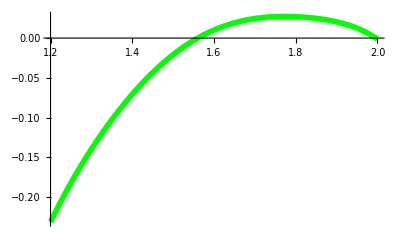

```mathematica
plotωnum=Plot[finf[rs],{rs,1.2,Rmax},PlotStyle->{Green,Thickness->0.01}]
```

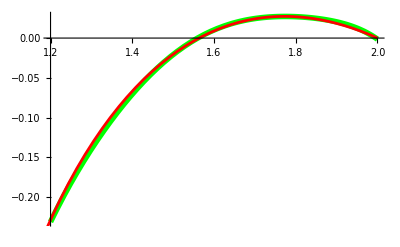

```mathematica
Show[plotωnum,plotωex]
```

```mathematica
(*r = 0.1*)
```

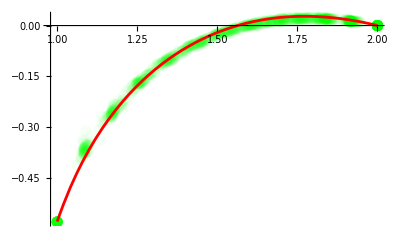

```mathematica
Show[plotωnum,plotωex]
```

```mathematica
(*r = 0.05*)
```

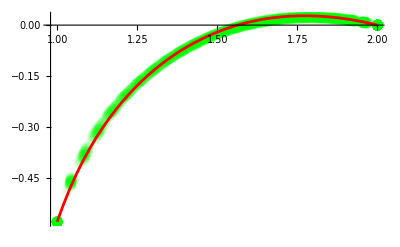

```mathematica
Show[plotωnum,plotωex]
```

```mathematica
(*r = 0.04*)
```

```mathematica
Show[plotωnum,plotωex]
```

-Graphics-

```mathematica
(*r=0.02*)
```

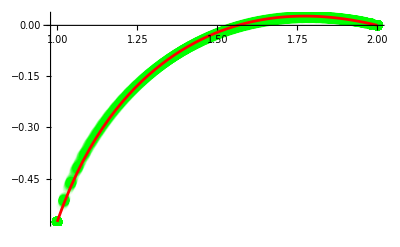

```mathematica
Show[plotωnum,plotωex]
```